# Bosonic CoP as a Function of Reference State Scale Hugo - 16 Dec 2019

## For the CFT Vacuum State & Gaussian Purifications

These are the data sets for complexity and entanglement of purification for a boson on a circle and on a line.

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import[NotebookDirectory[]<>"/GaussianOptimization.m"]
```

## Boson on a Circle

## CoP

The function used in the Gaussian optimization is CoPVal[NN, m, δ, μ, dimA1, dimB1, d] where:
NN is the total number of lattice points
m is the mass of the scalar field
δ is the lattice spacing (which will be kept fixed)
L=NN δ is the length of the circle
μ is the reference state frequency (assumed to be 1 in the following)
dimA1 is the number of sites in partition A1 of the subsystem
dimB1 is the number of sites in partition B1 of the subsystem
d is the lattice separation between the subsystem partitions A1 and B1
dimPur=dimA1+dimB1 is the dimension of the

In the following ‘w’ is also being used as the number of sites in the partitions A1 and B1 (assumed to be the same).

```mathematica
KGft[{NN_,δ_,m_,μ_}]:=KGft[{NN,δ,m,μ}]={Fourier[Table[(√((m^2+(2/δ Sin[(π k)/NN])^2)/NN))/μ,{k,0,NN-1}]]//Re,Fourier[Table[μ/√(NN(m^2+(2/δ Sin[(π k)/NN])^2)),{k,0,NN-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[NNδmμ_,{dimA_,dimB_,d_}]:=KGcmRes[NNδmμ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[NNδmμ]⟦1,ind,ind⟧,0.},{0.,KGb[NNδmμ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

```mathematica
KGcmqpqp[{NN_,δ_,m_,μ_}]:=KGcmqpqp[{NN,δ,m,μ}]=GOqpqpFROMqqpp[NN].KGcm[{NN,δ,m,μ}].Transpose[GOqpqpFROMqqpp[NN]];(* in qpqp basis *)
```

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
nb=NotebookDirectory[];
```

```mathematica
Directory[]
nb
```

/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code

/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/

```mathematica
VacCoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
dimPur=dimA1+dimB1;
CM0=KGcmRes[{NN,m,δ,μ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
J0=JR;
function=GOCoPBos[JT]; 
gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; 
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
CoPVal[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
CoPTime[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦1⟧;
```

## N=100, w=1

### μ=1/100

```mathematica
(*CoPCircleListN100dA1mu001=Table[{d,CoPVal[100,1/100,1/100,1/100,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu001={{0,6.652670609096465},{1,6.688596677305847},{2,6.689774015059714},{3,6.689961808041464},{4,6.6900135496777535},{5,6.690032767661844},{6,6.690041432168003},{7,6.690045917536541},{8,6.690048488279606},{9,6.6900500899763635},{10,6.690051166354667},{11,6.690051919828929},{12,6.690052478726624},{13,6.690052894384079},{14,6.69005323867974},{15,6.690053505845737},{16,6.690053732822344},{17,6.690053929791509},{18,6.69005407696409},{19,6.69005421539465},{20,6.69005434862308},{21,6.690054455781076},{22,6.690054556531799},{23,6.6900546438087085},{24,6.69005472217988},{25,6.690054793051282},{26,6.69005487446399},{27,6.690054937290756},{28,6.690054995729196},{29,6.690055029052815},{30,6.690055088964002},{31,6.690055132506169},{32,6.6900551721404735},{33,6.69005519911676},{34,6.6900552342441655},{35,6.690055275673497},{36,6.690055303251295},{37,6.690055323994523},{38,6.690055348709636},{39,6.690055366702737},{40,6.69005539112745},{41,6.69005540243703},{42,6.69005542418456},{43,6.690055431621019},{44,6.6900554402225945},{45,6.6900554534013414},{46,6.690055452876371},{47,6.6900554614880035},{48,6.690055471009992},{49,6.690055459080232}};
```

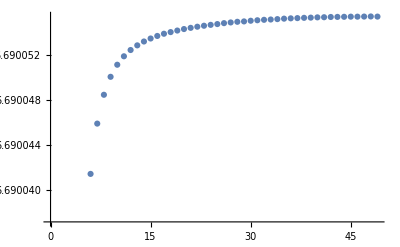

```mathematica
ListPlot[CoPCircleListN100dA1mu001]
```

### μ=1/10

```mathematica
(*CoPCircleListN100dA1mu01=Table[{d,CoPVal[100,1/100,1/100,1/10,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu01={{0,5.067189020755942},{1,5.102891640771061},{2,5.104201228367595},{3,5.104448525816746},{4,5.104533247571393},{5,5.1045736705702165},{6,5.104597392391725},{7,5.1046133271852145},{8,5.1046250445690236},{9,5.104634212083502},{10,5.104641703796592},{11,5.104648021292578},{12,5.104653473359287},{13,5.104658261134002},{14,5.104662522431646},{15,5.104666355013751},{16,5.104669830837468},{17,5.104673003970255},{18,5.104675916817031},{19,5.1046786017694235},{20,5.104681085680017},{21,5.104683390073911},{22,5.104685532839772},{23,5.104687528698454},{24,5.10468939040795},{25,5.1046911282738865},{26,5.104692751804856},{27,5.104694268599112},{28,5.104695685488491},{29,5.104697008629445},{30,5.104698242957684},{31,5.104699393361284},{32,5.104700463637597},{33,5.104701457608473},{34,5.1047023783533385},{35,5.104703228574676},{36,5.1047040110057385},{37,5.104704727517235},{38,5.1047053802337565},{39,5.1047059710333205},{40,5.104706501383893},{41,5.104706972469504},{42,5.104707385494991},{43,5.104707741726553},{44,5.104708041576136},{45,5.104708285999111},{46,5.10470847561523},{47,5.104708610828833},{48,5.104708691710364},{49,5.104708718659115}};
```

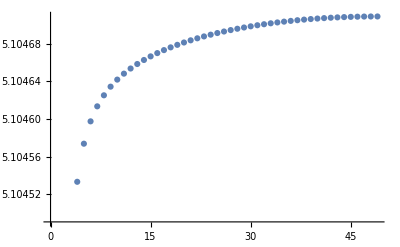

```mathematica
ListPlot[CoPCircleListN100dA1mu01]
```

### μ=1

```mathematica
(*CoPCircleListN100dA1mu1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu1={{0,3.640314891038023},{1,3.677627034008432},{2,3.6797260553581603},{3,3.680371196097706},{4,3.680710146946275},{5,3.680935258714125},{6,3.681103585073423},{7,3.681238230566535},{8,3.6813505622286957},{9,3.681446951566648},{10,3.681531329984454},{11,3.681606288135302},{12,3.6816736286507155},{13,3.6817346583160093},{14,3.6817903561017493},{15,3.6818414753032425},{16,3.6818886085657287},{17,3.6819322309999625},{18,3.6819727296370717},{19,3.6820104234036313},{20,3.6820455873127376},{21,3.6820784229370087},{22,3.6821091460114843},{23,3.6821379110142827},{24,3.6821648754223073},{25,3.6821901229791343},{26,3.6822137994190385},{27,3.6822359883694324},{28,3.682256773544017},{29,3.6822762260865227},{30,3.6822944144158227},{31,3.6823113961797396},{32,3.68232722330455},{33,3.682341942299552},{34,3.6823555947455118},{35,3.6823682176868515},{36,3.6823798440658395},{37,3.6823905042589433},{38,3.682400223707737},{39,3.6824090253708306},{40,3.682416931436123},{41,3.6824239590879864},{42,3.6824301245213324},{43,3.682435441297278},{44,3.6824399210309036},{45,3.6824435735028875},{46,3.6824464062267155},{47,3.682448425346345},{48,3.6824496352896245},{49,3.682450038343971}};
```

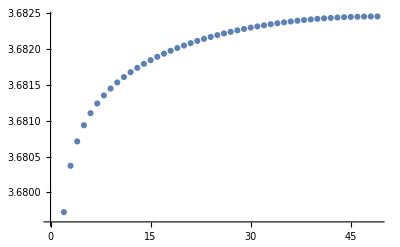

```mathematica
ListPlot[CoPCircleListN100dA1mu1]
```

### μ=8

```mathematica
(*CoPCircleListN100dA1mu8=Table[{d,CoPVal[100,1/100,1/100,8,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu8={{0,2.7722669220849205},{1,2.812671130096872},{2,2.8175937190196416},{3,2.8199815951676577},{4,2.821570156642717},{5,2.8227677175720753},{6,2.823730908773333},{7,2.8245365889752847},{8,2.825228424407813},{9,2.8258337337158044},{10,2.8263708095201068},{11,2.8268525332815364},{12,2.8272883348291917},{13,2.8276853331756078},{14,2.8280490390395383},{15,2.828383807650312},{16,2.8286931416920007},{17,2.8289799005824734},{18,2.8292464482455104},{19,2.8294947619204933},{20,2.8297265107192984},{21,2.8299431164162856},{22,2.8301457985103347},{23,2.830335611531961},{24,2.8305134714547786},{25,2.830680178785929},{26,2.830836436294048},{27,2.8309828635103673},{28,2.831120008554084},{29,2.8312483579871977},{30,2.8313683444036775},{31,2.831480354112073},{32,2.831584731860671},{33,2.8316817860385632},{34,2.831771792698622},{35,2.8318549986814325},{36,2.831931625107699},{37,2.8320018693166054},{38,2.832065907328651},{39,2.8321238953704615},{40,2.8321759719438164},{41,2.83222225867559},{42,2.8322628617121914},{43,2.8322978726754253},{44,2.832327369282101},{45,2.8323514164403063},{46,2.832370066381537},{47,2.832383359450796},{48,2.8323913237626357},{49,2.832393976691276}};
```

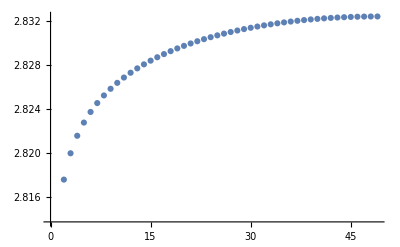

```mathematica
ListPlot[CoPCircleListN100dA1mu8]
```

### μ=10

```mathematica
(*CoPCircleListN100dA1mu10=Table[{d,CoPVal[100,1/100,1/100,10,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu10={{0,2.722738300565729},{1,2.763426328222676},{2,2.7688809664904466},{3,2.7716218214999535},{4,2.7734710560721463},{5,2.774874307199193},{6,2.776006790127321},{7,2.7769558787970636},{8,2.7777717552318753},{9,2.7784860522277355},{10,2.7791200656012736},{11,2.7796888508133666},{12,2.780203461644457},{13,2.780672261706692},{14,2.781101736351148},{15,2.7814970177259077},{16,2.78186223797846},{17,2.7822007728927534},{18,2.782515415700977},{19,2.7828085032331975},{20,2.783082009522605},{21,2.7833376161473713},{22,2.783576766923014},{23,2.7838007093288937},{24,2.7840105278901874},{25,2.78420717038648},{26,2.7843914689761204},{27,2.7845641573610127},{28,2.7847258847960528},{29,2.784877226875369},{30,2.7850186971007753},{31,2.7851507520300194},{32,2.7852738005682833},{33,2.785388207865909},{34,2.785494300840192},{35,2.7855923721255347},{36,2.7856826833134107},{37,2.7857654684038047},{38,2.7858409357676757},{39,2.7859092703969615},{40,2.7859706365107133},{41,2.786025178167103},{42,2.7860730209623252},{43,2.786114273394863},{44,2.786149027759542},{45,2.786177360734725},{46,2.7861993342783857},{47,2.78621499597584},{48,2.7862243794997466},{49,2.7862275051323264}};
```

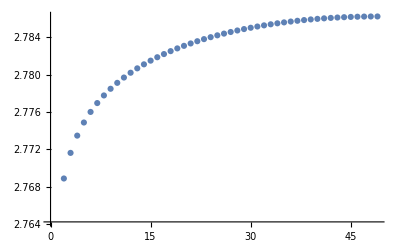

```mathematica
ListPlot[CoPCircleListN100dA1mu10]
```

### μ=12

```mathematica
(*CoPCircleListN100dA1mu12=Table[{d,CoPVal[100,1/100,1/100,12,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu12={{0,2.6903172973896545},{1,2.731210204857895},{2,2.737138232132251},{3,2.7401968819090934},{4,2.7422817453994317},{5,2.7438711973825325},{6,2.7451569990015514},{7,2.7462359625723827},{8,2.747164147342765},{9,2.747977089228095},{10,2.748698806787104},{11,2.749346328879472},{12,2.749932184638476},{13,2.7504658690665105},{14,2.750954753599763},{15,2.751404677365322},{16,2.751820344681396},{17,2.7522056012686162},{18,2.7525636305093073},{19,2.7528970965644306},{20,2.753208250555718},{21,2.753499010764996},{22,2.753771030920632},{23,2.7540257141446776},{24,2.7542643183116264},{25,2.754487918433911},{26,2.7546974637065347},{27,2.754893792009482},{28,2.7550776440000853},{29,2.7552496773552746},{30,2.7554104772587644},{31,2.7555605655949553},{32,2.755700408561074},{33,2.7558304231064015},{34,2.755950982358191},{35,2.7560624202684445},{36,2.7561650355581144},{37,2.756259095113696},{38,2.756344836730912},{39,2.7564224719564066},{40,2.756492187747701},{41,2.7565541484330836},{42,2.7566084977825804},{43,2.7566553593199647},{44,2.756694838473115},{45,2.7567270227238105},{46,2.7567519827405715},{47,2.756769772910701},{48,2.756780431644598},{49,2.7567839820920237}};
```

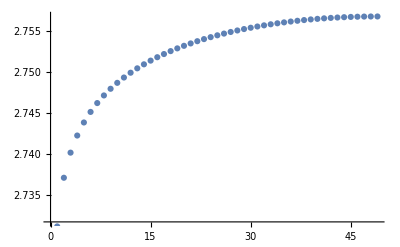

```mathematica
ListPlot[CoPCircleListN100dA1mu12]
```

### μ=100

```mathematica
(*CoPCircleListN100dA1mu100=Table[{d,CoPVal[100,1/100,1/100,100,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu100={{0,2.8762886060324955},{1,2.9181636778263527},{2,2.9315047466123927},{3,2.939747309109378},{4,2.9457123513012693},{5,2.950369282364694},{6,2.954173960023004},{7,2.957378458783439},{8,2.960137068755362},{9,2.9625511252896803},{10,2.9646907475307125},{11,2.9666064448152056},{12,2.968335794768017},{13,2.9699074669783636},{14,2.9713438700359625},{15,2.972662797637998},{16,2.9738786205263503},{17,2.975003110296672},{18,2.9760460157729867},{19,2.977015499901671},{20,2.9779184599978543},{21,2.978760772776728},{22,2.9795474811790736},{23,2.980282942451778},{24,2.980970937003643},{25,2.981614774342676},{26,2.9822173527146134},{27,2.9827812272739265},{28,2.9833086547744974},{29,2.9838016421437983},{30,2.9842619635310834},{31,2.984691207244102},{32,2.9850907933076276},{33,2.985461985115053},{34,2.98580591682085},{35,2.9861235944303615},{36,2.9864159260500744},{37,2.9866837209857846},{38,2.9869276999173393},{39,2.9871484940286486},{40,2.9873466772210557},{41,2.987522741328591},{42,2.9876771213266213},{43,2.9878101904488696},{44,2.9879222658554334},{45,2.9880136117536273},{46,2.988084440890901},{47,2.9881349173408975},{48,2.9881651570029057},{49,2.9881752292241246}};
```

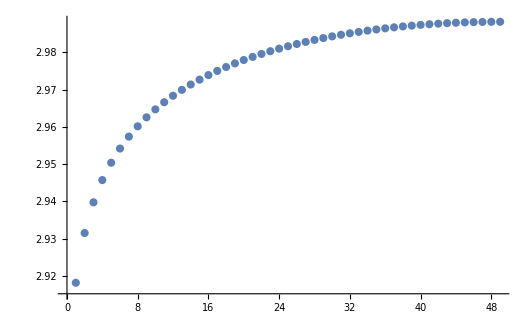

```mathematica
ListPlot[CoPCircleListN100dA1mu100]
```

### μ=1000

```mathematica
(*CoPCircleListN100dA1mu1000=Table[{d,CoPVal[100,1/100,1/100,1000,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPCircleListN100dA1mu1000={{0,3.952279745749531},{1,3.999387864550901},{2,4.021437207380841},{3,4.035700840721868},{4,4.046112462038845},{5,4.054238136991915},{6,4.060856740154087},{7,4.066410070002673},{8,4.071171916806988},{9,4.07532318476644},{10,4.078989370927487},{11,4.082260935701414},{12,4.085205135425341},{13,4.087873268431032},{14,4.090305307568301},{15,4.09253297372976},{16,4.094581836941807},{17,4.09647279064361},{18,4.098223111947881},{19,4.099847237798232},{20,4.101357344319372},{21,4.102763786317852},{22,4.104075433950404},{23,4.105299936568544},{24,4.106443928976468},{25,4.107513196164062},{26,4.108512806562952},{27,4.109447218135605},{28,4.110320367099302},{29,4.111135739472659},{30,4.111896430913268},{31,4.112605196565618},{32,4.11326449337702},{33,4.113876513800369},{34,4.114443217214781},{35,4.114966354312582},{36,4.115447488352666},{37,4.115888013693778},{38,4.116289172476578},{39,4.116652066686201},{40,4.116977669433978},{41,4.117266837079837},{42,4.1175203147284485},{43,4.117738745089788},{44,4.117922674323768},{45,4.1180725565221135},{46,4.118188757745047},{47,4.118271559443148},{48,4.118321161272019},{49,4.118337682015642}};
```

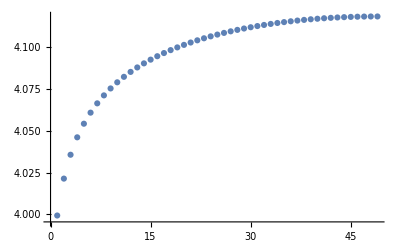

```mathematica
ListPlot[CoPCircleListN100dA1mu1000]
```

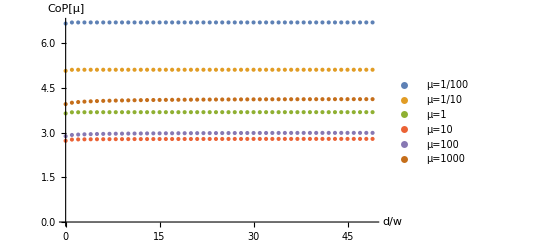

```mathematica
ListPlot[{CoPCircleListN100dA1mu001,CoPCircleListN100dA1mu01,CoPCircleListN100dA1mu1,CoPCircleListN100dA1mu10,CoPCircleListN100dA1mu100,CoPCircleListN100dA1mu1000},PlotLegends-> {"μ=1/100","μ=1/10","μ=1","μ=10","μ=100","μ=1000"},AxesLabel->{"d/w","CoP[μ]"}]
```

## Fixed d, Different values of μ

### Lists for N=100, A=B=1

```mathematica
Listμ1=Join[Reverse[Table[μ,{μ,2,1000,2}]],{1},Table[1/μ,{μ,2,1000,2}]];
```

```mathematica
(*CoPCircleN100A1d0List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,0]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d0List={{1000,3.952279745657167},{998,3.9511323994781438},{996,3.9499829893640706},{994,3.9488315080777148},{992,3.9476779477234047},{990,3.946522301036176},{988,3.945364560057634},{986,3.9442047171741814},{984,3.943042764769511},{982,3.941878694734865},{980,3.9407124993257368},{978,3.9395441705948726},{976,3.938373700740132},{974,3.937201081808474},{972,3.9360263056294427},{970,3.9348493640533477},{968,3.9336702491149222},{966,3.932488952550927},{964,3.931305466255034},{962,3.930119781936128},{960,3.9289318910990945},{958,3.927741785586896},{956,3.926549456864228},{954,3.9253548967462453},{952,3.924158096280958},{950,3.9229590474101657},{948,3.921757741158803},{946,3.9205541690361088},{944,3.9193483222625902},{942,3.9181401923017063},{940,3.9169297700406975},{938,3.9157170466579068},{936,3.914502013579509},{934,3.913284661508931},{932,3.9120649816623607},{930,3.9108429646338343},{928,3.909618601742783},{926,3.9083918834490197},{924,3.9071628007469172},{922,3.905931344379393},{920,3.9046975049144548},{918,3.9034612730310574},{916,3.902222639117939},{914,3.900981593810929},{912,3.899738127507068},{910,3.898492230667223},{908,3.897243893498917},{906,3.8959931062571402},{904,3.894739859414317},{902,3.893484142769074},{900,3.8922259466794635},{898,3.8909652609042213},{896,3.8897020755876985},{894,3.888436380619588},{892,3.8871681659593},{890,3.885897421145915},{888,3.8846241359327345},{886,3.8833483002189393},{884,3.882069903535228},{882,3.88078893504582},{880,3.879505384681406},{878,3.8782192416607},{876,3.876930495189254},{874,3.875639134588737},{872,3.8743451492682612},{870,3.8730485280365703},{868,3.871749260281525},{866,3.8704473346606556},{864,3.86914274047277},{862,3.8678354662788856},{860,3.866525501056823},{858,3.86521283346094},{856,3.8638974518060554},{854,3.862579345196036},{852,3.8612585018280488},{850,3.8599349102119924},{848,3.858608558604516},{846,3.8572794353937376},{844,3.855947528677655},{842,3.854612826741436},{840,3.8532753174971206},{838,3.851934988946277},{836,3.85059182885589},{834,3.849245825174636},{832,3.8478969656912296},{830,3.8465452380433156},{828,3.8451906297168925},{826,3.8438331281552167},{824,3.842472720892368},{822,3.841109395179036},{820,3.839743138281893},{818,3.838373937339194},{816,3.8370017794887095},{814,3.83562665155998},{812,3.8342485406046802},{810,3.8328674334440476},{808,3.8314833167539497},{806,3.830096177128277},{804,3.828706001107325},{802,3.8273127751802702},{800,3.825916485796618},{798,3.824517119042414},{796,3.8231146612577493},{794,3.8217090984412514},{792,3.8203004165781365},{790,3.8188886016033887},{788,3.817473639232852},{786,3.81605551520412},{784,3.814634215342624},{782,3.8132097247184764},{780,3.8117820290651565},{778,3.810351113445346},{776,3.8089169633227637},{774,3.807479563563964},{772,3.8060388992052836},{770,3.8045949554482403},{768,3.803147716380349},{766,3.801697167278457},{764,3.800243292583426},{762,3.7987860765324815},{760,3.7973255037835787},{758,3.7958615581423474},{756,3.7943942241721795},{754,3.792923485744349},{752,3.7914493266414815},{750,3.7899717306705467},{748,3.7884906815880215},{746,3.787006162974866},{744,3.7855181579783825},{742,3.7840266501646256},{740,3.7825316226870838},{738,3.7810330584005842},{736,3.779530940562892},{734,3.7780252519059396},{732,3.7765159749448562},{730,3.7750030923643787},{728,3.7734865865537395},{726,3.7719664398588155},{724,3.7704426344269506},{722,3.768915152328675},{720,3.7673839755472396},{718,3.7658490854963884},{716,3.764310464293286},{714,3.762768093138117},{712,3.7612219533997995},{710,3.7596720265290506},{708,3.7581182934068176},{706,3.7565607348568237},{704,3.754999331953166},{702,3.753434065165138},{700,3.7518649150806533},{698,3.750291861875733},{696,3.7487148859988806},{694,3.7471339671551207},{692,3.7455490856719766},{690,3.7439602209855933},{688,3.7423673527205703},{686,3.7407704602631178},{684,3.7391695230237474},{682,3.737564520017401},{680,3.735955430048696},{678,3.734342232013405},{676,3.7327249046944435},{674,3.7311034261310176},{672,3.729477775075452},{670,3.727847929009365},{668,3.726213866229131},{666,3.7245755646111003},{664,3.7229330014165014},{662,3.721286154067822},{660,3.7196349999891383},{658,3.7179795159517446},{656,3.7163196789310504},{654,3.714655465559995},{652,3.712986852092035},{650,3.711313815171447},{648,3.709636330531255},{646,3.707954374064505},{644,3.706267921840283},{642,3.7045769488455433},{640,3.7028814305324693},{638,3.701181341962079},{636,3.6994766580969167},{634,3.6977673534453643},{632,3.6960534025774487},{630,3.69433477961286},{628,3.6926114585847687},{626,3.6908834131898143},{624,3.689150617195667},{622,3.6874130438585837},{620,3.6856706662719994},{618,3.6839234572730057},{616,3.682171389677802},{614,3.6804144357557007},{612,3.6786525677710022},{610,3.676885757694449},{608,3.675113977022377},{606,3.6733371975378577},{604,3.671555390233109},{602,3.6697685260761257},{600,3.6679765759320335},{598,3.666179510007186},{596,3.6643772987236805},{594,3.6625699118329305},{592,3.6607573192166276},{590,3.6589394899229357},{588,3.6571163932847277},{586,3.6552879981840323},{584,3.65345427321473},{582,3.651615186364966},{580,3.649770705986823},{578,3.647920799682553},{576,3.646065434692534},{574,3.6442045783367853},{572,3.6423381973014686},{570,3.6404662580934106},{568,3.638588727100625},{566,3.636705570074299},{564,3.6348167525814823},{562,3.6329222399625447},{560,3.6310219971297517},{558,3.6291159886507676},{556,3.6272041788836122},{554,3.625286531735707},{552,3.623363010834833},{550,3.621433579447542},{548,3.6194982004366936},{546,3.6175568365352575},{544,3.615609449774904},{542,3.613656002001513},{540,3.6116964548576664},{538,3.609730769288332},{536,3.607758906195922},{534,3.6057808257972326},{532,3.6037964881037845},{530,3.6018058527112955},{528,3.5998088789826457},{526,3.5978055254299317},{524,3.5957957506469462},{522,3.593779512342673},{520,3.5917567682639464},{518,3.589727475657667},{516,3.58769159108017},{514,3.585649070796639},{512,3.5835998706955197},{510,3.5815439461014096},{508,3.579481252118175},{506,3.577411743160756},{504,3.575335373170526},{502,3.5732520957486082},{500,3.571161864039362},{498,3.5690646305199576},{496,3.566960347458557},{494,3.564848966331344},{492,3.5627304383728506},{490,3.5606047140564634},{488,3.558471743617909},{486,3.556331476492845},{484,3.5541838617522115},{482,3.552028847958948},{480,3.5498663830025823},{478,3.5476964143127896},{476,3.5455188886821043},{474,3.5433337524306263},{472,3.541140951197033},{470,3.5389404301940646},{468,3.5367321338387874},{466,3.5345160060807874},{464,3.532291990177923},{462,3.5300600288889195},{460,3.527820064168138},{458,3.5255720375388147},{456,3.523315889617686},{454,3.5210515606521438},{452,3.5187789900442223},{450,3.5164981165114964},{448,3.514208878174784},{446,3.511911212462378},{444,3.5096050559627487},{442,3.5072903446807597},{440,3.5049670137810716},{438,3.5026349978942664},{436,3.5002942305754687},{434,3.4979446449180664},{432,3.4955861730869344},{430,3.4932187464907534},{428,3.4908422957850473},{426,3.4884567506539215},{424,3.486062040216102},{422,3.4836580925634255},{420,3.4812448349637135},{418,3.4788221939217587},{416,3.4763900949182616},{414,3.4739484627018786},{412,3.471497220953128},{410,3.4690362925505616},{408,3.4665655994049014},{406,3.464085062463301},{404,3.4615946017719947},{402,3.459094136301115},{400,3.4565835841477206},{398,3.454062862247068},{396,3.4515318866069173},{394,3.4489905722562817},{392,3.4464388328337447},{390,3.4438765814963044},{388,3.4413037296248037},{386,3.438720188027782},{384,3.4361258660598684},{382,3.4335206720417477},{380,3.4309045130942546},{378,3.428277295163641},{376,3.425638922981846},{374,3.4229893000870697},{372,3.4203283286333153},{370,3.4176559095729973},{368,3.4149719426690783},{366,3.412276326234114},{364,3.4095689572470604},{362,3.406849731263817},{360,3.404118542687614},{358,3.4013752842687404},{356,3.398619847327812},{354,3.3958521219000883},{352,3.393071996441913},{350,3.390279357714569},{348,3.387474091214174},{346,3.3846560807035204},{344,3.3818252083840674},{342,3.3789813548642433},{340,3.376124398962866},{338,3.3732542179309974},{336,3.370370687340674},{334,3.3674736808243493},{332,3.364563070396458},{330,3.36163872627197},{328,3.358700516616449},{326,3.3557483079216777},{324,3.352781964643258},{322,3.3498013493078163},{320,3.3468063224645106},{318,3.3437967426240105},{316,3.34077246620391},{314,3.3377333475437045},{312,3.3346792388166233},{310,3.331609989974659},{308,3.3285254488084437},{306,3.3254254608175184},{304,3.3223098690872956},{302,3.319178514438323},{300,3.3160312353234556},{298,3.3128678675781287},{296,3.3096882446596667},{294,3.3064921973618806},{292,3.303279554040805},{290,3.3000501402276736},{288,3.296803778837934},{286,3.2935402899861774},{284,3.2902594909048326},{282,3.2869611961213554},{280,3.2836452171042203},{278,3.2803113623359357},{276,3.2769594372662647},{274,3.2735892442187384},{272,3.2702005823339846},{270,3.2667932475401424},{268,3.263367032467284},{266,3.2599217263016964},{264,3.256457114752777},{262,3.2529729801871654},{260,3.2494691012768437},{258,3.245945252952395},{256,3.242401206539942},{254,3.2388367294958265},{252,3.235251585377457},{250,3.231645533763248},{248,3.2280183302016634},{246,3.224369726089557},{244,3.2206994685478656},{242,3.2170073004888105},{240,3.213292960267603},{238,3.209556181939175},{236,3.2057966948912986},{234,3.20201422370946},{232,3.198208488341949},{230,3.194379203901707},{228,3.190526080420378},{226,3.1866488227528342},{224,3.1827471309543234},{222,3.1788206993076384},{220,3.174869217091142},{218,3.1708923678818204},{216,3.166889829784813},{214,3.162861274950504},{212,3.1588063699582856},{210,3.1547247753809677},{208,3.150616145598924},{206,3.1464801289578808},{204,3.1423163674481174},{202,3.138124496683182},{200,3.1339041457917203},{198,3.1296549371269866},{196,3.125376486425829},{194,3.1210684025941875},{192,3.1167302873963725},{190,3.1123617355775015},{188,3.1079623347111265},{186,3.103531665061606},{184,3.099069299426789},{182,3.0945748030449374},{180,3.0900477338025345},{178,3.08548764161947},{176,3.0808940686562973},{174,3.0762665494585173},{172,3.0716046104123182},{170,3.0669077700367855},{168,3.062175538915734},{166,3.057407419391589},{164,3.0526029062570044},{162,3.0477614856167397},{160,3.042882636054889},{158,3.0379658281581463},{156,3.03301052454601},{154,3.0280161802433008},{152,3.0229822426708286},{150,3.0179081519062705},{148,3.012793340765883},{146,3.0076372356900865},{144,3.002439256021535},{142,2.9971988155815295},{140,2.991915322397207},{138,2.9865881796694898},{136,2.981216786448545},{134,2.975800538255162},{132,2.9703388279492224},{130,2.9648310471803563},{128,2.95927658729584},{126,2.9536748408735827},{124,2.9480252031702645},{122,2.9423270743423053},{120,2.936579861555213},{118,2.93078298074671},{116,2.924935859991145},{114,2.9190379429266953},{112,2.9130886918026357},{110,2.9070875916477474},{108,2.901034155585587},{106,2.894927929653466},{104,2.8887684991987648},{102,2.8825554959557915},{100,2.8762886060399735},{98,2.869967579426599},{96,2.863592240314962},{94,2.857162499597455},{92,2.8506783687082518},{90,2.8441399759213053},{88,2.837547584766037},{86,2.8309016160567384},{84,2.824202672142385},{82,2.817451566509361},{80,2.8106493567894746},{78,2.803797384473949},{76,2.7968973202590144},{74,2.7899512195610825},{72,2.7829616939286987},{70,2.7759313967447334},{68,2.7688643325318303},{66,2.7617647035523065},{64,2.754637686487455},{62,2.7474894207301777},{60,2.740327224185203},{58,2.7331597721596586},{56,2.7259973713122263},{54,2.718852270355112},{52,2.7117390439047395},{50,2.704675065249899},{48,2.6976810925322527},{46,2.6907819980456},{44,2.6840076920461002},{42,2.677394284274096},{40,2.670985580774355},{38,2.6648350008305135},{36,2.6590081171851705},{34,2.6535859655775655},{32,2.6486695178286923},{30,2.6443857497860392},{28,2.640896036906966},{26,2.6384079681213737},{24,2.6371924030314347},{22,2.6376085752879606},{20,2.6401422752469195},{18,2.645465806411656},{16,2.6545360568521676},{14,2.6687629809071525},{12,2.690317297226934},{10,2.722738287012191},{8,2.772266922336418},{6,2.8512365794897674},{4,2.988924263404601},{2,3.284852951300944},{1,3.6403148910376624},{1/2,4.03889289255585},{1/4,4.468092104615028},{1/6,4.7295698611265875},{1/8,4.918721045676356},{1/10,5.067189020770146},{1/12,5.1894913729512915},{1/14,5.293522553917184},{1/16,5.3840605965379265},{1/18,5.464220301851625},{1/20,5.536146503992898},{1/22,5.601379689636618},{1/24,5.661063950542541},{1/26,5.716072462541459},{1/28,5.76708689285257},{1/30,5.814649674980254},{1/32,5.8591995595915805},{1/34,5.901096492016224},{1/36,5.940639441312922},{1/38,5.978079452695818},{1/40,6.013629385574976},{1/42,6.047471291242023},{1/44,6.079762078491163},{1/46,6.110637994033276},{1/48,6.14021801217659},{1/50,6.168606722641005},{1/52,6.195896506497357},{1/54,6.222169444727059},{1/56,6.247498658568322},{1/58,6.271949707930931},{1/60,6.295581520345374},{1/62,6.318447288843},{1/64,6.340595172721961},{1/66,6.362068953651719},{1/68,6.382908465103024},{1/70,6.403150166004933},{1/72,6.422827425784747},{1/74,6.44197092547622},{1/76,6.4606088534922845},{1/78,6.478767257495113},{1/80,6.496470239308195},{1/82,6.513740067706239},{1/84,6.530597505229093},{1/86,6.547061758746669},{1/88,6.563150790419917},{1/90,6.578881315739414},{1/92,6.594268994700931},{1/94,6.609328465869437},{1/96,6.624073430044601},{1/98,6.638516767910471},{1/100,6.652670609410054},{1/102,6.666546301641352},{1/104,6.680154597127012},{1/106,6.693505590396885},{1/108,6.706608876299129},{1/110,6.719473450532826},{1/112,6.732107836138439},{1/114,6.744520225453002},{1/116,6.756718198270668},{1/118,6.768709081094209},{1/120,6.780499785007217},{1/122,6.792096868223345},{1/124,6.803506633858508},{1/126,6.81473500725556},{1/128,6.8257876658033645},{1/130,6.8366700324699625},{1/132,6.8473873297961205},{1/134,6.8579444118776145},{1/136,6.868345987202832},{1/138,6.87859666499026},{1/140,6.8887006946938625},{1/142,6.898662259923773},{1/144,6.908485304172346},{1/146,6.9181736112484655},{1/148,6.927730904348867},{1/150,6.937160503036932},{1/152,6.9464660266645275},{1/154,6.955650437644812},{1/156,6.964717040350404},{1/158,6.97366876050873},{1/160,6.982508443040931},{1/162,6.991238930117041},{1/164,6.999862805008468},{1/166,7.0083827577108355},{1/168,7.016801061890431},{1/170,7.025120362728142},{1/172,7.033342722039668},{1/174,7.0414705437715694},{1/176,7.049505905026555},{1/178,7.0574509414701225},{1/180,7.065307587778297},{1/182,7.0730778693720024},{1/184,7.080763610793392},{1/186,7.088366666503959},{1/188,7.095888755333795},{1/190,7.103331580060731},{1/192,7.110696863101329},{1/194,7.117986173819807},{1/196,7.125200924100041},{1/198,7.1323428762407906},{1/200,7.139413336559633},{1/202,7.146413712457123},{1/204,7.153345441144463},{1/206,7.16020985994181},{1/208,7.1670081466875715},{1/210,7.173741717912245},{1/212,7.180411689760668},{1/214,7.187019319020371},{1/216,7.193565704444476},{1/218,7.200051987527027},{1/220,7.2064792865067995},{1/222,7.212848720999237},{1/224,7.219161101006487},{1/226,7.225417747122375},{1/228,7.231619328936084},{1/230,7.2377670648407655},{1/232,7.243861737205626},{1/234,7.249904432238228},{1/236,7.255895586524132},{1/238,7.261836576717686},{1/240,7.267727983133321},{1/242,7.273570713900509},{1/244,7.279365450627316},{1/246,7.285113130002125},{1/248,7.2908144849205545},{1/250,7.296470160210672},{1/252,7.302080835414623},{1/254,7.307647518371713},{1/256,7.3131705231086315},{1/258,7.318650885771716},{1/260,7.324088702380626},{1/262,7.329485299160468},{1/264,7.33484108331105},{1/266,7.340156170715083},{1/268,7.34543207112423},{1/270,7.350668415474888},{1/272,7.355866531277666},{1/274,7.361026622969713},{1/276,7.366149141430035},{1/278,7.371234999154511},{1/280,7.37628451468397},{1/282,7.381298114873875},{1/284,7.386276453762484},{1/286,7.3912200022984385},{1/288,7.396129103622415},{1/290,7.4010043212176315},{1/292,7.405846252349328},{1/294,7.410655312983602},{1/296,7.4154318709559055},{1/298,7.420175989837242},{1/300,7.424888745324796},{1/302,7.429570170425722},{1/304,7.4342212141889155},{1/306,7.43884135840611},{1/308,7.44343154145911},{1/310,7.447992231912528},{1/312,7.452523159686292},{1/314,7.457026176301475},{1/316,7.4615002903025704},{1/318,7.465945505334116},{1/320,7.470364100031887},{1/322,7.474754860869921},{1/324,7.479118386475537},{1/326,7.48345485124202},{1/328,7.487765488964613},{1/330,7.492049903595807},{1/332,7.496308315546906},{1/334,7.50054117726162},{1/336,7.5047486260465845},{1/338,7.508931249088534},{1/340,7.513089753252482},{1/342,7.517222870656813},{1/344,7.521332008770224},{1/346,7.525419376797078},{1/348,7.529481630375961},{1/350,7.533520915041329},{1/352,7.537537299286912},{1/354,7.541530915138528},{1/356,7.545500966379714},{1/358,7.549451363448695},{1/360,7.55337845591909},{1/362,7.557283844296672},{1/364,7.561166124201861},{1/366,7.565029370451312},{1/368,7.568872053199452},{1/370,7.572693074769307},{1/372,7.576492586678625},{1/374,7.580272267860862},{1/376,7.584030321582117},{1/378,7.58777335001193},{1/380,7.591491866161473},{1/382,7.595193082381221},{1/384,7.598876266525787},{1/386,7.60253878840815},{1/388,7.6061820985176185},{1/390,7.609806187725276},{1/392,7.613413441590457},{1/394,7.617001838104171},{1/396,7.6205708456172},{1/398,7.624122494146284},{1/400,7.627658490491393},{1/402,7.631173212835336},{1/404,7.634674235827488},{1/406,7.638156372023963},{1/408,7.641621385174738},{1/410,7.6450684211748525},{1/412,7.648500927263764},{1/414,7.651915847900543},{1/416,7.655313919988725},{1/418,7.658695952370924},{1/420,7.662062264429296},{1/422,7.665412311844489},{1/424,7.668746177391881},{1/426,7.672064003544046},{1/428,7.67536790064962},{1/430,7.678655616235013},{1/432,7.681926443862956},{1/434,7.685184811893781},{1/436,7.68842783416768},{1/438,7.691655467784361},{1/440,7.694866103683514},{1/442,7.698067185623693},{1/444,7.701249479664326},{1/446,7.7044211773862195},{1/448,7.707576532034266},{1/450,7.710714709250649},{1/452,7.713844205114224},{1/454,7.716959849633929},{1/456,7.720057408753724},{1/458,7.723143442080404},{1/460,7.7262172582050335},{1/462,7.729275969274928},{1/464,7.7323242772438725},{1/466,7.7353580718345665},{1/468,7.738381074002848},{1/470,7.741387884541585},{1/472,7.744382854913283},{1/474,7.747363612844198},{1/476,7.750333065379597},{1/478,7.753291768893466},{1/480,7.7562388065524255},{1/482,7.7591685357433455},{1/484,7.762089974869063},{1/486,7.76499753136451},{1/488,7.767895928678349},{1/490,7.770783324368325},{1/492,7.773652004177744},{1/494,7.77651367554281},{1/496,7.779368415313615},{1/498,7.782202393360458},{1/500,7.785032551989836},{1/502,7.78784459256521},{1/504,7.790655915409483},{1/506,7.7934500261432955},{1/508,7.796232580270623},{1/510,7.7990007304984745},{1/512,7.801762134947453},{1/514,7.804509093738788},{1/516,7.807256089338114},{1/518,7.809985189809195},{1/520,7.812700729107065},{1/522,7.815412017057932},{1/524,7.818105627546174},{1/526,7.82079360467449},{1/528,7.823474910958968},{1/530,7.826141325850834},{1/532,7.828798437283066},{1/534,7.831440844597684},{1/536,7.834084316691259},{1/538,7.836711911457834},{1/540,7.839328068313559},{1/542,7.841933528623821},{1/544,7.844529709988352},{1/546,7.847121995836789},{1/548,7.8497004401564405},{1/550,7.8522708336792695},{1/552,7.854836196756019},{1/554,7.857387480463227},{1/556,7.859927634440182},{1/558,7.862463848087017},{1/560,7.864985004450057},{1/562,7.867503503679006},{1/564,7.870003962884061},{1/566,7.872508785173817},{1/568,7.87499689761367},{1/570,7.877477786134886},{1/572,7.879948300455437},{1/574,7.882408413638295},{1/576,7.884865270360001},{1/578,7.887311577305565},{1/580,7.889741709961571},{1/582,7.892175772158111},{1/584,7.894595085484624},{1/586,7.897005726624118},{1/588,7.8994104590458765},{1/590,7.9018112647412915},{1/592,7.904199766638526},{1/594,7.906576958676527},{1/596,7.908946994765158},{1/598,7.91131139217999},{1/600,7.913664991083454},{1/602,7.916020004427324},{1/604,7.918357333993854},{1/606,7.92068565588219},{1/608,7.92301834581126},{1/610,7.925335819031683},{1/612,7.927640086481737},{1/614,7.929948195475681},{1/616,7.93223876828648},{1/618,7.934528520118643},{1/620,7.936809656993888},{1/622,7.939083463464127},{1/624,7.941338672264682},{1/626,7.943607211260966},{1/628,7.945851053860056},{1/630,7.948093205806111},{1/632,7.950334678499609},{1/634,7.9525640599166705},{1/636,7.954789304069498},{1/638,7.95700186339371},{1/640,7.959208279736256},{1/642,7.961411152706671},{1/644,7.9636127306208735},{1/646,7.965799143216168},{1/648,7.967972043601511},{1/650,7.970152295857439},{1/652,7.972318236373799},{1/654,7.974478794884618},{1/656,7.976631746551882},{1/658,7.978779749030325},{1/660,7.980932922304224},{1/662,7.983068404983043},{1/664,7.985197484273355},{1/666,7.987320097386165},{1/668,7.9894363617186},{1/670,7.991546308570396},{1/672,7.993641935829218},{1/674,7.995743725935791},{1/676,7.997833396330701},{1/678,7.999920388930811},{1/680,8.002002549684905},{1/682,8.00407535790929},{1/684,8.006136249511549},{1/686,8.008197410906888},{1/688,8.010244476120105},{1/690,8.01230638212797},{1/692,8.014349234782328},{1/694,8.016385500285182},{1/696,8.018414807750771},{1/698,8.020434717848628},{1/700,8.022444284872595},{1/702,8.024475907521904},{1/704,8.02648134188658},{1/706,8.028479819600078},{1/708,8.030481349578283},{1/710,8.032471092717788},{1/712,8.03445815918883},{1/714,8.036439432852548},{1/716,8.038407681460475},{1/718,8.040382721628642},{1/720,8.042327280227394},{1/722,8.044296247381837},{1/724,8.046240186306951},{1/726,8.048193277037134},{1/728,8.050129603737997},{1/730,8.052064294776793},{1/732,8.054001350672078},{1/734,8.055930314316827},{1/736,8.057849773917324},{1/738,8.059773738638956},{1/740,8.061681655728306},{1/742,8.063591118233784},{1/744,8.0654829479243},{1/746,8.067384757434006},{1/748,8.069262685114055},{1/750,8.071148981520409},{1/752,8.073039620902133},{1/754,8.07491580592154},{1/756,8.076774646527992},{1/758,8.07864466379258},{1/760,8.0804957752733},{1/762,8.0823454203696},{1/764,8.084206153975881},{1/766,8.08606174473853},{1/768,8.087888639149371},{1/770,8.089738428845983},{1/772,8.091561507301176},{1/774,8.093381332780037},{1/776,8.095200941704354},{1/778,8.097024184604596},{1/780,8.09883664115424},{1/782,8.100643614803804},{1/784,8.102446828930503},{1/786,8.104255735430613},{1/788,8.106040218289559},{1/790,8.107831494372126},{1/792,8.109617703455925},{1/794,8.111404544960259},{1/796,8.113178816308139},{1/798,8.114940980670381},{1/800,8.116715089003554},{1/802,8.118475183659195},{1/804,8.120237890156888},{1/806,8.12199295199735},{1/808,8.123732594401766},{1/810,8.125484893441545},{1/812,8.127222524197741},{1/814,8.128959038199344},{1/816,8.13068583020207},{1/818,8.132420649733573},{1/820,8.1341399194027},{1/822,8.135870567930967},{1/824,8.137577591827613},{1/826,8.139281926514991},{1/828,8.140997290300962},{1/830,8.142689725290294},{1/832,8.144407311020057},{1/834,8.146092920124824},{1/836,8.147781428724025},{1/838,8.149480323203042},{1/840,8.151153324071782},{1/842,8.152831550013294},{1/844,8.154508789481723},{1/846,8.1561830344439},{1/848,8.157834746347305},{1/850,8.159503315403398},{1/852,8.161174737127855},{1/854,8.16281065846953},{1/856,8.164480316202555},{1/858,8.166130652250684},{1/860,8.16776181343586},{1/862,8.169402182475613},{1/864,8.171051516889246},{1/866,8.172668384041764},{1/868,8.174301855289983},{1/870,8.175915749872743},{1/872,8.177539949798689},{1/874,8.179163391308176},{1/876,8.180781369237362},{1/878,8.182379576626918},{1/880,8.183984755433718},{1/882,8.18559564794796},{1/884,8.187192584916454},{1/886,8.188788193754775},{1/888,8.190382143170444},{1/890,8.191971811644535},{1/892,8.193570170120694},{1/894,8.195136511696587},{1/896,8.196727156177342},{1/898,8.19828708275814},{1/900,8.19986140775988},{1/902,8.201426200918736},{1/904,8.202990622043215},{1/906,8.204545588425445},{1/908,8.206122394200575},{1/910,8.207666377722896},{1/912,8.209224899020468},{1/914,8.210753649915764},{1/916,8.212310358950518},{1/918,8.213839018482997},{1/920,8.2153871908817},{1/922,8.216913155588431},{1/924,8.218454089743862},{1/926,8.219967998950994},{1/928,8.221482075177168},{1/930,8.22300338023722},{1/932,8.22454071169657},{1/934,8.226030042985723},{1/936,8.227566110882663},{1/938,8.229059094326502},{1/940,8.230576080767657},{1/942,8.232051900356959},{1/944,8.23355169288819},{1/946,8.235049997939845},{1/948,8.236549892284744},{1/950,8.238041571497984},{1/952,8.239533011820859},{1/954,8.241008371332804},{1/956,8.242475861155315},{1/958,8.243969759818555},{1/960,8.245439980115552},{1/962,8.24690711981758},{1/964,8.248374614141026},{1/966,8.249833342938},{1/968,8.251270809585458},{1/970,8.25274412109101},{1/972,8.25419215918934},{1/974,8.255661905198913},{1/976,8.257112136351228},{1/978,8.258554296558186},{1/980,8.25999252861236},{1/982,8.261439374085402},{1/984,8.262859009769462},{1/986,8.264311859659035},{1/988,8.265715842304214},{1/990,8.26716692914774},{1/992,8.268573911380917},{1/994,8.269993991647416},{1/996,8.271429593690726},{1/998,8.272853651069074},{1/1000,8.274248716996915}};
```

```mathematica
(*CoPCircleN100A1d1List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,1]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d1List={{1000,3.999387864511775},{998,3.9982324454322096},{996,3.997074951399329},{994,3.9959153749482983},{992,3.994753708862026},{990,3.9935899448128676},{988,3.992424075490314},{986,3.991256092922348},{984,3.9900859895053804},{982,3.9889137573458986},{980,3.9877393883651},{978,3.986562874988162},{976,3.9853842089419484},{974,3.984203382442426},{972,3.98302038717206},{970,3.9818352150772545},{968,3.9806478584565275},{966,3.9794583083020085},{964,3.978266557082885},{962,3.9770725962264053},{960,3.975876417344231},{958,3.974678011976316},{956,3.973477371907591},{954,3.9722744886331007},{952,3.971069353345682},{950,3.969861957675677},{948,3.96865229311673},{946,3.9674403507350826},{944,3.9662261220710926},{942,3.9650095979066373},{940,3.963790769690189},{938,3.9625696286756535},{936,3.9613461655085622},{934,3.960120371780016},{932,3.9588922379568876},{930,3.9576617551581266},{928,3.9564289140440367},{926,3.9551937057145294},{924,3.9539561204887734},{922,3.952716149643248},{920,3.951473783278276},{918,3.950229012182447},{916,3.9489818269050785},{914,3.947732217877051},{912,3.946480175538644},{910,3.9452256899454485},{908,3.943968751992196},{906,3.9427093512185794},{904,3.9414474783273463},{902,3.9401831232515034},{900,3.938916275856256},{898,3.937646926612715},{896,3.9363750650562555},{894,3.9351006810895366},{892,3.9338237645028586},{890,3.9325443051860423},{888,3.9312622927402905},{886,3.929977716908597},{884,3.9286905672334393},{882,3.9274008329604477},{880,3.926108503678973},{878,3.924813568915995},{876,3.9235160177505657},{874,3.9222158393655606},{872,3.9209130231098475},{870,3.9196075580380985},{868,3.918299433122816},{866,3.9169886372504137},{864,3.9156751595653634},{862,3.9143589884800827},{860,3.913040113188558},{858,3.911718522060528},{856,3.9103942038307795},{854,3.909067146948065},{852,3.907737340068188},{850,3.906404771307035},{848,3.905069429111026},{846,3.9037313017689512},{844,3.9023903773913644},{842,3.9010466439586087},{840,3.899700089679353},{838,3.898350702250267},{836,3.896998469821017},{834,3.895643379744088},{832,3.8942854203413098},{830,3.8929245785662423},{828,3.8915608422965735},{826,3.8901941988345894},{824,3.8888246358885046},{822,3.8874521402238886},{820,3.8860766994753586},{818,3.884698300542264},{816,3.8833169305681974},{814,3.8819325763192776},{812,3.88054522490057},{810,3.879154862889234},{808,3.8777614770618056},{806,3.876365053963646},{804,3.8749655801103655},{802,3.873563041959196},{800,3.872157425744232},{798,3.870748717768929},{796,3.8693369041589367},{794,3.867921970859531},{792,3.866503903904905},{790,3.8650826892189905},{788,3.8636583125696227},{786,3.862230759350389},{784,3.8608000152728477},{782,3.859366065934256},{780,3.857928896399157},{778,3.856488492292544},{776,3.8550448384671934},{774,3.853597920068038},{772,3.852147721962161},{770,3.8506942290631367},{768,3.8492374262166824},{766,3.8477772979082925},{764,3.8463138286286775},{762,3.844847002945848},{760,3.8433768050466037},{758,3.841903219110126},{756,3.8404262293810203},{754,3.838945819530393},{752,3.837461973485467},{750,3.835974675211774},{748,3.8344839080867397},{746,3.8329896557909713},{744,3.8314919015446716},{742,3.8299906286509446},{740,3.8284858202109073},{738,3.8269774594362325},{736,3.825465528924144},{734,3.8239500117964806},{732,3.8224308903968254},{730,3.820908147311884},{728,3.8193817649787563},{726,3.817851725605514},{724,3.816318011491233},{722,3.814780604267809},{720,3.8132394861526504},{718,3.8116946386792225},{716,3.8101460433467653},{714,3.8085936818529254},{712,3.807037535513234},{710,3.8054775852491485},{708,3.8039138122770555},{706,3.8023461974643324},{704,3.8007747213285037},{702,3.7991993648214035},{700,3.7976201082338106},{698,3.796036931756857},{696,3.794449815685663},{694,3.792858739981406},{692,3.7912636843393077},{690,3.7896646286206583},{688,3.7880615524054613},{686,3.786454434892004},{684,3.784843255345323},{682,3.783227992884196},{680,3.7816086262980506},{678,3.7799851342965485},{676,3.7783574955302446},{674,3.7767256882893014},{672,3.775089690873429},{670,3.7734494811809833},{668,3.771805037180158},{666,3.770156336505908},{664,3.7685033569235},{662,3.7668460752472894},{660,3.7651844691711958},{658,3.7635185152842663},{656,3.7618481905482426},{654,3.760173471425612},{652,3.7584943345728252},{650,3.7568107558392536},{648,3.7551227114693493},{646,3.753430177167685},{644,3.7517331286898306},{642,3.750031541413067},{640,3.748325390475098},{638,3.746614650970714},{636,3.7448992976586286},{634,3.743179305125748},{632,3.741454647781116},{630,3.739725299858883},{628,3.737991235173938},{626,3.736252427604159},{624,3.7345088505356863},{622,3.7327604772906833},{620,3.731007280971961},{618,3.7292492344448123},{616,3.7274863101479747},{614,3.7257184806570676},{612,3.7239457180716946},{610,3.7221679940101113},{608,3.7203852804382116},{606,3.7185975486147202},{604,3.716804769737092},{602,3.715006914667837},{600,3.713203954144905},{598,3.7113958584179},{596,3.709582597750154},{594,3.7077641419609595},{592,3.7059404605963824},{590,3.70411152303511},{588,3.7022772984252277},{586,3.7004377553667425},{584,3.698592862503696},{582,3.6967425880525324},{580,3.694886899826514},{578,3.6930257657899297},{576,3.6911591529562897},{574,3.6892870283308237},{572,3.687409359116011},{570,3.6855261113911895},{568,3.6836372514781415},{566,3.6817427450955824},{564,3.679842557899839},{562,3.6779366548253036},{560,3.676025001130263},{558,3.674107561155208},{556,3.6721842991556044},{554,3.6702551790204},{552,3.6683201643369796},{550,3.6663792182620725},{548,3.6644323036874877},{546,3.662479383131749},{544,3.6605204186309797},{542,3.6585553722145634},{540,3.6565842050714936},{538,3.6546068783706884},{536,3.6526233527867347},{534,3.6506335886319867},{532,3.6486375458382057},{530,3.6466351837800945},{528,3.6446264617614608},{526,3.642611338513086},{524,3.6405897721854057},{522,3.638561720926066},{520,3.636527142013075},{518,3.634485992625387},{516,3.63243822954946},{514,3.6303838088598788},{512,3.6283226862430236},{510,3.626254817214293},{508,3.624180156582448},{506,3.622098658843967},{504,3.62001027783422},{502,3.6179149671872723},{500,3.6158126798909924},{498,3.6137033683685154},{496,3.611586984846941},{494,3.609463480802404},{492,3.607332807330596},{490,3.6051949149233056},{488,3.6030497535949855},{486,3.600897273006538},{484,3.5987374219561388},{482,3.596570148975695},{480,3.5943954020278612},{478,3.592213128348766},{476,3.590023274771118},{474,3.587825787475639},{472,3.585620612164067},{470,3.583407693771249},{468,3.581186976922004},{466,3.5789584053436196},{464,3.5767219223646096},{462,3.574477470546611},{460,3.572224991964037},{458,3.5699644279275398},{456,3.567695719198651},{454,3.5654188057695113},{452,3.5631336270921663},{450,3.560840121888797},{448,3.5585382280873694},{446,3.5562278831382095},{444,3.5539090236490876},{442,3.55158158549072},{440,3.5492455038852753},{438,3.5469007132425543},{436,3.544547147264288},{434,3.5421847389512178},{432,3.53981342034124},{430,3.537433122909698},{428,3.5350437771187826},{426,3.532645312862461},{424,3.530237658961792},{422,3.5278207436592504},{420,3.525394494107034},{418,3.522958836727045},{416,3.5205136971152604},{414,3.5180589997955356},{412,3.5155946685556634},{410,3.5131206262161654},{408,3.510636794607736},{406,3.5081430948307917},{404,3.5056394465839804},{402,3.5031257690666635},{400,3.500601980218249},{398,3.4980679970733437},{396,3.495523735554316},{394,3.49296911064667},{392,3.4904040361183974},{390,3.4878284248505644},{388,3.4852421884550218},{386,3.4826452375911745},{384,3.480037481590604},{382,3.477418828848118},{380,3.4747891864530005},{378,3.4721484604221686},{376,3.469496555302664},{374,3.4668333747918343},{372,3.4641588208962246},{370,3.461472794770553},{368,3.4587751960190642},{366,3.4560659230930004},{364,3.453344872824273},{362,3.450611941024573},{360,3.4478670218004117},{358,3.445110008159998},{356,3.442340791480472},{354,3.4395592616431125},{352,3.436765307158215},{350,3.4339588149507283},{348,3.4311396704965524},{346,3.4283077575675183},{344,3.425462958392783},{342,3.4226051536927127},{340,3.4197342222650295},{338,3.4168500415694947},{336,3.4139524870055653},{334,3.4110414324765608},{332,3.408116750020606},{330,3.4051783097312858},{328,3.40222598016686},{326,3.399259627710608},{324,3.396279116849842},{322,3.3932843103601944},{320,3.390275068792405},{318,3.3872512507965427},{316,3.3842127128779724},{314,3.3811593095115424},{312,3.3780908930435394},{310,3.3750073134193457},{308,3.3719084187323825},{306,3.3687940543427772},{304,3.365664063862693},{302,3.362518288018773},{300,3.359356565333601},{298,3.3561787320971974},{296,3.3529846217533508},{294,3.349774065398119},{292,3.346546891346696},{290,3.343302925604147},{288,3.340041991246087},{286,3.3367639084718723},{284,3.3334684948719833},{282,3.330155565130213},{280,3.326824931002473},{278,3.3234764011657054},{276,3.320109781495459},{274,3.3167248744118516},{272,3.3133214795445007},{270,3.309899392919439},{268,3.306458407544713},{266,3.30299831302476},{264,3.299518895445217},{262,3.2960199374218444},{260,3.2925012179916604},{258,3.288962512435369},{256,3.2854035926375498},{254,3.2818242263732604},{252,3.278224177600088},{250,3.2746032064175665},{248,3.2709610688453963},{246,3.267297516654933},{244,3.263612297598476},{242,3.259905155018997},{240,3.256175827937439},{238,3.2524240508521807},{236,3.248649553720414},{234,3.244852061861966},{232,3.2410312958435683},{230,3.23718697117495},{228,3.233318798797992},{226,3.229426484242804},{224,3.2255097284363217},{222,3.2215682261975505},{220,3.2176016675920045},{218,3.213609737096971},{216,3.2095921135591428},{214,3.2055484701506867},{212,3.2014784742942513},{210,3.197381787435832},{208,3.19325806503908},{206,3.1891069564158263},{204,3.1849281046432534},{202,3.180721146361904},{200,3.1764857117558374},{198,3.172221424259537},{196,3.167927901589649},{194,3.163604752944127},{192,3.159251581780437},{190,3.154867984237203},{188,3.1504535491984846},{186,3.1460078584510356},{184,3.141530486176536},{182,3.1370209993830755},{180,3.132478957315907},{178,3.1279039117307152},{176,3.123295406564313},{174,3.118652978115988},{172,3.113976154546097},{170,3.1092644564888894},{168,3.1045173963476995},{166,3.0997344787218553},{164,3.0949152003529328},{162,3.0900590497913547},{160,3.085165507803077},{158,3.0802340474747703},{156,3.075264133854639},{154,3.0702552245671004},{152,3.065206769452427},{150,3.060118211725313},{148,3.0549889872862614},{146,3.049818524588878},{144,3.044606247082031},{142,3.0393515715816415},{140,3.034053909644304},{138,3.028712669594677},{136,3.0233272619975677},{134,3.017897038520142},{132,3.0124214560796956},{130,3.0068998870233963},{128,3.001331749571762},{126,2.9957163841352896},{124,2.9900532341077475},{122,2.9843416792997806},{120,2.9785811592364584},{118,2.9727710807401984},{116,2.966910876855111},{114,2.960999995521318},{112,2.9550379042658594},{110,2.9490240929625626},{108,2.9429580801188937},{106,2.9368394175651047},{104,2.930667694654207},{102,2.924442548631799},{100,2.918163671220176},{98,2.911830818475716},{96,2.905443819388452},{94,2.899002590014717},{92,2.892507147112065},{90,2.8859576237564073},{88,2.879354288317226},{86,2.87269756574169},{84,2.865988062547433},{82,2.8592265953872187},{80,2.8524142246529114},{78,2.8455522933927564},{76,2.8386424727582824},{74,2.831686815390044},{72,2.8246878178684},{70,2.8176484940184916},{68,2.8105724629089757},{66,2.803464052098257},{64,2.7963284124595664},{62,2.7891716827357476},{60,2.7820011468218984},{58,2.774825454335456},{56,2.767654874689613},{54,2.760501612480371},{52,2.753380183829782},{50,2.7463078909482337},{48,2.7393054030446593},{46,2.7323974821699695},{44,2.7256139021046204},{42,2.718990601580383},{40,2.7125711751285433},{38,2.7064087863928754},{36,2.70056865981978},{34,2.695131431015778},{32,2.6901975423259668},{30,2.685893301265751},{28,2.682379223810054},{26,2.679861799090908},{24,2.678610429651156},{22,2.6789824349350857},{20,2.6814610324628116},{18,2.6867150048134825},{16,2.6956963378486525},{14,2.709807960830849},{12,2.7312102048569225},{10,2.7634263282408518},{8,2.8126711300959504},{6,2.8912315620148537},{4,3.028290748253466},{2,3.32312842565586},{1,3.677627033996402},{1/2,4.07545712595357},{1/4,4.504143299078341},{1/6,4.765423998229354},{1/8,4.954477397341127},{1/10,5.102891640823754},{1/12,5.225163414067721},{1/14,5.329177481873793},{1/16,5.419706783470098},{1/18,5.499863201347557},{1/20,5.571789787692261},{1/22,5.637025887784946},{1/24,5.696714834527418},{1/26,5.751729282548166},{1/28,5.8027505368191274},{1/30,5.850320768425054},{1/32,5.894878538244943},{1/34,5.936783650658539},{1/36,5.976334968621672},{1/38,6.013783463782675},{1/40,6.049341932087565},{1/42,6.083192381749219},{1/44,6.11549169494197},{1/46,6.146376067691378},{1/48,6.175964479556042},{1/50,6.204361493476248},{1/52,6.2316595017709},{1/54,6.257940523980798},{1/56,6.283277730077108},{1/58,6.307736648866531},{1/60,6.331376217136146},{1/62,6.354249617840963},{1/64,6.376405024008416},{1/66,6.397886174273288},{1/68,6.418732974156965},{1/70,6.438981823885459},{1/72,6.458666130752044},{1/74,6.4778165338783245},{1/76,6.496461270967202},{1/78,6.514626371932766},{1/80,6.532335941611883},{1/82,6.549612269696947},{1/84,6.5664760647039415},{1/86,6.5829466014357},{1/88,6.599041790407104},{1/90,6.6147784016820665},{1/92,6.630172063467333},{1/94,6.645237405295654},{1/96,6.659988171283724},{1/98,6.674437225580979},{1/100,6.688596671791219},{1/102,6.702477915859124},{1/104,6.7160916470656025},{1/106,6.729448026573445},{1/108,6.742556604076037},{1/110,6.755426376667058},{1/112,6.768065939479803},{1/114,6.78048337115763},{1/116,6.792686340207704},{1/118,6.804682162720955},{1/120,6.816477708988422},{1/122,6.828079593091053},{1/124,6.839494100029594},{1/126,6.850727119559616},{1/128,6.861784359969711},{1/130,6.872671304452398},{1/132,6.883393047290428},{1/134,6.893954539522871},{1/136,6.904360524491129},{1/138,6.91461550668677},{1/140,6.924723811691886},{1/142,6.934689617543811},{1/144,6.944516791407786},{1/146,6.954209205311385},{1/148,6.963770507522008},{1/150,6.973204169176376},{1/152,6.9825135910014655},{1/154,6.9917019721650115},{1/156,7.000772454964694},{1/158,7.009727997463802},{1/160,7.018571464110708},{1/162,7.027305659999949},{1/164,7.035933266218447},{1/166,7.0444568110383186},{1/168,7.052878807625186},{1/170,7.061201599601193},{1/172,7.069427568853105},{1/174,7.077558878615964},{1/176,7.085597751450113},{1/178,7.09354616232663},{1/180,7.101406205911393},{1/182,7.109179914566283},{1/184,7.116868927104003},{1/186,7.124475303072024},{1/188,7.132000593613178},{1/190,7.139446676249617},{1/192,7.1468151065035155},{1/194,7.1541076172880596},{1/196,7.161325531646432},{1/198,7.168470518890343},{1/200,7.175544059330407},{1/202,7.182547501064993},{1/204,7.189482298606075},{1/206,7.196349569320657},{1/208,7.203150833742967},{1/210,7.209887382692755},{1/212,7.2165602886284335},{1/214,7.223170771819567},{1/216,7.229720065002851},{1/218,7.236209146911155},{1/220,7.2426392098978765},{1/222,7.24901143930312},{1/224,7.25532652896606},{1/226,7.261585955081395},{1/228,7.267790192714784},{1/230,7.273940706675247},{1/232,7.280037887048953},{1/234,7.286083146563521},{1/236,7.292077100592833},{1/238,7.298020663186651},{1/240,7.3039146744713594},{1/242,7.309759904333348},{1/244,7.31555702227526},{1/246,7.321307258364564},{1/248,7.3270111996511185},{1/250,7.332669209287567},{1/252,7.338282522967763},{1/254,7.343851498705018},{1/256,7.349376966165024},{1/258,7.354859578798087},{1/260,7.360299166586295},{1/262,7.365698862521514},{1/264,7.371056831091857},{1/266,7.376374505175679},{1/268,7.381652428989513},{1/270,7.386891195566458},{1/272,7.3920909836553665},{1/274,7.397253877608193},{1/276,7.4023787891030866},{1/278,7.407466730544308},{1/280,7.412518495967974},{1/282,7.417533687746238},{1/284,7.422514411756078},{1/286,7.427460487980437},{1/288,7.432371749422274},{1/290,7.437249143615221},{1/292,7.442093047027355},{1/294,7.446904379686917},{1/296,7.451682476147633},{1/298,7.456429127143464},{1/300,7.461144018915085},{1/302,7.46582723523157},{1/304,7.470480201035207},{1/306,7.475101620197387},{1/308,7.479694882509153},{1/310,7.484257632692796},{1/312,7.488790778261294},{1/314,7.4932953974938865},{1/316,7.4977712491968544},{1/318,7.502218133840868},{1/320,7.506638742844299},{1/322,7.5110306021755235},{1/324,7.515397000594475},{1/326,7.5197357772728814},{1/328,7.524047265110135},{1/330,7.528334044156942},{1/332,7.5325928729422165},{1/334,7.536828977002584},{1/336,7.541038357550985},{1/338,7.54522275562549},{1/340,7.549382149309681},{1/342,7.553518656379319},{1/344,7.557630286682138},{1/346,7.561717885339267},{1/348,7.565782362283663},{1/350,7.569822181308045},{1/352,7.57384106871359},{1/354,7.5778363580453805},{1/356,7.581809282998672},{1/358,7.585760550188857},{1/360,7.589689385332981},{1/362,7.593596588005499},{1/364,7.597482217373253},{1/366,7.601345860293063},{1/368,7.605189165459978},{1/370,7.609009435317994},{1/372,7.6128145629733455},{1/374,7.616594759702829},{1/376,7.6203562881824185},{1/378,7.624099341066616},{1/380,7.627821202367507},{1/382,7.631521222988251},{1/384,7.635206795379593},{1/386,7.638871267352418},{1/388,7.642516454133751},{1/390,7.646139526145881},{1/392,7.649750796313891},{1/394,7.653339934340776},{1/396,7.656912034815728},{1/398,7.660464214206354},{1/400,7.664000563323016},{1/402,7.667519641342144},{1/404,7.671018104948416},{1/406,7.674504160191939},{1/408,7.677970795136927},{1/410,7.681416358311809},{1/412,7.684850271577948},{1/414,7.688266908434431},{1/416,7.691667956991005},{1/418,7.6950519809653075},{1/420,7.698417878903449},{1/422,7.701771673892748},{1/424,7.705105456526926},{1/426,7.708427336021314},{1/428,7.711731193023165},{1/430,7.715020445677037},{1/432,7.718294850201284},{1/434,7.721553588116254},{1/436,7.724796741874079},{1/438,7.728026264922325},{1/440,7.731240600141081},{1/442,7.734433354617533},{1/444,7.737626011005633},{1/446,7.740793582016185},{1/448,7.74395371359447},{1/450,7.74709209527835},{1/452,7.750225924014252},{1/454,7.753341052256497},{1/456,7.756442341786968},{1/458,7.759529139296295},{1/460,7.762605132753935},{1/462,7.765661774840611},{1/464,7.768711431400502},{1/466,7.771743177170928},{1/468,7.774765521815654},{1/470,7.777780122348141},{1/472,7.780776623129355},{1/474,7.783748469343701},{1/476,7.786727635042969},{1/478,7.789683635250847},{1/480,7.792630881420587},{1/482,7.795566586607129},{1/484,7.798487139709005},{1/486,7.801403219173737},{1/488,7.804297585474945},{1/490,7.807182919122481},{1/492,7.810061165697138},{1/494,7.812924938752404},{1/496,7.815776516877207},{1/498,7.818610843765546},{1/500,7.821442725395938},{1/502,7.824260839603689},{1/504,7.827067032178536},{1/506,7.829859573315206},{1/508,7.832641931098023},{1/510,7.8354174887488615},{1/512,7.838182213029686},{1/514,7.84093149664864},{1/516,7.843674960929858},{1/518,7.846396971482018},{1/520,7.84911837535461},{1/522,7.851828515691933},{1/524,7.854533096560089},{1/526,7.857215836291148},{1/528,7.859901044699544},{1/530,7.862565558654525},{1/532,7.865226780679806},{1/534,7.867869171940983},{1/536,7.870513489385371},{1/538,7.873136395452641},{1/540,7.875762194699254},{1/542,7.878365782974442},{1/544,7.880965743274283},{1/546,7.883559581658894},{1/548,7.886132752405447},{1/550,7.888705072176655},{1/552,7.891269139018469},{1/554,7.893828692526553},{1/556,7.896365167332012},{1/558,7.898898853723609},{1/560,7.901421801701805},{1/562,7.903941798467041},{1/564,7.906447713848858},{1/566,7.908946180218635},{1/568,7.911438610725143},{1/570,7.913921966700216},{1/572,7.916384831990751},{1/574,7.918857303528975},{1/576,7.921318343829384},{1/578,7.923755897645191},{1/580,7.926202775590406},{1/582,7.928632216010564},{1/584,7.931051315937968},{1/586,7.933467642497671},{1/588,7.935874163754713},{1/590,7.938263020864066},{1/592,7.940657715129639},{1/594,7.943035109084925},{1/596,7.945403438699353},{1/598,7.947767221463218},{1/600,7.950133587917382},{1/602,7.9524801510855045},{1/604,7.954818276914358},{1/606,7.9571552403213825},{1/608,7.959484902804018},{1/610,7.9618024017310995},{1/612,7.96410746594116},{1/614,7.966411977247091},{1/616,7.968710770514551},{1/618,7.970996866170298},{1/620,7.9732846238824235},{1/622,7.975551723515544},{1/624,7.9778151463040805},{1/626,7.980071800069219},{1/628,7.982321392273989},{1/630,7.984564863400769},{1/632,7.986816523114248},{1/634,7.989041520112067},{1/636,7.991258032086935},{1/638,7.99347847271682},{1/640,7.9956985451917495},{1/642,7.997890839263141},{1/644,8.000079176998},{1/646,8.002287077474874},{1/648,8.004455960432198},{1/650,8.006629966617277},{1/652,8.008805109521413},{1/654,8.010959967441815},{1/656,8.013128461863205},{1/658,8.015267907217387},{1/660,8.017410228753592},{1/662,8.019549692866265},{1/664,8.021679877278757},{1/666,8.023792429149731},{1/668,8.025923894326395},{1/670,8.02803853415092},{1/672,8.030131683823326},{1/674,8.032245841154584},{1/676,8.034329197176476},{1/678,8.03640919891308},{1/680,8.038493161983187},{1/682,8.040575719134612},{1/684,8.04263827939901},{1/686,8.044705250814891},{1/688,8.046750232084186},{1/690,8.048805849900365},{1/692,8.050850082238368},{1/694,8.052893180926379},{1/696,8.054904703167981},{1/698,8.056951250528476},{1/700,8.058970728647695},{1/702,8.060985183165513},{1/704,8.062992043787947},{1/706,8.064986865140874},{1/708,8.066981969631644},{1/710,8.068959606567619},{1/712,8.07096350057928},{1/714,8.072947629792429},{1/716,8.074918666902652},{1/718,8.076894371755236},{1/720,8.078861269792775},{1/722,8.080812490818968},{1/724,8.082775761893627},{1/726,8.084710894036503},{1/728,8.086666543344533},{1/730,8.088586928966333},{1/732,8.090535066950132},{1/734,8.092459183254944},{1/736,8.0943667768206},{1/738,8.096278270482193},{1/740,8.098209084726287},{1/742,8.100106718204241},{1/744,8.10201820328358},{1/746,8.103912777771042},{1/748,8.105792066105268},{1/750,8.107672406219717},{1/752,8.10956777174338},{1/754,8.11143885794025},{1/756,8.113306597221085},{1/758,8.11516516148697},{1/760,8.117038947988524},{1/762,8.118884103977626},{1/764,8.120732014163222},{1/766,8.122576340483977},{1/768,8.124437169391415},{1/770,8.126275502644868},{1/772,8.128107357331793},{1/774,8.129909818798252},{1/776,8.131756912368227},{1/778,8.133573338332134},{1/780,8.135371902314098},{1/782,8.137192222463437},{1/784,8.13897628910115},{1/786,8.140774955466373},{1/788,8.142572955701691},{1/790,8.144380912364836},{1/792,8.146159982615428},{1/794,8.147947349859875},{1/796,8.149709421249911},{1/798,8.151492776301383},{1/800,8.153263122486193},{1/802,8.15502456171915},{1/804,8.156778608610242},{1/806,8.15852885101182},{1/808,8.160278907670717},{1/810,8.162040284239154},{1/812,8.163780969932633},{1/814,8.165519681750768},{1/816,8.167253242629714},{1/818,8.168977616619784},{1/820,8.17069983131737},{1/822,8.172402368306399},{1/824,8.174128562804409},{1/826,8.175852732856823},{1/828,8.177534735102062},{1/830,8.17926718654972},{1/832,8.180966151777259},{1/834,8.182631459415077},{1/836,8.184325840329533},{1/838,8.18603039580883},{1/840,8.187695278452082},{1/842,8.189404088314609},{1/844,8.191081269503046},{1/846,8.19275058851027},{1/848,8.19439712897787},{1/850,8.19607065887886},{1/852,8.197744332420873},{1/854,8.199386348705042},{1/856,8.201027079829085},{1/858,8.202697298395623},{1/860,8.20430369594024},{1/862,8.205949858326312},{1/864,8.207622390145882},{1/866,8.2092557522037},{1/868,8.210885067712276},{1/870,8.212504642243035},{1/872,8.214111820852416},{1/874,8.215750402827142},{1/876,8.217338828189277},{1/878,8.218975672346962},{1/880,8.220544803063792},{1/882,8.222155249841009},{1/884,8.223758393177224},{1/886,8.225382068020762},{1/888,8.226974699226679},{1/890,8.22856320077681},{1/892,8.23011600482364},{1/894,8.231701127854752},{1/896,8.23329016459853},{1/898,8.234844891208501},{1/900,8.236430707073207},{1/902,8.238005468046518},{1/904,8.239588001094317},{1/906,8.241145543652769},{1/908,8.24270619755823},{1/910,8.244255223163139},{1/912,8.245806894771919},{1/914,8.247343863067503},{1/916,8.248884748994717},{1/918,8.25041475985503},{1/920,8.251979774991936},{1/922,8.253514067092837},{1/924,8.255022443989962},{1/926,8.256540225827267},{1/928,8.25805971267118},{1/930,8.25959034173158},{1/932,8.261132697553336},{1/934,8.262609866987006},{1/936,8.264149410656223},{1/938,8.265649510717944},{1/940,8.267132460653695},{1/942,8.268672434907698},{1/944,8.27016975736003},{1/946,8.27166457731772},{1/948,8.273152275061664},{1/950,8.274645729514111},{1/952,8.276101688496103},{1/954,8.277583126437447},{1/956,8.279052369689236},{1/958,8.280526847279024},{1/960,8.282018221280275},{1/962,8.283467681767064},{1/964,8.284978647018448},{1/966,8.286435509322304},{1/968,8.287901341091327},{1/970,8.289319332621243},{1/972,8.290798920962269},{1/974,8.292256537877874},{1/976,8.29370650445464},{1/978,8.295163669187978},{1/980,8.296567779417154},{1/982,8.298024453989438},{1/984,8.299482219936452},{1/986,8.300888774592606},{1/988,8.302349467289359},{1/990,8.303777585968785},{1/992,8.3051662745787},{1/994,8.306602094163313},{1/996,8.308044929874391},{1/998,8.309461607073057},{1/1000,8.31087252135019}};
```

```mathematica
(*CoPCircleN100A1d2List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,2]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d2List={{1000,4.0214372073982965},{998,4.020274818156127},{996,4.019110338407746},{994,4.017943761014497},{992,4.016775078110404},{990,4.015604281928131},{988,4.014431364615262},{986,4.0132563185468255},{984,4.012079135716567},{982,4.010899808340104},{980,4.009718328313039},{978,4.008534687786496},{976,4.007348878549488},{974,4.006160892748661},{972,4.004970721945172},{970,4.003778358376882},{968,4.002583793481611},{966,4.001387019135654},{964,4.000188026969596},{962,3.998986808536429},{960,3.9977833555782927},{958,3.996577659422686},{956,3.995369712015726},{954,3.994159504204098},{952,3.992947027840582},{950,3.9917322740555488},{948,3.9905152342578623},{946,3.9892958994843233},{944,3.9880742610862803},{942,3.986850310275544},{940,3.9856240379457812},{938,3.984395435284005},{936,3.9831644931458987},{934,3.981931202722427},{932,3.9806955544980234},{930,3.979457539631448},{928,3.9782171486875333},{926,3.9769743727042135},{924,3.975729201767283},{922,3.974481626979349},{920,3.973231638778608},{918,3.9719792274863095},{916,3.970724383911816},{914,3.969467098148647},{912,3.968207360311192},{910,3.966945161072522},{908,3.965680490585772},{906,3.9644133387459637},{904,3.9631436960248903},{902,3.961871551880722},{900,3.960596896768744},{898,3.9593197205007855},{896,3.9580400129391933},{894,3.9567577637438194},{892,3.95547296257057},{890,3.9541855992948656},{888,3.952895663415426},{886,3.951603144561557},{884,3.95030803179234},{882,3.9490103150189073},{880,3.9477099832481617},{878,3.9464070261609745},{876,3.945101432449803},{874,3.9437931914999393},{872,3.942482292302873},{870,3.9411687239768853},{868,3.939852475414585},{866,3.938533535423673},{864,3.9372118926753354},{862,3.93588753622571},{860,3.9345604543992683},{858,3.9332306358939735},{856,3.9318980692046135},{854,3.9305627429321435},{852,3.929224645045429},{850,3.9278837643163342},{848,3.9265400885241624},{846,3.9251936060792456},{844,3.923844304894205},{842,3.922492172841895},{840,3.92113719805217},{838,3.9197793683688262},{836,3.9184186713478475},{834,3.9170550947572895},{832,3.9156886261009065},{830,3.9143192530490567},{828,3.912946962873341},{826,3.9115717429538144},{824,3.910193580417668},{822,3.9088124625046006},{820,3.907428376593944},{818,3.9060413094243365},{816,3.904651247916846},{814,3.903258178815939},{812,3.901862089057976},{810,3.9004629652030753},{808,3.8990607938627795},{806,3.897655561412318},{804,3.896247254117579},{802,3.8948358585735714},{800,3.893421361012013},{798,3.8920037470521027},{796,3.890583003096405},{794,3.8891591150031948},{792,3.8877320686833516},{790,3.886301849552822},{788,3.884868443573314},{786,3.883431836087483},{784,3.8819920124753087},{782,3.880548958079553},{780,3.8791026583339923},{778,3.877653097995114},{776,3.876200262423714},{774,3.874744136412262},{772,3.8732847047914882},{770,3.8718219521782142},{768,3.8703558631565222},{766,3.868886422271999},{764,3.867413613997996},{762,3.865937422442867},{760,3.8644578318227505},{758,3.8629748261820764},{756,3.8614883894449954},{754,3.8599985053825328},{752,3.8585051579172114},{750,3.8570083302909755},{748,3.8555080062000266},{746,3.8540041688373794},{744,3.8524968017234715},{742,3.850985887407254},{740,3.849471409595873},{738,3.8479533504973746},{736,3.846431693181041},{734,3.8449064202810694},{732,3.8433775141300366},{730,3.8418449570605695},{728,3.840308731405205},{726,3.838768819350396},{724,3.8372252026042393},{722,3.8356778631791837},{720,3.8341267827053205},{718,3.832571942611785},{716,3.831013324530373},{714,3.8294509095788167},{712,3.827884678958135},{710,3.826314613606881},{708,3.8247406943367164},{706,3.823162902120138},{704,3.821581217290366},{702,3.819995620253777},{700,3.8184060911761657},{698,3.816812610529029},{696,3.815215157977244},{694,3.813613713348671},{692,3.8120082565057154},{690,3.8103987664902577},{688,3.8087852231439077},{686,3.8071676052393535},{684,3.8055458921006364},{682,3.8039200623822462},{680,3.8022900947779723},{678,3.8006559679088796},{676,3.799017660022046},{674,3.797375149350882},{672,3.7957284136981957},{670,3.7940774312626893},{668,3.7924221794462833},{666,3.7907626357103865},{664,3.7890987775385576},{662,3.787430581678666},{660,3.785758025418806},{658,3.784081085348842},{656,3.7823997380600627},{654,3.780713959897871},{652,3.7790237270156726},{650,3.7773290154785184},{648,3.7756298008613274},{646,3.7739260589639523},{644,3.7722177649684747},{642,3.7705048943224577},{640,3.7687874217760813},{638,3.7670653221553962},{636,3.765338570065654},{634,3.763607139749681},{632,3.7618710054833104},{630,3.760130141113194},{628,3.758384520232953},{626,3.7566341164412718},{624,3.754878902972172},{622,3.7531188528307804},{620,3.7513539388387684},{618,3.7495841334184377},{616,3.747809409100994},{614,3.746029737922321},{612,3.744245091662657},{610,3.742455441978722},{608,3.7406607601849036},{606,3.7388610173990124},{604,3.737056184716858},{602,3.7352462323422873},{600,3.7334311308560375},{598,3.731610850388596},{596,3.7297853606719693},{594,3.7279546313667558},{592,3.7261186316819104},{590,3.724277330681932},{588,3.7224306970709273},{586,3.720578699384199},{584,3.7187213058152118},{582,3.716858484171246},{580,3.7149902020465153},{578,3.713116426938144},{576,3.711237125681652},{574,3.7093522650496578},{572,3.707461811550657},{570,3.7055657312832153},{568,3.703663989804527},{566,3.7017565529550187},{564,3.6998433857253885},{562,3.6979244529052644},{560,3.6959997190378755},{558,3.6940691484128187},{556,3.692132704839147},{554,3.6901903516994614},{552,3.688242052419332},{550,3.6862877696410625},{548,3.6843274658582277},{546,3.6823611032104444},{544,3.680388643548449},{542,3.6784100481124233},{540,3.676425277873377},{538,3.6744342936414163},{536,3.6724370556815096},{534,3.670433523747603},{532,3.6684236574323283},{530,3.666407415741927},{528,3.6643847574285204},{526,3.66235564082726},{524,3.660320023758917},{522,3.65827786372276},{520,3.6562291176875505},{518,3.6541737424325524},{516,3.652111694017233},{514,3.65004292823876},{512,3.6479674003048204},{510,3.64588506520524},{508,3.6437958772715047},{506,3.641699790423243},{504,3.6395967581455073},{502,3.6374867335484087},{500,3.635369668934654},{498,3.633245516473263},{496,3.6311142276575934},{494,3.6289757535451},{492,3.626830044559812},{490,3.624677050813056},{488,3.622516721753768},{486,3.6203490063097306},{484,3.618173852936691},{482,3.615991209509324},{480,3.613801023271375},{478,3.611603241106472},{476,3.6093978091239407},{474,3.6071846729476675},{472,3.604963777636951},{470,3.602735067617064},{468,3.600498486701556},{466,3.5982539780569796},{464,3.596001484527708},{462,3.593740947819666},{460,3.591472309444786},{458,3.5891955099934223},{456,3.5869104896800534},{454,3.584617187726311},{452,3.5823155427975895},{450,3.5800054930759915},{448,3.577686975758424},{446,3.575359927473405},{444,3.573024284242581},{442,3.57067998101917},{440,3.5683269523104095},{438,3.5659651320046315},{436,3.563594452742545},{434,3.5612148468535496},{432,3.558826245633024},{430,3.556428579633231},{428,3.5540217786118884},{426,3.5516057715989},{424,3.5491804866105405},{422,3.5467458509512975},{420,3.5443017910646093},{418,3.541848232260119},{416,3.539385099424194},{414,3.536912316157696},{412,3.534429805297997},{410,3.53193748877125},{408,3.5294352875393082},{406,3.5269231215399635},{404,3.5244009097899296},{402,3.521868570207283},{400,3.5193260199297183},{398,3.5167731749497992},{396,3.5142099501509363},{394,3.511636259345335},{392,3.5090520155102802},{390,3.5064571302201677},{388,3.5038515141688436},{386,3.501235076701068},{384,3.4986077261714263},{382,3.4959693698261294},{380,3.493319913605022},{378,3.4906592622329446},{376,3.4879873191381785},{374,3.4853039868029723},{372,3.482609166039491},{370,3.4799027567185914},{368,3.477184657110023},{366,3.474454764289119},{364,3.4717129740299875},{362,3.468959180450098},{360,3.4661932767157606},{358,3.4634151542561544},{356,3.4606247028030364},{354,3.45782181105875},{352,3.455006366129736},{350,3.452178253246584},{348,3.4493373565256076},{346,3.4464835581645437},{344,3.4436167388589163},{342,3.4407367776165554},{340,3.4378435518532626},{338,3.4349369371359666},{336,3.4320168074112245},{334,3.429083034648024},{332,3.426135489267335},{330,3.4231740397697275},{328,3.4201985525409153},{326,3.417208892375028},{324,3.4142049219803496},{322,3.411186502009406},{320,3.4081534912861082},{318,3.4051057463259053},{316,3.4020431216785734},{314,3.39896546975289},{312,3.3958726408703703},{310,3.3927644829061423},{308,3.3896408414861776},{306,3.386501560227431},{304,3.383346480168444},{302,3.380175439795765},{300,3.37698827543185},{298,3.373784820738176},{296,3.370564906860592},{294,3.367328362474269},{292,3.3640750133266364},{290,3.3608046827459543},{288,3.357517191172909},{286,3.3542123560677344},{284,3.3508899925059503},{282,3.347549912273728},{280,3.3441919241344595},{278,3.340815833963531},{276,3.337421444489985},{274,3.334008555297025},{272,3.3305769627351873},{270,3.327126459660363},{268,3.323656835955659},{266,3.3201678777162367},{264,3.316659367668967},{262,3.3131310849568587},{260,3.309582805035924},{258,3.3060142997193775},{256,3.3024253368371657},{254,3.2988156804623},{252,3.295185090900247},{250,3.2915333239535296},{248,3.2878601316804255},{246,3.2841652616013715},{244,3.2804484572329544},{242,3.276709457470366},{240,3.2729479968852395},{238,3.269163805293081},{236,3.2653566079879983},{234,3.261526125419377},{232,3.2576720731031448},{230,3.253794161644557},{228,3.2498920966862084},{226,3.2459655782691255},{224,3.2420143016902316},{222,3.238037956489098},{220,3.23403622670624},{218,3.23000879095644},{216,3.2259553219877617},{214,3.2218754864234502},{212,3.2177689455135265},{210,3.2136353539733262},{208,3.20947436046596},{206,3.205285607135482},{204,3.201068730036764},{202,3.1968233581580296},{200,3.1925491143581337},{198,3.188245614243637},{196,3.183912466474899},{194,3.1795492730961197},{192,3.175155628327887},{190,3.1707311196527392},{188,3.16627532679798},{186,3.1617878219589683},{184,3.157268169844423},{182,3.152715927363992},{180,3.148130643254785},{178,3.1435118586512623},{176,3.138859106509106},{174,3.1341719115422983},{172,3.129449790407028},{170,3.12469225126457},{168,3.119898794121411},{166,3.1150689104148923},{164,3.1102020833691744},{162,3.105297787480133},{160,3.1003554891956173},{158,3.0953746464985397},{156,3.0903547087810557},{154,3.085295117759196},{152,3.0801953066142476},{150,3.0750547013572334},{148,3.069872720125261},{146,3.06464877903589},{144,3.0593822476702925},{142,3.0540725665214117},{140,3.0487191080676057},{138,3.0433212588615564},{136,3.037878393639068},{134,3.0323898991870712},{132,3.0268551256845706},{130,3.0212734624166715},{128,3.015644270914329},{126,3.0099669265745543},{124,3.004240777939339},{122,2.998465221502827},{120,2.992639623707402},{118,2.9867633770586743},{116,2.9808358759245355},{114,2.9748565312543014},{112,2.968824771646014},{110,2.9627400461703113},{108,2.9566018284192728},{106,2.950409624031877},{104,2.944162976445757},{102,2.937861471893061},{100,2.9315047467577955},{98,2.925092500921479},{96,2.918624503950071},{94,2.912100608389608},{92,2.905520763665453},{90,2.8988850316687587},{88,2.8921936053116424},{86,2.885446828511449},{84,2.87864522274519},{82,2.8717895133682116},{80,2.8648806622085754},{78,2.8579199094321224},{76,2.850908814474388},{74,2.8438493097893938},{72,2.8367437640714943},{70,2.829595052831964},{68,2.8224066461888784},{66,2.8151827099619697},{64,2.807928225159782},{62,2.8006491388551344},{60,2.7933525300189896},{58,2.7860468245243397},{56,2.778742052064107},{54,2.771450147990038},{52,2.764185337318453},{50,2.756964600117169},{48,2.7498082505276273},{46,2.7427406575031568},{44,2.7357911558877324},{42,2.7289951988431604},{40,2.7223958300920574},{38,2.7160455930632086},{36,2.710009029284074},{34,2.7043659657222405},{32,2.699215940168559},{30,2.6946842124079},{28,2.69093008190351},{26,2.688158613578997},{24,2.6866375265364915},{22,2.686722129186036},{20,2.688893204091788},{18,2.6938165502755815},{16,2.702440414036995},{14,2.716162953930642},{12,2.737138232133427},{10,2.768880966460717},{8,2.8175937191256177},{6,2.8955445445860244},{4,3.0318835489216824},{2,3.3258166749280904},{1,3.6797260547031416},{1/2,4.0771808665758895},{1/4,4.505631323069213},{1/6,4.766818365338453},{1/8,4.955820084013824},{1/10,5.104201228356437},{1/12,5.2264498888272515},{1/14,5.330446873646677},{1/16,5.4209630296058595},{1/18,5.501109022520197},{1/20,5.573027145770798},{1/22,5.638256244148639},{1/24,5.697939310525952},{1/26,5.752948755684078},{1/28,5.803965707902943},{1/30,5.851532203821287},{1/32,5.896086705292495},{1/34,5.937988934886494},{1/36,5.977537700791749},{1/38,6.014983916674504},{1/40,6.050540343960954},{1/42,6.084388955523541},{1/44,6.116686608175971},{1/46,6.147569473302416},{1/48,6.177156514831395},{1/50,6.205552281605961},{1/52,6.232849141933569},{1/54,6.259129110612352},{1/56,6.284465353292367},{1/58,6.30892338230521},{1/60,6.332562120934069},{1/62,6.35543476400743},{1/64,6.377589453275637},{1/66,6.399069958856195},{1/68,6.419916137815497},{1/70,6.440164428053418},{1/72,6.459848201247764},{1/74,6.478998110223824},{1/76,6.497642384046088},{1/78,6.515807058015026},{1/80,6.533516212904381},{1/82,6.550792159742098},{1/84,6.567655601835336},{1/86,6.584125796300312},{1/88,6.6002206743798295},{1/90,6.6159569871224875},{1/92,6.631350369648134},{1/94,6.646415446913312},{1/96,6.661165966975902},{1/98,6.675614795961088},{1/100,6.689774015600608},{1/102,6.703655035807467},{1/104,6.7172685947914506},{1/106,6.730624774830047},{1/108,6.743733159979569},{1/110,6.756602791458289},{1/112,6.769242205008926},{1/114,6.781659483430484},{1/116,6.7938623272523815},{1/118,6.805857995147889},{1/120,6.817653423647948},{1/122,6.8292551883389585},{1/124,6.840669559457875},{1/126,6.8519024838187566},{1/128,6.862959649199072},{1/130,6.873846502664},{1/132,6.884568130466942},{1/134,6.895129549874182},{1/136,6.905535454000285},{1/138,6.915790366873095},{1/140,6.925898605929906},{1/142,6.9358642963435795},{1/144,6.9456914226304365},{1/146,6.9553838081250845},{1/148,6.964945032487209},{1/150,6.974378678382666},{1/152,6.9836880408283415},{1/154,6.992876372407419},{1/156,7.0019468109942915},{1/158,7.010902278526515},{1/160,7.019745715253928},{1/162,7.0284798975206595},{1/164,7.037107447557037},{1/166,7.045631009063317},{1/168,7.054052912697965},{1/170,7.062375732666725},{1/172,7.070601626611106},{1/174,7.078732950454721},{1/176,7.086771768282781},{1/178,7.094720241674417},{1/180,7.102580231555946},{1/182,7.110353843911595},{1/184,7.118042885082453},{1/186,7.125649222892834},{1/188,7.133174550487029},{1/190,7.140620626811518},{1/192,7.147989033492023},{1/194,7.1552814445886765},{1/196,7.162499500568544},{1/198,7.169644457451948},{1/200,7.176717907233577},{1/202,7.183721391824789},{1/204,7.190656151821057},{1/206,7.197523473948498},{1/208,7.2043248474475945},{1/210,7.211061316737595},{1/212,7.217734166066148},{1/214,7.224344546474942},{1/216,7.230893917042526},{1/218,7.237383031373005},{1/220,7.243813126894907},{1/222,7.250185251360708},{1/224,7.2565005717490605},{1/226,7.262759832307073},{1/228,7.2689642025547565},{1/230,7.275114565425971},{1/232,7.281211995892285},{1/234,7.287257123374641},{1/236,7.293251042750257},{1/238,7.299194649612204},{1/240,7.305088538114532},{1/242,7.310933686265457},{1/244,7.316731281590954},{1/246,7.322481454688146},{1/248,7.328185060242238},{1/250,7.333842610955387},{1/252,7.339456584420109},{1/254,7.345025550780264},{1/256,7.350551059160671},{1/258,7.356033661179728},{1/260,7.361474226186278},{1/262,7.366872223768171},{1/264,7.372230851739198},{1/266,7.377548615000378},{1/268,7.382826525215221},{1/270,7.388065417525058},{1/272,7.393265632330869},{1/274,7.3984279397909605},{1/276,7.403553024694631},{1/278,7.40864123242629},{1/280,7.413692710002095},{1/282,7.418708620161209},{1/284,7.423689064535373},{1/286,7.4286348540266225},{1/288,7.433545960418995},{1/290,7.438423482655642},{1/292,7.443267677376105},{1/294,7.448078056325428},{1/296,7.45285706830759},{1/298,7.45760333281442},{1/300,7.46231682983515},{1/302,7.467002045332555},{1/304,7.471654751753388},{1/306,7.476277043648885},{1/308,7.480869418567842},{1/310,7.485431948399169},{1/312,7.489965390891067},{1/314,7.494470065137318},{1/316,7.498945575389764},{1/318,7.503393814050061},{1/320,7.507813959581095},{1/322,7.512204851235665},{1/324,7.516570538792197},{1/326,7.520910679059983},{1/328,7.525222505184993},{1/330,7.529508525859818},{1/332,7.533769284724344},{1/334,7.538002046126724},{1/336,7.5422133580694535},{1/338,7.546396541713257},{1/340,7.550557096601222},{1/342,7.554693243293129},{1/344,7.558805129289322},{1/346,7.562893158727976},{1/348,7.566955656401578},{1/350,7.570998582527708},{1/352,7.575016603086251},{1/354,7.579009050217709},{1/356,7.582985093194952},{1/358,7.586934006496069},{1/360,7.590863883753502},{1/362,7.594769784092509},{1/364,7.598655406732489},{1/366,7.602521100477406},{1/368,7.60636443528066},{1/370,7.610187667913714},{1/372,7.613988317436877},{1/374,7.617769960517858},{1/376,7.621532439747586},{1/378,7.625273979334914},{1/380,7.628995316889833},{1/382,7.632697450352469},{1/384,7.636381319734277},{1/386,7.640044148252722},{1/388,7.643688435525009},{1/390,7.647318449134122},{1/392,7.650926476946169},{1/394,7.654515061918347},{1/396,7.658087459374699},{1/398,7.6616406450034145},{1/400,7.665176372791152},{1/402,7.668694880277671},{1/404,7.672195759068569},{1/406,7.675678682051432},{1/408,7.679146270437688},{1/410,7.682595479126648},{1/412,7.6860287901595825},{1/414,7.689444355338796},{1/416,7.692845041930797},{1/418,7.696228077456011},{1/420,7.699591815649661},{1/422,7.702947427564001},{1/424,7.7062830433226015},{1/426,7.709599509542087},{1/428,7.712907549399995},{1/430,7.7161961185087575},{1/432,7.719467543644972},{1/434,7.7227261758133965},{1/436,7.725973339011645},{1/438,7.729200455751246},{1/440,7.732416682785475},{1/442,7.735616382012514},{1/444,7.738796272122607},{1/446,7.741968385205618},{1/448,7.745130107186994},{1/450,7.748271597150649},{1/452,7.751401851736155},{1/454,7.754514879027915},{1/456,7.757618598058822},{1/458,7.76070688718929},{1/460,7.763781158131543},{1/462,7.766842593366372},{1/464,7.769890859180788},{1/466,7.772920593611412},{1/468,7.775945308279074},{1/470,7.778956860712257},{1/472,7.781952836412608},{1/474,7.784937192418212},{1/476,7.787907556208529},{1/478,7.790863956855743},{1/480,7.793806831086115},{1/482,7.796742607331819},{1/484,7.799669842412169},{1/486,7.802580083046613},{1/488,7.805478091573155},{1/490,7.808364196764651},{1/492,7.8112390881568725},{1/494,7.814095634923512},{1/496,7.816949148185869},{1/498,7.81979336918843},{1/500,7.822621615248678},{1/502,7.825439205239887},{1/504,7.828242972668798},{1/506,7.831032153962852},{1/508,7.833821614412685},{1/510,7.8365901452269595},{1/512,7.839359754688618},{1/514,7.842110591462235},{1/516,7.844852338468768},{1/518,7.847572780895348},{1/520,7.850302497085243},{1/522,7.853011756720601},{1/524,7.855697896319461},{1/526,7.858399731885989},{1/528,7.861069460406004},{1/530,7.863736977774303},{1/532,7.866404981056969},{1/534,7.869036139055359},{1/536,7.871691307327386},{1/538,7.874314856464703},{1/540,7.876939843298247},{1/542,7.879547016051931},{1/544,7.882147727621035},{1/546,7.884727491711237},{1/548,7.88731852436345},{1/550,7.889885741783138},{1/552,7.892450853550793},{1/554,7.895006753318462},{1/556,7.897550339419669},{1/558,7.900084871198049},{1/560,7.902604497009093},{1/562,7.905126732495347},{1/564,7.907625863764757},{1/566,7.910115617210058},{1/568,7.9126124945412455},{1/570,7.915104151226294},{1/572,7.917573709045134},{1/574,7.920025387830917},{1/576,7.922495631035755},{1/578,7.92493160566693},{1/580,7.927381150062461},{1/582,7.929804882860707},{1/584,7.93222267180888},{1/586,7.934637154050208},{1/588,7.937043115911495},{1/590,7.939435401150486},{1/592,7.941824694801628},{1/594,7.944206029992732},{1/596,7.946586892226808},{1/598,7.948944573416078},{1/600,7.951303472053724},{1/602,7.95366280317038},{1/604,7.9560041805097415},{1/606,7.958337487722398},{1/608,7.960648434189676},{1/610,7.962982606726479},{1/612,7.965278860410106},{1/614,7.967596943333912},{1/616,7.969892777391748},{1/618,7.972172534767275},{1/620,7.974462360576443},{1/622,7.976735639119891},{1/624,7.9790024400575374},{1/626,7.981258984410314},{1/628,7.983507497443813},{1/630,7.985757208015265},{1/632,7.987987408215423},{1/634,7.990211764445643},{1/636,7.992432079708549},{1/638,7.994650181944066},{1/640,7.996869064264929},{1/642,7.999080040249128},{1/644,8.001257639430989},{1/646,8.003458377967366},{1/648,8.005628362084934},{1/650,8.007805994436751},{1/652,8.009975228857792},{1/654,8.012131284947017},{1/656,8.014293461362206},{1/658,8.016459975855845},{1/660,8.018578854598143},{1/662,8.020716946077608},{1/664,8.02286984102724},{1/666,8.02497617770217},{1/668,8.027092685254445},{1/670,8.029207981811265},{1/672,8.031308001405641},{1/674,8.033409036297941},{1/676,8.035512309845654},{1/678,8.037594612192217},{1/680,8.03967084316469},{1/682,8.04172801115694},{1/684,8.043804054131458},{1/686,8.045872831384823},{1/688,8.047940137905544},{1/690,8.049989938337838},{1/692,8.052033714770626},{1/694,8.054070666597024},{1/696,8.056089321573289},{1/698,8.058129100820752},{1/700,8.060150301309195},{1/702,8.062155670971382},{1/704,8.064158511162217},{1/706,8.066155689505921},{1/708,8.06817289519359},{1/710,8.070136901599943},{1/712,8.072152558747467},{1/714,8.0741096030881},{1/716,8.076086952202099},{1/718,8.0780778378502},{1/720,8.080041905543533},{1/722,8.082000113437559},{1/724,8.083935041937302},{1/726,8.085882072441843},{1/728,8.087832581182361},{1/730,8.089758335711908},{1/732,8.091713811975136},{1/734,8.093628400870326},{1/736,8.095550056059734},{1/738,8.097442821761794},{1/740,8.099365695195058},{1/742,8.101277869858649},{1/744,8.103178454224091},{1/746,8.105073249649015},{1/748,8.106963077445595},{1/750,8.108848679290192},{1/752,8.11072428410857},{1/754,8.112620366011024},{1/756,8.114483684331697},{1/758,8.116339812087464},{1/760,8.118222669191121},{1/762,8.12006250011795},{1/764,8.12190400165848},{1/766,8.123753346516272},{1/768,8.125617440361573},{1/770,8.127451697063867},{1/772,8.129267043019977},{1/774,8.13110154057484},{1/776,8.132908306024895},{1/778,8.134753531628629},{1/780,8.136567099265022},{1/782,8.138375261704429},{1/784,8.14017957106921},{1/786,8.141978637456962},{1/788,8.143740847774614},{1/790,8.145543126316792},{1/792,8.147323472434618},{1/794,8.149096582951724},{1/796,8.150887947744422},{1/798,8.15264886728246},{1/800,8.154444693079164},{1/802,8.156207579067921},{1/804,8.15795668519548},{1/806,8.159724266066625},{1/808,8.161474184900323},{1/810,8.163188947217112},{1/812,8.164948442988129},{1/814,8.16669950057445},{1/816,8.16840680961601},{1/818,8.170158661643303},{1/820,8.171873565865122},{1/822,8.173579507006913},{1/824,8.175285006071434},{1/826,8.176989567002412},{1/828,8.178711637626485},{1/830,8.18044739515337},{1/832,8.182146681356125},{1/834,8.183815538898767},{1/836,8.185504911090836},{1/838,8.187185553248606},{1/840,8.188897652668985},{1/842,8.190558504999888},{1/844,8.192221832248524},{1/846,8.193911206668945},{1/848,8.195582339053745},{1/850,8.197263687215477},{1/852,8.19892379798182},{1/854,8.2005337696624},{1/856,8.202201355286538},{1/858,8.20385591894321},{1/860,8.205485010677938},{1/862,8.207165844148145},{1/864,8.208768606681495},{1/866,8.210397853505393},{1/868,8.212042440108505},{1/870,8.213671032858747},{1/872,8.215269784927031},{1/874,8.216930313651288},{1/876,8.218541705841838},{1/878,8.22013640143523},{1/880,8.221762081641584},{1/882,8.223303947241137},{1/884,8.224924941252297},{1/886,8.226560985630051},{1/888,8.22813271356535},{1/890,8.229727427076506},{1/892,8.231320775460752},{1/894,8.23288387706012},{1/896,8.234489683764778},{1/898,8.236046525465946},{1/900,8.2375971701812},{1/902,8.239172931618352},{1/904,8.240744509972917},{1/906,8.242328935108812},{1/908,8.243839496877348},{1/910,8.24539860314422},{1/912,8.246949118435923},{1/914,8.248538762360246},{1/916,8.250082867636308},{1/918,8.251602043532298},{1/920,8.253114405647372},{1/922,8.25464723007343},{1/924,8.256200926356318},{1/926,8.257719401740685},{1/928,8.259276287342256},{1/930,8.26079618588939},{1/932,8.262312605435282},{1/934,8.2637832568007},{1/936,8.265336936759782},{1/938,8.26684478839931},{1/940,8.268334923219768},{1/942,8.269850767574589},{1/944,8.271350423283192},{1/946,8.272804628894683},{1/948,8.274337794051982},{1/950,8.275817253593004},{1/952,8.277261142105623},{1/954,8.27879436690566},{1/956,8.280245611308356},{1/958,8.281749899045527},{1/960,8.283221972084297},{1/962,8.28469332417218},{1/964,8.28611852309724},{1/966,8.287621580819017},{1/968,8.289070279492828},{1/970,8.290512814704163},{1/972,8.291998010088053},{1/974,8.293436823691025},{1/976,8.294849019307488},{1/978,8.296297834901734},{1/980,8.297749833190931},{1/982,8.299201960124604},{1/984,8.300630863708305},{1/986,8.302100166946577},{1/988,8.303515693423318},{1/990,8.304896215869173},{1/992,8.306377686095475},{1/994,8.307752059685908},{1/996,8.30922593613038},{1/998,8.310625198716302},{1/1000,8.312019986945382}};
```

```mathematica
(*CoPCircleN100A1d3List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,3]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d3List={{1000,4.035700840997731},{998,4.03453379061236},{996,4.033364639401478},{994,4.0321933799323935},{992,4.031020004311401},{990,4.029844504660473},{988,4.028666873108708},{986,4.027487101903194},{984,4.026305183133758},{982,4.025121108626144},{980,4.023934870871851},{978,4.022746461411065},{976,4.021555872423619},{974,4.0203630954992935},{972,4.019168122387076},{970,4.017970945433369},{968,4.016771555870987},{966,4.015569945588346},{964,4.014366105997325},{962,4.013160028973104},{960,4.011951705949106},{958,4.0107411280757175},{956,4.009528287313452},{954,4.0083131749771255},{952,4.007095782053639},{950,4.005876100180776},{948,4.004654120376421},{946,4.003429833943081},{944,4.00220323208494},{942,4.000974305792431},{940,3.9997430459487124},{938,3.998509443991573},{936,3.997273490234765},{934,3.9960351761210493},{932,3.9947944921566942},{930,3.9935514292301266},{928,3.99230597806829},{926,3.991058129114383},{924,3.9898078732482913},{922,3.9885552010765064},{920,3.9873001027424664},{918,3.986042568773272},{916,3.9847825898272875},{914,3.983520155904675},{912,3.9822552576532257},{910,3.9809878848397227},{908,3.9797180278809767},{906,3.9784456768764995},{904,3.977170821651107},{902,3.9758934524225062},{900,3.9746135589441476},{898,3.973331131030366},{896,3.9720461585458104},{894,3.970758631302572},{892,3.9694685386376514},{890,3.9681758704625416},{888,3.966880616161664},{886,3.965582765347418},{884,3.9642823072165423},{882,3.9629792311713863},{880,3.961673526679784},{878,3.9603651825573674},{876,3.959054188478554},{874,3.957740533015091},{872,3.956424205252782},{870,3.955105194467623},{868,3.9537834890439427},{866,3.9524590780399995},{864,3.9511319501797617},{862,3.949802094070415},{860,3.9484694984251267},{858,3.9471341514936533},{856,3.945796041733045},{854,3.944455157766919},{852,3.9431114877407305},{850,3.9417650197728884},{848,3.940415742122692},{846,3.9390636427919192},{844,3.9377087098107357},{842,3.9363509308271425},{840,3.9349902940868637},{838,3.933626786971097},{836,3.932260397405775},{834,3.93089111294405},{832,3.929518920935601},{830,3.9281438089689558},{828,3.926765764379588},{826,3.9253847740661167},{824,3.924000825611966},{822,3.922613906228055},{820,3.9212240025491796},{818,3.9198311016495366},{816,3.9184351902737857},{814,3.9170362553115434},{812,3.915634283348404},{810,3.9142292608159446},{808,3.9128211746312282},{806,3.911410010542088},{804,3.909995755469176},{802,3.9085783951886874},{800,3.907157915839429},{798,3.905734303689433},{796,3.9043075445836637},{794,3.9028776242341667},{792,3.901444528362383},{790,3.900008242596574},{788,3.8985687526616526},{786,3.8971260437299264},{784,3.895680101348073},{782,3.8942309105844775},{780,3.8927784567048067},{778,3.89132272459784},{776,3.889863699348118},{774,3.888401365478367},{772,3.8869357081471514},{770,3.8854667115917776},{768,3.883994360473221},{766,3.8825186390996294},{764,3.8810395318890456},{762,3.8795570229078256},{760,3.8780710960258773},{758,3.876581735423891},{756,3.875088924942753},{754,3.873592648212712},{752,3.872092888610205},{750,3.8705896301410143},{748,3.8690828556510586},{746,3.8675725486109305},{744,3.8660586921387408},{742,3.8645412692941843},{740,3.8630202626957977},{738,3.861495655553225},{736,3.8599674297263498},{734,3.858435568406301},{732,3.8569000537123257},{730,3.85536086787793},{728,3.853817992980899},{726,3.8522714110313183},{724,3.850721103848017},{722,3.849167053183249},{720,3.8476092405826745},{718,3.8460476474439353},{716,3.8444822551475997},{714,3.8429130447198334},{712,3.8413399972587317},{710,3.8397630935932},{708,3.838182314449504},{706,3.8365976404245625},{704,3.835009051993849},{702,3.833416529340787},{700,3.831820052637674},{698,3.8302196018029075},{696,3.828615156867544},{694,3.827006697269241},{692,3.8253942026503207},{690,3.8237776522959095},{688,3.822157025383489},{686,3.820532301101475},{684,3.8189034580672376},{682,3.817270475249835},{680,3.815633331039918},{678,3.8139920038436412},{676,3.812346471695072},{674,3.810696712876204},{672,3.8090427053333586},{670,3.8073844262236007},{668,3.8057218536779325},{666,3.8040549645321793},{664,3.8023837360206083},{662,3.800708145321562},{660,3.7990281689277827},{658,3.7973437837460744},{656,3.7956549658003365},{654,3.7939616917043546},{652,3.7922639369972027},{650,3.7905616778171605},{648,3.7888548897794667},{646,3.7871435480358184},{644,3.785427628086846},{642,3.783707104916236},{640,3.7819819529952707},{638,3.7802521474188047},{636,3.778517662177832},{634,3.776778471616463},{632,3.7750345496062345},{630,3.773285869949206},{628,3.771532406086921},{626,3.7697741313894024},{624,3.76801101891446},{622,3.7662430414322667},{620,3.764470171528709},{618,3.762692381676829},{616,3.760909643986429},{614,3.759121930284269},{612,3.757329212242759},{610,3.755531461438988},{608,3.753728648690537},{606,3.7519207451984724},{604,3.7501077215374794},{602,3.7482895480835334},{600,3.7464661950658287},{598,3.744637632278609},{596,3.7428038293650467},{594,3.740964755669122},{592,3.739120380243666},{590,3.7372706719417783},{588,3.735415599186743},{586,3.7335551304100605},{584,3.7316892334253993},{582,3.729817875956807},{580,3.727941025395451},{578,3.7260586486243445},{576,3.7241707126716106},{574,3.7222771839544766},{572,3.720378028677231},{570,3.7184732125785205},{568,3.716562701337546},{566,3.714646460166959},{564,3.712724453939606},{562,3.710796647288837},{560,3.7088630044824624},{558,3.706923489320616},{556,3.7049780656191045},{554,3.7030266964066274},{552,3.701069344831991},{550,3.6991059731139715},{548,3.697136543707123},{546,3.695161018315791},{544,3.693179358509885},{542,3.6911915253069174},{540,3.6891974795958413},{538,3.687197181528615},{536,3.685190591197665},{534,3.6831776681067288},{532,3.6811583716332734},{530,3.67913266033616},{528,3.677100492563771},{526,3.6750618265719535},{524,3.6730166197765364},{522,3.6709648292907593},{520,3.6689064118901533},{518,3.666841323875261},{516,3.6647695210561757},{514,3.6626909588694345},{512,3.660605592360138},{510,3.6585133758839095},{508,3.6564142635399466},{506,3.6543082090670618},{504,3.6521951654249643},{502,3.650075085264144},{500,3.6479479206963767},{498,3.6458136235187037},{496,3.643672144686054},{494,3.6415234350725036},{492,3.6393674446731907},{490,3.637204123185053},{488,3.6350334195921796},{486,3.6328552825528186},{484,3.630669660124161},{482,3.628476499610945},{480,3.626275748065819},{478,3.6240673517547224},{476,3.621851256423825},{474,3.619627407395269},{472,3.617395749110401},{470,3.615156225686756},{468,3.612908780449419},{466,3.6106533561614236},{464,3.608389895103789},{462,3.60611833859238},{460,3.60383862771854},{458,3.601550702491224},{456,3.5992545026366485},{454,3.596949967019058},{452,3.594637033750519},{450,3.5923156404491197},{448,3.5899857239056456},{446,3.587647220207883},{444,3.5853000646979027},{442,3.582944192169617},{440,3.5805795362536625},{438,3.5782060303352297},{436,3.5758236066398426},{434,3.57343219685789},{432,3.571031731742314},{430,3.5686221413006702},{428,3.5662033547757277},{426,3.5637753003223285},{424,3.5613379056383785},{422,3.5588910972814984},{420,3.5564348011334146},{418,3.5539689419717893},{416,3.5514934438703425},{414,3.549008229910151},{412,3.5465132222514812},{410,3.5440083421459434},{408,3.541493509871768},{406,3.538968644657427},{404,3.5364336649379493},{402,3.53388848783683},{400,3.531333029851725},{398,3.528767206145515},{396,3.5261909308755652},{394,3.5236041173078982},{392,3.5210066774218003},{390,3.518398522205235},{388,3.5157795613126552},{386,3.5131497035851202},{384,3.5105088565485167},{382,3.507856926523041},{380,3.5051938185043334},{378,3.5025194365581718},{376,3.499833683260568},{374,3.4971364600949943},{372,3.4944276671532597},{370,3.4917072032355807},{368,3.488974965833335},{366,3.4862308510601543},{364,3.4834747535905755},{362,3.480706566939035},{360,3.4779261828791057},{358,3.475133492021839},{356,3.472328383279721},{354,3.4695107441431183},{352,3.466680460645351},{350,3.4638374169986936},{348,3.4609814962362364},{346,3.458112579512412},{344,3.455230546376738},{342,3.4523352746715217},{340,3.4494266405943548},{338,3.4465045187121452},{336,3.4435687816605203},{334,3.4406193002287684},{332,3.4376559434921736},{330,3.4346785787551406},{328,3.4316870711420626},{326,3.4286812842032144},{324,3.425661079159633},{322,3.4226263154820105},{320,3.419576850359642},{318,3.4165125391141626},{316,3.4134332347346183},{314,3.4103387883744114},{312,3.4072290485653904},{310,3.4041038617612163},{308,3.4009630722666206},{306,3.3978065218408475},{304,3.394634049862221},{302,3.391445493435309},{300,3.3882406870508337},{298,3.385019462731276},{296,3.3817816498015776},{294,3.3785270751055148},{292,3.375255562792254},{290,3.3719669341708594},{288,3.368661007751488},{286,3.3653375994033525},{284,3.3619965217514016},{282,3.358637584771874},{280,3.3552605952480743},{278,3.35186535692185},{276,3.3484516703304497},{274,3.345019332876859},{272,3.3415681386667595},{270,3.338097878444838},{268,3.334608339424256},{266,3.3310993055396296},{264,3.327570557034019},{262,3.3240218705065883},{260,3.3204530189275268},{258,3.3168637715032148},{256,3.313253893309137},{254,3.309623145855569},{252,3.3059712863149677},{250,3.302298067903703},{248,3.2986032396090526},{246,3.2948865461111123},{244,3.291147727736119},{242,3.2873865202433477},{240,3.2836026548623582},{238,3.2797958583704157},{236,3.275965852350918},{234,3.2721123540236117},{232,3.2682350752111597},{230,3.2643337229629683},{228,3.260407998977833},{226,3.2564575997126157},{224,3.2524822163648848},{222,3.2484815344134463},{220,3.244455233762835},{218,3.240402988789911},{216,3.2363244676889806},{214,3.232219332926656},{212,3.2280872408780437},{210,3.223927841401108},{208,3.219740778424003},{206,3.2155256891083788},{204,3.2112822042669826},{202,3.2070099475533516},{200,3.202708536223009},{198,3.198377580407037},{196,3.194016683057523},{194,3.1896254399061745},{192,3.185203439378538},{190,3.180750262320585},{188,3.1762654819260003},{186,3.1717486639232915},{184,3.167199365730792},{182,3.1626171371995135},{180,3.158001519684877},{178,3.1533520467773473},{176,3.1486682431777244},{174,3.1439496257106097},{172,3.139195702554131},{170,3.1344059731277394},{168,3.1295799283439703},{166,3.1247170505022157},{164,3.119816812698989},{162,3.11487868003469},{160,3.109902108212391},{158,3.104886544558442},{156,3.099831427857403},{154,3.094736187427517},{152,3.089600245622824},{150,3.084423017822838},{148,3.079203940197312},{146,3.07394228377017},{144,3.0686375878924554},{142,3.063289159222636},{140,3.0578963990224706},{138,3.052458673578063},{136,3.0469753207907977},{134,3.0414457265762875},{132,3.0358692352736627},{130,3.030245198002121},{128,3.0245729676114546},{126,3.0188518784884484},{124,3.0130812936146736},{122,3.0072605597524067},{120,3.0013890374632832},{118,2.9954660731853773},{116,2.989491055068876},{114,2.983463361994655},{112,2.9773823971989684},{110,2.9712475746367084},{108,2.9650583356707996},{106,2.9588141612498213},{104,2.9525145571616607},{102,2.946159073057813},{100,2.9397473090701696},{98,2.933278923732607},{96,2.926753644511993},{94,2.920171279253536},{92,2.9135317302153596},{90,2.906835008776897},{88,2.9000812545578016},{86,2.8932707556682025},{84,2.886403972717575},{82,2.8794815669208367},{80,2.8725044327018066},{78,2.865473736461234},{76,2.858391012151362},{74,2.8512579517484973},{72,2.844076991677134},{70,2.836850858732676},{68,2.8295829198906284},{66,2.822277228539237},{64,2.8149386461796047},{62,2.8075729881389444},{60,2.8001871939091907},{58,2.792789537205023},{56,2.7853898758065783},{54,2.777999966049652},{52,2.7706338313375114},{50,2.7633082334458496},{48,2.7560432438261615},{46,2.74886296596604},{44,2.7417964386199034},{42,2.7348787849979117},{40,2.728152682873604},{38,2.7216702659579086},{36,2.7154956089391264},{34,2.709708015382539},{32,2.704406425900669},{30,2.6997154164806467},{28,2.6957934984236904},{26,2.6928448212655676},{24,2.6911360323171682},{22,2.6910211726659026},{20,2.692979510359646},{18,2.697675010276345},{16,2.7060536643871673},{14,2.719510807475585},{12,2.7401968819097857},{10,2.771621821498677},{8,2.8199815951410576},{6,2.8975345872363603},{4,3.0334151669918468},{2,3.3267976023763595},{1,3.6803711885908155},{1/2,4.077626949403835},{1/4,4.505960956100159},{1/6,4.767104094625255},{1/8,4.956082236516784},{1/10,5.104448525912504},{1/12,5.226686919585112},{1/14,5.330676365422053},{1/16,5.421186742846731},{1/18,5.501328162164412},{1/20,5.573242573902166},{1/22,5.638468601499119},{1/24,5.698149083198963},{1/26,5.753156325126601},{1/28,5.804171376035836},{1/30,5.851736217649952},{1/32,5.896289264025159},{1/34,5.9381902078812665},{1/36,5.977737824731677},{1/38,6.01518301390679},{1/40,6.0507385148871515},{1/42,6.08458628539124},{1/44,6.116883178898335},{1/46,6.147765345463231},{1/48,6.177351748890814},{1/50,6.205746927680403},{1/52,6.233043247729225},{1/54,6.259322719067895},{1/56,6.284658494686964},{1/58,6.3091160935791715},{1/60,6.332754436464045},{1/62,6.355626701643404},{1/64,6.377781045296979},{1/66,6.399261221856228},{1/68,6.420107091169568},{1/70,6.440355068787456},{1/72,6.460038587541066},{1/74,6.4791882438202135},{1/76,6.497832276658399},{1/78,6.515996725023412},{1/80,6.5337056636965},{1/82,6.550981396447186},{1/84,6.567844651773397},{1/86,6.584314656266074},{1/88,6.600409357364391},{1/90,6.616145511996083},{1/92,6.631538727157546},{1/94,6.646603657524843},{1/96,6.661354023818164},{1/98,6.6758027051300965},{1/100,6.689961814928052},{1/102,6.703842698586627},{1/104,6.717456123940965},{1/106,6.730812204420939},{1/108,6.743920484540029},{1/110,6.756789999115776},{1/112,6.7694293005614234},{1/114,6.781846487899304},{1/116,6.7940492412413365},{1/118,6.806044825675597},{1/120,6.817840167798706},{1/122,6.829441845097967},{1/124,6.840856132900185},{1/126,6.852088994202312},{1/128,6.863146062333277},{1/130,6.874032811594009},{1/132,6.884754390436734},{1/134,6.895315731726897},{1/136,6.90572161271399},{1/138,6.915976437810088},{1/140,6.926084622070342},{1/142,6.936050257803274},{1/144,6.945877336863058},{1/146,6.955569679847768},{1/148,6.965130845268999},{1/150,6.974564394442758},{1/152,6.9838737111457565},{1/154,6.993061991331845},{1/156,7.002132400488766},{1/158,7.011087878112687},{1/160,7.01993115123863},{1/162,7.028665404086127},{1/164,7.037292865858801},{1/166,7.045816370991898},{1/168,7.054238247747401},{1/170,7.062561042476739},{1/172,7.070786905147305},{1/174,7.078918192107918},{1/176,7.086956918826158},{1/178,7.094905366417644},{1/180,7.1027653628730985},{1/182,7.11053890574776},{1/184,7.118227967540255},{1/186,7.125834148005847},{1/188,7.133359583711409},{1/190,7.140805574990589},{1/192,7.148173982436989},{1/194,7.155466415683863},{1/196,7.162684341487796},{1/198,7.169829109387441},{1/200,7.176902797869584},{1/202,7.183906259209538},{1/204,7.1908409280213474},{1/206,7.1977082452854795},{1/208,7.204509580244041},{1/210,7.211246015102346},{1/212,7.217918883256688},{1/214,7.224529349537255},{1/216,7.231078589567533},{1/218,7.237567667252049},{1/220,7.243997767058592},{1/222,7.250369814785026},{1/224,7.256685010794647},{1/226,7.2629444024762275},{1/228,7.269148720972608},{1/230,7.275299102103989},{1/232,7.281396514097455},{1/234,7.287441703136619},{1/236,7.293435653200407},{1/238,7.299379076323745},{1/240,7.3052731938500965},{1/242,7.311118453190771},{1/244,7.316915662235158},{1/246,7.32266585002978},{1/248,7.328369122468411},{1/250,7.33402778320618},{1/252,7.339641065480834},{1/254,7.345209872897792},{1/256,7.350735464395263},{1/258,7.356218067160849},{1/260,7.3616584528155835},{1/262,7.367057217833771},{1/264,7.372414879768223},{1/266,7.377732630700233},{1/268,7.383010932779003},{1/270,7.38824970976389},{1/272,7.3934495146360595},{1/274,7.398612397221007},{1/276,7.403737203206361},{1/278,7.408825389971898},{1/280,7.413876917993783},{1/282,7.418892052001062},{1/284,7.423873264927176},{1/286,7.428818867501385},{1/288,7.433730303394471},{1/290,7.438606145206972},{1/292,7.443451924480473},{1/294,7.44826284770202},{1/296,7.453041363752236},{1/298,7.457787630931733},{1/300,7.462501664446632},{1/302,7.467186295624209},{1/304,7.471838786448636},{1/306,7.476461037920721},{1/308,7.4810535566661684},{1/310,7.485615759273168},{1/312,7.490149528704251},{1/314,7.494654075619889},{1/316,7.49913024627689},{1/318,7.50357648853456},{1/320,7.507998044753236},{1/322,7.512390267198582},{1/324,7.516756171702688},{1/326,7.521094764539172},{1/328,7.52540592062962},{1/330,7.5296928116410005},{1/332,7.533952423061279},{1/334,7.538187852558419},{1/336,7.542397479798551},{1/338,7.546581921669904},{1/340,7.550741363678023},{1/342,7.5548755622527395},{1/344,7.558988524406037},{1/346,7.563077084678731},{1/348,7.567141355392779},{1/350,7.571182461056614},{1/352,7.575198977263105},{1/354,7.579195321072928},{1/356,7.583168720122106},{1/358,7.587119559094183},{1/360,7.591048258952878},{1/362,7.594955760331274},{1/364,7.598841223335461},{1/366,7.60270541105587},{1/368,7.606548132756137},{1/370,7.610368505977136},{1/372,7.614171852283089},{1/374,7.617954360981132},{1/376,7.621713806029451},{1/378,7.6254586986414905},{1/380,7.629179162181558},{1/382,7.632881633515009},{1/384,7.636561465982147},{1/386,7.640225725986262},{1/388,7.643873647039671},{1/390,7.6475023940031495},{1/392,7.651109933038848},{1/394,7.654694688880101},{1/396,7.6582707031331845},{1/398,7.661824806711963},{1/400,7.665359081924657},{1/402,7.668878629899055},{1/404,7.672380199559461},{1/406,7.675861043697716},{1/408,7.679327138979792},{1/410,7.682777573863133},{1/412,7.686212671060416},{1/414,7.689627873041841},{1/416,7.693027998815624},{1/418,7.696411913550179},{1/420,7.699779736453583},{1/422,7.703131315530791},{1/424,7.706462254551114},{1/426,7.709787158477203},{1/428,7.713087077768357},{1/430,7.7163778123785685},{1/432,7.719650040995032},{1/434,7.7229132903719035},{1/436,7.726155807774617},{1/438,7.729381586751048},{1/440,7.732599791099284},{1/442,7.735795674853935},{1/444,7.738980099282836},{1/446,7.742153027352051},{1/448,7.7453129710472215},{1/450,7.748456970559793},{1/452,7.751580236665742},{1/454,7.7547004236806405},{1/456,7.757799130526462},{1/458,7.760885489591202},{1/460,7.763961708561998},{1/462,7.767026263925445},{1/464,7.770074710433993},{1/466,7.773109729891424},{1/468,7.776131735577098},{1/470,7.779136506451539},{1/472,7.782137314192271},{1/474,7.785116079289713},{1/476,7.788086518223538},{1/478,7.791051035718883},{1/480,7.793997581912462},{1/482,7.796924313632043},{1/484,7.799853923951812},{1/486,7.802761989220326},{1/488,7.805654746662809},{1/490,7.80854460911934},{1/492,7.811417817579304},{1/494,7.814282431971604},{1/496,7.817135758511227},{1/498,7.819971432132815},{1/500,7.822800776775446},{1/502,7.8256164757552495},{1/504,7.828429438181642},{1/506,7.831223826841376},{1/508,7.8339995665718085},{1/510,7.836781463106026},{1/512,7.839537771829957},{1/514,7.842285019440811},{1/516,7.845019007919639},{1/518,7.847756712667654},{1/520,7.850485979012914},{1/522,7.8531784127930635},{1/524,7.855885398891549},{1/526,7.858582772737627},{1/528,7.861249494425207},{1/530,7.863930449624024},{1/532,7.866575299249181},{1/534,7.869237279923889},{1/536,7.871872826639023},{1/538,7.874495333572887},{1/540,7.8771152157099085},{1/542,7.879722957069855},{1/544,7.882332584719233},{1/546,7.884910013188843},{1/548,7.887497996721528},{1/550,7.890058796407522},{1/552,7.892633336235902},{1/554,7.895182491850392},{1/556,7.897723687487976},{1/558,7.900251003420619},{1/560,7.902777693315394},{1/562,7.905306249397312},{1/564,7.907810916153025},{1/566,7.910299934663173},{1/568,7.912792952087075},{1/570,7.915268263162981},{1/572,7.917755873709108},{1/574,7.920221556623626},{1/576,7.922673187234336},{1/578,7.925119747768789},{1/580,7.927547199878138},{1/582,7.929995073208038},{1/584,7.932416971211699},{1/586,7.934811147943396},{1/588,7.937227405441262},{1/590,7.9396325768531},{1/592,7.942012915890326},{1/594,7.944388489394552},{1/596,7.946775245786938},{1/598,7.9491402956965755},{1/600,7.951497287061713},{1/602,7.953839883101183},{1/604,7.9561883158289},{1/606,7.95851912193226},{1/608,7.960834082972254},{1/610,7.963150133040562},{1/612,7.96547747470087},{1/614,7.967763460957463},{1/616,7.970060942069288},{1/618,7.972340306890855},{1/620,7.974629400244894},{1/622,7.976898673774342},{1/624,7.979178704164873},{1/626,7.981437837959286},{1/628,7.98369720386365},{1/630,7.985928728979721},{1/632,7.988180329246926},{1/634,7.990391825246934},{1/636,7.99263077396081},{1/638,7.994821835196078},{1/640,7.9970452793994715},{1/642,7.999238676326078},{1/644,8.001458944402598},{1/646,8.003643772605852},{1/648,8.00583213682408},{1/650,8.00798675534167},{1/652,8.01016873125173},{1/654,8.012313310993388},{1/656,8.014468858150279},{1/658,8.016622131181661},{1/660,8.01876586014002},{1/662,8.020919966110666},{1/664,8.023034636316046},{1/666,8.025175497193015},{1/668,8.027272153470193},{1/670,8.02940486713116},{1/672,8.031502042204922},{1/674,8.03359450260033},{1/676,8.035684589772483},{1/678,8.03778580625507},{1/680,8.03985930738868},{1/682,8.041939397006086},{1/684,8.043977199303276},{1/686,8.04606831073306},{1/688,8.048122484409335},{1/690,8.050172012391231},{1/692,8.052189362317815},{1/694,8.054251339345283},{1/696,8.056269261815391},{1/698,8.058295722095913},{1/700,8.060326590824184},{1/702,8.062346105315877},{1/704,8.064357224268871},{1/706,8.066344695841263},{1/708,8.068337382858259},{1/710,8.070324800759396},{1/712,8.072312013786032},{1/714,8.074281034111005},{1/716,8.076277511549666},{1/718,8.078241181321905},{1/720,8.080187505516248},{1/722,8.082147244271471},{1/724,8.084138697490854},{1/726,8.08608137787624},{1/728,8.088024421830276},{1/730,8.08994947695765},{1/732,8.091874657684768},{1/734,8.093825411809545},{1/736,8.095722134284614},{1/738,8.097662892886799},{1/740,8.099562224515134},{1/742,8.101455877574473},{1/744,8.103357459060094},{1/746,8.105268051593342},{1/748,8.107133693065176},{1/750,8.109014340869034},{1/752,8.1109311690786},{1/754,8.112774459500903},{1/756,8.114669776078392},{1/758,8.11650268157173},{1/760,8.118365251974515},{1/762,8.120232293247883},{1/764,8.122087170395405},{1/766,8.123959548184837},{1/768,8.125782505347878},{1/770,8.127606490941528},{1/772,8.129445706952735},{1/774,8.131282173647595},{1/776,8.133100029094802},{1/778,8.134938095178015},{1/780,8.136751030417313},{1/782,8.138559714620822},{1/784,8.140341580752546},{1/786,8.142148113838921},{1/788,8.14392980544951},{1/790,8.145714657068963},{1/792,8.14750170821627},{1/794,8.1492636034028},{1/796,8.151071263973492},{1/798,8.152863467705412},{1/800,8.154596549638134},{1/802,8.15636180951671},{1/804,8.158118784135794},{1/806,8.159908196259273},{1/808,8.161624206843129},{1/810,8.16338471744661},{1/812,8.165108643136433},{1/814,8.16685499666906},{1/816,8.168579103184923},{1/818,8.170319404660766},{1/820,8.17205038710827},{1/822,8.173774009846191},{1/824,8.175487511563752},{1/826,8.177172903603035},{1/828,8.178908670781412},{1/830,8.180617096434121},{1/832,8.18229874524882},{1/834,8.184011998990359},{1/836,8.185713479071469},{1/838,8.187406240274573},{1/840,8.189086601125776},{1/842,8.190767949653793},{1/844,8.192398057361132},{1/846,8.194116701224239},{1/848,8.195747795250115},{1/850,8.197417944390928},{1/852,8.19910824367782},{1/854,8.200748986148668},{1/856,8.202415813208841},{1/858,8.204033899331062},{1/860,8.205679529056814},{1/862,8.207315895537231},{1/864,8.208986055835801},{1/866,8.210619741917853},{1/868,8.21218849814244},{1/870,8.213874614153111},{1/872,8.215494485144255},{1/874,8.217114029029144},{1/876,8.218690292068132},{1/878,8.220293078512032},{1/880,8.221946059176991},{1/882,8.223492405557357},{1/884,8.225147886099979},{1/886,8.22672183671995},{1/888,8.228301016723716},{1/890,8.22987572820094},{1/892,8.231480171099799},{1/894,8.23303927227911},{1/896,8.234616369487586},{1/898,8.236248584697494},{1/900,8.23781962899054},{1/902,8.239368105775362},{1/904,8.24091304456281},{1/906,8.24247440227899},{1/908,8.24405360313389},{1/910,8.245595933599361},{1/912,8.247173168112226},{1/914,8.24872268870382},{1/916,8.250214608257407},{1/918,8.251768764616287},{1/920,8.253337703367206},{1/922,8.254878193799165},{1/924,8.256399851406966},{1/926,8.257898984135734},{1/928,8.259460051493225},{1/930,8.260949853106155},{1/932,8.262498427734169},{1/934,8.264009112983056},{1/936,8.265523187251942},{1/938,8.267031204565027},{1/940,8.268534145945774},{1/942,8.269975907098704},{1/944,8.271534963292646},{1/946,8.2729703408388},{1/948,8.274521842441793},{1/950,8.276010492496713},{1/952,8.277449060639997},{1/954,8.278978440709675},{1/956,8.280457781931625},{1/958,8.281889834663158},{1/960,8.28340687910744},{1/962,8.284875773276594},{1/964,8.286343839222274},{1/966,8.287749321263052},{1/968,8.289269270637245},{1/970,8.290716033057425},{1/972,8.292132886513421},{1/974,8.293634373478254},{1/976,8.295015416620608},{1/978,8.29651640462589},{1/980,8.297912400248988},{1/982,8.299381768093648},{1/984,8.300847653656911},{1/986,8.302282709845972},{1/988,8.303662257550986},{1/990,8.305106858068624},{1/992,8.3065169621801},{1/994,8.307963273113414},{1/996,8.309411627489697},{1/998,8.310801370341864},{1/1000,8.312193106329584}};
```

```mathematica
(*CoPCircleN100A1d5List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,5]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d5List={{1000,4.0542381369504925},{998,4.053065076927006},{996,4.051889902609134},{994,4.050712605676823},{992,4.04953317864296},{990,4.048351613629953},{988,4.047167902635358},{986,4.045982037726115},{984,4.04479401115866},{982,4.043603814702564},{980,4.042411440383018},{978,4.041216880010893},{976,4.040020125440172},{974,4.038821168791852},{972,4.037620001474557},{970,4.03641661513781},{968,4.035211001702164},{966,4.03400315268119},{964,4.032793059770442},{962,4.031580714049197},{960,4.030366107629821},{958,4.0291492314028},{956,4.027930077014985},{954,4.026708635714678},{952,4.025484898827828},{950,4.024258857635152},{948,4.023030503028678},{946,4.021799826392333},{944,4.020566818635563},{942,4.019331471107025},{940,4.018093774240139},{938,4.016853719408276},{936,4.015611297187782},{934,4.014366498453737},{932,4.013119314244535},{930,4.011869734757458},{928,4.010617751003847},{926,4.009363353475733},{924,4.008106532574696},{922,4.0068472790224074},{920,4.005585583063545},{918,4.004321435048403},{916,4.0030548252700795},{914,4.001785744080778},{912,4.0005141817297964},{910,3.9992401281526977},{908,3.9979635734789833},{906,3.996684507791263},{904,3.995402920991077},{902,3.9941188029973667},{900,3.9928321435789695},{898,3.991542932515925},{896,3.990251159569744},{894,3.988956814318051},{892,3.9876598862507806},{890,3.986360365252086},{888,3.9850582403164854},{886,3.983753500976001},{884,3.982446136521083},{882,3.9811361362645266},{880,3.9798234894241076},{878,3.9785081851425197},{876,3.977190212325283},{874,3.9758695601689515},{872,3.974546217410029},{870,3.9732201727775203},{868,3.9718914154148397},{866,3.970559933517692},{864,3.9692257162261555},{862,3.9678887517858414},{860,3.9665490288830187},{858,3.965206535922194},{856,3.9638612608280366},{854,3.962513192421827},{852,3.9611623183161364},{850,3.9598086272861504},{848,3.958452107088946},{846,3.957092745363616},{844,3.9557305305225623},{842,3.954365449978451},{840,3.952997491699604},{838,3.9516266432474594},{836,3.950252892074268},{834,3.948876225864169},{832,3.947496631839903},{830,3.9461140972729605},{828,3.9447286097935486},{826,3.943340156298571},{824,3.941948723760037},{822,3.940554299322052},{820,3.9391568696814683},{818,3.9377564218912187},{816,3.9363529425999015},{814,3.934946418519249},{812,3.933536836000719},{810,3.9321241817115435},{808,3.930708441606991},{806,3.9292896025041317},{804,3.927867650206017},{802,3.9264425711059947},{800,3.9250143508662405},{798,3.9235829756280416},{796,3.9221484310129124},{794,3.9207107028067227},{792,3.919269776929042},{790,3.9178256383536536},{788,3.916378272899931},{786,3.9149276655627365},{784,3.91347380172229},{782,3.91201666654978},{780,3.910556244901094},{778,3.9090925219723553},{776,3.907625481910749},{774,3.906155110144848},{772,3.9046813908137734},{770,3.9032043086550505},{768,3.901723847729752},{766,3.9002399924812736},{764,3.8987527270504687},{762,3.8972620354923357},{760,3.8957679016724844},{758,3.894270309328656},{756,3.892769242313116},{754,3.891264683962984},{752,3.8897566179736414},{750,3.888245027734805},{748,3.8867298961481525},{746,3.8852112066523716},{744,3.8836889418288205},{742,3.882163084802766},{740,3.88063361820687},{738,3.8791005247850143},{736,3.877563786732553},{734,3.8760233866984226},{732,3.8744793066030603},{730,3.8729315287241173},{728,3.871380035016408},{726,3.869824807146489},{724,3.868265827060893},{722,3.8667030760965595},{720,3.865136535536394},{718,3.86356618698529},{716,3.8619920113267967},{714,3.86041398979877},{712,3.858832102928125},{710,3.8572463316426373},{708,3.8556566563058903},{706,3.854063057545915},{704,3.8524655155588454},{702,3.8508640101862355},{700,3.8492585218989155},{698,3.8476490300753086},{696,3.846035514463538},{694,3.844417954566746},{692,3.8427963298929853},{690,3.8411706193289596},{688,3.839540802132301},{686,3.837906857002488},{684,3.8362687626281318},{682,3.8346264974010977},{680,3.832980040100271},{678,3.831329368408518},{676,3.8296744607711144},{674,3.8280152946629435},{672,3.8263518478149625},{670,3.8246840978351373},{668,3.8230120220454085},{666,3.8213355973298375},{664,3.819654800937656},{662,3.81796960926092},{660,3.8162799990826555},{658,3.8145859467038865},{656,3.812887428437693},{654,3.811184420140173},{652,3.809476897584791},{650,3.8077648364443557},{648,3.8060482120700647},{646,3.804326999713443},{644,3.8026011743255506},{642,3.8008707105937263},{640,3.799135583258443},{638,3.797395766572568},{636,3.7956512347475972},{634,3.793901961569888},{632,3.7921479209893785},{630,3.7903890864040104},{628,3.788625431026139},{626,3.786856927796496},{624,3.785083549766582},{622,3.7833052694788774},{620,3.78152205909924},{618,3.7797338909946445},{616,3.7779407369054807},{614,3.7761425684616903},{612,3.774339356968882},{610,3.7725310737726065},{608,3.770717689714905},{606,3.7688991753214665},{604,3.7670755011004364},{602,3.7652466371221247},{600,3.7634125531574534},{598,3.7615732190727043},{596,3.759728603941577},{594,3.7578786769893675},{592,3.7560234068298},{590,3.7541627620689417},{588,3.752296711075118},{586,3.750425221648687},{584,3.748548261263535},{582,3.7466657976658584},{580,3.7447777976313628},{578,3.7428842279621417},{576,3.7409850552500603},{574,3.7390802456663446},{572,3.7371697649583},{570,3.7352535787237895},{568,3.7333316521248654},{566,3.7314039501871474},{564,3.7294704373405847},{562,3.727531077883634},{560,3.725585835841708},{558,3.723634674691941},{556,3.721677557690748},{554,3.719714447627138},{552,3.7177453071781335},{550,3.715770098576049},{548,3.7137887834996772},{546,3.7118013234706915},{544,3.7098076796595487},{542,3.707807812671247},{540,3.705801682967837},{538,3.7037892503433443},{536,3.7017704745588924},{534,3.6997453148235433},{532,3.697713729778874},{530,3.695675677860753},{528,3.693631117018896},{526,3.691580004843258},{524,3.689522298533005},{522,3.687457954715621},{520,3.685386929787322},{518,3.6833091794189055},{516,3.681224659305223},{514,3.6791333240943165},{512,3.677035128568356},{510,3.674930026652852},{508,3.6728179719795904},{506,3.6706989175538904},{504,3.6685728162419635},{502,3.66643961994991},{500,3.664299280563431},{498,3.6621517490736215},{496,3.659996976290608},{494,3.6578349121234996},{492,3.655665506466858},{490,3.6534887082699825},{488,3.651304466170728},{486,3.6491127281909703},{484,3.6469134417480378},{482,3.64470655385153},{480,3.64249201073043},{478,3.6402697583471704},{476,3.6380397418062556},{474,3.6358019056882487},{472,3.6335561941524293},{470,3.6313025503753016},{468,3.6290409174093052},{466,3.6267712372788035},{464,3.6244934516363143},{462,3.622207501251237},{460,3.6199133264812136},{458,3.617610866874851},{456,3.6153000613385737},{454,3.612980848188419},{452,3.610653164807335},{450,3.6083169482596715},{448,3.60597213449342},{446,3.6036186590205648},{444,3.6012564564796277},{442,3.598885460887084},{440,3.5965056053249973},{438,3.5941168223227824},{436,3.5917190433638546},{434,3.5893121993979324},{432,3.586896220524706},{430,3.584471035852478},{428,3.582036573790245},{426,3.57959276203599},{424,3.577139527153995},{422,3.574676794960062},{420,3.572204490615146},{418,3.5697225379598363},{416,3.5672308603170717},{414,3.564729379750531},{412,3.5622180177663694},{410,3.559696694536617},{408,3.557165329510112},{406,3.5546238410891533},{404,3.552072146570589},{402,3.5495101624072523},{400,3.5469378039730355},{398,3.54435498552572},{396,3.5417616201480207},{394,3.539157620207145},{392,3.536542896655619},{390,3.533917359327089},{388,3.5312809171212787},{386,3.5286334775198984},{384,3.525974947095272},{382,3.523305231050956},{380,3.5206242333390105},{378,3.517931856686474},{376,3.515228002800962},{374,3.5125125718901278},{372,3.5097854627709126},{370,3.507046573056808},{368,3.5042957991537516},{366,3.501533035780823},{364,3.4987581764781632},{362,3.4959711133756826},{360,3.493171736968593},{358,3.4903599364263367},{356,3.4875355994730644},{354,3.484698612200685},{352,3.481848859110565},{350,3.478986223260909},{348,3.4761105859005785},{346,3.473221826952065},{344,3.4703198242989277},{342,3.4674044544225167},{340,3.464475591987327},{338,3.4615331097032764},{336,3.4585768787566527},{334,3.455606768371448},{332,3.452622646062743},{330,3.449624377138379},{328,3.446611825187382},{326,3.4435848518743533},{324,3.4405433167285966},{322,3.437487077439167},{320,3.4344159890895116},{318,3.431329905413287},{316,3.428228677330411},{314,3.425112153952132},{312,3.421980181837647},{310,3.418832605710148},{308,3.4156692672700397},{306,3.4124900064732078},{304,3.4092946604692536},{302,3.4060830640994},{300,3.4028550496797934},{298,3.3996104468127104},{296,3.3963490826818243},{294,3.3930707815697976},{292,3.3897753651990934},{290,3.3864626524739956},{288,3.383132459242133},{286,3.37978459887172},{284,3.376418881338598},{282,3.3730351137768393},{280,3.3696331004165962},{278,3.36621264199567},{276,3.362773536229026},{274,3.359315577520249},{272,3.355838557091084},{270,3.3523422624437536},{268,3.3488264778311327},{266,3.3452909838766614},{264,3.341735557332502},{262,3.338159971967645},{260,3.3345639967573493},{258,3.3309473976219004},{256,3.3273099360306517},{254,3.3236513697465533},{252,3.3199714522269135},{250,3.3162699329227583},{248,3.3125465565951635},{246,3.308801064121938},{244,3.305033191520834},{242,3.301242670398217},{240,3.2974292277390393},{238,3.2935925855394794},{236,3.289732461111035},{234,3.285848566905458},{232,3.2819406098805652},{230,3.27800829204562},{228,3.274051310368447},{226,3.2700693558177174},{224,3.2660621143308486},{222,3.262029266054458},{220,3.257970485171243},{218,3.2538854402486272},{216,3.249773793723716},{214,3.2456352018259707},{212,3.241469314656714},{210,3.237275775854326},{208,3.233054222565136},{206,3.228804285201114},{204,3.2245255874105063},{202,3.2202177460440273},{200,3.215880370674057},{198,3.211513063856992},{196,3.20711542073046},{194,3.20268702895053},{192,3.1982274685442347},{190,3.1937363119140376},{188,3.1892131232862293},{186,3.184657459277242},{184,3.1800688679845615},{182,3.1754468894058827},{180,3.1707910550467573},{178,3.1661008879957087},{176,3.1613759023213936},{174,3.1566156038903763},{172,3.15181948927309},{170,3.146987046383616},{168,3.142117753670604},{166,3.137211080685518},{164,3.132266488045212},{162,3.127283426559985},{160,3.1222613385508566},{158,3.1171996566764952},{156,3.1120978042243705},{154,3.106955196638728},{152,3.1017712410604963},{150,3.0965453923638533},{148,3.091276826827857},{146,3.085965154787365},{144,3.0806096610939355},{142,3.075209715853905},{140,3.0697646782452184},{138,3.064273856779988},{136,3.0587366367283444},{134,3.0531523405460463},{132,3.0475202965337465},{130,3.041839830084354},{128,3.0361102636422643},{126,3.0303309189741925},{124,3.0245011144221587},{122,3.0186201734384785},{120,3.0126874190906103},{118,3.0067021854183134},{116,3.0006637969254744},{114,2.994571616852284},{112,2.9884249991733443},{110,2.982223327370486},{108,2.975966019897001},{106,2.9696524510761173},{104,2.9632821390127186},{102,2.9568545663963115},{100,2.9503692820734493},{98,2.9438258902406313},{96,2.937224061180464},{94,2.930563542404168},{92,2.923844171954335},{90,2.9170658932908258},{88,2.9102287743763977},{86,2.9033330261178545},{84,2.8963790302137515},{82,2.889367355135763},{80,2.8822988089536006},{78,2.8751744575287597},{76,2.8679956772795623},{74,2.8607642040718075},{72,2.853482196740463},{70,2.84615230437782},{68,2.8387777537318475},{66,2.8313624485414484},{64,2.823911088295295},{62,2.8164293116552424},{60,2.8089238692133742},{58,2.8014028237742483},{56,2.793875812578731},{54,2.786354343953908},{52,2.7788521741803005},{50,2.7713857691260806},{48,2.763974876845657},{46,2.756643242815466},{44,2.7494195101154015},{42,2.74233836226481},{40,2.735441987129831},{38,2.728781968991087},{36,2.7224217661481744},{34,2.7164399851300614},{32,2.7109347749865864},{30,2.7060298078232834},{28,2.701882556178002},{26,2.6986959674943103},{24,2.6967352871636243},{22,2.6963529067350716},{20,2.69802613401575},{18,2.7024165772022015},{16,2.710467356137782},{14,2.7235702477154926},{12,2.743871197382137},{10,2.7748743071985422},{8,2.8227677175747723},{6,2.8997987658320508},{4,3.0350849134441398},{2,3.32776997112585},{1,3.6809352589219633},{1/2,4.077961290850819},{1/4,4.506168954816341},{1/6,4.767267014060186},{1/8,4.956221764146668},{1/10,5.10457367053277},{1/12,5.226802306786564},{1/14,5.33078469160948},{1/16,5.421289720395106},{1/18,5.501426947750803},{1/20,5.573337985682502},{1/22,5.6385612400128835},{1/24,5.698239402549792},{1/26,5.753244676168726},{1/28,5.804258037788454},{1/30,5.851821411932254},{1/32,5.8963731727378645},{1/34,5.938272983273266},{1/36,5.977819591755573},{1/38,6.015263877140408},{1/40,6.0508185664633025},{1/42,6.0846656066096205},{1/44,6.1169618292892824},{1/46,6.147843392037428},{1/48,6.177429238931226},{1/50,6.2058239054929905},{1/52,6.233119754567355},{1/54,6.259398791240012},{1/56,6.284734160746248},{1/58,6.309191383995884},{1/60,6.332829380674916},{1/62,6.355701319440194},{1/64,6.377855356208823},{1/66,6.399335244976149},{1/68,6.4201808524806045},{1/70,6.440428600451527},{1/72,6.460111854489644},{1/74,6.479261285196691},{1/76,6.497905098971988},{1/78,6.516069316659482},{1/80,6.5337780927116595},{1/82,6.551053653773735},{1/84,6.567916726965092},{1/86,6.584386568230322},{1/88,6.600481125433192},{1/90,6.6162169985223445},{1/92,6.631610192883841},{1/94,6.646675001991125},{1/96,6.661425240106586},{1/98,6.67587378515908},{1/100,6.690032764871013},{1/102,6.703913553766512},{1/104,6.717526866517507},{1/106,6.730882840842854},{1/108,6.74399102139903},{1/110,6.756860435133311},{1/112,6.769499653527277},{1/114,6.7819167432806875},{1/116,6.79411940205441},{1/118,6.806114901703165},{1/120,6.817910172164703},{1/122,6.829511780419762},{1/124,6.840925985042955},{1/126,6.852158766900654},{1/128,6.863215786258207},{1/130,6.874102462978385},{1/132,6.8848239873264445},{1/134,6.895385272786647},{1/136,6.905791059271562},{1/138,6.916045845319836},{1/140,6.926154003299125},{1/142,6.936119542460081},{1/144,6.945946570852968},{1/146,6.9556388362692045},{1/148,6.965199977088303},{1/150,6.974633469794607},{1/152,6.9839427579720965},{1/154,6.993130988959279},{1/156,7.002201337176595},{1/158,7.011156748703968},{1/160,7.0200001088335915},{1/162,7.0287342187132085},{1/164,7.037361673620013},{1/166,7.045885069889406},{1/168,7.054306952955231},{1/170,7.062629677908566},{1/172,7.070855529495393},{1/174,7.078986635386928},{1/176,7.087025533075577},{1/178,7.094973897414444},{1/180,7.102833854891853},{1/182,7.110607386222949},{1/184,7.1182964089114344},{1/186,7.125902517907357},{1/188,7.133427890072954},{1/190,7.140873916852785},{1/192,7.148242336202254},{1/194,7.1555347168551515},{1/196,7.162752634209714},{1/198,7.169897629153743},{1/200,7.176971024677925},{1/202,7.183974413784796},{1/204,7.190909084913185},{1/206,7.19777648480173},{1/208,7.204577688052258},{1/210,7.211314012434038},{1/212,7.217986951433675},{1/214,7.224597427219401},{1/216,7.231146095067841},{1/218,7.237635756393895},{1/220,7.244065600594649},{1/222,7.2504376259180185},{1/224,7.256752958343282},{1/226,7.263012354243992},{1/228,7.269216688892556},{1/230,7.275367019318081},{1/232,7.281464332080855},{1/234,7.287509464794473},{1/236,7.293503088444525},{1/238,7.299446956449254},{1/240,7.305340777500936},{1/242,7.311186226091384},{1/244,7.316983464861586},{1/246,7.322733707677648},{1/248,7.328437348590507},{1/250,7.334095246988183},{1/252,7.339708019080612},{1/254,7.345277607007787},{1/256,7.350803075091764},{1/258,7.35628578403564},{1/260,7.361725804823873},{1/262,7.367125046495263},{1/264,7.372482537134039},{1/266,7.377800520473416},{1/268,7.383077797624484},{1/270,7.388317135273968},{1/272,7.393517709149697},{1/274,7.398679811548683},{1/276,7.403804768947377},{1/278,7.408893018692735},{1/280,7.413944676182139},{1/282,7.418960519901458},{1/284,7.423940902633492},{1/286,7.42888661097891},{1/288,7.433797745914216},{1/290,7.438675289909019},{1/292,7.443518932528353},{1/294,7.448330073305335},{1/296,7.453108621682494},{1/298,7.457852918800073},{1/300,7.462569612556731},{1/302,7.467252575953766},{1/304,7.471906277990896},{1/306,7.476528598325852},{1/308,7.481120974061588},{1/310,7.485682334926175},{1/312,7.4902159661435315},{1/314,7.494719551006573},{1/316,7.49919637506718},{1/318,7.503645236114738},{1/320,7.508065337905027},{1/322,7.51245711698862},{1/324,7.516822944734205},{1/326,7.521162152672877},{1/328,7.525474055198704},{1/330,7.5297583785802376},{1/332,7.534020288585295},{1/334,7.538252732409554},{1/336,7.542464370782689},{1/338,7.546649006876392},{1/340,7.550808890478418},{1/342,7.554942811876245},{1/344,7.559056088450461},{1/346,7.563144230329394},{1/348,7.5672085793742285},{1/350,7.571249494166152},{1/352,7.575267809311957},{1/354,7.579260045242858},{1/356,7.583233660220982},{1/358,7.5871866758860875},{1/360,7.591115570535275},{1/362,7.595020368997358},{1/364,7.598908471740679},{1/366,7.602772519867743},{1/368,7.606616189325442},{1/370,7.610438923447675},{1/372,7.614236182953486},{1/374,7.618020537380997},{1/376,7.621781820885076},{1/378,7.625523719424768},{1/380,7.6292477984550136},{1/382,7.632946993829614},{1/384,7.636632607818689},{1/386,7.640297171636306},{1/388,7.643940167267758},{1/390,7.647568398167191},{1/392,7.6511774008882165},{1/394,7.654763113238146},{1/396,7.6583387930992375},{1/398,7.66188969880343},{1/400,7.665427172095115},{1/402,7.668945685441615},{1/404,7.672446255683496},{1/406,7.675927192982449},{1/408,7.6793917728504155},{1/410,7.682844287125603},{1/412,7.686279851326001},{1/414,7.6896919613032395},{1/416,7.693092007425962},{1/418,7.696476142007336},{1/420,7.6998468500083455},{1/422,7.703192887820932},{1/424,7.7065258669043715},{1/426,7.709849665296171},{1/428,7.71315301582083},{1/430,7.716439880697162},{1/432,7.719718850285711},{1/434,7.722980498331456},{1/436,7.726224334432293},{1/438,7.729447642334054},{1/440,7.732664754873628},{1/442,7.735867554252671},{1/444,7.73905021618073},{1/446,7.742223211317628},{1/448,7.745378354430317},{1/450,7.7485195002123435},{1/452,7.751652591018155},{1/454,7.7547680657001425},{1/456,7.75786861026895},{1/458,7.7609576614244915},{1/460,7.764025344249976},{1/462,7.767089891860028},{1/464,7.770136330378163},{1/466,7.773169900030663},{1/468,7.776198570166028},{1/470,7.779207681685335},{1/472,7.78219998143095},{1/474,7.785179232984327},{1/476,7.788158993794048},{1/478,7.791110821698006},{1/480,7.794060609448307},{1/482,7.796992309378731},{1/484,7.799920828607501},{1/486,7.802826224211491},{1/488,7.805728772595871},{1/490,7.808613119276805},{1/492,7.811489976773756},{1/494,7.814348746585693},{1/496,7.817199008060127},{1/498,7.820044292518181},{1/500,7.822867673649334},{1/502,7.825683263569818},{1/504,7.828494828281999},{1/506,7.831286454728403},{1/508,7.834068131427151},{1/510,7.836840382359452},{1/512,7.839603063450011},{1/514,7.842362358355605},{1/516,7.845103236507119},{1/518,7.847833584885163},{1/520,7.850551553097084},{1/522,7.853262724660155},{1/524,7.855961746581774},{1/526,7.858646168756267},{1/528,7.8613262093296274},{1/530,7.863988548955636},{1/532,7.866646974443502},{1/534,7.8692981359949306},{1/536,7.871942576561673},{1/538,7.874571782873295},{1/540,7.8771899081521575},{1/542,7.879791722130886},{1/544,7.8823904316474795},{1/546,7.88497695272144},{1/548,7.887562199640925},{1/550,7.89014239692362},{1/552,7.892689722386187},{1/554,7.895242959856963},{1/556,7.897801102125343},{1/558,7.900318063721342},{1/560,7.902861161854938},{1/562,7.905360183102285},{1/564,7.907885248614574},{1/566,7.910366142052401},{1/568,7.91285468614568},{1/570,7.915333426076115},{1/572,7.917823956784966},{1/574,7.920275624720984},{1/576,7.922741532275996},{1/578,7.925172915022515},{1/580,7.927615323931309},{1/582,7.9300506925991785},{1/584,7.932477854897603},{1/586,7.934878134814366},{1/588,7.937291429866908},{1/590,7.939696287724128},{1/592,7.942082739697594},{1/594,7.944467690567772},{1/596,7.946828612778449},{1/598,7.949200252117503},{1/600,7.951564022814395},{1/602,7.953913452096695},{1/604,7.956254889542011},{1/606,7.958566480079919},{1/608,7.960904885650915},{1/610,7.963226065596199},{1/612,7.965526329034332},{1/614,7.96784564762227},{1/616,7.970132804330313},{1/618,7.97240352389385},{1/620,7.97469237288973},{1/622,7.97698606685539},{1/624,7.979221331921735},{1/626,7.981492223049825},{1/628,7.983748378602975},{1/630,7.986008897440771},{1/632,7.9882241828868965},{1/634,7.990473423498568},{1/636,7.992686067540311},{1/638,7.994911311825171},{1/640,7.997109267976571},{1/642,7.99930371046178},{1/644,8.001526384546892},{1/646,8.003708649024208},{1/648,8.0058740385589},{1/650,8.008050989153391},{1/652,8.010243802705903},{1/654,8.012398802215506},{1/656,8.014561710137508},{1/658,8.016711167130614},{1/660,8.018837727729279},{1/662,8.020968754729536},{1/664,8.023102220206406},{1/666,8.025237443869893},{1/668,8.02732907298285},{1/670,8.02947205746758},{1/672,8.031576137150438},{1/674,8.03364477146313},{1/676,8.03574747991757},{1/678,8.03783761677398},{1/680,8.039904022920567},{1/682,8.041994690539145},{1/684,8.044056238809873},{1/686,8.04611032348325},{1/688,8.048156704631833},{1/690,8.050228020601336},{1/692,8.052271311890951},{1/694,8.054322126546268},{1/696,8.056354134019962},{1/698,8.058355169514392},{1/700,8.060365490019564},{1/702,8.0623822400725},{1/704,8.06439640176915},{1/706,8.066411768981652},{1/708,8.068409840404174},{1/710,8.070389386266898},{1/712,8.072378829392377},{1/714,8.074384091873073},{1/716,8.076342913514004},{1/718,8.07832880725458},{1/720,8.080277287011596},{1/722,8.082252025529261},{1/724,8.084181546701553},{1/726,8.086153426844103},{1/728,8.088086236531254},{1/730,8.090032662465578},{1/732,8.091935016030094},{1/734,8.093891655416405},{1/736,8.095790285751379},{1/738,8.09773001369284},{1/740,8.099641122428336},{1/742,8.101515687014947},{1/744,8.10341028055274},{1/746,8.105319274632548},{1/748,8.107221949963938},{1/750,8.109078343736112},{1/752,8.110962205509646},{1/754,8.112837017574137},{1/756,8.114715168095676},{1/758,8.116565436144624},{1/760,8.11845041705914},{1/762,8.120289694159789},{1/764,8.122156621966374},{1/766,8.124026567634418},{1/768,8.12586472471129},{1/770,8.127704925092821},{1/772,8.129530634892626},{1/774,8.131343779816897},{1/776,8.133185616536748},{1/778,8.134963305740339},{1/780,8.136786378712886},{1/782,8.138607980646983},{1/784,8.140428992796565},{1/786,8.142201944515836},{1/788,8.143987488598976},{1/790,8.145766462298287},{1/792,8.147600141878389},{1/794,8.14935598359059},{1/796,8.151157312462043},{1/798,8.152894065226777},{1/800,8.154640187191948},{1/802,8.156460861299493},{1/804,8.158176064446232},{1/806,8.159958515447912},{1/808,8.161694386972673},{1/810,8.163442794847256},{1/812,8.165211188696052},{1/814,8.166922846692506},{1/816,8.16862937058864},{1/818,8.170380439254144},{1/820,8.172104493243541},{1/822,8.173830636906555},{1/824,8.175573973252847},{1/826,8.177271425991897},{1/828,8.178955114994938},{1/830,8.180666275518437},{1/832,8.182354815937966},{1/834,8.184093447821748},{1/836,8.185725605716184},{1/838,8.187471228973072},{1/840,8.189137638925569},{1/842,8.190793858239406},{1/844,8.192469207143683},{1/846,8.194146282840679},{1/848,8.195849483525407},{1/850,8.197463939732692},{1/852,8.199148490364065},{1/854,8.200803990583674},{1/856,8.202441430827907},{1/858,8.204130872358125},{1/860,8.205744679219764},{1/862,8.207416518304287},{1/864,8.208996913059709},{1/866,8.210641373915662},{1/868,8.212315714631558},{1/870,8.213907885367414},{1/872,8.215563143753911},{1/874,8.21715551989333},{1/876,8.21874537397766},{1/878,8.220387632700547},{1/880,8.22201312160185},{1/882,8.223616725728544},{1/884,8.225216350476792},{1/886,8.226756243857077},{1/888,8.228374420564682},{1/890,8.229993366925743},{1/892,8.23151901671115},{1/894,8.233159425874792},{1/896,8.23467290063047},{1/898,8.236315079332647},{1/900,8.237870761758227},{1/902,8.239454549428961},{1/904,8.24101820413398},{1/906,8.242579977185319},{1/908,8.24408942573844},{1/910,8.245640504350522},{1/912,8.24723421200704},{1/914,8.248778583593676},{1/916,8.250330537988157},{1/918,8.25184841286229},{1/920,8.253401525731093},{1/922,8.254929192341606},{1/924,8.256398529660885},{1/926,8.257962834061392},{1/928,8.259473551694317},{1/930,8.261004902546004},{1/932,8.262533239623302},{1/934,8.26404052945092},{1/936,8.265589511345684},{1/938,8.267042158269158},{1/940,8.268553393789492},{1/942,8.270046827045089},{1/944,8.271553741337208},{1/946,8.27306245902825},{1/948,8.274541616779995},{1/950,8.276025585269366},{1/952,8.277562367396273},{1/954,8.279003691560975},{1/956,8.280463667275729},{1/958,8.281915943213841},{1/960,8.283403308973977},{1/962,8.28494346158755},{1/964,8.286399970986963},{1/966,8.287872962470214},{1/968,8.28933603141388},{1/970,8.290740966107554},{1/972,8.292178032910078},{1/974,8.293653446951923},{1/976,8.295102426952935},{1/978,8.29655127047876},{1/980,8.297965231118487},{1/982,8.299421921527012},{1/984,8.300916429507005},{1/986,8.302348448802862},{1/988,8.303742327194122},{1/990,8.305210701075906},{1/992,8.306582099052417},{1/994,8.308047672464374},{1/996,8.309479173303092},{1/998,8.310896046741265},{1/1000,8.312260532457586}};
```

```mathematica
(*CoPCircleN100A1d7List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,7]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d7List={{1000,4.066410070154747},{998,4.065233149581911},{996,4.064054105576401},{994,4.06287293033056},{992,4.061689615786775},{990,4.060504153985117},{988,4.059316537161047},{986,4.058126757401629},{984,4.056934806825928},{982,4.055740676470645},{980,4.054544359338718},{978,4.053345846888935},{976,4.0521451308583},{974,4.050942203022399},{972,4.049737055254583},{970,4.048529679003153},{968,4.047320066088552},{966,4.046108207875778},{964,4.044894096034523},{962,4.043677721953974},{960,4.042459077420235},{958,4.041238153146825},{956,4.040014941071258},{954,4.0387894321373015},{952,4.037561617667997},{950,4.036331488852243},{948,4.035099036939879},{946,4.033864252550536},{944,4.032627127408427},{942,4.031387651941832},{940,4.030145817326483},{938,4.028901614258125},{936,4.027655033721081},{934,4.026406066409783},{932,4.025154702923004},{930,4.023900934106419},{928,4.022644750261223},{926,4.021386142303857},{924,4.0201251004832015},{922,4.018861615352208},{920,4.017595677111151},{918,4.016327276187813},{916,4.015056402738558},{914,4.013783047113657},{912,4.01250719933781},{910,4.011228849647761},{908,4.009947987847514},{906,4.00866460393796},{904,4.00737868797452},{902,4.006090229412856},{900,4.004799218584808},{898,4.0035056448355},{896,4.002209497744085},{894,4.000910767432883},{892,3.999609442642835},{890,3.9983055133303758},{888,3.9969989685404763},{886,3.9956897981519077},{884,3.994377991281191},{882,3.9930635366775027},{880,3.9917464237735594},{878,3.990426641612504},{876,3.989104179229335},{874,3.987779025309381},{872,3.986451169108399},{870,3.9851205990299516},{868,3.983787304030406},{866,3.982451272655587},{864,3.9811124936087627},{862,3.979770955154768},{860,3.978426645877504},{858,3.9770795541797206},{856,3.975729668185749},{854,3.9743769760791308},{852,3.973021466114558},{850,3.971663126260118},{848,3.9703019444879692},{846,3.9689379090488233},{844,3.9675710069827623},{842,3.9662012268593285},{840,3.9648285559126255},{838,3.963452981738472},{836,3.962074491926582},{834,3.960693073836055},{832,3.9593087147662387},{830,3.9579214022165825},{828,3.9565311231295923},{826,3.955137864586229},{824,3.9537416136706875},{822,3.952342357135639},{820,3.9509400821647445},{818,3.949534775185632},{816,3.9481264229421993},{814,3.9467150119603644},{812,3.9453005288453133},{810,3.9438829598213836},{808,3.9424622912248597},{806,3.9410385093387927},{804,3.9396116001783046},{802,3.9381815497681694},{800,3.9367483440302022},{798,3.935311969006297},{796,3.933872410104489},{794,3.9324296529718477},{792,3.9309836833075624},{790,3.9295344864294455},{788,3.9280820478008995},{786,3.926626352527444},{784,3.9251673858849276},{782,3.923705132702583},{780,3.9222395780692403},{778,3.9207707065321333},{776,3.919298503194416},{774,3.9178229523650576},{772,3.9163440387574764},{770,3.9148617464420146},{768,3.9133760601058114},{766,3.911886963579583},{764,3.9103944411360736},{762,3.908898476613557},{760,3.90739905390186},{758,3.905896156439032},{756,3.904389768454649},{754,3.902879872770647},{752,3.901366453226579},{750,3.8998494926461325},{748,3.898328974428737},{746,3.896804881496203},{744,3.8952771968621756},{742,3.8937459029424293},{740,3.8922109826930904},{738,3.8906724184533394},{736,3.889130192817177},{734,3.887584287682442},{732,3.8860346854013654},{730,3.884481367861641},{728,3.882924317001634},{726,3.881363514409164},{724,3.8797989418726577},{722,3.878230580496085},{720,3.87665841191811},{718,3.8750824170470075},{716,3.873502577242829},{714,3.8719188730129557},{712,3.870331285305704},{710,3.868739794659468},{708,3.8671443813938606},{706,3.865545026082319},{704,3.863941708815528},{702,3.8623344094369902},{700,3.8607231077102666},{698,3.8591077835579304},{696,3.857488416410147},{694,3.855864985668485},{692,3.854237470417783},{690,3.852605849915527},{688,3.850970102949785},{686,3.849330208239349},{684,3.847686144305726},{682,3.8460378896019516},{680,3.8443854224481226},{678,3.8427287207293754},{676,3.8410677623622203},{674,3.8394025250897132},{672,3.8377329864197796},{670,3.8360591236336474},{668,3.834380914075031},{666,3.8326983345498133},{664,3.831011361933253},{662,3.8293199728029457},{660,3.82762414358402},{658,3.8259238506271913},{656,3.824219069861194},{654,3.822509777178096},{652,3.820795948145378},{650,3.819077558324224},{648,3.8173545828997604},{646,3.8156269969284535},{644,3.8138947752364327},{642,3.8121578925737145},{640,3.810416323062117},{638,3.8086700413307364},{636,3.806919021043916},{634,3.8051632361146748},{632,3.8034026600298705},{630,3.8016372663304683},{628,3.799867027806439},{626,3.7980919175840264},{624,3.7963119082082697},{622,3.7945269721548613},{620,3.792737081586678},{618,3.7909422085644326},{616,3.7891423244193647},{614,3.78733740107894},{612,3.785527409511909},{610,3.783712320687091},{608,3.781892105490817},{606,3.780066734243979},{604,3.778236177161715},{602,3.7764004042515107},{600,3.774559385093126},{598,3.77271308912625},{596,3.770861485738887},{594,3.769004543379581},{592,3.7671422308937377},{590,3.765274516605327},{588,3.7634013684520697},{586,3.7615227542636323},{584,3.7596386414662675},{582,3.757748997149142},{580,3.7558537882696235},{578,3.75395298150428},{576,3.752046542727033},{574,3.7501344384365565},{572,3.7482166338434197},{570,3.746293094403957},{568,3.744363785070073},{566,3.7424286706973127},{564,3.7404877154829306},{562,3.738540883452006},{560,3.736588138473624},{558,3.7346294436726044},{556,3.732664762146061},{554,3.730694056537013},{552,3.728717289183733},{550,3.7267344220238714},{548,3.7247454166931653},{546,3.722750234293952},{544,3.720748835817983},{542,3.718741181519762},{540,3.7167272317045605},{538,3.714706946030399},{536,3.7126802837809754},{534,3.7106472039008622},{532,3.7086076648901787},{530,3.7065616248907767},{528,3.704509041596004},{526,3.702449872382156},{524,3.7003840739230123},{522,3.698311602830537},{520,3.6962324149794217},{518,3.6941464660903103},{516,3.6920537111823086},{514,3.689954104928391},{512,3.687847601546066},{510,3.6857341548091496},{508,3.683613718113797},{506,3.6814862440301157},{504,3.679351684975775},{502,3.677209992887685},{500,3.675061119101006},{498,3.6729050142938515},{496,3.6707416289676686},{494,3.6685709128693853},{492,3.6663928153019847},{490,3.6642072849795033},{488,3.662014270186227},{486,3.659813718615557},{484,3.6576055773095084},{482,3.655389792925466},{480,3.6531663114358537},{478,3.6509350781522576},{476,3.648696038073245},{474,3.6464491353562867},{472,3.6441943136009374},{470,3.6419315159403136},{468,3.6396606846839994},{466,3.6373817616275774},{464,3.635094688021513},{462,3.6327994041539693},{460,3.6304958500222893},{458,3.628183964714997},{456,3.6258636868508787},{454,3.6235349541535546},{452,3.6211977036862595},{450,3.618851871947494},{448,3.616497394584082},{446,3.6141342065224156},{444,3.611762242038858},{442,3.6093814345727933},{440,3.606991716848393},{438,3.604593020818878},{436,3.6021852776304564},{434,3.599768417551716},{432,3.5973423702841836},{430,3.5949070644540133},{428,3.59246242793822},{426,3.5900083877173854},{424,3.5875448701537187},{422,3.5850718003840347},{420,3.5825891030436723},{418,3.580096701263187},{416,3.5775945179953084},{414,3.5750824747582826},{412,3.572560492254806},{410,3.5700284903282737},{408,3.567486387612901},{406,3.5649341020928182},{404,3.562371550355863},{402,3.55979864825874},{400,3.557215310465502},{398,3.554621450662507},{396,3.5520169814534084},{394,3.5494018142050896},{392,3.546775859380223},{390,3.544139026189788},{388,3.541491222623939},{386,3.538832355735885},{384,3.536162331237703},{382,3.5334810535514243},{380,3.530788425991183},{378,3.5280843505723984},{376,3.5253687281655273},{374,3.522641458163018},{372,3.5199024386565254},{370,3.5171515664952446},{368,3.514388737108346},{366,3.5116138446745113},{364,3.508826781564062},{362,3.5060274392581747},{360,3.5032157074373567},{358,3.5003914743079774},{356,3.4975546266188706},{354,3.494705049620329},{352,3.4918426269207274},{350,3.4889672404961867},{348,3.486078770884242},{346,3.4831770967130886},{344,3.4802620952331345},{342,3.4773336416022844},{340,3.474391609568132},{338,3.4714358707698656},{336,3.4684662953945704},{334,3.4654827514933357},{332,3.462485105529205},{330,3.4594732216759883},{328,3.456446962377757},{326,3.4534061880565003},{324,3.4503507572306042},{322,3.447280525965228},{320,3.4441953487830586},{318,3.441095077631713},{316,3.437979562336488},{314,3.434848650540319},{312,3.43170218774816},{310,3.4285400169402527},{308,3.425361978804909},{306,3.422167911650247},{304,3.418957651273607},{302,3.4157310311372546},{300,3.412487881966915},{298,3.409228031771333},{296,3.405951306171741},{294,3.4026575280754714},{292,3.3993465172879245},{290,3.396018091150543},{288,3.3926720640852204},{286,3.3893082472489735},{284,3.385926449166626},{282,3.382526475248469},{280,3.379108127630142},{278,3.3756712053667384},{276,3.3722155041453266},{274,3.368740816461575},{272,3.3652469313717224},{270,3.361733634524637},{268,3.3582007080581624},{266,3.354647930330553},{264,3.351075076126978},{262,3.3474819165075202},{260,3.3438682187021915},{258,3.340233745932616},{256,3.336578257487791},{254,3.332901508545375},{252,3.3292032500691766},{250,3.325483228840759},{248,3.321741187215008},{246,3.3179768631765483},{244,3.3141899900331038},{242,3.310380296601304},{240,3.306547506697473},{238,3.3026913398182898},{236,3.298811509823017},{234,3.294907726140231},{232,3.2909796925580275},{230,3.287027107947329},{228,3.2830496655088264},{226,3.2790470531483304},{224,3.27501895299624},{222,3.270965041528632},{220,3.2668849893960803},{218,3.262778461169373},{216,3.258645115259691},{214,3.254484604008989},{212,3.2502965731576325},{210,3.246080662192615},{208,3.241836503748676},{206,3.237563723671014},{204,3.2332619410679193},{202,3.2289307678943766},{200,3.2245698087736177},{198,3.220178661109204},{196,3.2157569149198935},{194,3.2113041522963166},{192,3.2068199478551658},{190,3.2023038680631704},{188,3.1977554714548115},{186,3.193174308347993},{184,3.1885599205449395},{182,3.1839118415444934},{180,3.179229596332164},{178,3.1745127006909275},{176,3.1697606620129686},{174,3.164972978367423},{172,3.160149138737541},{170,3.1552886230942043},{168,3.150390901738364},{166,3.1454554360200975},{164,3.1404816773915125},{162,3.13546906792681},{160,3.1304170403547857},{158,3.125325017323953},{156,3.1201924127140606},{154,3.1150186310383527},{152,3.109803072802147},{150,3.1045450859000776},{148,3.09924409463626},{146,3.09389944506931},{144,3.088510503685171},{142,3.083076595808203},{140,3.077597088551745},{138,3.0720713020051007},{136,3.066498566965457},{134,3.060878201537212},{132,3.055209554583321},{130,3.049491829445024},{128,3.0437244370943657},{126,3.0379066433112194},{124,3.0320377508127065},{122,3.0261170593180218},{120,3.0201438734756834},{118,3.014117498609143},{116,3.0080372523802774},{114,3.0019024555250713},{112,2.995712447425479},{110,2.9894665791801387},{108,2.983164225008552},{106,2.976804785619212},{104,2.97038769137745},{102,2.9639124114272617},{100,2.9573784586996665},{98,2.950785402115354},{96,2.944132872862782},{94,2.9374206232033058},{92,2.930648310705444},{90,2.9238159707542306},{88,2.9169235757538354},{86,2.9099713696271934},{84,2.902959424880068},{82,2.8958885091771305},{80,2.888759279045273},{78,2.881572734729379},{76,2.8743301813299147},{74,2.8670332792029605},{72,2.8596841041692507},{70,2.8522852185547642},{68,2.844839754205811},{66,2.837351513685301},{64,2.829825083624745},{62,2.8222659858068257},{60,2.8146808406583963},{58,2.8070775740638303},{56,2.799465669786923},{54,2.7918564646909045},{52,2.7842635390761727},{50,2.776703154859006},{48,2.7691948431359683},{46,2.7617621060862647},{44,2.7544333189376817},{42,2.747242866061388},{40,2.740232604226052},{38,2.7334537462390873},{36,2.72696933203952},{34,2.720857496472892},{32,2.7152158531887065},{30,2.7101674632230224},{28,2.7058690974541126},{26,2.7025228922217743},{24,2.7003931482355976},{22,2.699831147624585},{20,2.7013128826595625},{18,2.7054983845781346},{16,2.7133288588963587},{14,2.7261937232461904},{12,2.7462359625723614},{10,2.776955878821357},{8,2.8245365890774146},{6,2.9012185149771827},{4,3.036108994458945},{2,3.328335293569744},{1,3.681238230608316},{1/2,4.078121671616623},{1/4,4.506254503096449},{1/6,4.767327106393969},{1/8,4.956269078529065},{1/10,5.104613327165186},{1/12,5.22683687555353},{1/14,5.330815642789761},{1/16,5.4213179722779765},{1/18,5.501453111695029},{1/20,5.573362488529912},{1/22,5.638584391158732},{1/24,5.698261433954059},{1/26,5.753265765705913},{1/28,5.804278323381865},{1/30,5.851841005275641},{1/32,5.896392164668713},{1/34,5.938291445535807},{1/36,5.97783758472124},{1/38,6.015281455127725},{1/40,6.050835774471061},{1/42,6.084682474906076},{1/44,6.116978395902519},{1/46,6.147859679471463},{1/48,6.177445276181935},{1/50,6.20583971321764},{1/52,6.233135351609813},{1/54,6.259414190106449},{1/56,6.28474937717933},{1/58,6.309206437152089},{1/60,6.332844274580723},{1/62,6.355716067349794},{1/64,6.37786997214709},{1/66,6.399349731619963},{1/68,6.420195221204672},{1/70,6.4404428544636705},{1/72,6.4601260060835175},{1/74,6.479275339006388},{1/76,6.49791906020251},{1/78,6.516083219453122},{1/80,6.533791888443659},{1/82,6.55106736431659},{1/84,6.567930366447902},{1/86,6.584400132363133},{1/88,6.60049461871784},{1/90,6.616230553919463},{1/92,6.6316235660565725},{1/94,6.646688310879824},{1/96,6.661438488680376},{1/98,6.6758869973821096},{1/100,6.690045916900388},{1/102,6.703926657507544},{1/104,6.717539932076062},{1/106,6.730895848860662},{1/108,6.744003987450175},{1/110,6.756873361160614},{1/112,6.769512519971176},{1/114,6.781929598917125},{1/116,6.794132217282194},{1/118,6.806127672717148},{1/120,6.817922903785983},{1/122,6.829524479027103},{1/124,6.840938666042704},{1/126,6.852171404794605},{1/128,6.8632283901921785},{1/130,6.874115041738889},{1/132,6.884836550562652},{1/134,6.895397808861738},{1/136,6.905803586582393},{1/138,6.9160583026883655},{1/140,6.926166412474607},{1/142,6.936131974419175},{1/144,6.945958957752748},{1/146,6.955651206814459},{1/148,6.965212225779653},{1/150,6.974645817237127},{1/152,6.983955083419686},{1/154,6.993143293362131},{1/156,7.002213604807799},{1/158,7.011169002759547},{1/160,7.020012380182628},{1/162,7.028746377703151},{1/164,7.037373856668148},{1/166,7.0458970151792775},{1/168,7.054319132141832},{1/170,7.0626418403633044},{1/172,7.070867673160631},{1/174,7.07899892733584},{1/176,7.087037656337822},{1/178,7.094985974182304},{1/180,7.102845901940009},{1/182,7.110619489355877},{1/184,7.118308463242139},{1/186,7.125914675915925},{1/188,7.133440000289018},{1/190,7.14088583247661},{1/192,7.148254340619398},{1/194,7.15554666300683},{1/196,7.162764587761252},{1/198,7.169909560064469},{1/200,7.176982967670171},{1/202,7.18398638109173},{1/204,7.190921054989552},{1/206,7.197788366075157},{1/208,7.204589639757076},{1/210,7.2113259619317205},{1/212,7.217998509226971},{1/214,7.2246092943538},{1/216,7.231158480069355},{1/218,7.237647584514609},{1/220,7.244077486490198},{1/222,7.250449158078765},{1/224,7.256763539111596},{1/226,7.263024136782469},{1/228,7.2692285391519},{1/230,7.275378811518335},{1/232,7.2814761970049275},{1/234,7.287520371705309},{1/236,7.293514838876524},{1/238,7.299458769117679},{1/240,7.305352688958482},{1/242,7.311196023873031},{1/244,7.316995239608384},{1/246,7.322745318442311},{1/248,7.328448927762065},{1/250,7.334107205153016},{1/252,7.33972016407677},{1/254,7.345289416442071},{1/256,7.35081475431404},{1/258,7.356297394908699},{1/260,7.361737851362575},{1/262,7.36713570456271},{1/264,7.372493430151453},{1/266,7.377810856381694},{1/268,7.383087698052262},{1/270,7.388328486565842},{1/272,7.393529392122146},{1/274,7.398691674235202},{1/276,7.403816561185128},{1/278,7.408904533427254},{1/280,7.413955881162412},{1/282,7.418971273337049},{1/284,7.423951822055569},{1/286,7.428898217473529},{1/288,7.433809519388564},{1/290,7.43868662021975},{1/292,7.443530765975725},{1/294,7.448341898793205},{1/296,7.453119794398214},{1/298,7.457863573584276},{1/300,7.462581664861955},{1/302,7.46726504398352},{1/304,7.47191712598448},{1/306,7.476539316457591},{1/308,7.481132103713892},{1/310,7.485694996088529},{1/312,7.490225379181365},{1/314,7.494732983075483},{1/316,7.499206288248279},{1/318,7.503656786988172},{1/320,7.508077015287441},{1/322,7.5124655405665015},{1/324,7.516834611662162},{1/326,7.52117361211616},{1/328,7.525484084629743},{1/330,7.529770574812292},{1/332,7.534030456781709},{1/334,7.538265414651767},{1/336,7.542476211721139},{1/338,7.546657496316179},{1/340,7.550820809419814},{1/342,7.554952652483692},{1/344,7.559065741066661},{1/346,7.563154282822192},{1/348,7.567216810630867},{1/350,7.571259471156303},{1/352,7.57527896711716},{1/354,7.579271401362007},{1/356,7.5832472155436745},{1/358,7.587198135453617},{1/360,7.591126697684553},{1/362,7.595030592319952},{1/364,7.598919669087966},{1/366,7.602784036171254},{1/368,7.606626895946674},{1/370,7.610449809817636},{1/372,7.614252089096116},{1/374,7.6180338256328115},{1/376,7.621795669766942},{1/378,7.625536140792263},{1/380,7.629255935966362},{1/382,7.6329614251372195},{1/384,7.636644961175304},{1/386,7.6403083416953095},{1/388,7.643954264449933},{1/390,7.647580473591778},{1/392,7.651182686895627},{1/394,7.6547773943619495},{1/396,7.658347807262062},{1/398,7.661902974915986},{1/400,7.665438686200853},{1/402,7.66895791951047},{1/404,7.672450968457981},{1/406,7.675937704677917},{1/408,7.6794087421975945},{1/410,7.682849938619433},{1/412,7.686286437222873},{1/414,7.689707566786762},{1/416,7.693107385414303},{1/418,7.696490767561038},{1/420,7.699852718018737},{1/422,7.703206181665932},{1/424,7.706541020519804},{1/426,7.709864367076751},{1/428,7.713169906485186},{1/430,7.716449318144016},{1/432,7.7197321960168725},{1/434,7.7229917645219865},{1/436,7.726233743105912},{1/438,7.729464610468824},{1/440,7.732677800981951},{1/442,7.735878165882127},{1/444,7.739057375884158},{1/446,7.742235456934664},{1/448,7.745388927386944},{1/450,7.748529394563348},{1/452,7.751662292072046},{1/454,7.754779395779214},{1/456,7.757881096887079},{1/458,7.760969117334906},{1/460,7.764041813654107},{1/462,7.767104977628745},{1/464,7.770153054811391},{1/466,7.773181475361599},{1/468,7.77620346648588},{1/470,7.779212470432761},{1/472,7.782215470393745},{1/474,7.785194995817552},{1/476,7.78816434629432},{1/478,7.791129264199872},{1/480,7.7940675988223695},{1/482,7.797008637161024},{1/484,7.799928798762721},{1/486,7.802842134431089},{1/488,7.805733803511739},{1/490,7.808626728955753},{1/492,7.8114983335245585},{1/494,7.814364179309972},{1/496,7.81720747681316},{1/498,7.820048356426997},{1/500,7.82287426901619},{1/502,7.8257015387472535},{1/504,7.828497802019133},{1/506,7.831302524705587},{1/508,7.834086591202918},{1/510,7.836855610006525},{1/512,7.839614470574233},{1/514,7.842363823036204},{1/516,7.845113348447485},{1/518,7.847840656788903},{1/520,7.850564429049653},{1/522,7.853267549002963},{1/524,7.855969066280954},{1/526,7.858652639842123},{1/528,7.861333991183399},{1/530,7.864001655537372},{1/532,7.86665873189728},{1/534,7.869315574403689},{1/536,7.8719424257770845},{1/538,7.8745753013967414},{1/540,7.877198812397739},{1/542,7.879809940490707},{1/544,7.882411305048254},{1/546,7.884991162952564},{1/548,7.887573498201938},{1/550,7.890145915597017},{1/552,7.89271467947762},{1/554,7.895260419981423},{1/556,7.897801789195375},{1/558,7.900334025500774},{1/560,7.902871947526083},{1/562,7.9053776846092605},{1/564,7.907887251883159},{1/566,7.910385770687604},{1/568,7.912881987293028},{1/570,7.915357546305446},{1/572,7.917838328851499},{1/574,7.9203025071993505},{1/576,7.922731499839828},{1/578,7.925189654323154},{1/580,7.927636629422849},{1/582,7.930073356152159},{1/584,7.9324806968902974},{1/586,7.934888857043544},{1/588,7.9372946239042435},{1/590,7.939696003167214},{1/592,7.942071252660596},{1/594,7.944458580613524},{1/596,7.946853308990104},{1/598,7.949216190825126},{1/600,7.951562395230001},{1/602,7.95391452093854},{1/604,7.956258454114439},{1/606,7.958591566508211},{1/608,7.960911847189782},{1/610,7.963221441557478},{1/612,7.965555493787738},{1/614,7.9678456858031455},{1/616,7.9701350291678565},{1/618,7.972441015821222},{1/620,7.974708681502111},{1/622,7.976991763895884},{1/624,7.979264414309922},{1/626,7.9815022157681135},{1/628,7.983767944714143},{1/630,7.986005406371545},{1/632,7.9882410341470385},{1/634,7.990489267402765},{1/636,7.992712585366572},{1/638,7.9949189828719085},{1/640,7.997139430213704},{1/642,7.99934199044355},{1/644,8.00151272327248},{1/646,8.003701059362893},{1/648,8.005873797116585},{1/650,8.008064914490713},{1/652,8.010251272448707},{1/654,8.012409745289709},{1/656,8.014553289410895},{1/658,8.016721404140679},{1/660,8.018842608419579},{1/662,8.020981583104387},{1/664,8.023128447402359},{1/666,8.025255250750455},{1/668,8.027372113642832},{1/670,8.029467484575823},{1/672,8.031587575557408},{1/674,8.033674513017841},{1/676,8.035761248854758},{1/678,8.037864036273426},{1/680,8.039926419124559},{1/682,8.041995904665539},{1/684,8.044060469349834},{1/686,8.046146854114152},{1/688,8.048173667041528},{1/690,8.050249893481165},{1/692,8.052280194739282},{1/694,8.054333662400722},{1/696,8.056319163645044},{1/698,8.05839174227468},{1/700,8.060404438482326},{1/702,8.062395619208726},{1/704,8.064423118535503},{1/706,8.06643835450384},{1/708,8.068398694098002},{1/710,8.070428262605892},{1/712,8.07237613712262},{1/714,8.074391892211677},{1/716,8.076370140293342},{1/718,8.078316768928074},{1/720,8.080304007590971},{1/722,8.082232294873766},{1/724,8.08419218424244},{1/726,8.086139024212972},{1/728,8.088102858097567},{1/730,8.09000729285117},{1/732,8.091940991753658},{1/734,8.093903327629349},{1/736,8.09581354919748},{1/738,8.097690199729055},{1/740,8.099618791561445},{1/742,8.101539571726901},{1/744,8.103451608019295},{1/746,8.105355107265677},{1/748,8.107209899701687},{1/750,8.109131466516137},{1/752,8.111011929536428},{1/754,8.11284620651502},{1/756,8.114724197836196},{1/758,8.116606862049192},{1/760,8.118457734222781},{1/762,8.120340880065598},{1/764,8.122168910032048},{1/766,8.124019849319197},{1/768,8.125842574844105},{1/770,8.127716308017986},{1/772,8.129518805498025},{1/774,8.131366139473975},{1/776,8.133154444982242},{1/778,8.135003703093213},{1/780,8.136798096176502},{1/782,8.138607009493283},{1/784,8.140408134776724},{1/786,8.14219787536643},{1/788,8.143989940745051},{1/790,8.14582512583545},{1/792,8.147590804933559},{1/794,8.149371580424042},{1/796,8.15113487888182},{1/798,8.15290309207319},{1/800,8.154677645580975},{1/802,8.15644990424274},{1/804,8.158231663832503},{1/806,8.159945081513618},{1/808,8.161698195435363},{1/810,8.163482356986963},{1/812,8.165202949583398},{1/814,8.16691034998416},{1/816,8.16865647520325},{1/818,8.170392042603098},{1/820,8.172148117416874},{1/822,8.173844372789706},{1/824,8.175584732433167},{1/826,8.177297267464915},{1/828,8.179005380882375},{1/830,8.18064732348818},{1/832,8.182408867538799},{1/834,8.184104296835287},{1/836,8.185782850561244},{1/838,8.187434845948765},{1/840,8.189139302810423},{1/842,8.190818090563182},{1/844,8.192508103578188},{1/846,8.194146100555951},{1/848,8.195860786307067},{1/850,8.19752609480401},{1/852,8.199137625047332},{1/854,8.200793949037818},{1/856,8.20244700816846},{1/858,8.204140745713273},{1/860,8.205740883139526},{1/862,8.207380397854502},{1/864,8.20903399400531},{1/866,8.210645162411021},{1/868,8.212273981691357},{1/870,8.213898073216109},{1/872,8.215573791423163},{1/874,8.217131543437977},{1/876,8.218781574542334},{1/878,8.220377104933343},{1/880,8.221968008161031},{1/882,8.223591140649312},{1/884,8.225209480696261},{1/886,8.22679710497881},{1/888,8.228388002603918},{1/890,8.22996564166723},{1/892,8.231591033728575},{1/894,8.233147588296951},{1/896,8.234709300655373},{1/898,8.236315630867818},{1/900,8.23782651637049},{1/902,8.239453713101504},{1/904,8.241029619900088},{1/906,8.242572287069189},{1/908,8.244113286527455},{1/910,8.245630101135339},{1/912,8.247253281287314},{1/914,8.248735554608228},{1/916,8.250344216835199},{1/918,8.251884114530425},{1/920,8.253360999761947},{1/922,8.254956027958444},{1/924,8.256486952879468},{1/926,8.25796458442132},{1/928,8.259538084665326},{1/930,8.261058383890273},{1/932,8.26252322562063},{1/934,8.264089231926668},{1/936,8.26554435182271},{1/938,8.26705361377664},{1/940,8.268583792430958},{1/942,8.270059697302544},{1/944,8.271542495683564},{1/946,8.273104249443444},{1/948,8.274551723940318},{1/950,8.276067833290266},{1/952,8.277525274727425},{1/954,8.27900662855142},{1/956,8.280478353810729},{1/958,8.281977948119634},{1/960,8.283430772561434},{1/962,8.284913294628717},{1/964,8.28642178956728},{1/966,8.287885947318086},{1/968,8.289343632417426},{1/970,8.290804915281186},{1/972,8.292208860807884},{1/974,8.29371206661106},{1/976,8.295093724665804},{1/978,8.296553827267884},{1/980,8.298049872367386},{1/982,8.299442063248724},{1/984,8.300835154695582},{1/986,8.302362039420974},{1/988,8.303792951474403},{1/990,8.305221972333706},{1/992,8.306593180511534},{1/994,8.308011552996831},{1/996,8.30942660301218},{1/998,8.31090518193549},{1/1000,8.312298117237974}};
```

```mathematica
(*CoPCircleN100A1d8List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,8]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d8List={{1000,4.071171916886114},{998,4.069993510104854},{996,4.068812976295445},{994,4.0676303076063665},{992,4.066445496028954},{990,4.065258533766493},{988,4.064069413140675},{986,4.062878125617956},{984,4.0616846638322155},{982,4.060489019274631},{980,4.0592911837898535},{978,4.058091149458145},{976,4.056888907921072},{974,4.055684450954992},{972,4.054477770300746},{970,4.053268857599144},{968,4.052057704458611},{966,4.050844302391733},{964,4.049628642917538},{962,4.048410717487694},{960,4.047190517787184},{958,4.045968034486674},{956,4.044743259568381},{954,4.0435161841478315},{952,4.042286799342175},{950,4.041055096301216},{948,4.0398210662192175},{946,4.038584700029568},{944,4.037345989099576},{942,4.036104923644335},{940,4.034861495298794},{938,4.033615694527264},{936,4.032367512361197},{934,4.031116939353925},{932,4.02986396636459},{930,4.028608583659671},{928,4.027350782252942},{926,4.026090552352711},{924,4.024827884795932},{922,4.023562769583859},{920,4.022295197219996},{918,4.0210251580792225},{916,4.019752642202972},{914,4.018477640139262},{912,4.017200141584348},{910,4.0159201368301725},{908,4.014637615656736},{906,4.013352568308832},{904,4.012064984531308},{902,4.010774854132888},{900,4.009482166758085},{898,4.008186912212907},{896,4.006889080270266},{894,4.005588660245736},{892,4.004285641644511},{890,4.002980013995046},{888,4.001671766765975},{886,4.000360889092923},{884,3.9990473702267115},{882,3.997731199451174},{880,3.996412365896898},{878,3.99509085840725},{876,3.993766666122161},{874,3.992439777813752},{872,3.991110182527659},{870,3.989777868767531},{868,3.9884428254925965},{866,3.9871050410916498},{864,3.9857645041716676},{862,3.984421203172104},{860,3.983075126643246},{858,3.981726262760508},{856,3.980374599866837},{854,3.979020125960467},{852,3.9776628296805563},{850,3.9763026983433094},{848,3.974939720334467},{846,3.973573883422386},{844,3.9722051753814993},{842,3.970833583962516},{840,3.969459096827596},{838,3.9680817014329226},{836,3.9667013852225654},{834,3.9653181359052163},{832,3.9639319404229942},{830,3.962542786194586},{828,3.9611506602933835},{826,3.9597555497894072},{824,3.9583574417128538},{822,3.956956323085535},{820,3.9555521803037417},{818,3.9541450001986056},{816,3.952734769749297},{814,3.9513214752186028},{812,3.9499051030461065},{810,3.9484856396965884},{808,3.947063071120377},{806,3.9456373839795487},{804,3.9442085640954474},{802,3.942776597442925},{800,3.941341469859716},{798,3.9399031673411566},{796,3.9384616753554824},{794,3.93701697953319},{792,3.9355690655370728},{790,3.9341179187026336},{788,3.9326635242013492},{786,3.9312058673391492},{784,3.9297449333193395},{782,3.9282807069791397},{780,3.926813173152044},{778,3.925342316913299},{776,3.923868122598317},{774,3.92239057504865},{772,3.920909658542886},{770,3.9194253576962765},{768,3.9179376562797215},{766,3.9164465388875827},{764,3.9149519894573874},{762,3.9134539916435016},{760,3.911952529444372},{758,3.910447586577293},{756,3.90893914652548},{754,3.9074271925463497},{752,3.9059117084627766},{750,3.904392677133498},{748,3.9028700815660335},{746,3.9013439049061973},{744,3.8998141300755744},{742,3.8982807394942034},{740,3.896743715991004},{738,3.895203041846342},{736,3.893658699607682},{734,3.892110671497756},{732,3.890558939378984},{730,3.8890034851757704},{728,3.8874442909429763},{726,3.8858813382292245},{724,3.8843146085005866},{722,3.8827440832003917},{720,3.8811697439199615},{718,3.8795915711132447},{716,3.8780095463592077},{714,3.8764236501373563},{712,3.8748338634277326},{710,3.8732401665948246},{708,3.8716425399756416},{706,3.8700409640895184},{704,3.8684354186484335},{702,3.866825884046191},{700,3.8652123397211415},{698,3.86359476552039},{696,3.8619731408502975},{694,3.8603474451002158},{692,3.858717657334857},{690,3.857083756600378},{688,3.85544572177261},{686,3.8538035315892594},{684,3.852157164473785},{682,3.8505065987845453},{680,3.8488518127448237},{678,3.847192784267944},{676,3.8455294912952622},{674,3.843861911273844},{672,3.842190021917838},{670,3.8405138004662494},{668,3.838833223844789},{666,3.8371482692935377},{664,3.8354589133011205},{662,3.8337651325616577},{660,3.832066903338654},{658,3.830364202021056},{656,3.8286570043256205},{654,3.8269452863683826},{652,3.8252290233980233},{650,3.823508190995166},{648,3.8217827644079305},{646,3.8200527184387894},{644,3.8183180279314173},{642,3.816578667625},{640,3.814834611641798},{638,3.8130858344167193},{636,3.8113323096096647},{634,3.809574011185703},{632,3.807810912355233},{630,3.806042986606373},{628,3.804270206892484},{626,3.802492546132712},{624,3.800709976840396},{622,3.798922471370551},{620,3.7971300019331586},{618,3.795332540157435},{616,3.793530058057757},{614,3.791722526632888},{612,3.789909917338831},{610,3.7880922011801275},{608,3.786269348321313},{606,3.7844413295713712},{604,3.782608114957662},{602,3.780769674248779},{600,3.7789259772088486},{598,3.777076993148857},{596,3.7752226909841986},{594,3.7733630397582543},{592,3.771498007761066},{590,3.7696275634573024},{588,3.767751674630267},{586,3.7658703089597294},{584,3.763983433898993},{582,3.7620910164115307},{580,3.760193023534962},{578,3.7582894214882416},{576,3.7563801766351137},{574,3.7544652546341584},{572,3.752544621218346},{570,3.7506182416291836},{568,3.7486860807347826},{566,3.746748103201656},{564,3.7448042731230107},{562,3.742854554637228},{560,3.7408989111774864},{558,3.738937306135811},{556,3.73696970255415},{554,3.7349960626288468},{552,3.7330163487084476},{550,3.731030522878031},{548,3.7290385464006954},{546,3.7270403804635936},{544,3.7250359858259854},{542,3.7230253228606767},{540,3.72100835148939},{538,3.7189850315243724},{536,3.716955321988583},{534,3.7149191817041185},{532,3.712876569235477},{530,3.710827442421744},{528,3.7087717590290623},{526,3.706709476176538},{524,3.704640550544804},{522,3.702564938610534},{520,3.70048259602057},{518,3.6983934785033603},{516,3.6962975410325467},{514,3.6941947381035476},{512,3.6920850236233513},{510,3.68996835160272},{508,3.6878446748464486},{506,3.685713946351601},{504,3.683576118076559},{502,3.6814311418848282},{500,3.6792789689473375},{498,3.677119550013397},{496,3.674952835219165},{494,3.6727787743118947},{492,3.670597316435485},{490,3.6684084102112693},{488,3.6662120037127512},{486,3.664008044495531},{484,3.6617964795817657},{482,3.659577255281586},{480,3.657350317623525},{478,3.6551156117138723},{476,3.652873082412712},{474,3.65062267363059},{472,3.648364328979272},{470,3.646097991307449},{468,3.6438236028328896},{466,3.6415411052461817},{464,3.6392504394327823},{462,3.6369515459025172},{460,3.6346443640971806},{458,3.632328833206142},{456,3.630004891483312},{454,3.6276724766066284},{452,3.625331525469557},{450,3.6229819743270366},{448,3.6206237587405496},{446,3.618256813435345},{444,3.6158810725223978},{442,3.613496469134214},{440,3.611102935932187},{438,3.6087004046454334},{436,3.6062888062082625},{434,3.6038680708396975},{432,3.601438127831417},{430,3.598998905719981},{428,3.5965503321601813},{426,3.594092334085765},{424,3.591624837333305},{422,3.589147767081331},{420,3.586661047588389},{418,3.584164602028472},{416,3.5816583528439825},{414,3.5791422214243003},{412,3.5766161283792637},{410,3.5740799931033855},{408,3.571533734202558},{406,3.568977269232337},{404,3.56641051471989},{402,3.5638333862118134},{400,3.561245798045645},{398,3.5586476637835163},{396,3.556038895638512},{394,3.553419404849192},{392,3.5507891015682893},{390,3.5481478947781273},{388,3.54549569215075},{386,3.542832400460506},{384,3.5401579250962327},{382,3.5374721701933085},{380,3.534775039001059},{378,3.5320664330001277},{376,3.529346252790732},{374,3.526614397552371},{372,3.523870764984079},{370,3.52111525173759},{368,3.5183477528667204},{366,3.5155681620614003},{364,3.5127763716776483},{362,3.5099722726904727},{360,3.5071557543912575},{358,3.5043267046444653},{356,3.5014850099739765},{354,3.4986305551913137},{352,3.4957632235492238},{350,3.4928828967177448},{348,3.4899894546698045},{346,3.487082775851944},{344,3.4841627370177903},{342,3.4812292130118068},{340,3.478282077022566},{338,3.475321200560883},{336,3.472346453067488},{334,3.469357702485686},{332,3.4663548144274805},{330,3.4633376530299955},{328,3.460306080174088},{326,3.4572599557341257},{324,3.4541991377566497},{322,3.4511234820688492},{320,3.448032842288792},{318,3.4449270701998858},{316,3.4418060150246195},{314,3.4386695239628184},{312,3.4355174418584244},{310,3.4323496113058485},{308,3.4291658723480185},{306,3.4259660628026927},{304,3.422750017797914},{302,3.419517570367219},{300,3.416268550478961},{298,3.4130027857415395},{296,3.409720101007529},{294,3.4064203186091504},{292,3.403103257822065},{290,3.3997687351397228},{288,3.3964165643309197},{286,3.393046556136688},{284,3.3896585182061614},{282,3.386252255019684},{280,3.3828275683975964},{278,3.3793842564214285},{276,3.3759221140808964},{274,3.3724409331569625},{272,3.368940501898227},{270,3.365420605115232},{268,3.3618810239873276},{266,3.358321536176284},{264,3.3547419155826774},{262,3.3511419326277228},{260,3.3475213532363117},{258,3.343879939839533},{256,3.3402174509429385},{254,3.336533640588279},{252,3.3328282588426776},{250,3.329101051354372},{248,3.325351759592977},{246,3.32158012030585},{244,3.3177858660164947},{242,3.313968724107148},{240,3.3101284175443286},{238,3.306264664247522},{236,3.302377177296935},{234,3.29846566465932},{232,3.2945298289666374},{230,3.290569367628783},{228,3.2865839727475263},{226,3.2825733306971947},{224,3.278537122274991},{222,3.2744750226517847},{220,3.270386700661043},{218,3.2662718196322027},{216,3.262130036365157},{214,3.2579610015595577},{212,3.2537643590730068},{210,3.2495397474652545},{208,3.245286796964112},{206,3.241005131769395},{204,3.236694369190051},{202,3.232354119236805},{200,3.2279839846557095},{198,3.2235835608520738},{196,3.2191524355762136},{194,3.214690189085929},{192,3.2101963935960356},{190,3.205670613387495},{188,3.2011124046969095},{186,3.196521315285831},{184,3.1918968846759244},{182,3.187238643678426},{180,3.182546114642838},{178,3.1778188106311376},{176,3.1730562362465413},{174,3.168257886485604},{172,3.1634232476183852},{170,3.158551796232981},{168,3.1536429994339277},{166,3.1486963152800365},{164,3.143711191693965},{162,3.138687067458846},{160,3.133623371252179},{158,3.128519521941502},{156,3.1233749295123783},{154,3.1181889946231283},{152,3.112961114601769},{150,3.1076906271716194},{148,3.1023769578535147},{146,3.09701944772051},{144,3.0916174479703042},{142,3.0861703194545367},{140,3.080677351420247},{138,3.0751379207717346},{136,3.0695513219910753},{134,3.0639168962373367},{132,3.058233895725596},{130,3.052501674264734},{128,3.046719515039436},{126,3.0408867070669836},{124,3.0350025492516077},{122,3.02906633238914},{120,3.023077350615741},{118,3.0170349037392556},{116,3.010938299088054},{114,3.0047868485242377},{112,2.99857988031035},{110,2.992316734589475},{108,2.9859967763044613},{106,2.979619392625334},{104,2.9731840020733733},{102,2.9666900605681232},{100,2.960137068296004},{98,2.953524578695743},{96,2.946852207867047},{94,2.9401196508449017},{92,2.933326671416709},{90,2.9264731629907037},{88,2.9195591204161793},{86,2.912584683116551},{84,2.9055501529623387},{82,2.8984560239426695},{80,2.8913030090576646},{78,2.884092084484383},{76,2.8768245262490217},{74,2.8695019645230078},{72,2.8621264424516033},{70,2.8547004881514915},{68,2.847227193920965},{66,2.8397103215628876},{64,2.832154418337367},{62,2.824564954649556},{60,2.816948500569601},{58,2.809312926296539},{56,2.801667653215079},{54,2.7940239568883034},{52,2.78639533983218},{50,2.7787979868135784},{48,2.7712513417303866},{46,2.7637788070648033},{44,2.756408654006365},{42,2.749175148258227},{40,2.742120012781504},{38,2.7352943128728326},{36,2.728760920705131},{34,2.7225977838057527},{32,2.7169023023283954},{30,2.7117972914757407},{28,2.7074392436884085},{26,2.7040299707484654},{24,2.7018333961154526},{22,2.7012003588114473},{20,2.7026063257286657},{18,2.7067106988273304},{16,2.7144539200688107},{14,2.7272244670852603},{12,2.7471641472889314},{10,2.7777717552329966},{8,2.8252284244104207},{6,2.901771867940733},{4,3.0365055208117195},{2,3.328550527512153},{1,3.681350560671177},{1/2,4.078178768301976},{1/4,4.50628315274931},{1/6,4.7673462787298115},{1/8,4.95628356716887},{1/10,5.104625044579996},{1/12,5.226846771508926},{1/14,5.3308242560039245},{1/16,5.421325636299858},{1/18,5.501460046274816},{1/20,5.5733688476873064},{1/22,5.638590284565995},{1/24,5.6982669437437785},{1/26,5.7532709546833845},{1/28,5.804283240084078},{1/30,5.851845687976451},{1/32,5.896396645546566},{1/34,5.938295749288827},{1/36,5.977841732763394},{1/38,6.015285466172688},{1/40,6.050839659467878},{1/42,6.084686250220597},{1/44,6.11698207372052},{1/46,6.147863265547392},{1/48,6.177448778469762},{1/50,6.20584314009653},{1/52,6.233138708404678},{1/54,6.25941748687543},{1/56,6.28475261782616},{1/58,6.309209619313758},{1/60,6.332847404444738},{1/62,6.355719152817337},{1/64,6.377873017360835},{1/66,6.399352736444076},{1/68,6.420198187929194},{1/70,6.440445775347032},{1/72,6.460128897487556},{1/74,6.479278205735139},{1/76,6.497921895665258},{1/78,6.516086025040255},{1/80,6.533794665061811},{1/82,6.55107011268098},{1/84,6.5679330876646524},{1/86,6.584402838113172},{1/88,6.600497303982094},{1/90,6.616233211578513},{1/92,6.631626151957621},{1/94,6.646690935580612},{1/96,6.661441101463349},{1/98,6.675889585537193},{1/100,6.690048492904304},{1/102,6.703929214408011},{1/104,6.717542472359035},{1/106,6.730898374292485},{1/108,6.74400649540118},{1/110,6.756875867268418},{1/112,6.769515019311547},{1/114,6.781932069923038},{1/116,6.794134669922789},{1/118,6.806130132351833},{1/120,6.817925344044248},{1/122,6.829526913074865},{1/124,6.8409410834140605},{1/126,6.85217382161798},{1/128,6.8632308219960105},{1/130,6.874117448946524},{1/132,6.8848389528746194},{1/134,6.895400206214223},{1/136,6.905805916375067},{1/138,6.916060692051285},{1/140,6.9261687777339915},{1/142,6.936134363019057},{1/144,6.94596133151936},{1/146,6.955653572183401},{1/148,6.965214687756708},{1/150,6.974648181644591},{1/152,6.983957362192665},{1/154,6.993145603165249},{1/156,7.002215904983963},{1/158,7.011171316554552},{1/160,7.020014650906902},{1/162,7.028748694422789},{1/164,7.037376160022976},{1/166,7.04589957669581},{1/168,7.054321416010307},{1/170,7.062644129020637},{1/172,7.070869938600444},{1/174,7.079000956656189},{1/176,7.08703987763007},{1/178,7.09498825172354},{1/180,7.102848217822297},{1/182,7.1106211611891865},{1/184,7.118310693870214},{1/186,7.12591694000005},{1/188,7.133442190125747},{1/190,7.140888210583946},{1/192,7.148256521396049},{1/194,7.155548798025916},{1/196,7.162766557209759},{1/198,7.169911648931715},{1/200,7.176985145898307},{1/202,7.183988190686948},{1/204,7.1909231850140785},{1/206,7.197790518453056},{1/208,7.204591771019642},{1/210,7.211328253408501},{1/212,7.218000651088742},{1/214,7.2246114572113305},{1/216,7.23116056184626},{1/218,7.237648966432516},{1/220,7.2440796409358},{1/222,7.25045194972938},{1/224,7.256767071958424},{1/226,7.263026344711575},{1/228,7.269230516814219},{1/230,7.275380353671749},{1/232,7.281478283146243},{1/234,7.2875226858289475},{1/236,7.293517011485385},{1/238,7.299460820366084},{1/240,7.305354863935496},{1/242,7.311199509602918},{1/244,7.316997375803736},{1/246,7.322747596150684},{1/248,7.3284491087630075},{1/250,7.334109396598292},{1/252,7.339722339697957},{1/254,7.345291599776358},{1/256,7.35081703420813},{1/258,7.356298996989778},{1/260,7.361739798406727},{1/262,7.367138837750606},{1/264,7.372496828143547},{1/266,7.377814473414745},{1/268,7.383092405690044},{1/270,7.38833096707949},{1/272,7.393531482440515},{1/274,7.398693642835758},{1/276,7.403818704388683},{1/278,7.408906521703755},{1/280,7.413958329171728},{1/282,7.418973975899656},{1/284,7.4239547274588515},{1/286,7.428900327385364},{1/288,7.4338102195960465},{1/290,7.438688641803893},{1/292,7.443533089623495},{1/294,7.448342901416523},{1/296,7.453122633033609},{1/298,7.457868516838985},{1/300,7.462583853472085},{1/302,7.467265326413378},{1/304,7.471920022917343},{1/306,7.4765395882313435},{1/308,7.481134550504156},{1/310,7.485697343828675},{1/312,7.490230117334223},{1/314,7.494732630414464},{1/316,7.49920894179861},{1/318,7.503658466876007},{1/320,7.508079022020003},{1/322,7.512471481397063},{1/324,7.516836377727536},{1/326,7.521175496175094},{1/328,7.5254878782648404},{1/330,7.529773933963294},{1/332,7.534034139729975},{1/334,7.5382683256840295},{1/336,7.542477853732468},{1/338,7.546662825271165},{1/340,7.550822869698315},{1/342,7.554955013882925},{1/344,7.559070086379487},{1/346,7.563157982849177},{1/348,7.567221266018661},{1/350,7.57126079324031},{1/352,7.575277163487767},{1/354,7.57927536048857},{1/356,7.583247051572599},{1/358,7.587200202949594},{1/360,7.591124881079257},{1/362,7.595035917420546},{1/364,7.598922012722792},{1/366,7.602786370341606},{1/368,7.606627080765944},{1/370,7.610452390987576},{1/372,7.614253263010793},{1/374,7.618030220930604},{1/376,7.621793771176942},{1/378,7.625537816800086},{1/380,7.6292614254034445},{1/382,7.6329639169171895},{1/384,7.636642860152589},{1/386,7.640311100130949},{1/388,7.6439530762655865},{1/390,7.647582989144908},{1/392,7.651189471391001},{1/394,7.654780678096764},{1/396,7.658348455062108},{1/398,7.66190590388027},{1/400,7.665436121926489},{1/402,7.668953791013264},{1/404,7.672455224165614},{1/406,7.675938028782627},{1/408,7.679404790841603},{1/410,7.682860446837182},{1/412,7.686288144235421},{1/414,7.6897095126489505},{1/416,7.6931093298374895},{1/418,7.696488601006869},{1/420,7.6998604047385095},{1/422,7.70321179975826},{1/424,7.7065431129601984},{1/426,7.709862247522431},{1/428,7.713171448818888},{1/430,7.716455219809178},{1/432,7.719735103098062},{1/434,7.722987973749009},{1/436,7.726233928159878},{1/438,7.729459927305738},{1/440,7.732680993357459},{1/442,7.735875632669643},{1/444,7.73906634121337},{1/446,7.74223748184193},{1/448,7.745388128815864},{1/450,7.748537350505727},{1/452,7.751660227578319},{1/454,7.754772085117744},{1/456,7.757879531685361},{1/458,7.7609710123452675},{1/460,7.764044316849382},{1/462,7.767101397392817},{1/464,7.770148668160181},{1/466,7.773184513493474},{1/468,7.7762094283673076},{1/470,7.779221109868475},{1/472,7.782217448835348},{1/474,7.785197204020675},{1/476,7.788172505251609},{1/478,7.791130472506394},{1/480,7.794069365819723},{1/482,7.797003990445705},{1/484,7.799927525614198},{1/486,7.802835438202464},{1/488,7.805741943853819},{1/490,7.808628602174971},{1/492,7.811503305139913},{1/494,7.814362234163337},{1/496,7.817208189981661},{1/498,7.8200518815891265},{1/500,7.82288438229325},{1/502,7.825698537762764},{1/504,7.828509473616389},{1/506,7.831304535429038},{1/508,7.8340887523775935},{1/510,7.836857714536686},{1/512,7.839624164379073},{1/514,7.84237567784251},{1/516,7.845112144694904},{1/518,7.847846677128968},{1/520,7.850559714222121},{1/522,7.853276050921235},{1/524,7.855969175635597},{1/526,7.858663573506667},{1/528,7.861342390253784},{1/530,7.86401053465168},{1/532,7.866669184911326},{1/534,7.869309958185567},{1/536,7.871956288535297},{1/538,7.874585116351359},{1/540,7.877193181711667},{1/542,7.879811284487976},{1/544,7.8824086743610255},{1/546,7.88500330184861},{1/548,7.887578166951323},{1/550,7.890146910549065},{1/552,7.892705235370921},{1/554,7.895270700833752},{1/556,7.897805444037041},{1/558,7.900341137963074},{1/560,7.902874222250629},{1/562,7.90538122460878},{1/564,7.907894572474634},{1/566,7.910397280964647},{1/568,7.912887182030635},{1/570,7.915358257193225},{1/572,7.917840534130525},{1/574,7.9202937107358915},{1/576,7.922758309304902},{1/578,7.925200582841833},{1/580,7.927644647239774},{1/582,7.930075358520718},{1/584,7.932496983428023},{1/586,7.934896506650242},{1/588,7.9372933460993},{1/590,7.939699493945757},{1/592,7.942101758924404},{1/594,7.944482287366911},{1/596,7.946855243731941},{1/598,7.949213875663577},{1/600,7.95157766891594},{1/602,7.953927006286606},{1/604,7.956262446740349},{1/606,7.958602276001842},{1/608,7.960899091451096},{1/610,7.963229812461297},{1/612,7.965541037458053},{1/614,7.967844313475672},{1/616,7.97012948966502},{1/618,7.972445081213493},{1/620,7.974726515374934},{1/622,7.976980813574303},{1/624,7.979266173230075},{1/626,7.981501310544001},{1/628,7.983746283562309},{1/630,7.986008525665232},{1/632,7.988244455562147},{1/634,7.990477199991619},{1/636,7.992700544446687},{1/638,7.994893771290231},{1/640,7.997119453623172},{1/642,7.999319846615027},{1/644,8.001518727988566},{1/646,8.00372929512533},{1/648,8.005899549702898},{1/650,8.008058781359946},{1/652,8.010232640400178},{1/654,8.012419209032945},{1/656,8.014549143601853},{1/658,8.016698075592611},{1/660,8.018867097075953},{1/662,8.020995056508296},{1/664,8.023122930626846},{1/666,8.02525690911813},{1/668,8.027365112173134},{1/670,8.029461401237679},{1/672,8.031588776416854},{1/674,8.033659082089304},{1/676,8.03577986747386},{1/678,8.037843695874404},{1/680,8.03990009813034},{1/682,8.042009033767906},{1/684,8.044061390477449},{1/686,8.046122530028752},{1/688,8.048179733055823},{1/690,8.050251084220871},{1/692,8.052297801781267},{1/694,8.054315427052943},{1/696,8.056367385389901},{1/698,8.058386903472286},{1/700,8.060387053849356},{1/702,8.06240772198816},{1/704,8.064437295148393},{1/706,8.066420136155553},{1/708,8.06839351378734},{1/710,8.070397002206096},{1/712,8.072409121585924},{1/714,8.07438323073586},{1/716,8.07637225968499},{1/718,8.078308125196825},{1/720,8.08025302974619},{1/722,8.082230338852565},{1/724,8.084190129516905},{1/726,8.086165272412408},{1/728,8.088071393154621},{1/730,8.09003183931848},{1/732,8.091940819108824},{1/734,8.0938804216279},{1/736,8.095813539316463},{1/738,8.097727320012783},{1/740,8.099621012304535},{1/742,8.101523017205347},{1/744,8.103446706572665},{1/746,8.10530883108705},{1/748,8.107243192671833},{1/750,8.109078247349922},{1/752,8.110979472098311},{1/754,8.112889492981108},{1/756,8.114735685574143},{1/758,8.116580586079403},{1/760,8.118486816633927},{1/762,8.120338825926622},{1/764,8.122194087913028},{1/766,8.124030835009048},{1/768,8.125877223853431},{1/770,8.127688764406852},{1/772,8.129550130917996},{1/774,8.131377691774446},{1/776,8.133138805806206},{1/778,8.13500632676307},{1/780,8.136831074942068},{1/782,8.138639037138985},{1/784,8.140397521330765},{1/786,8.142190663456699},{1/788,8.144037474963294},{1/790,8.14579817362178},{1/792,8.147612784648686},{1/794,8.149394083220377},{1/796,8.15117094723118},{1/798,8.152897881028554},{1/800,8.154681724990333},{1/802,8.156474613129648},{1/804,8.158233375198018},{1/806,8.159987799600094},{1/808,8.161734301601394},{1/810,8.16344730516572},{1/812,8.165217156114533},{1/814,8.16693440508474},{1/816,8.168657099932494},{1/818,8.170425160618796},{1/820,8.172127240113195},{1/822,8.173852953599754},{1/824,8.175558975465847},{1/826,8.177298483751734},{1/828,8.178974528614367},{1/830,8.180672657577214},{1/832,8.182360218230656},{1/834,8.184057114741504},{1/836,8.185797825670921},{1/838,8.187438159152608},{1/840,8.18916951238628},{1/842,8.190846010720225},{1/844,8.192524479922593},{1/846,8.19415673539397},{1/848,8.195817897423613},{1/850,8.197493626384325},{1/852,8.199125809184867},{1/854,8.200844112520654},{1/856,8.20248927395742},{1/858,8.204129861648559},{1/860,8.205788470125094},{1/862,8.207390297451793},{1/864,8.209057905950713},{1/866,8.210697611693417},{1/868,8.21228817733854},{1/870,8.213894277470876},{1/872,8.215562320744413},{1/874,8.217194446113089},{1/876,8.218807085955687},{1/878,8.220419226418704},{1/880,8.22199969309113},{1/882,8.223592984769647},{1/884,8.225179151806053},{1/886,8.226788848384764},{1/888,8.228418747661518},{1/890,8.229964183071422},{1/892,8.23159288842403},{1/894,8.233131422518055},{1/896,8.23469906401163},{1/898,8.236296084902456},{1/900,8.237899828436502},{1/902,8.239467205276362},{1/904,8.241002283736913},{1/906,8.242559222659914},{1/908,8.244113951633826},{1/910,8.2456419179686},{1/912,8.247250373210473},{1/914,8.248780174137792},{1/916,8.250310714293798},{1/918,8.251886548143078},{1/920,8.25342168052854},{1/922,8.254927178315935},{1/924,8.256475270519113},{1/926,8.257957941756876},{1/928,8.259526888230775},{1/930,8.260991848887562},{1/932,8.262486099103638},{1/934,8.264037059956866},{1/936,8.265546812481663},{1/938,8.267110855310506},{1/940,8.26860129174487},{1/942,8.270116577369372},{1/944,8.271614076193993},{1/946,8.273072131746526},{1/948,8.274601421174175},{1/950,8.276043040139074},{1/952,8.277501211381765},{1/954,8.279058330379012},{1/956,8.280537099413776},{1/958,8.281972127706284},{1/960,8.283431843864273},{1/962,8.284949198003998},{1/964,8.286383900504275},{1/966,8.287888155390203},{1/968,8.289274191201377},{1/970,8.290806531015903},{1/972,8.292253827483446},{1/974,8.293637539446902},{1/976,8.295113915341268},{1/978,8.29652415696075},{1/980,8.29797400683246},{1/982,8.299492271826038},{1/984,8.300929610554808},{1/986,8.30232346506094},{1/988,8.303729654150116},{1/990,8.305191545951931},{1/992,8.306589026838102},{1/994,8.308051373889874},{1/996,8.309491628689612},{1/998,8.310837893398885},{1/1000,8.312322949846413}};
```

```mathematica
(*CoPCircleN100A1d9List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,9]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d9List={{1000,4.075323184882271},{998,4.074143494279221},{996,4.072961673480444},{994,4.0717777147894765},{992,4.070591610228542},{990,4.069403351918402},{988,4.0682129320293},{986,4.067020342377678},{984,4.065825575102241},{982,4.064628621945437},{980,4.063429475005019},{978,4.06222812592125},{976,4.061024566660111},{974,4.0598187884455275},{972,4.058610783773079},{970,4.057400543636825},{968,4.056188060203617},{966,4.054973324134869},{964,4.053756327714262},{962,4.052537062014979},{960,4.051315518634172},{958,4.050091688789216},{956,4.048865563943059},{954,4.047637135124206},{952,4.046406393579675},{950,4.045173330550879},{948,4.043937937065554},{946,4.042700204259117},{944,4.041460122723117},{942,4.04021768426213},{940,4.038972879015969},{938,4.0377256978213465},{936,4.036476131774591},{934,4.035224171592113},{932,4.03396980785818},{930,4.032713031132358},{928,4.031453832000761},{926,4.030192201123773},{924,4.028928128453076},{922,4.0276616051740755},{920,4.026392621076103},{918,4.025121166408505},{916,4.023847231553714},{914,4.022570806779084},{912,4.021291881913515},{910,4.020010447111844},{908,4.018726492448385},{906,4.017440007673369},{904,4.016150982991108},{902,4.014859407721036},{900,4.013565271945086},{898,4.012268565266648},{896,4.010969277075963},{894,4.00966739713272},{892,4.008362915220237},{890,4.00705582002824},{888,4.00574610154322},{886,4.0044337486488075},{884,4.003118750924193},{882,4.001801097152156},{880,4.000480776603797},{878,3.999157778326005},{876,3.997832091302396},{874,3.9965037042139255},{872,3.9951726061787376},{870,3.993838785666523},{868,3.992502231493283},{866,3.9911629321691886},{864,3.9898208761664335},{862,3.9884760522023366},{860,3.987128448472971},{858,3.985778053298531},{856,3.98442485490778},{854,3.9830688415278277},{852,3.981710001220866},{850,3.98034832167826},{848,3.9789837913728783},{846,3.977616397853862},{844,3.9762461288079107},{842,3.9748729722391944},{840,3.9734969155725373},{838,3.972117946303818},{836,3.970736051816387},{834,3.9693512197041616},{832,3.9679634371114774},{830,3.96657269145215},{828,3.9651789694467534},{826,3.963782258402834},{824,3.962382545377907},{822,3.960979816920182},{820,3.9595740601363203},{818,3.9581652614938942},{816,3.956753407596884},{814,3.955338485074567},{812,3.953920480323469},{810,3.952499379622656},{808,3.9510751691394765},{806,3.9496478352384514},{804,3.948217363783683},{802,3.9467837408748245},{800,3.9453469521144604},{798,3.943906983716529},{796,3.942463820886931},{794,3.9410174494841925},{792,3.9395678548050768},{790,3.938115022477565},{788,3.9366589374725476},{786,3.935199585314106},{784,3.933736950757189},{782,3.9322710189097867},{780,3.9308017743877155},{778,3.929329202412853},{776,3.927853287286631},{774,3.926374013688501},{772,3.924891365992157},{770,3.9234053285990718},{768,3.9219158856226946},{766,3.920423021324841},{764,3.918926719475536},{762,3.917426964200492},{760,3.9159237391322312},{758,3.914417027926727},{756,3.91290681402559},{754,3.911393081120971},{752,3.9098758121494903},{750,3.908354990588462},{748,3.906830599281417},{746,3.905302621362101},{744,3.9037710394289618},{742,3.9022358365150858},{740,3.9006969945608767},{738,3.8991544965686153},{736,3.897608324593546},{734,3.896058460916332},{732,3.894504887470299},{730,3.8929475862372844},{728,3.891386538953838},{726,3.889821727431234},{724,3.8882531327329017},{722,3.886680736715106},{720,3.8851045202873893},{718,3.8835244647115994},{716,3.8819405508671383},{714,3.8803527595662066},{712,3.8787610715325513},{710,3.8771654670986173},{708,3.8755659268559732},{706,3.8739624308766736},{704,3.8723549592535784},{702,3.8707434918509867},{700,3.869128008586569},{698,3.8675084889289733},{696,3.8658849122884105},{694,3.8642572580149293},{692,3.862625505344012},{690,3.8609896330894973},{688,3.859349620070994},{686,3.857705444898326},{684,3.8560570862428962},{682,3.854404522287095},{680,3.8527477310705747},{678,3.851086690635047},{676,3.8494213786567357},{674,3.847751773015913},{672,3.8460778509486686},{670,3.8443995897607235},{668,3.842716966459271},{666,3.84102995795229},{664,3.8393385409324665},{662,3.837642691914886},{660,3.835942387350451},{658,3.834237603174753},{656,3.832528315571154},{654,3.8308144999791076},{652,3.829096132297361},{650,3.827373187545564},{648,3.8256456409751896},{646,3.8239134676702746},{644,3.8221766421486074},{642,3.8204351389990947},{640,3.81868893267702},{638,3.816937997095234},{636,3.815182306356041},{634,3.813421833778549},{632,3.8116565531760984},{630,3.8098864375114188},{628,3.808111460063177},{626,3.8063315931235597},{624,3.804546809724059},{622,3.80275708190788},{620,3.800962381832796},{618,3.79916268119327},{616,3.797357951693801},{614,3.7955481646225375},{612,3.793733291043823},{610,3.7919133020491893},{608,3.7900881678473954},{606,3.7882578590459914},{604,3.7864223455935555},{602,3.784581597376113},{600,3.782735583826036},{598,3.7808842743871365},{596,3.779027638057907},{594,3.777165643343902},{592,3.775298258900432},{590,3.7734254527863587},{588,3.7715471931310183},{586,3.7696634471813306},{584,3.767774182589836},{582,3.765879366146008},{580,3.7639789646102244},{578,3.762072944455819},{576,3.760161271722649},{574,3.758243912340174},{572,3.7563208316859984},{570,3.754391994920989},{568,3.7524573668510612},{566,3.7505169121227135},{564,3.7485705949171555},{562,3.746618379066261},{560,3.7446602279910026},{558,3.7426961050831795},{556,3.7407259729102225},{554,3.738749794203301},{552,3.736767531035421},{550,3.734779145051012},{548,3.7327845978511496},{546,3.730783850391225},{544,3.728776863219189},{542,3.726763596798461},{540,3.724744011090918},{538,3.722718065423208},{536,3.7206857190067457},{534,3.718646930615083},{532,3.7166016585094153},{530,3.7145498605256724},{528,3.7124914944637077},{526,3.710426517223784},{524,3.7083548854355426},{522,3.706276555351964},{520,3.7041914828193567},{518,3.702099623322347},{516,3.700000931381329},{514,3.697895361861798},{512,3.6957828685637493},{510,3.69366340506166},{508,3.691536924444434},{506,3.68940337918847},{504,3.687262721530549},{502,3.685114903041462},{500,3.68295987473228},{498,3.680797587348862},{496,3.6786279908580166},{494,3.6764510348905968},{492,3.674266668513368},{490,3.672074840161161},{488,3.6698754980185124},{486,3.6676685891734793},{484,3.665454060784395},{482,3.6632318589899073},{480,3.661001929635317},{478,3.6587642177449324},{476,3.656518667994968},{474,3.6542652242706435},{472,3.6520038299919335},{470,3.6497344278113233},{468,3.647456959918784},{466,3.6451713678638624},{464,3.6428775924574763},{462,3.6405755737407905},{460,3.638265251423277},{458,3.6359465643819697},{456,3.633619450666039},{454,3.631283847925376},{452,3.628939692794838},{450,3.62658692143033},{448,3.624225469321249},{446,3.621855270850314},{444,3.619476260146598},{442,3.6170883701309173},{440,3.6146915333006406},{438,3.6122856811806194},{436,3.609870744640491},{434,3.60744665356176},{432,3.605013337270835},{430,3.6025707239527542},{428,3.6001187412471904},{426,3.5976573157333065},{424,3.5951863732695237},{422,3.592705838658174},{420,3.5902156360354156},{418,3.587715688485632},{416,3.5852059182214524},{414,3.5826862462811744},{412,3.580156593265208},{410,3.5776168783712},{408,3.575067019846552},{406,3.572506935171637},{404,3.5699365406142505},{402,3.567355751519835},{400,3.564764482030367},{398,3.562162645440652},{396,3.559550153822133},{394,3.5569269180843097},{392,3.5542928482582807},{390,3.5516478529190616},{388,3.5489918397266225},{386,3.5463247150325543},{384,3.543646384138189},{382,3.540956750951578},{380,3.538255718219689},{378,3.535543187399792},{376,3.532819058766597},{374,3.5300832311285846},{372,3.5273356021426947},{370,3.524576067974848},{368,3.521804523569708},{366,3.519020862193746},{364,3.516224976064603},{362,3.513416755637419},{360,3.510596090140124},{358,3.507762867066783},{356,3.5049169726468468},{354,3.5020582912647202},{352,3.4991867059004993},{350,3.4963020979841564},{348,3.4934043472182683},{346,3.4904933316189197},{344,3.487568927426452},{342,3.4846310093905934},{340,3.4816794503133304},{338,3.478714121250893},{336,3.4757348913907986},{334,3.4727416282471038},{332,3.4697341970771083},{330,3.466712461509519},{328,3.4636762831700647},{326,3.460625521575959},{324,3.4575600341786856},{322,3.454479676584506},{320,3.4513843019082366},{318,3.4482737614647654},{316,3.4451479040777273},{314,3.4420065765338648},{312,3.4388496231522367},{310,3.435676886034054},{308,3.432488204949016},{306,3.4292834169904873},{304,3.426062357019599},{302,3.422824857327238},{300,3.4195707475274015},{298,3.416299854642865},{296,3.413012003134939},{294,3.4097070145413415},{292,3.406384707656433},{290,3.4030448986334116},{288,3.399687400470039},{286,3.396312023216536},{284,3.3929185740714765},{282,3.3895068571027047},{280,3.386076672989851},{278,3.382627819516159},{276,3.3791600909444166},{274,3.3756732784296326},{272,3.3721671694067776},{270,3.368641548103937},{268,3.3650961949365064},{266,3.361530886920225},{264,3.357945397183392},{262,3.3543394950143512},{260,3.3507129460420146},{258,3.3470655117756447},{256,3.3433969495652587},{254,3.339707013219825},{252,3.3359954513731176},{250,3.332262009146811},{248,3.328506426982916},{246,3.324728440645829},{244,3.3209277817231815},{242,3.3171041766281895},{240,3.3132573474612257},{238,3.3093870110339014},{236,3.305492879342457},{234,3.301574659272325},{232,3.2976320524338334},{230,3.2936647550669673},{228,3.2896724580771655},{226,3.285654846734831},{224,3.2816116005331675},{222,3.277542393338952},{220,3.2734468929695186},{218,3.269324761070921},{216,3.265175653260848},{214,3.2609992188373513},{212,3.2567951006595752},{210,3.2525629346847653},{208,3.2483023505018105},{206,3.244012970683057},{204,3.239694410727224},{202,3.2353462791261047},{200,3.2309681766973863},{198,3.22655969742471},{196,3.2221204270311743},{194,3.2176499439762063},{192,3.2131478184863034},{190,3.20861361292359},{188,3.204046881513951},{186,3.1994471698785376},{184,3.1948140154834315},{182,3.19014694656261},{180,3.185445483419398},{178,3.180709136806624},{176,3.175937408652265},{174,3.171129791540926},{172,3.1662857689393076},{170,3.161404814832168},{168,3.156486393680145},{166,3.1515299602454028},{164,3.146534959754713},{162,3.141500827566093},{160,3.13642698876444},{158,3.1313128602463447},{156,3.1261578470423292},{154,3.120961347239036},{152,3.115722754948131},{150,3.110441399344823},{148,3.1051167077950574},{146,3.0997480140952316},{144,3.094334674501797},{142,3.08887600828824},{140,3.0833713608465665},{138,3.0778200556392714},{136,3.0722214048832113},{134,3.0665747167135224},{132,3.0608792928601605},{130,3.0551344311447965},{128,3.0493394190057215},{126,3.0434935494598556},{124,3.037596108517142},{122,3.031646380003102},{120,3.025643653966341},{118,3.019587972085491},{116,3.013476401744158},{114,3.0073104313902617},{112,3.001088698617064},{110,2.994810512639588},{108,2.98847522589891},{106,2.9820822174205484},{104,2.9756308939430376},{102,2.9691207005814437},{100,2.96255112525042},{98,2.9559217085768106},{96,2.9492320535392396},{94,2.942481835608316},{92,2.9356708181422824},{90,2.928798864086995},{88,2.9218659809496503},{86,2.914872216057231},{84,2.9078179267516218},{82,2.9007035600612343},{80,2.893529810048679},{78,2.8862976273335925},{76,2.8790082638358196},{74,2.8716633230134785},{72,2.8642648198478735},{70,2.856815249742667},{68,2.8493176750636273},{66,2.8417758211240107},{64,2.834194194452715},{62,2.8265782265367774},{60,2.8189344408646946},{58,2.8112706586315452},{56,2.8035962484301167},{54,2.7959224438053925},{52,2.7882626318696935},{50,2.7806329810513772},{48,2.7730528369518},{46,2.765545521552363},{44,2.758139208708411},{42,2.7508680601594495},{40,2.7437736823742895},{38,2.7369070096731734},{36,2.730330767707345},{34,2.7241227374409265},{32,2.7183801301035415},{30,2.713225547424649},{28,2.7088152328100725},{26,2.7053507128143175},{24,2.7030955778248917},{22,2.7024002757522063},{20,2.7037398099486563},{18,2.7077730263995528},{16,2.7154396931319695},{14,2.7281274579762687},{12,2.74797708923051},{10,2.7784860522297445},{8,2.8258337337156676},{6,2.902255467917962},{4,3.0368512824983727},{2,3.328737065282589},{1,3.681446951647048},{1/2,4.078227011484659},{1/4,4.506306780715296},{1/6,4.767361780526163},{1/8,4.956295080788348},{1/10,5.1046342121663635},{1/12,5.226854404927456},{1/14,5.330830813146111},{1/16,5.4213314006988504},{1/18,5.501465204679595},{1/20,5.573373528116605},{1/22,5.638594580164392},{1/24,5.698270923337414},{1/26,5.753274669792207},{1/28,5.804286731301318},{1/30,5.85184898883035},{1/32,5.896399779637116},{1/34,5.938298739672143},{1/36,5.977844598091221},{1/38,6.0152882162886945},{1/40,6.050842309366038},{1/42,6.084688815297512},{1/44,6.116984554152659},{1/46,6.147865673480142},{1/48,6.177451119766614},{1/50,6.205845422661952},{1/52,6.233140932980868},{1/54,6.2594196236063455},{1/56,6.284754745180509},{1/58,6.309211703187338},{1/60,6.332849451329647},{1/62,6.355721160775092},{1/64,6.377874925952982},{1/66,6.399354675959133},{1/68,6.420200089164965},{1/70,6.440447660706591},{1/72,6.4601307577483595},{1/74,6.479280028971577},{1/76,6.497923677114277},{1/78,6.516087815198868},{1/80,6.5337964243477975},{1/82,6.551071859590198},{1/84,6.567934820356791},{1/86,6.584404554306281},{1/88,6.600498996740545},{1/90,6.616234885635195},{1/92,6.631627869613062},{1/94,6.64669258730166},{1/96,6.661442726632362},{1/98,6.675891202321297},{1/100,6.690050086744648},{1/102,6.703930804496177},{1/104,6.717544045766438},{1/106,6.7308999512394445},{1/108,6.744008060117314},{1/110,6.756877415547137},{1/112,6.769516574068845},{1/114,6.781933594522637},{1/116,6.794136191473264},{1/118,6.806131641343553},{1/120,6.817926854846894},{1/122,6.829528417167884},{1/124,6.840942581419354},{1/126,6.8521753011422915},{1/128,6.863232278742579},{1/130,6.874118933355195},{1/132,6.884840393135201},{1/134,6.895401627987622},{1/136,6.905807384008922},{1/138,6.916062119903919},{1/140,6.926170211433567},{1/142,6.936135786866009},{1/144,6.945962752780007},{1/146,6.955654995527936},{1/148,6.965216068398922},{1/150,6.974649589340474},{1/152,6.9839587605241045},{1/154,6.9931470416651385},{1/156,7.002217344958525},{1/158,7.011172671935828},{1/160,7.020016019886965},{1/162,7.028750060000524},{1/164,7.03737752748565},{1/166,7.045900735375456},{1/168,7.054322818025417},{1/170,7.062645511996011},{1/172,7.070871331464633},{1/174,7.079002444448176},{1/176,7.0870411745714215},{1/178,7.094989631258674},{1/180,7.102849537718673},{1/182,7.110623004785184},{1/184,7.118312015833829},{1/186,7.1259182817475475},{1/188,7.133443561871771},{1/190,7.140889408618312},{1/192,7.148257896108883},{1/194,7.155550222480046},{1/196,7.16276811716957},{1/198,7.1699130452520246},{1/200,7.176986506953326},{1/202,7.183989621239478},{1/204,7.1909244963452545},{1/206,7.1977918044841385},{1/208,7.204592960054283},{1/210,7.211329556114361},{1/212,7.21800229799785},{1/214,7.224612624540233},{1/216,7.231161430462049},{1/218,7.237651026213932},{1/220,7.244081018466489},{1/222,7.2504532022809505},{1/224,7.256768361230857},{1/226,7.263027577025571},{1/228,7.269231253595421},{1/230,7.275381857401141},{1/232,7.281479418905204},{1/234,7.287524458677769},{1/236,7.293518301715892},{1/238,7.299462118094604},{1/240,7.3053561514519165},{1/242,7.311201422110726},{1/244,7.31699804311281},{1/246,7.322748473821673},{1/248,7.328452454199341},{1/250,7.334110634293488},{1/252,7.339723531286793},{1/254,7.345292190827996},{1/256,7.35081825835448},{1/258,7.356300902271541},{1/260,7.36174130035135},{1/262,7.367139539589917},{1/264,7.3724974481216705},{1/266,7.377814393173905},{1/268,7.38309351549741},{1/270,7.388330342293988},{1/272,7.393530562727155},{1/274,7.398694980330559},{1/276,7.403819648280966},{1/278,7.408907718653123},{1/280,7.41395960213681},{1/282,7.418975369560482},{1/284,7.423955988878893},{1/286,7.428900699836185},{1/288,7.433812735186052},{1/290,7.438689459609612},{1/292,7.443534331844751},{1/294,7.448344878207904},{1/296,7.453123475560062},{1/298,7.457870228302591},{1/300,7.462585088294364},{1/302,7.467266480084988},{1/304,7.471918601335611},{1/306,7.476541295444951},{1/308,7.481135943198475},{1/310,7.485698443145886},{1/312,7.49023198067412},{1/314,7.4947352895266155},{1/316,7.499212179438275},{1/318,7.503660229721807},{1/320,7.508080158689929},{1/322,7.512472697784795},{1/324,7.516836551320343},{1/326,7.521174006655727},{1/328,7.525488924363031},{1/330,7.529771324230207},{1/332,7.534032285390635},{1/334,7.538269266344547},{1/336,7.542479642239205},{1/338,7.546662541148498},{1/340,7.5508241841513835},{1/342,7.554959819355587},{1/344,7.559070754350923},{1/346,7.563157570530038},{1/348,7.567221410079412},{1/350,7.57126436720952},{1/352,7.5752825921144105},{1/354,7.579274124447958},{1/356,7.583251031307359},{1/358,7.587201779467012},{1/360,7.591125550801757},{1/362,7.595034914755558},{1/364,7.5989213868422025},{1/366,7.602787686202147},{1/368,7.606630670691817},{1/370,7.610453641945294},{1/372,7.6142502758327035},{1/374,7.618037392560525},{1/376,7.621798974306659},{1/378,7.62554053315786},{1/380,7.6292624523041646},{1/382,7.632962951168047},{1/384,7.636648190142529},{1/386,7.640312352240654},{1/388,7.643954988103754},{1/390,7.647583973887662},{1/392,7.651192024117137},{1/394,7.654777279656507},{1/396,7.6583501095736155},{1/398,7.661901707130133},{1/400,7.665440050036947},{1/402,7.668955687694226},{1/404,7.672460297268606},{1/406,7.675945297295898},{1/408,7.679404756681866},{1/410,7.682859975027748},{1/412,7.686292840506065},{1/414,7.689706649765895},{1/416,7.693109966826408},{1/418,7.696491876887389},{1/420,7.6998616405448645},{1/422,7.703212968705328},{1/424,7.706544745521448},{1/426,7.709863142103091},{1/428,7.713170255638609},{1/430,7.716459092039062},{1/432,7.719733170603372},{1/434,7.722990652111178},{1/436,7.726230730705011},{1/438,7.729467160184572},{1/440,7.732675297275068},{1/442,7.735876476940588},{1/444,7.739063986515154},{1/446,7.742238655174322},{1/448,7.745389917472489},{1/450,7.748535059637117},{1/452,7.751661989790727},{1/454,7.754782605677988},{1/456,7.757883307482048},{1/458,7.760969937960307},{1/460,7.7640453330473775},{1/462,7.767104009474365},{1/464,7.770149339922035},{1/466,7.7731910064154075},{1/468,7.776206451228896},{1/470,7.779222422638665},{1/472,7.782210362287247},{1/474,7.78520226199749},{1/476,7.788167935313882},{1/478,7.791132088177889},{1/480,7.794070762572669},{1/482,7.797012103713356},{1/484,7.799935292588587},{1/486,7.802841922757519},{1/488,7.80573533880807},{1/490,7.808624923170501},{1/492,7.811500515261387},{1/494,7.81436259617346},{1/496,7.817218697349622},{1/498,7.820051076691057},{1/500,7.822887195276306},{1/502,7.825703867306392},{1/504,7.828504165395255},{1/506,7.8312999648667585},{1/508,7.834087354608749},{1/510,7.836860505234716},{1/512,7.839625101794167},{1/514,7.842376290252913},{1/516,7.845117767378468},{1/518,7.847840393867788},{1/520,7.850567820358799},{1/522,7.853270103768486},{1/524,7.855966369740901},{1/526,7.858661939076826},{1/528,7.861335430423448},{1/530,7.864008300050127},{1/532,7.866662263704223},{1/534,7.8693114455144935},{1/536,7.871951186153504},{1/538,7.874585623246823},{1/540,7.877193281457416},{1/542,7.879807370521869},{1/544,7.882402583829767},{1/546,7.884993779945982},{1/548,7.887576426205011},{1/550,7.890149277789485},{1/552,7.892715707584592},{1/554,7.895264732262426},{1/556,7.897800571292043},{1/558,7.900343116536826},{1/560,7.902868218249315},{1/562,7.90538070645596},{1/564,7.907897028618115},{1/566,7.91038681758639},{1/568,7.912888339989727},{1/570,7.915368240265634},{1/572,7.917834107564436},{1/574,7.9202968947555075},{1/576,7.922749283652044},{1/578,7.925193647660767},{1/580,7.927643912495691},{1/582,7.93006763170982},{1/584,7.932498100500431},{1/586,7.934898058072827},{1/588,7.937316710418313},{1/590,7.939712054992809},{1/592,7.942090547263427},{1/594,7.944483470391823},{1/596,7.946856434961901},{1/598,7.949199042127463},{1/600,7.951578882056376},{1/602,7.953906726558709},{1/604,7.9562481236135065},{1/606,7.958596555972674},{1/608,7.960913661590692},{1/610,7.96322885297107},{1/612,7.965535782953706},{1/614,7.967840826126442},{1/616,7.970158101825421},{1/618,7.97244660235117},{1/620,7.974710371339265},{1/622,7.977001421754958},{1/624,7.979267871469305},{1/626,7.981505845844968},{1/628,7.983764766028101},{1/630,7.986010329331845},{1/632,7.988260971358829},{1/634,7.990466088665288},{1/636,7.992715690623082},{1/638,7.994913787002084},{1/640,7.9971205565669035},{1/642,7.9993093391918},{1/644,8.001531134997716},{1/646,8.003702044922585},{1/648,8.00591302105014},{1/650,8.008056699515667},{1/652,8.010257849703708},{1/654,8.012420661078519},{1/656,8.014572742517272},{1/658,8.016694419912858},{1/660,8.018844880305144},{1/662,8.02099883614593},{1/664,8.023134043100333},{1/666,8.025258443156893},{1/668,8.027351937842027},{1/670,8.029486127082867},{1/672,8.031590917561328},{1/674,8.033658135882192},{1/676,8.035753332556236},{1/678,8.037867292076179},{1/680,8.039946965016943},{1/682,8.042020074426746},{1/684,8.044088397997784},{1/686,8.046120425903583},{1/688,8.048190843564283},{1/690,8.05025511730648},{1/692,8.052274689660768},{1/694,8.054336746021233},{1/696,8.056341554739294},{1/698,8.05835541142397},{1/700,8.060386838535436},{1/702,8.06240557173712},{1/704,8.064407069308839},{1/706,8.066434925261472},{1/708,8.068420726949688},{1/710,8.07043140348624},{1/712,8.072417657972538},{1/714,8.074367842304598},{1/716,8.076373602085404},{1/718,8.078298382447871},{1/720,8.080276906564377},{1/722,8.082248391345972},{1/724,8.084196563978962},{1/726,8.086136612818297},{1/728,8.088089245862793},{1/730,8.090047496899471},{1/732,8.0919795969319},{1/734,8.093864314264374},{1/736,8.095823753611194},{1/738,8.09774451687673},{1/740,8.099655317817634},{1/742,8.101523243613316},{1/744,8.10343482704511},{1/746,8.105332400851548},{1/748,8.107248709278007},{1/750,8.109115862763444},{1/752,8.111015038619133},{1/754,8.112860511998159},{1/756,8.114721872925164},{1/758,8.116627365566194},{1/760,8.118462939047534},{1/762,8.120311815030968},{1/764,8.122154780157816},{1/766,8.124031654234962},{1/768,8.125848837755004},{1/770,8.12768647794549},{1/772,8.129519422931603},{1/774,8.131363334021529},{1/776,8.133163993284345},{1/778,8.134979541106219},{1/780,8.136756491001844},{1/782,8.138619021277064},{1/784,8.140415171916688},{1/786,8.142231252332145},{1/788,8.144024218183999},{1/790,8.145777526430805},{1/792,8.14757369140694},{1/794,8.14936707517121},{1/796,8.15113989658922},{1/798,8.152943709578622},{1/800,8.154680228916027},{1/802,8.156443772710764},{1/804,8.158234283171298},{1/806,8.159928402748845},{1/808,8.161697670768774},{1/810,8.163436701750351},{1/812,8.165175380186554},{1/814,8.166949021599308},{1/816,8.16868510040749},{1/818,8.170393775512599},{1/820,8.172124849233766},{1/822,8.173871889260743},{1/824,8.175549957301529},{1/826,8.177250446652033},{1/828,8.17900127155475},{1/830,8.180667683444096},{1/832,8.182396111190023},{1/834,8.184051236579384},{1/836,8.185798898108974},{1/838,8.187460438034615},{1/840,8.189170626282962},{1/842,8.190812640174686},{1/844,8.192481511955437},{1/846,8.194153092202315},{1/848,8.195847202838879},{1/850,8.197466523144199},{1/852,8.199131108847489},{1/854,8.200837577596976},{1/856,8.202487914468513},{1/858,8.204145022689008},{1/860,8.205750929407673},{1/862,8.207373325821408},{1/864,8.209005145840562},{1/866,8.21070045512171},{1/868,8.212299388012115},{1/870,8.21395386696259},{1/872,8.215570584288926},{1/874,8.217129986490546},{1/876,8.21878319833706},{1/878,8.220382621895382},{1/880,8.221995425687874},{1/882,8.22356616916724},{1/884,8.225180922315454},{1/886,8.226811548294055},{1/888,8.228385078181661},{1/890,8.229991937535278},{1/892,8.231594347003712},{1/894,8.233175291517648},{1/896,8.234739332121068},{1/898,8.236286974263201},{1/900,8.23786859352564},{1/902,8.23941635063389},{1/904,8.241032775799686},{1/906,8.242547353504678},{1/908,8.244150737603414},{1/910,8.245666211351615},{1/912,8.247209161906085},{1/914,8.248753030419083},{1/916,8.250290153873468},{1/918,8.251887741816375},{1/920,8.253380323428146},{1/922,8.254959345118621},{1/924,8.256482705654056},{1/926,8.257968974693481},{1/928,8.259470936041955},{1/930,8.26106034973215},{1/932,8.26252635755955},{1/934,8.264075963190287},{1/936,8.265529219820392},{1/938,8.267052885756469},{1/940,8.268616667363505},{1/942,8.270097666489825},{1/944,8.271569195831658},{1/946,8.27311077220227},{1/948,8.274592536213671},{1/950,8.276039332578762},{1/952,8.277534649265792},{1/954,8.279028378673805},{1/956,8.280521890996496},{1/958,8.281997103469024},{1/960,8.2834554577307},{1/962,8.284958146587114},{1/964,8.286361731386538},{1/966,8.287848214099078},{1/968,8.289350102357183},{1/970,8.29077378254575},{1/972,8.292205807800217},{1/974,8.293627329109627},{1/976,8.295111723402023},{1/978,8.296599744913754},{1/980,8.29801282639609},{1/982,8.299488558962153},{1/984,8.300845522082101},{1/986,8.302333686061619},{1/988,8.303736840085035},{1/990,8.3051870968441},{1/992,8.306603183821814},{1/994,8.308073466296149},{1/996,8.30946130630275},{1/998,8.310832492797516},{1/1000,8.312270031017748}};
```

```mathematica
(*CoPCircleN100A1d10List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,10]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d10List={{1000,4.078989370891591},{998,4.0778085556998365},{996,4.07662560781238},{994,4.075440519341213},{992,4.0742532822535455},{990,4.073063888920717},{988,4.0718723310902},{986,4.070678601090255},{984,4.069482690577898},{982,4.068284591431142},{980,4.067084295718413},{978,4.0658817954424435},{976,4.064677081705753},{974,4.0634701469065915},{972,4.062260982074822},{970,4.061049579533588},{968,4.059835930505272},{966,4.058620026428204},{964,4.0574018590667675},{962,4.056181419497849},{960,4.054958699374258},{958,4.053733689975064},{956,4.052506382591806},{954,4.051276768331223},{952,4.050044838507018},{950,4.048810584192141},{948,4.047573996591666},{946,4.046335066539162},{944,4.045093785402347},{942,4.043850143493571},{940,4.042604132245235},{938,4.0413557422204365},{936,4.0401049642533176},{934,4.0388517888254105},{932,4.037596206931527},{930,4.036338209247075},{928,4.035077785712348},{926,4.03381492737918},{924,4.032549624407595},{922,4.031281867502073},{920,4.03001164652683},{918,4.028738952055732},{916,4.027463774229462},{914,4.026186103182736},{912,4.024905928968732},{910,4.023623241547587},{908,4.022338031041403},{906,4.0210502872945755},{904,4.019760000340712},{902,4.018467159613834},{900,4.017171754963222},{898,4.015873776053835},{896,4.014573212551155},{894,4.013270054009886},{892,4.011964289576318},{890,4.010655909102458},{888,4.00934490162421},{886,4.0080312564551095},{884,4.006714963117521},{882,4.00539601020794},{880,4.0040743871645645},{878,4.002750082831602},{876,4.001423086245961},{874,4.000093386221063},{872,3.998760971761615},{870,3.9974258311594175},{868,3.9960879535558558},{866,3.9947473269844704},{864,3.9934039404298276},{862,3.992057782137683},{860,3.9907088403320166},{858,3.9893571036370763},{856,3.9880025599902695},{854,3.9866451976279835},{852,3.985285004679895},{850,3.983921969265339},{848,3.9825560787319074},{846,3.9811873214927784},{844,3.9798156849336825},{842,3.9784411570181617},{840,3.9770637251541383},{838,3.9756833770510136},{836,3.9743000997866944},{834,3.972913881009856},{832,3.9715247079883427},{830,3.970132567796787},{828,3.9687374473756325},{826,3.9673393342377747},{824,3.9659382147984283},{822,3.964534076165292},{820,3.9631269050572815},{818,3.961716688190386},{816,3.960303412020203},{814,3.9588870630702284},{812,3.9574676278358787},{810,3.956045092461955},{808,3.9546194433503254},{806,3.9531906665273198},{804,3.9517587480859997},{802,3.9503236738171656},{800,3.9488854298615417},{798,3.9474440014938996},{796,3.9459993748078332},{794,3.9445515350010987},{792,3.9431004679376116},{790,3.941646158565115},{788,3.9401885923590187},{786,3.938727754331212},{784,3.9372636297628394},{782,3.935796203401053},{780,3.934325460095907},{778,3.9328513844987385},{776,3.9313739616032466},{774,3.929893175518525},{772,3.928409010772862},{770,3.926921451913904},{768,3.9254304826384567},{766,3.9239360874416636},{764,3.9224382502459862},{762,3.9209369546393726},{760,3.919432184697155},{758,3.917923923873402},{756,3.9164121555877904},{754,3.914896863473013},{752,3.9133780305938304},{750,3.9118556402218396},{748,3.9103296752145145},{746,3.9088001186091446},{744,3.907266953197807},{742,3.9057301615948465},{740,3.904189726402473},{738,3.9026456298763046},{736,3.9010978543194694},{734,3.8995463820639507},{732,3.8979911949735526},{730,3.896432274803598},{728,3.894869603629614},{726,3.8933031627863453},{724,3.891732933797165},{722,3.8901588980157578},{720,3.8885810366783042},{718,3.8869993309357564},{716,3.8854137614628526},{714,3.8838243092084475},{712,3.8822309546984566},{710,3.8806336785333277},{708,3.8790324609270774},{706,3.8774272821207743},{704,3.8758181221760917},{702,3.8742049609336835},{700,3.8725877779814786},{698,3.8709665530779556},{696,3.8693412656460464},{694,3.867711894764004},{692,3.866078419683259},{690,3.8644408193719766},{688,3.862799072435832},{686,3.861153157611576},{684,3.8595030532039587},{682,3.857848737565568},{680,3.856190188741821},{678,3.854527384766256},{676,3.852860303255582},{674,3.8511889218563864},{672,3.849513217958437},{670,3.847833168703137},{668,3.8461487512002073},{666,3.844459942343218},{664,3.84276671861921},{662,3.8410690566542014},{660,3.839366932728511},{658,3.837660322791961},{656,3.835949202883401},{654,3.834233548710156},{652,3.832513335667082},{650,3.8307885392641037},{648,3.829059134217988},{646,3.827325095902716},{644,3.825586398697855},{642,3.8238430171134836},{640,3.822094925486781},{638,3.820342097869168},{636,3.8185845080360235},{634,3.8168221296879152},{632,3.815054936163168},{630,3.8132829006951776},{628,3.8115059961977438},{626,3.8097241953407335},{624,3.8079374706771527},{622,3.80614579439527},{620,3.804349138582572},{618,3.8025474749901744},{616,3.800740775179639},{614,3.798929010267821},{612,3.7971121516094892},{610,3.7952901698414574},{608,3.7934630353569907},{606,3.7916307185477374},{604,3.789793189682569},{602,3.787950418002217},{600,3.7861023734318198},{598,3.7842490250131755},{596,3.782390341871986},{594,3.780526292443303},{592,3.778656845198967},{590,3.776781968314653},{588,3.774901629593491},{586,3.7730157965315185},{584,3.7711244365388965},{582,3.769227516445622},{580,3.7673250028789065},{578,3.765416862241623},{576,3.7635030606996107},{574,3.7615835637118824},{572,3.7596583368489878},{570,3.757727345433743},{568,3.7557905538572975},{566,3.75384792680085},{564,3.7518994284543057},{562,3.7499450224436695},{560,3.747984672169077},{558,3.746018341099036},{556,3.7440459916529965},{554,3.742067586413816},{552,3.7400830873234407},{550,3.73809245628172},{548,3.7360956544518604},{546,3.7340926428439456},{544,3.7320833821636543},{542,3.7300678323208794},{540,3.7280459536071624},{538,3.726017705085753},{536,3.723983045883115},{534,3.7219419348584672},{532,3.7198943300899363},{530,3.717840189273133},{528,3.7157794701559848},{526,3.713712129576238},{524,3.7116381241620413},{522,3.709557410034305},{520,3.707469942898527},{518,3.705375677987197},{516,3.7032745702362493},{514,3.7011665739212956},{512,3.6990516430519658},{510,3.6969297309491878},{508,3.69480079059294},{506,3.69266477459931},{504,3.690521634942933},{502,3.68837132304898},{500,3.686213789948666},{498,3.684048986239131},{496,3.681876861748708},{494,3.679697366075571},{492,3.6775104481968666},{490,3.6753160564018086},{488,3.6731141386324255},{486,3.6709046421854756},{484,3.668687513872891},{482,3.6664626999036103},{480,3.664230145751024},{478,3.661989796605724},{476,3.659741596870402},{474,3.6574854904323733},{472,3.6552214204569267},{470,3.652949329577461},{468,3.6506691598561525},{466,3.648380852641437},{464,3.646084348766747},{462,3.6437795880882216},{460,3.641466510148713},{458,3.639145053674308},{456,3.636815156752688},{454,3.6344767566584597},{452,3.632129790187673},{450,3.6297741931762877},{448,3.627409900899384},{446,3.625036847838514},{444,3.622654967800725},{442,3.620264193734368},{440,3.6178644577405685},{438,3.6154556914472122},{436,3.6130378254500095},{434,3.610610789533288},{432,3.6081745127606},{430,3.605728923410823},{428,3.6032739487731518},{426,3.600809515329166},{424,3.598335548644487},{422,3.595851973619908},{420,3.5933587140247067},{418,3.5908556929153614},{416,3.588342832125566},{414,3.585820052847666},{412,3.583287275187891},{410,3.580744418306359},{408,3.5781914002956206},{406,3.575628138466626},{404,3.573054548814394},{402,3.5704705465532607},{400,3.5678760456635943},{398,3.5652709592180587},{396,3.5626551990066924},{394,3.560028675935072},{392,3.557391299621606},{390,3.5547429786044336},{388,3.552083620303999},{386,3.5494131307904406},{384,3.5467314151747678},{382,3.544038377101773},{380,3.541333919144117},{378,3.5386179426695494},{376,3.5358903474809886},{374,3.533151032379851},{372,3.530399894558326},{370,3.527636830112699},{368,3.5248617336634087},{366,3.5220744983231618},{364,3.519275015958803},{362,3.516463176791581},{360,3.5136388697860435},{358,3.510801982277293},{356,3.507952399931012},{354,3.505090007257131},{352,3.5022146867218438},{350,3.4993263194496937},{348,3.496424784946069},{346,3.493509960839643},{344,3.490581723230274},{342,3.4876399463490535},{340,3.4846845028816826},{338,3.4817152634534128},{336,3.4787320969802145},{334,3.475734870599738},{332,3.4727234492904966},{330,3.4696976963358286},{328,3.4666574729952653},{326,3.4636026384334047},{324,3.460533049738338},{322,3.457448562144358},{320,3.4543490284462393},{318,3.4512342995331786},{316,3.448104223888437},{314,3.4449586477632805},{312,3.4417974152367434},{310,3.438620368003445},{308,3.435427345228438},{306,3.4322181837921204},{304,3.4289927180356923},{302,3.4257507797754414},{300,3.422492198250573},{298,3.419216799910992},{296,3.415924408796074},{294,3.4126148460306043},{292,3.409287929890628},{290,3.405943475983662},{288,3.402581296684366},{286,3.3992012018659006},{284,3.3958029978956024},{282,3.3923864882377464},{280,3.388951473389034},{278,3.3854977501527275},{276,3.3820251125939786},{274,3.3785333508287296},{272,3.375022252101829},{270,3.371491599742411},{268,3.3679411737256206},{266,3.3643707502747744},{264,3.360780101853071},{262,3.3571689972539285},{260,3.353537201212175},{258,3.349884474660387},{256,3.346210574184448},{254,3.342515252653134},{252,3.3387982582456144},{250,3.335059335230944},{248,3.331298222976956},{246,3.3275146568352887},{244,3.3237083672237526},{242,3.319879080051239},{240,3.316026516131922},{238,3.312150391644919},{236,3.308250417399376},{234,3.3043262998305085},{232,3.300377739063494},{230,3.2964044306226223},{228,3.2924060642308155},{226,3.288382324191166},{224,3.2843328889001904},{222,3.2802574310873043},{220,3.2761556174312005},{218,3.2720271084940373},{216,3.267871558764074},{214,3.2636886160751546},{212,3.259477921931665},{210,3.255239111352949},{208,3.2509718124461027},{206,3.246675646305605},{204,3.2423502270469626},{202,3.2379951615907068},{200,3.2336100495866402},{198,3.2291944830081944},{196,3.2247480464260705},{194,3.220270316353189},{192,3.2157608614374293},{190,3.211219242287802},{188,3.2066450112616396},{186,3.2020377121086603},{184,3.1973968803458805},{182,3.192722042666109},{180,3.1880127166640184},{178,3.183268411317683},{176,3.178488626330647},{174,3.1736728520682127},{172,3.1688205695852525},{170,3.163931250395727},{168,3.1590043566885995},{166,3.154039340363098},{164,3.1490356441376415},{162,3.1439927004421553},{160,3.138909932021458},{158,3.1337867518324205},{156,3.1286225629769087},{154,3.123416759632937},{152,3.1181687336322548},{150,3.112877808365277},{148,3.107543409566262},{146,3.102164873518415},{144,3.0967415252270305},{142,3.0912727275570413},{140,3.085757769686721},{138,3.0801960104943955},{136,3.074586734916059},{134,3.068929257709844},{132,3.0632228720944568},{130,3.0574668697320475},{128,3.0516605356860085},{126,3.045803154156827},{124,3.0398940057783252},{122,3.0339323696309686},{120,3.027917527967541},{118,3.021848766627387},{116,3.015725372044067},{114,3.0095466428608777},{112,3.0033118922107507},{110,2.997020443449541},{108,2.9906716409613536},{106,2.9842648531577134},{104,2.977799478282576},{102,2.97127495373501},{100,2.9646907474921615},{98,2.958046398548423},{96,2.9513414944865106},{94,2.944575700419595},{92,2.9377487603516936},{90,2.930860529159442},{88,2.923910972308394},{86,2.916900194912892},{84,2.9098284634789264},{82,2.902696232646803},{80,2.8955041751219657},{78,2.8882532219557455},{76,2.880944602963012},{74,2.8735798987008825},{72,2.8661610958346873},{70,2.8586906659789193},{68,2.851171640243046},{66,2.8436077122927164},{64,2.83600335535718},{62,2.828363963134509},{60,2.82069601826337},{58,2.813007299973265},{56,2.8053071269221803},{54,2.7976066661693215},{52,2.789919297631776},{50,2.7822610762908404},{48,2.7746512969339707},{46,2.7671132051444247},{44,2.759674890533353},{42,2.752370422012244},{40,2.74524130165298},{38,2.7383383475039293},{36,2.731724153432885},{34,2.7254763529668367},{32,2.71969198874367},{30,2.7144934704823087},{28,2.710036820833283},{26,2.7065233109822895},{24,2.704216233988118},{22,2.7034656882553842},{20,2.7047462626831984},{18,2.708716306817949},{16,2.716314985899618},{14,2.7289292060671584},{12,2.748698806787239},{10,2.7791200655979593},{8,2.82637080951895},{6,2.9026842520369267},{4,3.0371573958250537},{2,3.3289015162780182},{1,3.6815313302168193},{1/2,4.078268762922982},{1/4,4.5063268745594165},{1/6,4.767374770770158},{1/8,4.956304603335901},{1/10,5.104641703834767},{1/12,5.226860574061357},{1/14,5.330836058353713},{1/16,5.421335967028445},{1/18,5.5014692529867},{1/20,5.5733771699705486},{1/22,5.638597895441427},{1/24,5.698273969927908},{1/26,5.753277493433612},{1/28,5.804289367470227},{1/30,5.851851463730928},{1/32,5.896402116264117},{1/34,5.938300954045083},{1/36,5.977846706629289},{1/38,6.015290231605832},{1/40,6.050844241285212},{1/42,6.084690669581185},{1/44,6.11698633968704},{1/46,6.14786740198173},{1/48,6.177452796351275},{1/50,6.205847047085705},{1/52,6.233142513896382},{1/54,6.2594211996215074},{1/56,6.284756240159413},{1/58,6.309213168804361},{1/60,6.332850879509229},{1/62,6.355722562147035},{1/64,6.377876358017142},{1/66,6.399356020726643},{1/68,6.420201411071045},{1/70,6.440448956282104},{1/72,6.460132029211099},{1/74,6.4792812799659005},{1/76,6.497924935068523},{1/78,6.516089026551825},{1/80,6.533797622067102},{1/82,6.551073051690727},{1/84,6.567935984515144},{1/86,6.5844057045817665},{1/88,6.600500133294117},{1/90,6.616236019503555},{1/92,6.631628987609475},{1/94,6.646693680193136},{1/96,6.66144381776211},{1/98,6.675892282706526},{1/100,6.690051166183925},{1/102,6.703931866125968},{1/104,6.717545103024959},{1/106,6.73090100082491},{1/108,6.744009104476845},{1/110,6.756878443216552},{1/112,6.769517579356146},{1/114,6.781934602443291},{1/116,6.794137210144527},{1/118,6.806132638552379},{1/120,6.817927841826327},{1/122,6.829529393494462},{1/124,6.840943553637359},{1/126,6.8521762741737415},{1/128,6.863233252218521},{1/130,6.874119894598855},{1/132,6.884841333726073},{1/134,6.895402577124848},{1/136,6.905808339187099},{1/138,6.916063055499683},{1/140,6.926171140958388},{1/142,6.936136691146804},{1/144,6.94596360631374},{1/146,6.955655872205682},{1/148,6.965216999324757},{1/150,6.974650467584234},{1/152,6.983959637426249},{1/154,6.993147905723159},{1/156,7.002218186973193},{1/158,7.011173576481448},{1/160,7.0200169076550125},{1/162,7.028750888466157},{1/164,7.037378439271803},{1/166,7.045901761872408},{1/168,7.054323657697152},{1/170,7.062646324731004},{1/172,7.070872192255311},{1/174,7.079003372527697},{1/176,7.087041842806743},{1/178,7.09499044642214},{1/180,7.102850400262928},{1/182,7.1106239100420305},{1/184,7.118312698289573},{1/186,7.125919073408884},{1/188,7.133444352302583},{1/190,7.140890388750585},{1/192,7.148258704682963},{1/194,7.155551079632367},{1/196,7.162768882813845},{1/198,7.169913812725469},{1/200,7.176987291924219},{1/202,7.183990664836433},{1/204,7.190925117507035},{1/206,7.197792417109461},{1/208,7.20459386079786},{1/210,7.211330386060957},{1/212,7.21800321522749},{1/214,7.224613647684162},{1/216,7.231162832141021},{1/218,7.237651818607957},{1/220,7.244081710310703},{1/222,7.250453811706951},{1/224,7.256769145812784},{1/226,7.26302838708877},{1/228,7.269232735663824},{1/230,7.275382826775257},{1/232,7.281480449953489},{1/234,7.287525324229336},{1/236,7.293519439258062},{1/238,7.299463024477058},{1/240,7.305356280780754},{1/242,7.311202184583935},{1/244,7.316999332603503},{1/246,7.322748888467395},{1/248,7.3284532330707854},{1/250,7.33411142925032},{1/252,7.339724605519001},{1/254,7.345293363502013},{1/256,7.350818885183369},{1/258,7.356301638829992},{1/260,7.3617420919080025},{1/262,7.367140835251101},{1/264,7.372498675545945},{1/266,7.377816438191374},{1/268,7.38309315896124},{1/270,7.3883325355929985},{1/272,7.3935331382229945},{1/274,7.3986958153789},{1/276,7.403819284043484},{1/278,7.408906926853663},{1/280,7.413960165396491},{1/282,7.418973624159481},{1/284,7.423955626220322},{1/286,7.428901096971923},{1/288,7.433813308189466},{1/290,7.438690887871293},{1/292,7.443534971276194},{1/294,7.44834456870408},{1/296,7.453123553218241},{1/298,7.45787107643168},{1/300,7.462584767792975},{1/302,7.467269337155552},{1/304,7.471919431862946},{1/306,7.476544428110999},{1/308,7.481136085076936},{1/310,7.485698036040318},{1/312,7.490232674567646},{1/314,7.494737156056269},{1/316,7.499213166764798},{1/318,7.503660979681271},{1/320,7.508078074570445},{1/322,7.512473401167602},{1/324,7.516837226905676},{1/326,7.5211772096619836},{1/328,7.525489926527873},{1/330,7.529774330180981},{1/332,7.534035871973229},{1/334,7.538269320748455},{1/336,7.542476994503752},{1/338,7.54666283207754},{1/340,7.55082149870589},{1/342,7.554960473280125},{1/344,7.559071739630141},{1/346,7.563159855324286},{1/348,7.567222511916178},{1/350,7.57126207618755},{1/352,7.575283252817446},{1/354,7.579278595985007},{1/356,7.58324838582636},{1/358,7.5872025530794955},{1/360,7.591130815390145},{1/362,7.595033394349151},{1/364,7.598921843408753},{1/366,7.602784138272095},{1/368,7.6066290910714365},{1/370,7.610448574708832},{1/372,7.6142558080380205},{1/374,7.618037933883011},{1/376,7.621797485619527},{1/378,7.6255382140877925},{1/380,7.629263352101698},{1/382,7.632965834802136},{1/384,7.6366483833322905},{1/386,7.640313054693928},{1/388,7.6439580518678545},{1/390,7.647584837441924},{1/392,7.651189260992918},{1/394,7.654781337667518},{1/396,7.658353887976318},{1/398,7.661906852773655},{1/400,7.665439999755025},{1/402,7.668960606288527},{1/404,7.672462382246656},{1/406,7.675946186379683},{1/408,7.6794126422230775},{1/410,7.682857303397513},{1/412,7.686290125801234},{1/414,7.6897075662087735},{1/416,7.693108300870433},{1/418,7.69649354604249},{1/420,7.699862375646899},{1/422,7.7032072912542535},{1/424,7.706549474331311},{1/426,7.709869480669501},{1/428,7.713173903501984},{1/430,7.716459768127845},{1/432,7.719737030090871},{1/434,7.722989000879312},{1/436,7.726237256274581},{1/438,7.729468730560358},{1/440,7.732681783957992},{1/442,7.735882887025647},{1/444,7.7390631757036354},{1/446,7.742239266102852},{1/448,7.745386031274544},{1/450,7.74853834013148},{1/452,7.751661361486761},{1/454,7.754783484384678},{1/456,7.757875754676915},{1/458,7.760973025192408},{1/460,7.764038702714114},{1/462,7.767104863628655},{1/464,7.770156956031446},{1/466,7.773189363638989},{1/468,7.776206620952496},{1/470,7.779217196751538},{1/472,7.78221726910644},{1/474,7.785203170652657},{1/476,7.788174510389086},{1/478,7.791127082885168},{1/480,7.7940795826630795},{1/482,7.7970128980921105},{1/484,7.799927195838487},{1/486,7.802833930933169},{1/488,7.8057391150298585},{1/490,7.808623786591226},{1/492,7.811499521029698},{1/494,7.814358327310098},{1/496,7.817219393474324},{1/498,7.8200526745047805},{1/500,7.822880821687002},{1/502,7.825704218915894},{1/504,7.828510956910914},{1/506,7.83129819503901},{1/508,7.834082294552795},{1/510,7.836862282679562},{1/512,7.839617453096536},{1/514,7.8423774924727185},{1/516,7.845118331913143},{1/518,7.847843533246565},{1/520,7.850568501385885},{1/522,7.853274073453108},{1/524,7.855969001214036},{1/526,7.8586598580786555},{1/528,7.861336703995034},{1/530,7.8640057409608675},{1/532,7.866669749685026},{1/534,7.869308864406651},{1/536,7.871945755767478},{1/538,7.8745861226127},{1/540,7.877194453690889},{1/542,7.879815107340004},{1/544,7.882412843402461},{1/546,7.884995396075484},{1/548,7.887581772962953},{1/550,7.890148804287984},{1/552,7.892708197048796},{1/554,7.895264231094169},{1/556,7.897807895142499},{1/558,7.900350594775833},{1/560,7.902867792920751},{1/562,7.905391567404678},{1/564,7.907893057412426},{1/566,7.910392307168064},{1/568,7.912879866212017},{1/570,7.915357819496697},{1/572,7.9178348563936956},{1/574,7.920303767141567},{1/576,7.9227616676170145},{1/578,7.925199984759546},{1/580,7.927638182185457},{1/582,7.9300769061472165},{1/584,7.932487504777373},{1/586,7.934899024582693},{1/588,7.93730971593822},{1/590,7.939714673710049},{1/592,7.94210341626344},{1/594,7.944475818926503},{1/596,7.946857364065545},{1/598,7.94921556496542},{1/600,7.951579302118179},{1/602,7.953927522567628},{1/604,7.956256078551151},{1/606,7.958593350635983},{1/608,7.960929680253051},{1/610,7.963227370432618},{1/612,7.965559463726234},{1/614,7.967862792278433},{1/616,7.970137219158059},{1/618,7.972415388946604},{1/620,7.974714266279495},{1/622,7.976964662896195},{1/624,7.9792414101184095},{1/626,7.981509468704373},{1/628,7.983751888136462},{1/630,7.985998852513571},{1/632,7.988244602576356},{1/634,7.990492822077261},{1/636,7.992675061567886},{1/638,7.99492919566737},{1/640,7.997132699137768},{1/642,7.9993181623461895},{1/644,8.001514060050914},{1/646,8.003704781691145},{1/648,8.005913666154173},{1/650,8.008089716313359},{1/652,8.010236647146833},{1/654,8.012392739461193},{1/656,8.014577101124505},{1/658,8.016693077967696},{1/660,8.018845296143704},{1/662,8.02098570722953},{1/664,8.023115282989988},{1/666,8.025257590297407},{1/668,8.02735667002087},{1/670,8.02947021705725},{1/672,8.031558279382441},{1/674,8.033689673166363},{1/676,8.03575135169611},{1/678,8.037830867921645},{1/680,8.039930369699027},{1/682,8.042021339073838},{1/684,8.044088752319926},{1/686,8.046099498071655},{1/688,8.048182578954728},{1/690,8.05023030086151},{1/692,8.052275684512736},{1/694,8.054336643532121},{1/696,8.056341366355701},{1/698,8.05836375793881},{1/700,8.060378235473385},{1/702,8.062413344135017},{1/704,8.06440039196211},{1/706,8.066416282012183},{1/708,8.068393853245324},{1/710,8.070431884995527},{1/712,8.072399290484455},{1/714,8.074377042814612},{1/716,8.07637436516891},{1/718,8.078321742178865},{1/720,8.080269136671799},{1/722,8.082246232562197},{1/724,8.084220011513203},{1/726,8.08616812846299},{1/728,8.08811068504939},{1/730,8.090028083568596},{1/732,8.091946344336861},{1/734,8.093907059121966},{1/736,8.095785323314885},{1/738,8.097724494542328},{1/740,8.099655262408694},{1/742,8.101561216355858},{1/744,8.103451857501968},{1/746,8.105358523933452},{1/748,8.107223516653324},{1/750,8.10913482228794},{1/752,8.11097784879834},{1/754,8.11285727925739},{1/756,8.114748235724582},{1/758,8.116589304318346},{1/760,8.118488732437386},{1/762,8.120297711706492},{1/764,8.122195776251079},{1/766,8.124004568556076},{1/768,8.125868264126725},{1/770,8.127710544656379},{1/772,8.129546554979825},{1/774,8.131378552820076},{1/776,8.133175911943795},{1/778,8.134998476591662},{1/780,8.136832401588887},{1/782,8.138608880870647},{1/784,8.140413065454323},{1/786,8.142225051194167},{1/788,8.144020820575353},{1/790,8.145829428137562},{1/792,8.147614541851755},{1/794,8.14939568923618},{1/796,8.151138016179326},{1/798,8.152945181625125},{1/800,8.154668820469043},{1/802,8.156440078691332},{1/804,8.158234909477175},{1/806,8.159988795754018},{1/808,8.1616962578978},{1/810,8.163433504595377},{1/812,8.165192026633095},{1/814,8.166920658929776},{1/816,8.168678798814545},{1/818,8.170406058680639},{1/820,8.172117693613693},{1/822,8.17387243496085},{1/824,8.175588714994664},{1/826,8.177262891124016},{1/828,8.178970468005916},{1/830,8.180689569283158},{1/832,8.182390884855828},{1/834,8.184108526379386},{1/836,8.185799829284901},{1/838,8.187483640103684},{1/840,8.189171439051371},{1/842,8.190819112850525},{1/844,8.192488806531477},{1/846,8.194161544653639},{1/848,8.195866092751038},{1/850,8.197528861020894},{1/852,8.199189907615375},{1/854,8.20084496467712},{1/856,8.202497863770327},{1/858,8.204146320153844},{1/860,8.205763009554268},{1/862,8.207421220529925},{1/864,8.209067984069664},{1/866,8.210701462860616},{1/868,8.212330469162252},{1/870,8.213956043901035},{1/872,8.215537168934045},{1/874,8.21713830159781},{1/876,8.218810342429098},{1/878,8.220421453116444},{1/880,8.22195543769781},{1/882,8.22358391535219},{1/884,8.225231482318517},{1/886,8.226827811277053},{1/888,8.228404039049186},{1/890,8.229969263750183},{1/892,8.231517786952807},{1/894,8.233176280214623},{1/896,8.234744592468006},{1/898,8.236285584784758},{1/900,8.237900824657475},{1/902,8.239403642940905},{1/904,8.240985127702137},{1/906,8.242544302460045},{1/908,8.244152308595444},{1/910,8.245706498322571},{1/912,8.247162353939327},{1/914,8.248756531150812},{1/916,8.250348424152863},{1/918,8.251823760228243},{1/920,8.25340685754454},{1/922,8.254902542839872},{1/924,8.256428173845539},{1/926,8.258017638682793},{1/928,8.259541667988971},{1/930,8.261056229385611},{1/932,8.262578513098802},{1/934,8.264041553004526},{1/936,8.265598215070368},{1/938,8.267112215288678},{1/940,8.268565275387543},{1/942,8.27005298469258},{1/944,8.271557792305604},{1/946,8.273061984028466},{1/948,8.274547636556417},{1/950,8.276091703520104},{1/952,8.277577676616017},{1/954,8.278996962278399},{1/956,8.280498527401711},{1/958,8.282008535853642},{1/960,8.283451782623434},{1/962,8.284957482867414},{1/964,8.286425462081183},{1/966,8.287888108273384},{1/968,8.28932516849201},{1/970,8.290742994459691},{1/972,8.292196855083693},{1/974,8.293708370928282},{1/976,8.295101929076177},{1/978,8.296549798926188},{1/980,8.297975199033417},{1/982,8.299443488051317},{1/984,8.300873633686958},{1/986,8.302333157244464},{1/988,8.303723004075561},{1/990,8.305166161604834},{1/992,8.306638506487088},{1/994,8.308043914268447},{1/996,8.30949341315365},{1/998,8.310857282762083},{1/1000,8.31225200533975}};
```

```mathematica
(*CoPCircleN100A1d12List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,12]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d12List={{1000,4.085205135369128},{998,4.084022434575919},{996,4.08283759642061},{994,4.081650613259609},{992,4.080461477016668},{990,4.079270180011924},{988,4.078076714081434},{986,4.076881071332903},{984,4.075683243438682},{982,4.074483222639861},{980,4.07328100054656},{978,4.072076568904711},{976,4.070869919698368},{974,4.069661044427857},{972,4.06844993475821},{970,4.067236582479372},{968,4.066020978937524},{966,4.064803115680627},{964,4.063582984220148},{962,4.06236057611782},{960,4.0611358823881165},{958,4.05990889457545},{956,4.058679603876674},{954,4.057448001600895},{952,4.056214078879898},{950,4.05497782676405},{948,4.053739236295591},{946,4.052498298587494},{944,4.051255004405541},{942,4.05000934487949},{940,4.0487613108425125},{938,4.047510892900131},{936,4.046258081811614},{934,4.045002868772079},{932,4.043745243516322},{930,4.0424851973597615},{928,4.041222720439732},{926,4.039957803533629},{924,4.038690436748215},{922,4.037420610580822},{920,4.0361483152851605},{918,4.034873541212488},{916,4.0335962783836745},{914,4.032316517044049},{912,4.031034247140171},{910,4.029749458654966},{908,4.028462141805139},{906,4.027172286200923},{904,4.025879881650578},{902,4.024584918092388},{900,4.023287384952743},{898,4.021987272186372},{896,4.02068456919385},{894,4.019379265384412},{892,4.018071350374855},{890,4.016760813558677},{888,4.015447643932659},{886,4.014131831175026},{884,4.01281336403122},{882,4.0114922320323645},{880,4.010168423918379},{878,4.008841928791083},{876,4.007512735581912},{874,4.0061808328704105},{872,4.004846209740996},{870,4.003508854731578},{868,4.002168756703878},{866,4.0008259038276766},{864,3.9994802849397018},{862,3.998131887958749},{860,3.99678070175726},{858,3.995426714347353},{856,3.994069914062512},{854,3.992710288657295},{852,3.991347826429353},{850,3.989982515415209},{848,3.988614343366865},{846,3.9872432981426207},{844,3.985869367348539},{842,3.9844925386536483},{840,3.9831127996171567},{838,3.981730137976948},{836,3.98034454082938},{834,3.9789559956058898},{832,3.9775644896226643},{830,3.9761700097390045},{828,3.9747725433467926},{826,3.973372077295827},{824,3.971968598471403},{822,3.9705620936020867},{820,3.9691525496351674},{818,3.9677399530545583},{816,3.966324290431769},{814,3.9649055481982765},{812,3.963483712790865},{810,3.962058770370361},{808,3.9606307071826308},{806,3.959199509310417},{804,3.957765162780527},{802,3.9563276533802627},{800,3.9548869670780955},{798,3.9534430895565085},{796,3.951996006324967},{794,3.9505457027882143},{792,3.949092164612556},{790,3.947635376994498},{788,3.946175325200364},{786,3.944711994200826},{784,3.943245369060293},{782,3.9417754349641076},{780,3.9403021762911377},{778,3.9388255778114485},{776,3.937345624234467},{774,3.935862300087617},{772,3.9343755896317947},{770,3.932885477242265},{768,3.931391946831428},{766,3.9298949826948473},{764,3.9283945685460115},{762,3.9268906883280605},{760,3.9253833256907606},{758,3.9238724642605387},{756,3.9223580873624577},{754,3.9208401787004776},{752,3.919318720964126},{750,3.917793697677593},{748,3.916265091540879},{746,3.914732885485564},{744,3.91319706259528},{742,3.911657604989545},{740,3.9101144953012588},{738,3.908567716028513},{736,3.907017249234411},{734,3.9054630771624566},{732,3.903905181500659},{730,3.902343544455946},{728,3.900778147499562},{726,3.899208972188104},{724,3.8976359999830494},{722,3.8960592121437174},{720,3.894478589890322},{718,3.892894114162171},{716,3.891305765889561},{714,3.889713525587731},{712,3.88811737400705},{710,3.8865172916509287},{708,3.8849132586693838},{706,3.8833052550945104},{704,3.881693261042484},{702,3.8800772562902126},{700,3.8784572206294925},{698,3.8768331334817043},{696,3.875204974052756},{694,3.8735727217507767},{692,3.8719363554654653},{690,3.870295854142906},{688,3.8686511963759465},{686,3.8670023609183066},{684,3.865349326140497},{682,3.8636920700326427},{680,3.8620305708807265},{678,3.860364806063902},{676,3.8586947537891243},{674,3.857020391373295},{672,3.855341696112295},{670,3.8536586453360697},{668,3.8519712155534256},{666,3.8502793840930933},{664,3.8485831271316746},{662,3.846882421410018},{660,3.8451772429434583},{658,3.843467567795411},{656,3.841753371733263},{654,3.840034630595553},{652,3.8383113194909266},{650,3.8365834140661557},{648,3.8348508889426127},{646,3.8331137190416458},{644,3.8313718792553266},{642,3.829625343627573},{640,3.827874086661248},{638,3.8261180821274317},{636,3.8243573038843377},{634,3.822591725289209},{632,3.8208213199200336},{630,3.819046060655368},{628,3.817265920540055},{626,3.815480872122995},{624,3.8136908878094657},{622,3.8118959397957246},{620,3.810096000007406},{618,3.8082910402499577},{616,3.8064810315578823},{614,3.804665945664545},{612,3.802845753215798},{610,3.801020424910279},{608,3.79918993151945},{606,3.7973542427166227},{604,3.7955133289037803},{602,3.7936671595566014},{600,3.791815703966093},{598,3.789958931540232},{596,3.7880968106844692},{594,3.7862293103787343},{592,3.78435639888296},{590,3.782478044123009},{588,3.7805942139022006},{586,3.7787048755094497},{584,3.776809996337429},{582,3.7749095429435195},{580,3.7730034821642557},{578,3.7710917801925268},{576,3.7691744026905165},{574,3.7672513156297067},{572,3.7653224842537094},{570,3.7633878734430346},{568,3.7614474479333886},{566,3.75950117212531},{564,3.7575490100508087},{562,3.7555909252770845},{560,3.753626881145689},{558,3.7516568407799467},{556,3.7496807667902106},{554,3.7476986213214905},{552,3.7457103665261755},{550,3.7437159638515705},{548,3.741715374732348},{546,3.7397085596257065},{544,3.737695479397661},{542,3.7356760938405262},{540,3.733650362886518},{538,3.731618245709924},{536,3.7295797013226237},{534,3.727534688103825},{532,3.7254831644387294},{530,3.723425087594974},{528,3.721360415303154},{526,3.7192891042161147},{524,3.717211110816935},{522,3.7151263911301746},{520,3.7130349005872163},{518,3.710936594640448},{516,3.7088314276892405},{514,3.706719353969609},{512,3.704600327351022},{510,3.7024743010389596},{508,3.700341227873794},{506,3.698201060260942},{504,3.696053749939924},{502,3.693899248313171},{500,3.69173750630274},{498,3.6895684740687167},{496,3.687392101622683},{494,3.6852083381644656},{492,3.683017132546497},{490,3.6808184329403897},{488,3.6786121871453843},{486,3.6763983420944535},{484,3.6741768445222167},{482,3.671947640482509},{480,3.669710675300671},{478,3.667465893912735},{476,3.665213240545062},{474,3.6629526588717267},{472,3.6606840919484647},{470,3.6584074822167696},{468,3.6561227714629294},{466,3.6538299008446256},{464,3.65152881081779},{462,3.649219441495368},{460,3.646901731835375},{458,3.644575620476492},{456,3.6422410451851586},{454,3.6398979431380525},{452,3.6375462508792062},{450,3.6351859040355077},{448,3.6328168376672463},{446,3.630438985922938},{444,3.628052282457072},{442,3.6256566599877926},{440,3.623252050428999},{438,3.620838385038035},{436,3.6184155942394827},{434,3.6159836076024345},{432,3.6135423538177043},{430,3.6110917609460507},{428,3.6086317560997663},{426,3.606162265307489},{424,3.603683214299048},{422,3.6011945272844277},{420,3.5986961278535423},{418,3.596187938792141},{416,3.593669881618207},{414,3.5911418773869768},{412,3.58860384579783},{410,3.58605570565061},{408,3.583497374931114},{406,3.5809287703915387},{404,3.5783498079344462},{402,3.5757604023947365},{400,3.573160467337459},{398,3.5705499156107896},{396,3.567928658747421},{394,3.56529660706705},{392,3.562653670096681},{390,3.5599997559158254},{388,3.5573347714934433},{386,3.5546586228033266},{384,3.551971214385072},{382,3.54927244958699},{380,3.5465622306521407},{378,3.5438404584367356},{376,3.541107032464469},{374,3.538361851120258},{372,3.53560481118129},{370,3.5328358083711713},{368,3.530054736850928},{366,3.527261489333303},{364,3.524455957147341},{362,3.521638030407309},{360,3.518807597322086},{358,3.5159645447850623},{356,3.5131087582758505},{354,3.5102401214941246},{352,3.5073585166756063},{350,3.504463824423129},{348,3.501555923587826},{346,3.4986346916316458},{344,3.4957000038449744},{342,3.4927517340983383},{340,3.489789754373057},{338,3.4868139349356784},{336,3.48382414408204},{334,3.480820248469215},{332,3.477802112573459},{330,3.474769598858235},{328,3.4717225680709203},{326,3.468660878980646},{324,3.465584387929903},{322,3.46249294950514},{320,3.459386415925856},{318,3.4562646373110057},{316,3.4531274616773753},{314,3.4499747345257723},{312,3.446806299261897},{310,3.4436219968452897},{308,3.4404216657350215},{306,3.437205142159438},{304,3.4339722596435434},{302,3.4307228493452877},{300,3.4274567396005864},{298,3.4241737562094157},{296,3.420873722369352},{294,3.417556458420152},{292,3.4142217816797578},{290,3.4108695070414465},{288,3.4074994460358905},{286,3.404111407510377},{284,3.4007051970202995},{282,3.3972806171393395},{280,3.3938374673291305},{278,3.3903755435452725},{276,3.386894638628671},{274,3.383394542102594},{272,3.379875039750296},{270,3.3763359141312415},{268,3.372776944063759},{266,3.3691979045560814},{264,3.365598567232969},{262,3.361978699386272},{260,3.358338064917442},{258,3.354676423207742},{256,3.350993529989067},{254,3.347289136508655},{252,3.3435629898873502},{250,3.3398148329071806},{248,3.3360444037390447},{246,3.332251436263838},{244,3.3284356595529947},{242,3.3245967978729403},{240,3.320734570744591},{238,3.316848692716704},{236,3.3129388732546543},{234,3.309004816602969},{232,3.305046221836942},{230,3.3010627825266323},{228,3.297054186789118},{226,3.2930201166877016},{224,3.2889602495972357},{222,3.2848742556989303},{220,3.2807618000103655},{218,3.276622541062111},{216,3.2724561311801006},{214,3.2682622162734494},{212,3.264040435675908},{210,3.2597904221844556},{208,3.255511801401397},{206,3.2512041922809254},{204,3.2468672065652693},{202,3.2425004486605427},{200,3.2381035153155326},{198,3.233675996747394},{196,3.229217473869545},{194,3.2247275208173907},{192,3.220205703380904},{190,3.215651579160739},{188,3.211064697213104},{186,3.2064445984434746},{184,3.2017908150122123},{182,3.1971028701051445},{180,3.1923802780386303},{178,3.187622544115439},{176,3.182829164118611},{174,3.177999624940271},{172,3.1731334033566436},{170,3.1682299671118046},{168,3.163288773728925},{166,3.1583092711283305},{164,3.153290897007236},{162,3.1482330795755633},{160,3.1431352363432867},{158,3.1379967755203664},{156,3.132817094012945},{154,3.1275955822490697},{152,3.12233162696786},{150,3.11702453762557},{148,3.111673743914336},{146,3.106278565458254},{144,3.1008383401967676},{142,3.0953524097343634},{140,3.089820085715267},{138,3.0842406234100412},{136,3.0786134077786493},{134,3.072937702139925},{132,3.0672127947836567},{130,3.061437968819875},{128,3.055612498901},{126,3.0497356611383086},{124,3.04380672555033},{122,3.037824960267255},{120,3.031789637929031},{118,3.0257000286011793},{116,3.0195554123105666},{114,3.0133550727296723},{112,3.007098308389707},{110,3.0007844293075854},{108,2.9944127652111128},{106,2.987982668984161},{104,2.981493522389565},{102,2.974944742401269},{100,2.968335788419144},{98,2.961666172715963},{96,2.954935458588827},{94,2.9481432953878866},{92,2.941289406924116},{90,2.9343736180404005},{88,2.927395871116094},{86,2.920356243355433},{84,2.9132549726028087},{82,2.9060924815480815},{80,2.898869411624934},{78,2.8915866567633617},{76,2.8842454098505033},{74,2.876847209823699},{72,2.869394002503343},{70,2.8618882104862666},{68,2.8543328148281235},{66,2.846731455636514},{64,2.839088546980804},{62,2.8314094198905546},{60,2.8237004874101155},{58,2.8159694536587607},{56,2.8082255579070274},{54,2.800479875571015},{52,2.7927456910027635},{50,2.7850389513538922},{48,2.777378833926133},{46,2.7697884546587046},{44,2.762295757811708},{42,2.754934653440068},{40,2.7477464646598895},{38,2.740781808846918},{36,2.73410305599618},{34,2.727787583770488},{32,2.721932146245794},{30,2.71665882270457},{28,2.712123256224186},{26,2.7085262788799542},{24,2.706130674718724},{22,2.705285931748634},{20,2.706465934030141},{18,2.7103281724195414},{16,2.7178107736672046},{14,2.730299365121064},{12,2.7499321846354583},{10,2.780203461835386},{8,2.8272883348318065},{6,2.9034163672281808},{4,3.0376793720339936},{2,3.3291808054906067},{1,3.68167363210787},{1/2,4.078338384836465},{1/4,4.506359779972674},{1/6,4.767395722123047},{1/8,4.95631975320039},{1/10,5.10465347335621},{1/12,5.2268701516426015},{1/14,5.330844110520702},{1/16,5.421342902743805},{1/18,5.5014753406835055},{1/20,5.573382592579719},{1/22,5.638602786282796},{1/24,5.698278426033701},{1/26,5.753281588033301},{1/28,5.804293157784661},{1/30,5.851854995139031},{1/32,5.896405423872534},{1/34,5.938304067438484},{1/36,5.977849652044059},{1/38,6.015293026840226},{1/40,6.050846904122384},{1/42,6.084693211854729},{1/44,6.1169887813467305},{1/46,6.147869743075396},{1/48,6.177455046884871},{1/50,6.205849217593921},{1/52,6.233144614332743},{1/54,6.259423231388579},{1/56,6.284758218092149},{1/58,6.30921508590814},{1/60,6.33285274939026},{1/62,6.355724375972086},{1/64,6.377878132805168},{1/66,6.399357750456481},{1/68,6.420203105386574},{1/70,6.440450613095609},{1/72,6.46013365661952},{1/74,6.479282869866023},{1/76,6.497926500211827},{1/78,6.516090556327103},{1/80,6.533799135667536},{1/82,6.5510745238716375},{1/84,6.567937443535817},{1/86,6.584407139531075},{1/88,6.6005015546273995},{1/90,6.616237412759754},{1/92,6.631630360469269},{1/94,6.646695029370918},{1/96,6.661445165459288},{1/98,6.675893615604653},{1/100,6.6900524779112995},{1/102,6.703933153616547},{1/104,6.7175463722155495},{1/106,6.730902249563331},{1/108,6.744010337487193},{1/110,6.756879677388797},{1/112,6.769518811537243},{1/114,6.781935810448642},{1/116,6.794138411840924},{1/118,6.8061337996220646},{1/120,6.817929037112488},{1/122,6.829530563059033},{1/124,6.840944723628408},{1/126,6.8521774333847105},{1/128,6.863234391119977},{1/130,6.874121020299943},{1/132,6.884842459152088},{1/134,6.895403715569641},{1/136,6.905809437681484},{1/138,6.916064199886257},{1/140,6.926172235396591},{1/142,6.936137769224426},{1/144,6.9459647829300115},{1/146,6.9556569906990635},{1/148,6.965218026356579},{1/150,6.9746515524522446},{1/152,6.983960764667123},{1/154,6.99314899320895},{1/156,7.00221925182502},{1/158,7.011174612149537},{1/160,7.020017782999158},{1/162,7.028751986107856},{1/164,7.0373794577215465},{1/166,7.045902845634808},{1/168,7.054324685714622},{1/170,7.06264739801553},{1/172,7.0708731788664085},{1/174,7.079004273895352},{1/176,7.087043113026981},{1/178,7.094991472152486},{1/180,7.102851417608443},{1/182,7.110624937299253},{1/184,7.11831339217436},{1/186,7.125920116902487},{1/188,7.133445355142052},{1/190,7.14089134771308},{1/192,7.148259708580865},{1/194,7.15555202324889},{1/196,7.162769960438614},{1/198,7.1699147617811985},{1/200,7.176988315026927},{1/202,7.183991556872301},{1/204,7.1909262407571255},{1/206,7.197793624158238},{1/208,7.204594486102001},{1/210,7.211331322881443},{1/212,7.218004060618439},{1/214,7.224613910578333},{1/216,7.23116373745466},{1/218,7.237652620593812},{1/220,7.244082767957319},{1/222,7.250454982701982},{1/224,7.256770098183787},{1/226,7.263029108198916},{1/228,7.269233423550837},{1/230,7.275384039504471},{1/232,7.281481363052705},{1/234,7.287526353300334},{1/236,7.29352037525089},{1/238,7.299463820497699},{1/240,7.305357893495749},{1/242,7.311203056355826},{1/244,7.317000391319861},{1/246,7.322750512981746},{1/248,7.328454238480875},{1/250,7.334112221415746},{1/252,7.339724806546664},{1/254,7.345294541141666},{1/256,7.350819944718022},{1/258,7.356302324990975},{1/260,7.361742113251306},{1/262,7.367141772281613},{1/264,7.372499722396072},{1/266,7.3778173745081475},{1/268,7.383093757906586},{1/270,7.3883338382241845},{1/272,7.393534236626138},{1/274,7.398696764099911},{1/276,7.403821656353361},{1/278,7.408909673805796},{1/280,7.413959289863303},{1/282,7.418977150712027},{1/284,7.423957178445244},{1/286,7.428902497110269},{1/288,7.433814570609776},{1/290,7.438691981313456},{1/292,7.4435359520865205},{1/294,7.448346662517441},{1/296,7.453125121419629},{1/298,7.457871871508107},{1/300,7.462586036878372},{1/302,7.4672701091338585},{1/304,7.471922825069727},{1/306,7.476545231029282},{1/308,7.481137555982536},{1/310,7.485697478423889},{1/312,7.49023341942218},{1/314,7.494737716795907},{1/316,7.499213927346114},{1/318,7.503661674779282},{1/320,7.5080814511888825},{1/322,7.5124732177039055},{1/324,7.51683963675997},{1/326,7.521174086377927},{1/328,7.525490680482493},{1/330,7.529776739842359},{1/332,7.5340338349288904},{1/334,7.538271607364615},{1/336,7.5424802296391595},{1/338,7.546665751126335},{1/340,7.550825773826051},{1/342,7.554960666816566},{1/344,7.5590695977596365},{1/346,7.563158236699818},{1/348,7.567222972919953},{1/350,7.571262342334716},{1/352,7.575280265444943},{1/354,7.579278752145021},{1/356,7.583250008933905},{1/358,7.587203289000772},{1/360,7.591130507550729},{1/362,7.595036455091825},{1/364,7.598924457895699},{1/366,7.6027858818012835},{1/368,7.606632526444527},{1/370,7.610454449894991},{1/372,7.614257145860299},{1/374,7.618038949372325},{1/376,7.621800170072507},{1/378,7.625539665782816},{1/380,7.629262246875917},{1/382,7.632966677692391},{1/384,7.636649801691047},{1/386,7.640309525988483},{1/388,7.6439590798060255},{1/390,7.647581641318324},{1/392,7.651193719908992},{1/394,7.654783319062342},{1/396,7.658353887994827},{1/398,7.661908347958137},{1/400,7.665444248237761},{1/402,7.668960827901638},{1/404,7.6724587593795786},{1/406,7.675944828011784},{1/408,7.67940679921126},{1/410,7.682858147728622},{1/412,7.686291912507419},{1/414,7.689706749269054},{1/416,7.693103534994847},{1/418,7.696495621466869},{1/420,7.699863186733451},{1/422,7.7032144818073105},{1/424,7.7065502109528525},{1/426,7.70986433266013},{1/428,7.713168627997868},{1/430,7.71645927612648},{1/432,7.719737712687541},{1/434,7.722990523683538},{1/436,7.726235148520592},{1/438,7.729462344267614},{1/440,7.732682956404741},{1/442,7.73588289807075},{1/444,7.73906908265548},{1/446,7.742237494244328},{1/448,7.745392713901612},{1/450,7.748539301086556},{1/452,7.751664312871566},{1/454,7.754782926757096},{1/456,7.757885301425006},{1/458,7.760973807950603},{1/460,7.76404243036058},{1/462,7.767103164524948},{1/464,7.770157693882225},{1/466,7.773184272488584},{1/468,7.776210764838322},{1/470,7.779223741961185},{1/472,7.782220206957772},{1/474,7.785198376850382},{1/476,7.78816989223981},{1/478,7.791133999133158},{1/480,7.794080514419011},{1/482,7.797014671131064},{1/484,7.799931300203933},{1/486,7.802840463033554},{1/488,7.805736322663396},{1/490,7.808630750168437},{1/492,7.811505886654532},{1/494,7.814367565299525},{1/496,7.81721446345458},{1/498,7.82005423616023},{1/500,7.822888747382961},{1/502,7.825706057144338},{1/504,7.82850900908937},{1/506,7.831307203936118},{1/508,7.8340914344816435},{1/510,7.836864361738416},{1/512,7.839623955099668},{1/514,7.842372396653241},{1/516,7.845109620689341},{1/518,7.847841445571084},{1/520,7.850563239568592},{1/522,7.853278542996657},{1/524,7.855971962522147},{1/526,7.858664909366655},{1/528,7.861330026939011},{1/530,7.864007297535886},{1/532,7.866671959618864},{1/534,7.8693108235925155},{1/536,7.871953381669584},{1/538,7.874578679446779},{1/540,7.8772063471819935},{1/542,7.879813211686957},{1/544,7.882404451275549},{1/546,7.884995245621062},{1/548,7.887586920389505},{1/550,7.890158460721807},{1/552,7.892720547847098},{1/554,7.895259140830481},{1/556,7.897817064451951},{1/558,7.90033857438254},{1/560,7.902864507369103},{1/562,7.905393512339676},{1/564,7.907901109524856},{1/566,7.910390824115943},{1/568,7.912889629998052},{1/570,7.915365179633746},{1/572,7.917842717309607},{1/574,7.920307115153371},{1/576,7.922762627576505},{1/578,7.92519622828119},{1/580,7.927647975535689},{1/582,7.930077870169395},{1/584,7.932499574394804},{1/586,7.934912827364219},{1/588,7.9373056748753275},{1/590,7.939705437329206},{1/592,7.942089758702896},{1/594,7.944485279936165},{1/596,7.946858020908689},{1/598,7.949214787728693},{1/600,7.95157248982064},{1/602,7.95392939192459},{1/604,7.9562707016803325},{1/606,7.958604730207115},{1/608,7.960923696421472},{1/610,7.96324929538968},{1/612,7.9655601565518435},{1/614,7.967851770860106},{1/616,7.970159588088073},{1/618,7.972434962243557},{1/620,7.974727288456625},{1/622,7.976997751219874},{1/624,7.979257618760999},{1/626,7.981509071275161},{1/628,7.983775487898187},{1/630,7.986025022472978},{1/632,7.988248301118934},{1/634,7.99049368403231},{1/636,7.992695756602593},{1/638,7.994903725796615},{1/640,7.997143702876535},{1/642,7.999345873938936},{1/644,8.001519991998387},{1/646,8.003728317887223},{1/648,8.005894538046045},{1/650,8.008060750629845},{1/652,8.010236331334308},{1/654,8.01242172641273},{1/656,8.014577534010753},{1/658,8.01669980262354},{1/660,8.018841419335129},{1/662,8.021005716057202},{1/664,8.023113751637739},{1/666,8.025259479678033},{1/668,8.02733948114787},{1/670,8.029464153836056},{1/672,8.031556982208414},{1/674,8.033660987044243},{1/676,8.035782508587351},{1/678,8.03784248848815},{1/680,8.039948514153084},{1/682,8.041996395915746},{1/684,8.044058738361045},{1/686,8.046151171402736},{1/688,8.048174710853486},{1/690,8.050223307456179},{1/692,8.05226811401849},{1/694,8.054323123352491},{1/696,8.056333923583415},{1/698,8.058396072170769},{1/700,8.06039528205674},{1/702,8.062401619421953},{1/704,8.064413646408994},{1/706,8.066401162921974},{1/708,8.068440689759818},{1/710,8.070406067600244},{1/712,8.07240980238316},{1/714,8.074399478612806},{1/716,8.076374919560811},{1/718,8.078305932088053},{1/720,8.080277080856167},{1/722,8.082228862407494},{1/724,8.084197389947661},{1/726,8.086149507565},{1/728,8.088111429163714},{1/730,8.090022868405546},{1/732,8.091980673921395},{1/734,8.093907576765478},{1/736,8.095824432030101},{1/738,8.097704911443099},{1/740,8.099634770826919},{1/742,8.101516611720234},{1/744,8.103463334009701},{1/746,8.105359301799439},{1/748,8.107250342185399},{1/750,8.109089729260377},{1/752,8.110998531164745},{1/754,8.112891600104607},{1/756,8.114762563642056},{1/758,8.11659470533078},{1/760,8.118439836418595},{1/762,8.120317223267955},{1/764,8.122196767132897},{1/766,8.124042526481775},{1/768,8.125852155974895},{1/770,8.127686221470485},{1/772,8.129541970548946},{1/774,8.131324895938924},{1/776,8.133159600267597},{1/778,8.13499536597417},{1/780,8.13679265724024},{1/782,8.138594922000534},{1/784,8.140445856798049},{1/786,8.142219624157939},{1/788,8.144003768788878},{1/790,8.145780418428913},{1/792,8.147565049789417},{1/794,8.149361387791584},{1/796,8.151161115369957},{1/798,8.152910676760788},{1/800,8.15467950719839},{1/802,8.15642572645973},{1/804,8.158206443627783},{1/806,8.159946039861559},{1/808,8.161718640173609},{1/810,8.1634263606675},{1/812,8.16518877583945},{1/814,8.166961709266568},{1/816,8.16868797774006},{1/818,8.170399718853782},{1/820,8.172152425267877},{1/822,8.173834009299473},{1/824,8.175578698418857},{1/826,8.177261937048748},{1/828,8.178948579278357},{1/830,8.180650623921043},{1/832,8.182370769533227},{1/834,8.184108851436127},{1/836,8.18580074740949},{1/838,8.1874346014177},{1/840,8.189172268073754},{1/842,8.190851763266185},{1/844,8.19249223642126},{1/846,8.194198921719915},{1/848,8.19583450333206},{1/850,8.197530142914383},{1/852,8.199150184377029},{1/854,8.200813746505899},{1/856,8.202458509983071},{1/858,8.204146385915376},{1/860,8.205742391086893},{1/862,8.207374499687607},{1/864,8.209012802073328},{1/866,8.210642381002515},{1/868,8.21228944890793},{1/870,8.213921904310945},{1/872,8.215520974459304},{1/874,8.217164019930953},{1/876,8.218795009064458},{1/878,8.220386454145794},{1/880,8.221974858898099},{1/882,8.22363002585242},{1/884,8.225178010260622},{1/886,8.226756878998444},{1/888,8.228421294048099},{1/890,8.229966134896644},{1/892,8.231595511270077},{1/894,8.233139438633179},{1/896,8.23466356483628},{1/898,8.236259343163747},{1/900,8.23783141088113},{1/902,8.239408709417521},{1/904,8.241033843370477},{1/906,8.24259512713812},{1/908,8.24410201552249},{1/910,8.245628057404613},{1/912,8.247223454307388},{1/914,8.248751584492974},{1/916,8.250349192227006},{1/918,8.25183112777929},{1/920,8.253426551069852},{1/922,8.254958090588422},{1/924,8.256490930141926},{1/926,8.25801867836849},{1/928,8.259542438699595},{1/930,8.261062666789268},{1/932,8.262502105634587},{1/934,8.26405169486476},{1/936,8.265571726027844},{1/938,8.267071188848721},{1/940,8.268617595565901},{1/942,8.27005530586469},{1/944,8.271578175938792},{1/946,8.27311223499635},{1/948,8.274526325931449},{1/950,8.276092290836099},{1/952,8.277533490683842},{1/954,8.27903807414317},{1/956,8.280539985916063},{1/958,8.282015967585997},{1/960,8.28348948476734},{1/962,8.284883362134867},{1/964,8.286372446173862},{1/966,8.287889985754141},{1/968,8.289301943263188},{1/970,8.290765218684694},{1/972,8.292222340808795},{1/974,8.293716331200589},{1/976,8.295164946260073},{1/978,8.296611533883912},{1/980,8.29797906205785},{1/982,8.299494283659616},{1/984,8.30093157598838},{1/986,8.30236626404496},{1/988,8.303726085456791},{1/990,8.305175583818215},{1/992,8.306592769670518},{1/994,8.308074344282005},{1/996,8.309463530327706},{1/998,8.31084079141834},{1/1000,8.312243834699801}};
```

```mathematica
(*CoPCircleN100A1d20List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,20]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d20List={{1000,4.101357344357056},{998,4.100169868317043},{996,4.0989802433771825},{994,4.097788462107923},{992,4.0965945164868796},{990,4.0953983986054014},{988,4.09420010037273},{986,4.092999613606835},{984,4.091796930404597},{982,4.090592042344141},{980,4.089384941613033},{978,4.088175619445818},{976,4.086964067937529},{974,4.085750278304305},{972,4.084534242513078},{970,4.083315952007208},{968,4.082095398510017},{966,4.080872573077807},{964,4.079647467393019},{962,4.078420072859348},{960,4.077190380223172},{958,4.075958381539792},{956,4.074724067744805},{954,4.07348742974597},{952,4.072248458924043},{950,4.071007146186682},{948,4.069763482477907},{946,4.06851745894863},{944,4.067269066291698},{942,4.0660182956396005},{940,4.064765137461343},{938,4.063509582599378},{936,4.062251622002522},{934,4.060991245902891},{932,4.059728444952253},{930,4.058463209834527},{928,4.057195531058371},{926,4.055925398948668},{924,4.054652803478523},{922,4.053377735661866},{920,4.052100185117451},{918,4.050820142093002},{916,4.049537597292457},{914,4.0482525400402745},{912,4.046964960665674},{910,4.045674849116855},{908,4.044382195262383},{906,4.043086988671648},{904,4.041789219606675},{902,4.040488877211422},{900,4.039185951484991},{898,4.037880431638094},{896,4.036572307489468},{894,4.035261568440131},{892,4.0339482037254175},{890,4.032632202771827},{888,4.031313554864393},{886,4.029992249115774},{884,4.028668274352932},{882,4.027341619909774},{880,4.0260122749092275},{878,4.024680227945109},{876,4.023345467918928},{874,4.022007983614329},{872,4.020667763752282},{870,4.019324796942923},{868,4.01797907165219},{866,4.016630576550095},{864,4.015279299991756},{862,4.013925230110427},{860,4.012568355410123},{858,4.011208663872621},{856,4.009846143874795},{854,4.0084807829750195},{852,4.007112569494056},{850,4.005741491357583},{848,4.004367536140017},{846,4.002990691673808},{844,4.0016109456879265},{842,4.000228285580073},{840,3.998842698783099},{838,3.997454173033623},{836,3.996062695180756},{834,3.9946682527677626},{832,3.993270832842402},{830,3.99187042258783},{828,3.9904670089045755},{826,3.9890605784747484},{824,3.98765111846175},{822,3.9862386155120215},{820,3.9848230561905607},{818,3.9834044269611315},{816,3.9819827142810653},{814,3.980557904551179},{812,3.97912998412955},{810,3.977698939344723},{808,3.976264755775855},{806,3.974827419986006},{804,3.9733869174070695},{802,3.9719432341319134},{800,3.9704963555992285},{798,3.969046267835783},{796,3.9675929560613867},{794,3.9661364056204658},{792,3.9646766019769357},{790,3.9632135304405103},{788,3.9617471759750638},{786,3.9602775235585272},{784,3.958804557948017},{782,3.957328264324059},{780,3.955848627342079},{778,3.9543656313287867},{776,3.9528792607905747},{774,3.9513895001946793},{772,3.9498963338486583},{770,3.9483997458016225},{768,3.9468997201827425},{766,3.9453962407855228},{764,3.943889291489762},{762,3.9423788562277147},{760,3.940864918165294},{758,3.939347461000389},{756,3.937826468038873},{754,3.9363019225557694},{752,3.9347738075190897},{750,3.9332421060845024},{748,3.9317068010047382},{746,3.930167875055731},{744,3.928625310835965},{742,3.9270790908203455},{740,3.925529197442214},{738,3.923975612801247},{736,3.9224183190960114},{734,3.92085729833887},{732,3.919292532190754},{730,3.9177240025616267},{728,3.916151690853847},{726,3.914575578525756},{724,3.9129956469547804},{722,3.9114118772854685},{720,3.909824250279421},{718,3.9082327471293565},{716,3.906637348485325},{714,3.9050380346954428},{712,3.903434786513422},{710,3.9018275840765377},{708,3.9002164074497916},{706,3.8986012368094207},{704,3.896982051758485},{702,3.8953588321931796},{700,3.893731557444494},{698,3.8921002069865764},{696,3.8904647599774322},{694,3.8888251955853},{692,3.887181492581627},{690,3.8855336295490503},{688,3.883881585291508},{686,3.8822253380328773},{684,3.8805648660267456},{682,3.8789001473905915},{680,3.877231159979836},{678,3.875557881312065},{676,3.8738802891850215},{674,3.872198360698922},{672,3.8705120731528226},{670,3.8688214035981834},{668,3.8671263285648885},{666,3.865426824938997},{664,3.863722868998755},{662,3.862014437015213},{660,3.860301504906379},{658,3.8585840487826677},{656,3.8568620441001302},{654,3.8551354663715514},{652,3.853404290737913},{650,3.851668492408185},{648,3.849928046083716},{646,3.8481829265872265},{644,3.846433108114331},{642,3.8446785650727637},{640,3.8429192712915974},{638,3.8411552007532697},{636,3.839386326807201},{634,3.837612622900831},{632,3.835834062180387},{630,3.8340506175054005},{628,3.8322622615052584},{626,3.830468966640259},{624,3.828670705211676},{622,3.8268674489740397},{620,3.825059169736454},{618,3.8232458391389024},{616,3.821427428133141},{614,3.819603907792291},{612,3.817775248899807},{610,3.815941421995865},{608,3.814102397175435},{606,3.8122581444695998},{604,3.8104086335156655},{602,3.8085538338360694},{600,3.8066937145767765},{598,3.804828244512219},{596,3.802957392410008},{594,3.801081126689433},{592,3.7991994151301767},{590,3.797312225533735},{588,3.7954195256715786},{586,3.7935212824133497},{584,3.7916174629646364},{582,3.789708033516675},{580,3.787792960669178},{578,3.7858722104357323},{576,3.7839457483404177},{574,3.7820135397639882},{572,3.7800755497467735},{570,3.778131743000979},{568,3.776182084048753},{566,3.7742265367172125},{564,3.7722650650849423},{562,3.770297632152363},{560,3.7683242012418994},{558,3.76634473490477},{556,3.764359195638945},{554,3.762367545272515},{552,3.760369745529209},{550,3.758365757834005},{548,3.7563555428183366},{546,3.7543390610832685},{544,3.7523162728619135},{542,3.750287137970389},{540,3.7482516156351053},{538,3.746209664802748},{536,3.744161244255478},{534,3.742106312074547},{532,3.740044826001275},{530,3.7379767434687454},{528,3.7359020213856824},{526,3.7338206162528933},{524,3.7317324842020008},{522,3.729637580787627},{520,3.7275358612213543},{518,3.725427280366053},{516,3.7233117924450245},{514,3.721189351287677},{512,3.7190599102120068},{510,3.716923422289038},{508,3.7147798398293954},{506,3.7126291147309227},{504,3.7104711985263115},{502,3.7083060421001384},{500,3.706133595868164},{498,3.70395380986443},{496,3.701766633285834},{494,3.6995720152169658},{492,3.6973699039269685},{490,3.695160247111308},{488,3.692942992216966},{486,3.6907180857240256},{484,3.688485473893553},{482,3.686245102205203},{480,3.683996915718828},{478,3.6817408586435874},{476,3.6794768749636764},{474,3.6772049076563373},{472,3.6749248994434485},{470,3.6726367921012093},{468,3.6703405270707194},{466,3.6680360449686042},{464,3.665723285671561},{462,3.6634021886095542},{460,3.66107269248375},{458,3.6587347352648334},{456,3.6563882541646837},{454,3.6540331859241264},{452,3.651669466226209},{450,3.649297030367114},{448,3.6469158127129004},{446,3.644525746894622},{444,3.642126765947403},{442,3.639718801968424},{440,3.6373017861997265},{438,3.634875649364557},{436,3.632440321250039},{434,3.629995730707038},{432,3.627541805859377},{430,3.6250784740490487},{428,3.622605661700276},{426,3.62012329431837},{424,3.6176312966789985},{422,3.6151295923901143},{420,3.6126181044971117},{418,3.610096754796702},{416,3.607565464431163},{414,3.605024153310098},{412,3.602472740672202},{410,3.59991114437255},{408,3.597339281685621},{406,3.5947570686714436},{404,3.592164420237899},{402,3.5895612504832726},{400,3.5869474723477035},{398,3.584322997438262},{396,3.581687736791731},{394,3.5790415997304557},{392,3.576384494886838},{390,3.5737163294265684},{388,3.571037009556192},{386,3.568346440124986},{384,3.5656445248719275},{382,3.562931166246489},{380,3.5602062653394446},{378,3.5574697221226277},{376,3.554721435164858},{374,3.551961301695164},{372,3.549189217684966},{370,3.5464050776197036},{368,3.5436087746545755},{366,3.5408002004412404},{364,3.537979245283746},{362,3.535145797876619},{360,3.5322997456223573},{358,3.529440974144538},{356,3.526569367641674},{354,3.523684808721537},{352,3.5207871784120064},{350,3.5178763559889292},{348,3.5149522192055014},{346,3.51201464391003},{344,3.509063504392228},{342,3.506098673172477},{340,3.5031200206964046},{338,3.5001274159666163},{336,3.497120725941102},{334,3.4940998156642604},{332,3.4910645482188842},{330,3.488014784647801},{328,3.484950384224339},{326,3.481871204030666},{324,3.478777098973733},{322,3.4756679218231534},{320,3.4725435233673094},{318,3.469403752098116},{316,3.466248454158858},{314,3.463077473461714},{312,3.459890651626114},{310,3.456687827742034},{308,3.4534688385803083},{306,3.4502335184173534},{304,3.446981698845214},{302,3.4437132090181333},{300,3.4404278754838984},{298,3.437125521924232},{296,3.4338059693440535},{294,3.4304690361006367},{292,3.427114537472511},{290,3.4237422859101474},{288,3.4203520908821416},{286,3.4169437588703144},{284,3.4135170930802623},{282,3.4100718938240653},{280,3.4066079578150847},{278,3.403125078861727},{276,3.399623047098579},{274,3.3961016493601286},{272,3.3925606689592227},{270,3.388999885666694},{268,3.3854190752949167},{266,3.3818180103689186},{264,3.378196459316482},{262,3.374554186641251},{260,3.3708909528994253},{258,3.367206514664153},{256,3.3635006242934704},{254,3.3597730298678288},{252,3.356023475158959},{250,3.3522516993824207},{248,3.3484574372867915},{246,3.3446404191349477},{244,3.3408003703077624},{242,3.3369370113127634},{240,3.3330500577745985},{238,3.3291392201830377},{236,3.3252042041355945},{234,3.3212447094990107},{232,3.317260431066642},{230,3.313251058102473},{228,3.3092162740650317},{226,3.305155756779032},{224,3.3010691782507},{222,3.296956204139081},{220,3.292816494353525},{218,3.288649702320885},{216,3.2844554750493145},{214,3.280233452963236},{212,3.2759832697245717},{210,3.2717045523523276},{208,3.2673969207490448},{206,3.2630599875475634},{204,3.25869335825734},{202,3.2542966307794363},{200,3.2498693954237385},{198,3.2454112350664124},{196,3.2409217240758923},{194,3.236400428934144},{192,3.231846908068429},{190,3.2272607112337193},{188,3.22264137977588},{186,3.2179884461338433},{184,3.213301433996378},{182,3.2085798576181075},{180,3.203823222505707},{178,3.199031024258365},{176,3.194202749382991},{174,3.1893378743823857},{172,3.184435865894941},{170,3.1794961807322575},{168,3.174518265643162},{166,3.169501556686612},{164,3.164445480010015},{162,3.159349451087491},{160,3.154212875041778},{158,3.149035146521948},{156,3.143815649212705},{154,3.138553758337591},{152,3.133248852010862},{150,3.1279002078850815},{148,3.122507255938192},{146,3.1170692980333046},{144,3.111585658367771},{142,3.1060556596924846},{140,3.100478511846104},{138,3.094853602458322},{136,3.0891802005186513},{134,3.0834575676160814},{132,3.0776850053504523},{130,3.0718616668470324},{128,3.065986911177772},{126,3.0600599513121223},{124,3.0540800311779535},{122,3.0480463916984326},{120,3.041958275495262},{118,3.035814924569474},{116,3.0296155850832123},{114,3.023359508835783},{112,3.017045956887826},{110,3.0106742040810337},{108,3.0042435407755996},{106,2.997753278931272},{104,2.991202757230681},{102,2.984591349462363},{100,2.977918460003639},{98,2.971183555127864},{96,2.9643861492764456},{94,2.9575258276339187},{92,2.95060225620537},{90,2.9436152134362414},{88,2.9365645220395313},{86,2.929450238966119},{84,2.92227250726339},{82,2.9150316685803386},{80,2.9077282767244017},{78,2.900363132046401},{76,2.892937327626843},{74,2.8854523080990204},{72,2.8779098841302613},{70,2.8703123378231856},{68,2.862662559519251},{66,2.8549640269980845},{64,2.8472210000518983},{62,2.839438638248599},{60,2.8316231759326755},{58,2.8237821166511767},{56,2.8159244828750314},{54,2.808061114569192},{52,2.8002050353280827},{50,2.7923719085101184},{48,2.7845805977873184},{46,2.7768538711635204},{44,2.769219290801587},{42,2.761710337539228},{40,2.7543678575143553},{38,2.747241932922299},{36,2.740394331117932},{34,2.7339017478869603},{32,2.72786016212099},{30,2.7223907666425293},{28,2.7176481847710803},{26,2.713832067461394},{24,2.711203817485168},{22,2.7101113103442653},{20,2.7110264951789658},{18,2.714604553557142},{16,2.721780802121029},{14,2.7339374035785062},{12,2.7532082505537914},{10,2.783082009462847},{8,2.8297265107181446},{6,2.905361394851842},{4,3.039064411425324},{2,3.329918125132806},{1,3.682045579707367},{1/2,4.078517337766771},{1/4,4.506442086044094},{1/6,4.7674469240242905},{1/8,4.956356004008625},{1/10,5.10468108563509},{1/12,5.226892204942897},{1/14,5.330862322231453},{1/16,5.421358321549182},{1/18,5.50148864906311},{1/20,5.573394259479651},{1/22,5.6386131429092945},{1/24,5.6982877179527165},{1/26,5.753290000546144},{1/28,5.804300832859568},{1/30,5.851862045022615},{1/32,5.896411937621586},{1/34,5.938310117477806},{1/36,5.9778552954155995},{1/38,6.0152983169296235},{1/40,6.050851878524838},{1/42,6.084697907863874},{1/44,6.116993223844026},{1/46,6.147873963160903},{1/48,6.177459064549225},{1/50,6.20585305098145},{1/52,6.233148280887584},{1/54,6.259426743457499},{1/56,6.284761591460639},{1/58,6.309218329745387},{1/60,6.332855874909169},{1/62,6.355727391850551},{1/64,6.377881043130067},{1/66,6.3993605731294565},{1/68,6.420205835296924},{1/70,6.440453270631199},{1/72,6.460136229779429},{1/74,6.479285372500566},{1/76,6.497928934470341},{1/78,6.516092931899636},{1/80,6.533801450099444},{1/82,6.551076787904391},{1/84,6.567939650477131},{1/86,6.5844092914372165},{1/88,6.600503663619307},{1/90,6.616239483507678},{1/92,6.6316323806079565},{1/94,6.646697023201354},{1/96,6.661447106411467},{1/98,6.675895510005534},{1/100,6.6900543551352785},{1/102,6.703935000764939},{1/104,6.717548182782012},{1/106,6.730904025796069},{1/108,6.744012091477356},{1/110,6.756881394788649},{1/112,6.769520496461863},{1/114,6.781937484293802},{1/116,6.794140053821364},{1/118,6.806135453754865},{1/120,6.817930639819148},{1/122,6.829532136362205},{1/124,6.84094626538591},{1/126,6.85217897410538},{1/128,6.863235911931487},{1/130,6.874122515630333},{1/132,6.8848439390714296},{1/134,6.895405198351284},{1/136,6.905810904425647},{1/138,6.916065450922767},{1/140,6.926173690856739},{1/142,6.936139105038681},{1/144,6.945966133763133},{1/146,6.955658332798818},{1/148,6.96521943523761},{1/150,6.974652906801464},{1/152,6.983962120717211},{1/154,6.993150323975829},{1/156,7.00222058392766},{1/158,7.011175934031818},{1/160,7.020019245534063},{1/162,7.028753201061849},{1/164,7.037380696983715},{1/166,7.045904103519274},{1/168,7.054325956069151},{1/170,7.06264859243204},{1/172,7.070874243809834},{1/174,7.079005652388191},{1/176,7.0870442724121325},{1/178,7.094992668764121},{1/180,7.102852642312044},{1/182,7.110626149087585},{1/184,7.118315076827973},{1/186,7.125921051667621},{1/188,7.1334464999143625},{1/190,7.140892527104704},{1/192,7.148260321451797},{1/194,7.15555298232092},{1/196,7.162770999043267},{1/198,7.169915566308732},{1/200,7.176989444170722},{1/202,7.183992774260414},{1/204,7.1909274822108475},{1/206,7.1977939503773465},{1/208,7.204595903695558},{1/210,7.211332374001862},{1/212,7.218004890711077},{1/214,7.224615606138778},{1/216,7.231164642710201},{1/218,7.237653883518208},{1/220,7.244083902605031},{1/222,7.250455499291909},{1/224,7.2567711535428305},{1/226,7.263030402621245},{1/228,7.269234308276278},{1/230,7.275383239616671},{1/232,7.281482366141147},{1/234,7.287527516579599},{1/236,7.293521387725673},{1/238,7.299464948313619},{1/240,7.305358921407671},{1/242,7.31120368755555},{1/244,7.317001203750469},{1/246,7.32275149272608},{1/248,7.328453419202864},{1/250,7.334111598628378},{1/252,7.339726151987093},{1/254,7.3452947980734455},{1/256,7.350820731612624},{1/258,7.356303448668403},{1/260,7.361743713229661},{1/262,7.367141597050898},{1/264,7.372500654405117},{1/266,7.377816898569204},{1/268,7.383096306704225},{1/270,7.388334936512098},{1/272,7.393532435729122},{1/274,7.398697152900766},{1/276,7.403822171830524},{1/278,7.408908171296575},{1/280,7.413962284664613},{1/282,7.418976375170277},{1/284,7.423958327150772},{1/286,7.4289042248675585},{1/288,7.433815134855794},{1/290,7.438692842360788},{1/292,7.44353528408137},{1/294,7.44834767381891},{1/296,7.453125897376554},{1/298,7.457872703034672},{1/300,7.462587153176985},{1/302,7.46727118178811},{1/304,7.471923839388454},{1/306,7.476546204169682},{1/308,7.481138462543367},{1/310,7.485701124766181},{1/312,7.490231160248565},{1/314,7.494738664730495},{1/316,7.499214751373928},{1/318,7.503661722656059},{1/320,7.508079681704452},{1/322,7.51247428598972},{1/324,7.5168395333084534},{1/326,7.521179326777421},{1/328,7.525491108131882},{1/330,7.5297776317326575},{1/332,7.5340347549157896},{1/334,7.538272612157462},{1/336,7.542482049407504},{1/338,7.546666620573971},{1/340,7.550826612490247},{1/342,7.554961780783446},{1/344,7.559073790143009},{1/346,7.5631616715279835},{1/348,7.567225903153239},{1/350,7.571266676556865},{1/352,7.575285032443858},{1/354,7.57927464777563},{1/356,7.583253429636904},{1/358,7.587204188292635},{1/360,7.591133042525957},{1/362,7.595035418859055},{1/364,7.5989257476412995},{1/366,7.602785504820663},{1/368,7.606632705839676},{1/370,7.6104558361243715},{1/372,7.614256200285203},{1/374,7.618036409199042},{1/376,7.621799432543863},{1/378,7.625543067399341},{1/380,7.629265015646862},{1/382,7.6329672314756545},{1/384,7.636646089140524},{1/386,7.640312276665885},{1/388,7.643958624171907},{1/390,7.647583629015669},{1/392,7.651194516216014},{1/394,7.654783681576152},{1/396,7.658351159458558},{1/398,7.661907109553788},{1/400,7.665445251528299},{1/402,7.668962186800287},{1/404,7.6724642499065485},{1/406,7.6759429598184505},{1/408,7.6794139337470435},{1/410,7.682863641479839},{1/412,7.686291589237809},{1/414,7.68970699169248},{1/416,7.693111829734749},{1/418,7.696492100458519},{1/420,7.6998638757289495},{1/422,7.703214619446159},{1/424,7.706550534724117},{1/426,7.709865738196885},{1/428,7.7131684219820205},{1/430,7.716464669525644},{1/432,7.719731917526581},{1/434,7.722991636315976},{1/436,7.726230934362331},{1/438,7.729469301099831},{1/440,7.732684581637154},{1/442,7.735878860326007},{1/444,7.739069052240492},{1/446,7.742233416797944},{1/448,7.745389652171006},{1/450,7.7485360606775115},{1/452,7.751664999457522},{1/454,7.754779550315237},{1/456,7.757886435249829},{1/458,7.760974575741271},{1/460,7.764045089923756},{1/462,7.767104172949703},{1/464,7.7701584201200955},{1/466,7.7731844088598905},{1/468,7.776215363516752},{1/470,7.77922200127909},{1/472,7.782210235967955},{1/474,7.785203198519214},{1/476,7.7881754300452455},{1/478,7.791125297084438},{1/480,7.79408135626853},{1/482,7.797015396245368},{1/484,7.799932287983024},{1/486,7.802843735088187},{1/488,7.805745522368867},{1/490,7.8086250800317645},{1/492,7.811498798580232},{1/494,7.814356831757389},{1/496,7.817212495119621},{1/498,7.8200602131959185},{1/500,7.822882179364381},{1/502,7.8256970937548616},{1/504,7.828512969311655},{1/506,7.831308194518501},{1/508,7.834083897902478},{1/510,7.83685664610728},{1/512,7.839623734332137},{1/514,7.842370954034264},{1/516,7.845110834288498},{1/518,7.847850317210826},{1/520,7.850569899886801},{1/522,7.853277768717473},{1/524,7.855969870234259},{1/526,7.858667252339505},{1/528,7.861337227598884},{1/530,7.864001600876913},{1/532,7.866672429285542},{1/534,7.869320989728838},{1/536,7.871959773403542},{1/538,7.874588419260826},{1/540,7.877207357495204},{1/542,7.879805473535734},{1/544,7.882404832867042},{1/546,7.885006690804388},{1/548,7.887579180710122},{1/550,7.89015820540803},{1/552,7.892708899224482},{1/554,7.895267223347767},{1/556,7.89781705418692},{1/558,7.900352284432349},{1/560,7.902877862641713},{1/562,7.905382639035254},{1/564,7.907887215298238},{1/566,7.9103872745603425},{1/568,7.912889566960455},{1/570,7.915371680284636},{1/572,7.9178442821664},{1/574,7.920307888405443},{1/576,7.92275313403846},{1/578,7.925210022686959},{1/580,7.927643098405296},{1/582,7.930066279294755},{1/584,7.932500312990248},{1/586,7.934904771942738},{1/588,7.937308050190216},{1/590,7.939715847349169},{1/592,7.9420936532537265},{1/594,7.944475238554263},{1/596,7.946844869224414},{1/598,7.949212400801226},{1/600,7.951565931332865},{1/602,7.953930377758903},{1/604,7.956271819566889},{1/606,7.958605660792627},{1/608,7.9609315132494265},{1/610,7.963249882199773},{1/612,7.965561087795398},{1/614,7.967851554463852},{1/616,7.970160371563785},{1/618,7.972447392812683},{1/620,7.9747299018227125},{1/622,7.977003632034299},{1/624,7.9792693984933925},{1/626,7.981517517942747},{1/628,7.9837651301905765},{1/630,7.986011849104575},{1/632,7.98826248574252},{1/634,7.990478539063234},{1/636,7.992707582046989},{1/638,7.994934180286508},{1/640,7.997132170021181},{1/642,7.99933071471055},{1/644,8.001543365198602},{1/646,8.003719621905654},{1/648,8.005903448290542},{1/650,8.008086779916292},{1/652,8.01024482035208},{1/654,8.012422536400907},{1/656,8.014558236131837},{1/658,8.01672208532897},{1/660,8.018853891661836},{1/662,8.02098764703141},{1/664,8.023133635825424},{1/666,8.025260395594522},{1/668,8.027377791149469},{1/670,8.029476649802083},{1/672,8.031585407975156},{1/674,8.033691332445748},{1/676,8.03574886250117},{1/678,8.03786704275441},{1/680,8.03993638390507},{1/682,8.041984312678856},{1/684,8.044078840455427},{1/686,8.046117000196462},{1/688,8.04819057508941},{1/690,8.050224888369131},{1/692,8.052301149642906},{1/694,8.054338431852383},{1/696,8.0563709208094},{1/698,8.058396201146959},{1/700,8.060387079319256},{1/702,8.062428206751477},{1/704,8.064404176720803},{1/706,8.06644402865324},{1/708,8.068430580690118},{1/710,8.070430926132424},{1/712,8.072381011084934},{1/714,8.074400375031212},{1/716,8.076375225618508},{1/718,8.078318507212492},{1/720,8.080309552523122},{1/722,8.082251452426348},{1/724,8.08419140881391},{1/726,8.086169799041826},{1/728,8.088112447178442},{1/730,8.090005492470683},{1/732,8.091981453832783},{1/734,8.093875605745392},{1/736,8.095830025097335},{1/738,8.09770234891977},{1/740,8.099606676188909},{1/742,8.101563248978428},{1/744,8.103427630680418},{1/746,8.10531068447877},{1/748,8.107250726159762},{1/750,8.109136739859279},{1/752,8.110994762891853},{1/754,8.112889668106995},{1/756,8.114763623749655},{1/758,8.116629381980104},{1/760,8.11849034950177},{1/762,8.120330600751425},{1/764,8.122190377409948},{1/766,8.12400351398245},{1/768,8.125850558265505},{1/770,8.127721373821293},{1/772,8.129504577763587},{1/774,8.13135945693059},{1/776,8.133193892428876},{1/778,8.135019893735013},{1/780,8.136806500698384},{1/782,8.13862060731205},{1/784,8.140419592322065},{1/786,8.14219954410723},{1/788,8.144040279295632},{1/790,8.145792982866267},{1/792,8.14756354308333},{1/794,8.149355877384407},{1/796,8.151136424096649},{1/798,8.152904232276814},{1/800,8.154714252106187},{1/802,8.156431146260498},{1/804,8.158185356153592},{1/806,8.159932177624029},{1/808,8.161702996401424},{1/810,8.163479141687754},{1/812,8.165197408985977},{1/814,8.166912904975348},{1/816,8.16866720036403},{1/818,8.170379619253065},{1/820,8.172111834650185},{1/822,8.173873681254438},{1/824,8.17556120801025},{1/826,8.17730063771513},{1/828,8.178984251315033},{1/830,8.180694395811788},{1/832,8.182413906006557},{1/834,8.184109613591142},{1/836,8.185801273955462},{1/838,8.187473268011217},{1/840,8.189118344313288},{1/842,8.190794487157861},{1/844,8.192516440806607},{1/846,8.194145104050236},{1/848,8.195852470453186},{1/850,8.197530771954087},{1/852,8.19919095206245},{1/854,8.200790969911818},{1/856,8.202428714021915},{1/858,8.20411328310876},{1/860,8.205734010442121},{1/862,8.207432646177944},{1/864,8.20904417284375},{1/866,8.210654362026863},{1/868,8.212289784507595},{1/870,8.213901658971059},{1/872,8.215578996994633},{1/874,8.217197586580811},{1/876,8.218811613457062},{1/878,8.220370137399781},{1/880,8.222029273866625},{1/882,8.22363345054956},{1/884,8.225201120490997},{1/886,8.226787788867949},{1/888,8.228371322057043},{1/890,8.229954533850037},{1/892,8.231595896610896},{1/894,8.233176098948412},{1/896,8.234742471849133},{1/898,8.236331130519568},{1/900,8.23785427921817},{1/902,8.239401457486498},{1/904,8.241034876604758},{1/906,8.24259603701042},{1/908,8.244136706491211},{1/910,8.24565563905437},{1/912,8.247234410384966},{1/914,8.248762985419695},{1/916,8.250266560386105},{1/918,8.251869665507614},{1/920,8.253319453712122},{1/922,8.25496134166858},{1/924,8.2564722292534},{1/926,8.257947856543069},{1/928,8.259542747126442},{1/930,8.261007754765224},{1/932,8.262536356709724},{1/934,8.26409563395468},{1/936,8.265605834660395},{1/938,8.267047102323163},{1/940,8.268534463231669},{1/942,8.27005030011604},{1/944,8.271540994003729},{1/946,8.273112585190487},{1/948,8.2745357487369},{1/950,8.276093537670713},{1/952,8.277525653531189},{1/954,8.279061081780666},{1/956,8.280540234772376},{1/958,8.281947845141755},{1/960,8.283490355019898},{1/962,8.284932853830137},{1/964,8.286426891955774},{1/966,8.28789144005911},{1/968,8.28928930154666},{1/970,8.29073701549272},{1/972,8.292264619992208},{1/974,8.293620883091537},{1/976,8.29516576890045},{1/978,8.296611856671568},{1/980,8.297995820025697},{1/982,8.29940970226471},{1/984,8.30093240467329},{1/986,8.30230171913001},{1/988,8.303702141246502},{1/990,8.305204180094123},{1/992,8.306649745901284},{1/994,8.308074779122725},{1/996,8.309446255015093},{1/998,8.310836353595771},{1/1000,8.312226155840703}};
```

```mathematica
(*CoPCircleN100A1d48List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,48]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d48List={{1000,4.118321161204428},{998,4.1171288652877935},{996,4.115934409204642},{994,4.114737785181206},{992,4.113538985705409},{990,4.112338001738246},{988,4.111134825940143},{986,4.109929450032592},{984,4.1087218657853795},{982,4.107512064851642},{980,4.1063000393647595},{978,4.105085780469089},{976,4.103869280264152},{974,4.102650529971727},{972,4.101429521531668},{970,4.100206246043233},{968,4.09898069542694},{966,4.097752860738142},{964,4.096522733344477},{962,4.09529030466591},{960,4.0940555658164115},{958,4.092818508211078},{956,4.0915791227661185},{954,4.09033740070172},{952,4.089093333163771},{950,4.087846910951153},{948,4.0865981250500045},{946,4.085346966603573},{944,4.084093426092216},{942,4.082837494607702},{940,4.081579162681323},{938,4.080318421011093},{936,4.079055260236161},{934,4.0777896711287775},{932,4.076521643893562},{930,4.075251169003549},{928,4.073978236932605},{926,4.072702838375198},{924,4.071424963120939},{922,4.070144601607358},{920,4.068861743913006},{918,4.0675763801514915},{916,4.066288500667231},{914,4.064998094994965},{912,4.063705153289435},{910,4.062409665605585},{908,4.061111621607276},{906,4.0598110107107575},{904,4.058507823007369},{902,4.057202048082325},{900,4.055893675373636},{898,4.054582694304504},{896,4.053269094568743},{894,4.051952865338299},{892,4.050633995938387},{890,4.049312475533422},{888,4.047988293550605},{886,4.046661438816136},{884,4.045331900393557},{882,4.0439996676092225},{880,4.042664728784621},{878,4.041327073166398},{876,4.0399866892173035},{874,4.038643565968709},{872,4.03729769189154},{870,4.035949055527805},{868,4.034597645279029},{866,4.033243449504839},{864,4.0318864565314945},{862,4.030526654848456},{860,4.029164032457109},{858,4.027798577507333},{856,4.026430277942127},{854,4.025059121947262},{852,4.0236850969730575},{850,4.022308191156974},{848,4.020928392055755},{846,4.019545687573602},{844,4.01816006490305},{842,4.016771511713547},{840,4.015380015323419},{838,4.01398556310623},{836,4.012588142466505},{834,4.011187740116996},{832,4.009784343349664},{830,4.0083779393249435},{828,4.00696851469136},{826,4.005556056284312},{824,4.004140550984438},{822,4.002721985316688},{820,4.001300345548186},{818,3.9998756186561475},{816,3.9984477906851517},{814,3.9970168479189683},{812,3.9955827765288645},{810,3.994145562662328},{808,3.9927051923384513},{806,3.991261651526079},{804,3.9898149257016806},{802,3.9883650008400346},{800,3.9869118624012825},{798,3.9854554961394384},{796,3.9839958871826355},{794,3.9825330210947367},{792,3.9810668828542726},{790,3.979597457743655},{788,3.9781247306715497},{786,3.976648686504743},{784,3.9751693102347674},{782,3.9736865862764934},{780,3.9722004994404267},{778,3.9707110339786893},{776,3.969218174641314},{774,3.9677219053827866},{772,3.966222210534702},{770,3.9647190739035163},{768,3.9632124795304584},{766,3.9617024112757036},{764,3.960188852761685},{762,3.9586717876500606},{760,3.9571511994802915},{758,3.9556270712403703},{756,3.9540993865930036},{754,3.9525681282855065},{752,3.95103327965144},{750,3.949494823321545},{748,3.9479527420773635},{746,3.946407018640091},{744,3.944857635327181},{742,3.9433045745529856},{740,3.94174781855079},{738,3.94018734952108},{736,3.9386231493696493},{734,3.937055199856465},{732,3.9354834828794907},{730,3.933907979704898},{728,3.9323286720872863},{726,3.9307455410869223},{724,3.9291585680865144},{722,3.927567733827344},{720,3.925973019386766},{718,3.9243744054328276},{716,3.922771872618956},{714,3.9211654011381785},{712,3.9195549715917193},{710,3.917940563897862},{708,3.916322158162883},{706,3.9146997341864487},{704,3.9130732718522148},{702,3.911442750206667},{700,3.909808148984765},{698,3.9081694473832536},{696,3.906526624342441},{694,3.9048796589086456},{692,3.90322852963363},{690,3.9015732150928355},{688,3.899913693847255},{686,3.8982499439573974},{684,3.8965819435777016},{682,3.8949096704893016},{680,3.8932331024085127},{678,3.891552217091882},{676,3.889866991599006},{674,3.8881774032029344},{672,3.8864834289985857},{670,3.884785045571272},{668,3.883082229770437},{666,3.8813749578518433},{664,3.879663206169735},{662,3.8779469508510216},{660,3.8762261675831176},{658,3.874500832159821},{656,3.8727709200224405},{654,3.8710364062753397},{652,3.869297266140572},{650,3.8675534744882123},{648,3.865805005940019},{646,3.864051834840254},{644,3.8622939355476498},{642,3.8605312820533024},{640,3.8587638480690813},{638,3.856991607457804},{636,3.855214533181523},{634,3.8534325985353957},{632,3.8516457765075858},{630,3.849854039815029},{628,3.8480573607470205},{626,3.846255711777025},{624,3.844449064472053},{622,3.842637390818579},{620,3.840820662433436},{618,3.838998850318222},{616,3.8371719256439447},{614,3.835339859311112},{612,3.8335026214655445},{610,3.831660182509328},{608,3.829812512660582},{606,3.827959581304364},{604,3.826101358050819},{602,3.824237811967992},{600,3.822368912257345},{598,3.8204946273657496},{596,3.818614925747776},{594,3.8167297752732012},{592,3.8148391440305836},{590,3.812942999364662},{588,3.8110413084948145},{586,3.8091340386166523},{584,3.8072211559473046},{582,3.805302627087258},{580,3.803378417918044},{578,3.80144849427452},{576,3.7995128214926255},{574,3.7975713646199227},{572,3.795624088476864},{570,3.793670957468417},{568,3.7917119357053526},{566,3.7897469869618097},{564,3.7877760746857003},{562,3.7857991620125686},{560,3.7838162115104166},{558,3.781827185810341},{556,3.779832046762968},{554,3.77783075617684},{552,3.7758232753394942},{550,3.773809565121614},{548,3.7717895863085666},{546,3.769763298906399},{544,3.7677306628306817},{542,3.7656916375385716},{540,3.7636461818461386},{538,3.7615942547538523},{536,3.759535814232974},{534,3.7574708181280743},{532,3.7553992241259975},{530,3.7533209888983863},{528,3.7512360692277933},{526,3.749144421153274},{524,3.747046000371587},{522,3.7449407622307587},{520,3.7428286616781516},{518,3.740709652793422},{516,3.7385836896002345},{514,3.7364507256457644},{512,3.73431071372513},{510,3.7321636066137884},{508,3.7300093560199814},{506,3.7278479136311997},{504,3.725679230523681},{502,3.723503257050197},{500,3.721319943241314},{498,3.7191292387648143},{496,3.7169310923879118},{494,3.7147254525987745},{492,3.7125122672019018},{490,3.710291483851126},{488,3.7080630489811806},{486,3.7058269089248608},{484,3.703583009357262},{482,3.7013312954117232},{480,3.69907171150284},{478,3.6968042013944777},{476,3.6945287085159033},{474,3.692245175551986},{472,3.6899535444407583},{470,3.6876537566973124},{468,3.6853457529981983},{466,3.6830294734914735},{464,3.680704857657177},{462,3.678371844262936},{460,3.6760303714300093},{458,3.673680376591136},{456,3.6713217964621054},{454,3.668954567031543},{452,3.6665786235644156},{450,3.6641939007576716},{448,3.6618003322628825},{446,3.6593978512190244},{444,3.656986389952719},{442,3.654565879887045},{440,3.652136251887291},{438,3.6496974356993603},{436,3.647249360595459},{434,3.6447919547403127},{432,3.642325145719196},{430,3.6398488599997973},{428,3.6373630234122656},{426,3.6348675607410144},{424,3.632362396048271},{422,3.6298474522582755},{420,3.6273226515995853},{418,3.6247879152312183},{416,3.6222431632702046},{414,3.619688315290556},{412,3.617123289263466},{410,3.614548002717942},{408,3.6119623718814466},{406,3.6093663118895916},{404,3.606759737147264},{402,3.6041425605376762},{400,3.6015146944404086},{398,3.5988760495164915},{396,3.5962265357265877},{394,3.5935660617389886},{392,3.590894535202325},{390,3.5882118623892065},{388,3.585517948452636},{386,3.5828126974155157},{384,3.580096011910964},{382,3.577367793546703},{380,3.5746279423389486},{378,3.571876357269102},{376,3.569112935819071},{374,3.566337574267068},{372,3.5635501674269174},{370,3.560750608682869},{368,3.5579387902047106},{366,3.555114602361644},{364,3.5522779344090587},{362,3.5494286739515117},{360,3.546566706919036},{358,3.543691918140785},{356,3.5408041902630965},{354,3.5379034048747924},{352,3.5349894414953282},{350,3.5320621784271737},{348,3.5291214917772193},{346,3.526167256299595},{344,3.5231993448248695},{342,3.5202176283885365},{340,3.5172219763545414},{338,3.5142122559466342},{336,3.5111883328753346},{334,3.5081500705448776},{332,3.5050973305370805},{330,3.5020299726036876},{328,3.4989478542081938},{326,3.4958508307451543},{324,3.492738755534006},{322,3.4896114800531643},{320,3.4864688529740766},{318,3.483310721209835},{316,3.4801369290608877},{314,3.4769473188054354},{312,3.4737417300144404},{310,3.470520000145119},{308,3.467281963900565},{306,3.4640274535759716},{304,3.460756298878148},{302,3.4574683270679007},{300,3.4541633622994965},{298,3.450841226443002},{296,3.447501738349138},{294,3.4441447138448753},{292,3.440769966312659},{290,3.437377305883021},{288,3.433966539442677},{286,3.4305374712031327},{284,3.42708990210994},{282,3.423623629754107},{280,3.4201384484204493},{278,3.416634149258521},{276,3.4131105198000884},{274,3.409567344152124},{272,3.4060044027865497},{270,3.4024214725624544},{268,3.3988183267526346},{266,3.3951947345080984},{264,3.3915504612697878},{262,3.3878852685796823},{260,3.3841989137392465},{258,3.380491150083773},{256,3.37676172656487},{254,3.3730103878510773},{252,3.3692368741762913},{250,3.36544092135681},{248,3.361622260359102},{246,3.357780617665467},{244,3.3539157147343173},{242,3.3500272681967886},{240,3.346114989537688},{238,3.34217858529927},{236,3.338217756504814},{234,3.3342321988374373},{232,3.3302216024270686},{230,3.3261856523440954},{228,3.32212402689083},{226,3.318036399176806},{224,3.313922436194491},{222,3.3097817985546345},{220,3.3056141407990562},{218,3.301419110994234},{216,3.2971963504780644},{214,3.292945494151047},{212,3.2886661696737898},{210,3.2843579980129074},{208,3.280020592831006},{206,3.2756535605190695},{204,3.271256499725249},{202,3.2668290016733996},{200,3.2623706499116505},{198,3.2578810196281403},{196,3.2533596779668863},{194,3.2488061839294815},{192,3.2442200878491723},{190,3.23960093156108},{188,3.2349482477407316},{186,3.2302615602635267},{184,3.225540383763077},{182,3.220784223374136},{180,3.215992575080973},{178,3.211164924500153},{176,3.206300747967483},{174,3.2013995114689506},{172,3.1964606706407332},{170,3.1914836710224925},{168,3.186467947493674},{166,3.1814129243452784},{164,3.1763180149508687},{162,3.171182621861884},{160,3.1660061366539365},{158,3.1607879395031317},{156,3.15552740067682},{154,3.1502238794330157},{152,3.1448767385176364},{150,3.139485317109793},{148,3.134048797420163},{146,3.1285666855523298},{144,3.1230382101172545},{142,3.1174626651205593},{140,3.1118393291140314},{138,3.1061674728506414},{136,3.100446365709621},{134,3.0946752333430814},{132,3.0888533442642334},{130,3.0829799242944116},{128,3.077054200754848},{126,3.0710753950823717},{124,3.065042723949817},{122,3.0589553982155455},{120,3.0528126291839115},{118,3.046613626608453},{116,3.0403576032945194},{114,3.034043775932953},{112,3.0276713668900617},{110,3.021239613629463},{108,3.0147477610381896},{106,3.0081950814179472},{104,3.0015808660991996},{102,2.994904437978352},{100,2.988165157033507},{98,2.981362428534354},{96,2.974495711534485},{94,2.9675645309092022},{92,2.960568488137659},{90,2.9535072753862974},{88,2.946380695012987},{86,2.939188674960197},{84,2.9319312928963606},{82,2.92460880270863},{80,2.9172216636147126},{78,2.909770577109308},{76,2.902256527653478},{74,2.894680831957688},{72,2.8870451963628505},{70,2.8793517869130727},{68,2.871603308257305},{66,2.863803100877003},{64,2.8559552560472183},{62,2.8480647537004224},{60,2.840137628268135},{58,2.832181168923119},{56,2.8242041633369834},{54,2.8162171944705214},{52,2.8082330050732165},{50,2.8002669481914038},{48,2.792337545975934},{46,2.7844671894863784},{44,2.776683020865382},{42,2.7690180546232335},{40,2.7615126137120387},{38,2.754216195300723},{36,2.747189905417185},{34,2.740509691985604},{32,2.7342706789181297},{30,2.728593084400587},{28,2.7236304058696676},{26,2.719580987715334},{24,2.7167047066196583},{22,2.71534763663217},{20,2.7159795840318743},{18,2.7192531506747755},{16,2.7261005094876225},{14,2.7378999357908564},{12,2.756780431699386},{10,2.7862243795028325},{8,2.832391323819012},{6,2.9074896112363144},{4,3.0405809347351664},{2,3.330724056350989},{1,3.6824496374619473},{1/2,4.078709399035963},{1/4,4.506528610752892},{1/6,4.767499788250091},{1/8,4.956392817077557},{1/10,5.104708691706382},{1/12,5.2269139256686055},{1/14,5.330880001633791},{1/16,5.421373079306135},{1/18,5.501501212470431},{1/20,5.573405124118633},{1/22,5.638622660359092},{1/24,5.6982961457626775},{1/26,5.753297531683916},{1/28,5.8043076165614655},{1/30,5.851868196522786},{1/32,5.89641754547232},{1/34,5.938315265545378},{1/36,5.977860040209284},{1/38,6.015302705533127},{1/40,6.050855959585852},{1/42,6.084701712732676},{1/44,6.116996784223316},{1/46,6.147877302211983},{1/48,6.17746220599997},{1/50,6.205856018369353},{1/52,6.233151079798963},{1/54,6.259429397625828},{1/56,6.2847641117142015},{1/58,6.309220723670144},{1/60,6.332858151934699},{1/62,6.355729570598262},{1/64,6.37788312575363},{1/66,6.399362564934433},{1/68,6.420207744727551},{1/70,6.440455095968575},{1/72,6.460137991664604},{1/74,6.479287007980929},{1/76,6.497930568942888},{1/78,6.516094502215176},{1/80,6.533802970758298},{1/82,6.551078249725138},{1/84,6.56794106844077},{1/86,6.584410670477395},{1/88,6.600504988521339},{1/90,6.616240758901989},{1/92,6.631633628706796},{1/94,6.646698239806149},{1/96,6.6614482857461095},{1/98,6.675896665186825},{1/100,6.69005547198135},{1/102,6.703936080739905},{1/104,6.7175492397475844},{1/106,6.730905067223291},{1/108,6.744013095694173},{1/110,6.756882376771863},{1/112,6.769521472704109},{1/114,6.781938424661885},{1/116,6.79414096458676},{1/118,6.80613634933989},{1/120,6.817931494187062},{1/122,6.829532995306667},{1/124,6.840947116114179},{1/126,6.852179803811762},{1/128,6.863236708295056},{1/130,6.87412328485897},{1/132,6.8848447316123},{1/134,6.8954059237104115},{1/136,6.90581163405276},{1/138,6.916066328092009},{1/140,6.926174375318444},{1/142,6.936139886538781},{1/144,6.945966848745553},{1/146,6.95565904011502},{1/148,6.965220091333212},{1/150,6.974653556440687},{1/152,6.983962758459616},{1/154,6.993150763351415},{1/156,7.00222110211609},{1/158,7.011176364287039},{1/160,7.02001984162287},{1/162,7.0287538464736565},{1/164,7.037381295407377},{1/166,7.04590467455858},{1/168,7.054326389244473},{1/170,7.062649004303382},{1/172,7.0708749777217115},{1/174,7.0790061138689575},{1/176,7.087044895920176},{1/178,7.094993199231217},{1/180,7.102853111328238},{1/182,7.110626602546604},{1/184,7.1183154802369355},{1/186,7.1259218053720605},{1/188,7.13344699740388},{1/190,7.140892969478535},{1/192,7.14826123980128},{1/194,7.155553644113174},{1/196,7.162771562272607},{1/198,7.1699164337642145},{1/200,7.176989951560442},{1/202,7.183993061919262},{1/204,7.190927860392838},{1/206,7.197795245519991},{1/208,7.204595827732976},{1/210,7.211332861742256},{1/212,7.218005515047706},{1/214,7.224616005998828},{1/216,7.231165246298352},{1/218,7.237654084178923},{1/220,7.244084351417788},{1/222,7.250456035803616},{1/224,7.256771623334604},{1/226,7.263030253711918},{1/228,7.269234747404943},{1/230,7.275385507873149},{1/232,7.281482365471924},{1/234,7.287527479000834},{1/236,7.293521770708608},{1/238,7.299464977836303},{1/240,7.3053587700636},{1/242,7.3112044009948445},{1/244,7.317001687024222},{1/246,7.322751910262094},{1/248,7.328455200284895},{1/250,7.3341137839741455},{1/252,7.339726951697135},{1/254,7.345295907649801},{1/256,7.350821049391308},{1/258,7.356302428962794},{1/260,7.361744253867678},{1/262,7.367143081903735},{1/264,7.37250005742542},{1/266,7.377818305047567},{1/268,7.383095703295238},{1/270,7.388334005979814},{1/272,7.393535360536231},{1/274,7.398696401246276},{1/276,7.403822609281109},{1/278,7.408910113034585},{1/280,7.413962374734204},{1/282,7.41897778345473},{1/284,7.4239561188406915},{1/286,7.428904491137616},{1/288,7.433812003972541},{1/290,7.438691088088206},{1/292,7.443536944330262},{1/294,7.448348170694105},{1/296,7.453125249933413},{1/298,7.457870740553645},{1/300,7.462587320909967},{1/302,7.467271488073562},{1/304,7.471924133360962},{1/306,7.4765464213004185},{1/308,7.481136278078638},{1/310,7.485701367508034},{1/312,7.49023442858205},{1/314,7.494739289529266},{1/316,7.499212318044499},{1/318,7.5036609622756885},{1/320,7.508082664794716},{1/322,7.512473663047485},{1/324,7.516837402666823},{1/326,7.52117728440082},{1/328,7.525491755969639},{1/330,7.529777931290344},{1/332,7.534037801399262},{1/334,7.538272851322647},{1/336,7.54248235094484},{1/338,7.546666951852616},{1/340,7.550826133665887},{1/342,7.554959674592009},{1/344,7.559072478420747},{1/346,7.563161546825304},{1/348,7.567221688524478},{1/350,7.571264483920153},{1/352,7.575280606996639},{1/354,7.579280816488059},{1/356,7.583253101876102},{1/358,7.587203879942992},{1/360,7.591132412189407},{1/362,7.595040391757522},{1/364,7.598925598188018},{1/366,7.602790281409529},{1/368,7.606633661144285},{1/370,7.610455394104306},{1/372,7.614258023868978},{1/374,7.618040027124302},{1/376,7.621797811922955},{1/378,7.625543151383412},{1/380,7.629261494608018},{1/382,7.632964464466637},{1/384,7.636650811443345},{1/386,7.640312322661247},{1/388,7.643959992048862},{1/390,7.647586620214424},{1/392,7.651194749777603},{1/394,7.654784523814358},{1/396,7.658352436961694},{1/398,7.6619085994362885},{1/400,7.665445575256349},{1/402,7.668963278871245},{1/404,7.672459251245635},{1/406,7.675940839131657},{1/408,7.679411092386109},{1/410,7.682864325997501},{1/412,7.686297148908475},{1/414,7.689707531055507},{1/416,7.693109322620796},{1/418,7.696492379783287},{1/420,7.699864235399468},{1/422,7.703215727909487},{1/424,7.706548432752397},{1/426,7.709864377137099},{1/428,7.713172601342985},{1/430,7.716464995434207},{1/432,7.719737262249555},{1/434,7.722996864255009},{1/436,7.726234616917876},{1/438,7.729462429649674},{1/440,7.7326806794054015},{1/442,7.735884032597305},{1/444,7.739060299603227},{1/446,7.742241142088728},{1/448,7.745398153120719},{1/450,7.748535624578839},{1/452,7.7516629975870845},{1/454,7.754783425485654},{1/456,7.7578864830971},{1/458,7.760968893055862},{1/460,7.764049456779792},{1/462,7.767105257767259},{1/464,7.770149538180786},{1/466,7.773189805008222},{1/468,7.776208323156883},{1/470,7.779224927646965},{1/472,7.782214342898351},{1/474,7.78520123000433},{1/476,7.788169045971295},{1/478,7.791123112248107},{1/480,7.794073527734491},{1/482,7.797015215281362},{1/484,7.799937793586698},{1/486,7.802843833901048},{1/488,7.80573665709806},{1/490,7.808631158277656},{1/492,7.811505563689474},{1/494,7.8143699679658445},{1/496,7.81721552109446},{1/498,7.820050522914312},{1/500,7.822889918697982},{1/502,7.825699840454282},{1/504,7.82851331516149},{1/506,7.831299020125976},{1/508,7.834092266241776},{1/510,7.836865517306575},{1/512,7.839627627880639},{1/514,7.8423792221278},{1/516,7.845113830351034},{1/518,7.847845012363967},{1/520,7.850565054790081},{1/522,7.853274902792972},{1/524,7.855966404106384},{1/526,7.858655507391852},{1/528,7.861336003072249},{1/530,7.864006602893287},{1/532,7.866672811096443},{1/534,7.8693096139268075},{1/536,7.8719507797147115},{1/538,7.874583359626208},{1/540,7.87720269971906},{1/542,7.879814662794459},{1/544,7.882404264632033},{1/546,7.8849968590556285},{1/548,7.887579686690822},{1/550,7.890158189111596},{1/552,7.892713473369329},{1/554,7.895264756882904},{1/556,7.89780731222916},{1/558,7.900339050374272},{1/560,7.902867489939916},{1/562,7.905385204346323},{1/564,7.9078952497192905},{1/566,7.910400874561848},{1/568,7.912887151199795},{1/570,7.915371715175433},{1/572,7.9178442477650535},{1/574,7.9202969447576015},{1/576,7.922749117658771},{1/578,7.92520059503302},{1/580,7.927636772752282},{1/582,7.930068584984566},{1/584,7.932486708667955},{1/586,7.934913901673282},{1/588,7.9373190863423435},{1/590,7.939715093313255},{1/592,7.942085754045031},{1/594,7.9444838856024536},{1/596,7.946850535126534},{1/598,7.949209608712666},{1/600,7.951580616775051},{1/602,7.953923453000564},{1/604,7.956272049684926},{1/606,7.958594070949586},{1/608,7.960914568046612},{1/610,7.963234101378171},{1/612,7.965553338481446},{1/614,7.967847217124442},{1/616,7.970155031027972},{1/618,7.9724341461735095},{1/620,7.974717346978714},{1/622,7.977002738853447},{1/624,7.979256001132385},{1/626,7.981516775785648},{1/628,7.983781482005052},{1/630,7.986013311911207},{1/632,7.9882521016402},{1/634,7.990494516781187},{1/636,7.992707929104411},{1/638,7.994920478894981},{1/640,7.997139721035068},{1/642,7.999342411810305},{1/644,8.001535223971485},{1/646,8.003732263379883},{1/648,8.005904500990017},{1/650,8.008090198257033},{1/652,8.010241648529075},{1/654,8.012408630182492},{1/656,8.014560674055142},{1/658,8.016714947311307},{1/660,8.018850093984272},{1/662,8.02098986441417},{1/664,8.023122588479866},{1/666,8.025248080952311},{1/668,8.027367858213637},{1/670,8.029470445104709},{1/672,8.03157704877756},{1/674,8.033690340276369},{1/676,8.035773772178443},{1/678,8.037868734304038},{1/680,8.039928494970695},{1/682,8.041998714425963},{1/684,8.044074993196569},{1/686,8.046145501959678},{1/688,8.048190439642092},{1/690,8.050248844733165},{1/692,8.05228101865869},{1/694,8.054316197775314},{1/696,8.056346857285982},{1/698,8.058393904351119},{1/700,8.060410708165978},{1/702,8.06243193584829},{1/704,8.064440823740952},{1/706,8.066435155923998},{1/708,8.068441693993943},{1/710,8.070414032230374},{1/712,8.072401461489301},{1/714,8.074400790922727},{1/716,8.076373606833295},{1/718,8.07834572488976},{1/720,8.080297695870254},{1/722,8.082266412512107},{1/724,8.084222107328799},{1/726,8.086147448814383},{1/728,8.088076820864787},{1/730,8.09000267610562},{1/732,8.091922263590732},{1/734,8.09390698048467},{1/736,8.09581876858208},{1/738,8.097746742312916},{1/740,8.099608566720306},{1/742,8.101560534542573},{1/744,8.103464340442569},{1/746,8.105360435026043},{1/748,8.107251259377394},{1/750,8.109136739465328},{1/752,8.110998541074702},{1/754,8.112858435083623},{1/756,8.114714407045748},{1/758,8.116602230385363},{1/760,8.118490209042813},{1/762,8.120311554985557},{1/764,8.122197214720622},{1/766,8.124000301531336},{1/768,8.125844311430372},{1/770,8.127686000449653},{1/772,8.129479482879121},{1/774,8.131381050971163},{1/776,8.133150413857924},{1/778,8.135005985778223},{1/780,8.136799512343105},{1/782,8.138584878254896},{1/784,8.140388943371851},{1/786,8.14221369073774},{1/788,8.14404087382709},{1/790,8.145830954735226},{1/792,8.14760077570358},{1/794,8.149397708248118},{1/796,8.151174185988383},{1/798,8.152946557708999},{1/800,8.15471462690257},{1/802,8.156438967136639},{1/804,8.158204148799083},{1/806,8.159941306133694},{1/808,8.161701764749893},{1/810,8.163464729284827},{1/812,8.165173164445546},{1/814,8.166958480725018},{1/816,8.168669408566583},{1/818,8.170429094993507},{1/820,8.172153780121759},{1/822,8.173873910603232},{1/824,8.1755904556247},{1/826,8.177259299714281},{1/828,8.17895989214925},{1/830,8.18071429738374},{1/832,8.182371575688286},{1/834,8.184109949980936},{1/836,8.18575250584211},{1/838,8.187489042620514},{1/840,8.189172889219858},{1/842,8.190809920371962},{1/844,8.19252840018096},{1/846,8.194131544259344},{1/848,8.19582454917312},{1/850,8.197531023425537},{1/852,8.199191063483799},{1/854,8.200847375568397},{1/856,8.20249924973604},{1/858,8.204080678365022},{1/860,8.205792376865466},{1/862,8.207373949181575},{1/864,8.209046749116217},{1/866,8.210638551788211},{1/868,8.212304924431438},{1/870,8.213957885890393},{1/872,8.215538873427102},{1/874,8.21715741871506},{1/876,8.218784336853165},{1/878,8.22033878792334},{1/880,8.221974400981267},{1/882,8.223633231995029},{1/884,8.225186111523636},{1/886,8.226783922975857},{1/888,8.228399133407413},{1/890,8.230010939729107},{1/892,8.231596684775287},{1/894,8.23310869565626},{1/896,8.234756920304159},{1/898,8.236281285375906},{1/900,8.237886217166745},{1/902,8.239431446248124},{1/904,8.241000254038875},{1/906,8.242531778701421},{1/908,8.244064375980543},{1/910,8.245649961492564},{1/912,8.247208023642754},{1/914,8.248805805098444},{1/916,8.250281629619186},{1/918,8.251826054254911},{1/920,8.253427840819823},{1/922,8.25489740870099},{1/924,8.256408373724181},{1/926,8.257958453112918},{1/928,8.259480046160112},{1/930,8.260960874998199},{1/932,8.26254243726582},{1/934,8.264095789511627},{1/936,8.265547538942833},{1/938,8.267083607017367},{1/940,8.268618888207573},{1/942,8.270008924647444},{1/944,8.271552118127298},{1/946,8.273112926272127},{1/948,8.274528668005624},{1/950,8.276050267611682},{1/952,8.277507698421298},{1/954,8.279061727967893},{1/956,8.280457952883781},{1/958,8.281916998655316},{1/960,8.283443426385142},{1/962,8.28496042321607},{1/964,8.286339767039548},{1/966,8.287891528096088},{1/968,8.289314875550437},{1/970,8.290752153392114},{1/972,8.292255253517121},{1/974,8.293648647942003},{1/976,8.295102952975586},{1/978,8.296564937102318},{1/980,8.297946976563946},{1/982,8.2994275555376},{1/984,8.300861133270798},{1/986,8.302296606779318},{1/988,8.303798558244486},{1/990,8.305183525288804},{1/992,8.306652259510695},{1/994,8.308044223076916},{1/996,8.309429722940903},{1/998,8.310901478857945},{1/1000,8.312326874873122}};
```

```mathematica
(*CoPCircleN100A1d50List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,50]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d50List={{1000,4.1183211611057535},{998,4.1171288651393345},{996,4.115934409080067},{994,4.114737785456166},{992,4.113538985365819},{990,4.1123380018159965},{988,4.111134825967582},{986,4.109929450198109},{984,4.108721865712952},{982,4.107512064871406},{980,4.1063000392122975},{978,4.105085780361088},{976,4.103869280183977},{974,4.102650529972445},{972,4.101429521404804},{970,4.100206246022055},{968,4.0989806955199},{966,4.097752860640895},{964,4.096522733195121},{962,4.095290304707945},{960,4.0940555657092235},{958,4.092818508096431},{956,4.091579122725521},{954,4.090337400812824},{952,4.089093332924255},{950,4.087846910974601},{948,4.086598125002229},{946,4.085346966572763},{944,4.084093426235372},{942,4.082837494596284},{940,4.081579162600286},{938,4.080318420947278},{936,4.079055260306},{934,4.077789670965146},{932,4.076521643803747},{930,4.075251168899962},{928,4.073978237221389},{926,4.072702838303038},{924,4.071424963122016},{922,4.0701446016082246},{920,4.06886174397015},{918,4.067576380281994},{916,4.066288500644154},{914,4.064998095126173},{912,4.063705153451937},{910,4.062409665592514},{908,4.0611116214901655},{906,4.059811010751935},{904,4.058507822941331},{902,4.057202047945812},{900,4.055893675217148},{898,4.054582694336088},{896,4.05326909457087},{894,4.051952865329556},{892,4.050633995947213},{890,4.049312475661079},{888,4.047988293448871},{886,4.0466614387370035},{884,4.045331900560365},{882,4.043999667652097},{880,4.042664728706583},{878,4.041327073191031},{876,4.039986689417569},{874,4.038643566115936},{872,4.037297691882078},{870,4.035949055464127},{868,4.034597645226992},{866,4.033243449478323},{864,4.031886456629045},{862,4.030526654900925},{860,4.0291640324692715},{858,4.027798577479771},{856,4.0264302779500625},{854,4.025059121800718},{852,4.023685097037439},{850,4.022308191061812},{848,4.020928392117214},{846,4.019545687562915},{844,4.018160064903511},{842,4.016771511678058},{840,4.015380015232785},{838,4.013985563254446},{836,4.0125881423995144},{834,4.011187740057824},{832,4.009784343414299},{830,4.008377939347528},{828,4.006968514734198},{826,4.005556056379722},{824,4.004140551038897},{822,4.002721985126679},{820,4.001300345650016},{818,3.9998756187171876},{816,3.9984477906538682},{814,3.997016847959513},{812,3.9955827765743344},{810,3.9941455627065863},{808,3.992705192404991},{806,3.9912616514740993},{804,3.989814925589478},{802,3.988365000855275},{800,3.98691186253418},{798,3.9854554961491617},{796,3.9839958872469583},{794,3.9825330211357146},{792,3.981066882940149},{790,3.9795974578163076},{788,3.978124730684579},{786,3.976648686508336},{784,3.9751693101986456},{782,3.9736865862928807},{780,3.972200499542472},{778,3.9707110341408405},{776,3.969218174638363},{774,3.9677219054259543},{772,3.9662222103984},{770,3.964719073878843},{768,3.9632124794990093},{766,3.96170241122241},{764,3.9601888528279665},{762,3.958671787702033},{760,3.957151199459796},{758,3.955627071430544},{756,3.954099386611529},{754,3.952568128384638},{752,3.95103327972045},{750,3.9494948233138483},{748,3.9479527421732485},{746,3.946407018623799},{744,3.9448576352978812},{742,3.9433045745255115},{740,3.9417478186178188},{738,3.9401873495206834},{736,3.9386231493973045},{734,3.9370551999605876},{732,3.935483482819533},{730,3.933907979762309},{728,3.9323286721636865},{726,3.93074554117002},{724,3.929158568149612},{722,3.9275677338973876},{720,3.925973019478885},{718,3.9243744054226535},{716,3.922771872559372},{714,3.9211654011748625},{712,3.9195549715501854},{710,3.9179405638902316},{708,3.9163221583007},{706,3.9146997342040244},{704,3.913073271692168},{702,3.9114427501906888},{700,3.909808149020207},{698,3.908169447379423},{696,3.906526624465718},{694,3.9048796588510593},{692,3.9032285296611713},{690,3.901573215285166},{688,3.8999136939012926},{686,3.898249943964974},{684,3.8965819435252635},{682,3.8949096705069604},{680,3.8932331024645466},{678,3.8915522171398367},{676,3.8898669916011146},{674,3.8881774032060576},{672,3.8864834289605845},{670,3.8847850455719413},{668,3.883082229653059},{666,3.88137495797228},{664,3.8796632061509113},{662,3.8779469508654114},{660,3.8762261675830034},{658,3.874500832027585},{656,3.8727709199359506},{654,3.871036406225308},{652,3.869297266135486},{650,3.8675534745211775},{648,3.8658050059296905},{646,3.864051834952599},{644,3.862293935537007},{642,3.8605312820422455},{640,3.858763848154201},{638,3.8569916073837938},{636,3.855214533075792},{634,3.853432598575352},{632,3.8516457764855803},{630,3.8498540397323606},{628,3.848057360685468},{626,3.846255711662016},{624,3.8444490643739013},{622,3.8426373908292644},{620,3.840820662523313},{618,3.8389988503071635},{616,3.8371719257157277},{614,3.8353398592595385},{612,3.8335026214869994},{610,3.831660182556493},{608,3.8298125126082923},{606,3.82795958124286},{604,3.8261013580574477},{602,3.8242378120208933},{600,3.822368912272988},{598,3.820494627297994},{596,3.818614925756235},{594,3.8167297752540486},{592,3.8148391440301457},{590,3.812942999331769},{588,3.8110413086045716},{586,3.8091340385474184},{584,3.8072211558969187},{582,3.8053026270669865},{580,3.8033784178212096},{578,3.80144849431219},{576,3.7995128214886456},{574,3.7975713646412537},{572,3.7956240884915124},{570,3.793670957457203},{568,3.7917119356985505},{566,3.789746987011887},{564,3.787776074747933},{562,3.785799161990634},{560,3.7838162115124665},{558,3.7818271857499264},{556,3.7798320467324173},{554,3.777830756216221},{552,3.775823275343375},{550,3.773809565168314},{548,3.771789586278051},{546,3.769763298917378},{544,3.7677306628110423},{542,3.7656916374796143},{540,3.7636461818886255},{538,3.761594254744514},{536,3.7595358142288253},{534,3.757470818108753},{532,3.755399224085364},{530,3.7533209888592665},{528,3.7512360692125726},{526,3.749144421156107},{524,3.7470460003946653},{522,3.744940762279245},{520,3.7428286616057336},{518,3.740709652757322},{516,3.7385836896282725},{514,3.7364507256070016},{512,3.734310713870436},{510,3.732163606570158},{508,3.7300093560829732},{506,3.7278479137040854},{504,3.7256792305251833},{502,3.7235032570193582},{500,3.7213199432149113},{498,3.7191292387332293},{496,3.7169310923508925},{494,3.7147254525329805},{492,3.71251226727482},{490,3.710291483769912},{488,3.708063048934089},{486,3.7058269089594114},{484,3.7035830093816933},{482,3.701331295414859},{480,3.69907171143374},{478,3.6968042013923186},{476,3.6945287085238636},{474,3.6922451755672965},{472,3.689953544469571},{470,3.6876537566500662},{468,3.685345753022319},{466,3.6830294735460876},{464,3.6807048576431742},{462,3.678371844255397},{460,3.676030371473835},{458,3.6736803766192168},{456,3.6713217965091007},{454,3.66895456706054},{452,3.666578623648318},{450,3.664193900802159},{448,3.661800332295009},{446,3.65939785128338},{444,3.656986390007186},{442,3.6545658798829552},{440,3.652136251885631},{438,3.649697435731132},{436,3.647249360537197},{434,3.6447919547188836},{432,3.6423251456984134},{430,3.6398488600090904},{428,3.6373630234028993},{426,3.634867560802433},{424,3.632362396082946},{422,3.6298474522151505},{420,3.6273226515591945},{418,3.6247879152004},{416,3.6222431633258028},{414,3.619688315245698},{412,3.6171232892878193},{410,3.614548002701898},{408,3.6119623718490996},{406,3.6093663118769945},{404,3.6067597371022972},{402,3.6041425605322015},{400,3.6015146943593526},{398,3.5988760494760945},{396,3.596226535702306},{394,3.5935660617905993},{392,3.590894535174319},{390,3.58821186232145},{388,3.5855179485081874},{386,3.5828126974782117},{384,3.580096011941446},{382,3.577367793485604},{380,3.574627942343969},{378,3.571876357261034},{376,3.5691129358661846},{374,3.5663375742442787},{372,3.5635501674229384},{370,3.5607506087342533},{368,3.557938790181542},{366,3.5551146023783025},{364,3.5522779344305193},{362,3.5494286739015357},{360,3.5465667069304683},{358,3.543691918115983},{356,3.540804190274733},{354,3.537903404890103},{352,3.534989441571328},{350,3.5320621784112642},{348,3.529121491786367},{346,3.526167256223496},{344,3.5231993447746985},{342,3.520217628395862},{340,3.517221976351847},{338,3.5142122561005316},{336,3.5111883328852933},{334,3.5081500705428863},{332,3.50509733054785},{330,3.502029972559092},{328,3.4989478541785406},{326,3.495850830686292},{324,3.4927387555875296},{322,3.489611480017416},{320,3.4864688529788745},{318,3.4833107212065837},{316,3.4801369290751754},{314,3.4769473188385067},{312,3.4737417300254214},{310,3.4705200001156458},{308,3.4672819638597323},{306,3.4640274535659175},{304,3.460756298927252},{302,3.457468327127013},{300,3.454163362379213},{298,3.4508412264984423},{296,3.4475017383007187},{294,3.444144713917089},{292,3.4407699662959277},{290,3.437377305736259},{288,3.4339665393920353},{286,3.4305374712336696},{284,3.427089902085259},{282,3.4236236296119693},{280,3.420138448401444},{278,3.4166341492511276},{276,3.4131105198273026},{274,3.409567344122326},{272,3.40600440284027},{270,3.402421472601486},{268,3.3988183266697427},{266,3.3951947344834164},{264,3.3915504612765166},{262,3.3878852685665057},{260,3.3841989136826527},{258,3.3804911500781456},{256,3.3767617265578918},{254,3.373010387837914},{252,3.369236874238964},{250,3.3654409213380285},{248,3.361622260363099},{246,3.357780617650506},{244,3.3539157147691343},{242,3.350027268139786},{240,3.346114989522939},{238,3.3421785852371646},{236,3.3382177564026034},{234,3.3342321987959807},{232,3.3302216025937943},{230,3.3261856523561795},{228,3.322124026932416},{226,3.3180363992102},{224,3.3139224361880637},{222,3.309781798519515},{220,3.30561414076941},{218,3.3014191109685633},{216,3.2971963505403097},{214,3.2929454941102536},{212,3.288666169750202},{210,3.284357998087646},{208,3.280020592823803},{206,3.2756535604827492},{204,3.271256499741999},{202,3.2668290016820887},{200,3.262370649842325},{198,3.257881019538398},{196,3.2533596779206686},{194,3.2488061839656477},{192,3.2442200879448118},{190,3.2396009314992216},{188,3.2349482477314964},{186,3.230261560248186},{184,3.2255403836943475},{182,3.2207842234401953},{180,3.2159925749704934},{178,3.2111649245040703},{176,3.2063007480851535},{174,3.201399511374812},{172,3.1964606706495697},{170,3.191483671029876},{168,3.1864679475314155},{166,3.1814129243360108},{164,3.1763180148786514},{162,3.171182621835999},{160,3.1660061364627956},{158,3.160787939549981},{156,3.1555274005817235},{154,3.1502238796673248},{152,3.1448767069866306},{150,3.1394852387045806},{148,3.1340487940325903},{146,3.1285666840113673},{144,3.1230382149979037},{142,3.1174626650250716},{140,3.111839329210242},{138,3.106167472849417},{136,3.100446357211075},{134,3.0946752333536582},{132,3.088853344263118},{130,3.082979926501335},{128,3.0770542013272464},{126,3.071075395607413},{124,3.065042724674843},{122,3.058955398492324},{120,3.0528126288333697},{118,3.046613626598262},{116,3.040357603907967},{114,3.034043777741473},{112,3.027671366860456},{110,3.02123961327212},{108,3.014747762605035},{106,3.0081950824032098},{104,3.001580866103295},{102,2.9949044380560466},{100,2.988165157058341},{98,2.9813624283665248},{96,2.974495711545248},{94,2.967564530765134},{92,2.960568487717557},{90,2.9535072754932523},{88,2.946380694987961},{86,2.939188674896427},{84,2.931931292849337},{82,2.924608802673643},{80,2.9172216637000608},{78,2.9097705770987887},{76,2.902256527547385},{74,2.8946808325608275},{72,2.887045196324944},{70,2.8793517869996204},{68,2.871603308257154},{66,2.8638031016087955},{64,2.8559552560373564},{62,2.8480647537146173},{60,2.840137628241225},{58,2.8321811689260885},{56,2.824204163495851},{54,2.816217194925368},{52,2.808233005073258},{50,2.800266948235688},{48,2.792337545969225},{46,2.7844671895046815},{44,2.7766830209659674},{42,2.769018055265119},{40,2.7615126137014565},{38,2.7542161973897694},{36,2.7471899053978115},{34,2.740509691298983},{32,2.7342706788968454},{30,2.7285930844005466},{28,2.723630405695241},{26,2.719580987715737},{24,2.716704706539477},{22,2.715347636632282},{20,2.7159795840314223},{18,2.7192531506427424},{16,2.726100509430545},{14,2.7378999358163636},{12,2.756780431665035},{10,2.78622437950233},{8,2.8323913334849014},{6,2.90748961123861},{4,3.0405809347356314},{2,3.3307240563460296},{1,3.682449635203462},{1/2,4.078709398257197},{1/4,4.50652861071459},{1/6,4.767499788162556},{1/8,4.956392817098872},{1/10,5.1047086917036975},{1/12,5.2269139256543005},{1/14,5.330880001581833},{1/16,5.421373079297981},{1/18,5.501501211893373},{1/20,5.573405124196244},{1/22,5.638622660918234},{1/24,5.698296145746556},{1/26,5.753297531685038},{1/28,5.804307616108009},{1/30,5.851868195772737},{1/32,5.896417549467929},{1/34,5.938315265512503},{1/36,5.977860040006153},{1/38,6.015302706951564},{1/40,6.050855960410229},{1/42,6.084701713960536},{1/44,6.116996782508418},{1/46,6.147877301714015},{1/48,6.177462165396511},{1/50,6.205856018414403},{1/52,6.233151081377122},{1/54,6.259429397330111},{1/56,6.284764107645002},{1/58,6.309220725498366},{1/60,6.3328580976296776},{1/62,6.355729573322517},{1/64,6.377883125623949},{1/66,6.399362560738097},{1/68,6.420207743982815},{1/70,6.440455096476502},{1/72,6.460137992327409},{1/74,6.479287076115008},{1/76,6.497930564952964},{1/78,6.516094505466207},{1/80,6.533802971585222},{1/82,6.551078094106016},{1/84,6.5679410674404615},{1/86,6.584410676348084},{1/88,6.600504990822348},{1/90,6.616240765132892},{1/92,6.631633633372305},{1/94,6.646698230297924},{1/96,6.66144828580152},{1/98,6.675896662188604},{1/100,6.690055474674412},{1/102,6.703936082307815},{1/104,6.7175492373315535},{1/106,6.730905057591487},{1/108,6.74401310208611},{1/110,6.75688238245304},{1/112,6.769521457781395},{1/114,6.781938421627057},{1/116,6.794140957528516},{1/118,6.806136355634843},{1/120,6.8179315048908595},{1/122,6.829532998050661},{1/124,6.840947106432789},{1/126,6.852179789589409},{1/128,6.863236715161407},{1/130,6.874123297135042},{1/132,6.884844662830224},{1/134,6.8954059289683},{1/136,6.9058116438479455},{1/138,6.916066339444192},{1/140,6.926174365902086},{1/142,6.936139895494544},{1/144,6.945966722700416},{1/146,6.95565902662487},{1/148,6.965220090902492},{1/150,6.974653557897903},{1/152,6.9839627125914285},{1/154,6.99315094239272},{1/156,7.002221026807572},{1/158,7.011176549974416},{1/160,7.020019883339783},{1/162,7.028753886442927},{1/164,7.0373808906284365},{1/166,7.045904656595707},{1/168,7.054326402664387},{1/170,7.062649176996629},{1/172,7.070875010379027},{1/174,7.0790061989987585},{1/176,7.0870447256802604},{1/178,7.094993103582318},{1/180,7.1028529778741225},{1/182,7.1106262440810974},{1/184,7.118315219683251},{1/186,7.125921822471126},{1/188,7.133446998243881},{1/190,7.140893003176315},{1/192,7.14826135415139},{1/194,7.155553473923718},{1/196,7.162771569825815},{1/198,7.169916460078916},{1/200,7.176989950731617},{1/202,7.183993259679815},{1/204,7.190927927749864},{1/206,7.197794672361618},{1/208,7.204596425439278},{1/210,7.211332864229091},{1/212,7.218005597121788},{1/214,7.224615890272392},{1/216,7.231165233417421},{1/218,7.237654342985272},{1/220,7.244084252361558},{1/222,7.2504564643611475},{1/224,7.256771577836251},{1/226,7.263030364433928},{1/228,7.269235131873804},{1/230,7.275384979808467},{1/232,7.281482594088319},{1/234,7.287527353206432},{1/236,7.293520193179882},{1/238,7.299465259242821},{1/240,7.305357836977004},{1/242,7.311203064825435},{1/244,7.317001654754175},{1/246,7.322750485813534},{1/248,7.328455340437127},{1/250,7.334113402341031},{1/252,7.339726924564557},{1/254,7.345295768948102},{1/256,7.350820624374812},{1/258,7.35630265238929},{1/260,7.3617442304080605},{1/262,7.367142912632696},{1/264,7.372500996457094},{1/266,7.377818300793982},{1/268,7.38309648527313},{1/270,7.388333262522164},{1/272,7.393535077494043},{1/274,7.3986955666976275},{1/276,7.403822887635118},{1/278,7.408910743067624},{1/280,7.413960908444657},{1/282,7.418978073387878},{1/284,7.423958817146184},{1/286,7.428904550324441},{1/288,7.433812247211033},{1/290,7.438690317134861},{1/292,7.443536671732944},{1/294,7.448345853551421},{1/296,7.453126554406017},{1/298,7.457873167663343},{1/300,7.462587588942392},{1/302,7.467270839495026},{1/304,7.471920191612512},{1/306,7.476546035210067},{1/308,7.481138620528413},{1/310,7.485697396678498},{1/312,7.490234535331963},{1/314,7.494738776477724},{1/316,7.499211604671603},{1/318,7.5036607836557945},{1/320,7.508083096469841},{1/322,7.512475672466461},{1/324,7.516840106263581},{1/326,7.52117971078615},{1/328,7.5254917898851765},{1/330,7.529774030296758},{1/332,7.534034898424136},{1/334,7.538272889364123},{1/336,7.542481901080262},{1/338,7.546666710979185},{1/340,7.550822380449346},{1/342,7.554957437421855},{1/344,7.559074120834252},{1/346,7.5631619326326085},{1/348,7.567226202408099},{1/350,7.571267310519276},{1/352,7.575281986948901},{1/354,7.579276864841496},{1/356,7.583249499607397},{1/358,7.587200271919622},{1/360,7.591133237531932},{1/362,7.595037986686572},{1/364,7.598920593120612},{1/366,7.602790376411963},{1/368,7.606630996685594},{1/370,7.6104526414979565},{1/372,7.6142583768069665},{1/374,7.618040073889993},{1/376,7.621796469141806},{1/378,7.625543324367989},{1/380,7.629263621330944},{1/382,7.632961832863084},{1/384,7.636646237131027},{1/386,7.640315032863592},{1/388,7.64395831244566},{1/390,7.647586456509743},{1/392,7.651192269450687},{1/394,7.65478128799329},{1/396,7.6583559890841055},{1/398,7.661909599797251},{1/400,7.665445569947852},{1/402,7.668963748151773},{1/404,7.672464028713936},{1/406,7.675947774034688},{1/408,7.679409970085556},{1/410,7.682862401155314},{1/412,7.686296769105525},{1/414,7.689713264797655},{1/416,7.6931110582561235},{1/418,7.696496795921853},{1/420,7.699864242093583},{1/422,7.7032156757379875},{1/424,7.706546314839415},{1/426,7.70986771629686},{1/428,7.713174392909862},{1/430,7.716459835600434},{1/432,7.7197311561624815},{1/434,7.722997678421594},{1/436,7.726241542984334},{1/438,7.729470561327769},{1/440,7.732680550871053},{1/442,7.735884727019399},{1/444,7.73907008870893},{1/446,7.742241194713225},{1/448,7.745395574341975},{1/450,7.748534814008545},{1/452,7.751662753047335},{1/454,7.7547785725615},{1/456,7.7578804252346485},{1/458,7.760971842678263},{1/460,7.764044334127769},{1/462,7.767103180256406},{1/464,7.770158656201},{1/466,7.77319375749975},{1/468,7.776207431048164},{1/470,7.7792210720364805},{1/472,7.78222124783851},{1/474,7.78520509292342},{1/476,7.788166049486098},{1/478,7.7911350136535145},{1/480,7.794081417093498},{1/482,7.797015804244654},{1/484,7.799929869395554},{1/486,7.802840387302548},{1/488,7.8057383522922175},{1/490,7.808630276066852},{1/492,7.811500535161111},{1/494,7.814362695354777},{1/496,7.817219454389209},{1/498,7.820061206831504},{1/500,7.822880412380917},{1/502,7.825700982212011},{1/504,7.82850315747017},{1/506,7.83130840895629},{1/508,7.834091608112282},{1/510,7.836855602579549},{1/512,7.839623383027926},{1/514,7.842371503762629},{1/516,7.845114812860303},{1/518,7.847843643352954},{1/520,7.850561088738646},{1/522,7.85327906606297},{1/524,7.85597035082416},{1/526,7.85865754108619},{1/528,7.861333284989093},{1/530,7.8640043802003055},{1/532,7.866664057488205},{1/534,7.869321283470628},{1/536,7.8719485299078},{1/538,7.874588419904052},{1/540,7.877196722720902},{1/542,7.879816955102087},{1/544,7.882411576947752},{1/546,7.884997108459335},{1/548,7.887577016700404},{1/550,7.890158463275492},{1/552,7.892714314003631},{1/554,7.895262649351838},{1/556,7.897816178525889},{1/558,7.900352335161542},{1/560,7.902868203756458},{1/562,7.905380799629938},{1/564,7.907889289190717},{1/566,7.910400664232927},{1/568,7.912883494542316},{1/570,7.915371841449631},{1/572,7.917844389216071},{1/574,7.92029942367122},{1/576,7.9227513246036185},{1/578,7.9252103636994},{1/580,7.927648646529733},{1/582,7.930070624565928},{1/584,7.932491666179173},{1/586,7.934903434980514},{1/588,7.937307997834067},{1/590,7.939716241490545},{1/592,7.942094971225228},{1/594,7.944482913831008},{1/596,7.946859096706968},{1/598,7.949211869707239},{1/600,7.9515772243255},{1/602,7.953918925331932},{1/604,7.956271760307928},{1/606,7.958594024716465},{1/608,7.960923530574349},{1/610,7.9632500900654914},{1/612,7.965547917634103},{1/614,7.967856607094713},{1/616,7.970146692801219},{1/618,7.972433721987584},{1/620,7.974722567876347},{1/622,7.976991895046246},{1/624,7.97926535369825},{1/626,7.981517660514122},{1/628,7.983765004180443},{1/630,7.986026307218924},{1/632,7.988263699073248},{1/634,7.990487983514145},{1/636,7.992705643412461},{1/638,7.994934902426934},{1/640,7.9971449665433925},{1/642,7.999338242030002},{1/644,8.001543906799109},{1/646,8.00373186805625},{1/648,8.0059042632551},{1/650,8.008084098476404},{1/652,8.01024890447845},{1/654,8.012403836537091},{1/656,8.01456088026637},{1/658,8.01671019194996},{1/660,8.01887094867063},{1/662,8.020991191462162},{1/664,8.023123482623234},{1/666,8.025250692554966},{1/668,8.027377947998302},{1/670,8.029473985500898},{1/672,8.031576900182202},{1/674,8.03369157767292},{1/676,8.035771742333324},{1/678,8.037851826660456},{1/680,8.039949231054475},{1/682,8.042004229345373},{1/684,8.044075489730947},{1/686,8.046137208700323},{1/688,8.048207734814833},{1/690,8.050233622382152},{1/692,8.05230114315872},{1/694,8.054329910735422},{1/696,8.056370948785645},{1/698,8.058382918144323},{1/700,8.060417633626058},{1/702,8.062418228941457},{1/704,8.064423874680838},{1/706,8.06644387956902},{1/708,8.068438178181369},{1/710,8.070433404226915},{1/712,8.072406792577567},{1/714,8.074400804542332},{1/716,8.076356201145819},{1/718,8.07834570495414},{1/720,8.080299320684066},{1/722,8.082263156714328},{1/724,8.084198407947728},{1/726,8.08616137091917},{1/728,8.088099832438873},{1/730,8.090002774057812},{1/732,8.09198213760243},{1/734,8.093865050075046},{1/736,8.095773110944133},{1/738,8.097746659436988},{1/740,8.099621992460037},{1/742,8.101563724940078},{1/744,8.10346457597987},{1/746,8.105360331188331},{1/748,8.107250996476806},{1/750,8.109084209913709},{1/752,8.111017325136624},{1/754,8.112890612359195},{1/756,8.114763815843999},{1/758,8.116585337791989},{1/760,8.118490193606124},{1/762,8.120346334676011},{1/764,8.122189027465312},{1/766,8.123992716763887},{1/768,8.125862011493526},{1/770,8.12772191515589},{1/772,8.129553937347554},{1/774,8.13135068941173},{1/776,8.133167599763457},{1/778,8.135021054257821},{1/780,8.136834151145816},{1/782,8.138606002528263},{1/784,8.140407118557498},{1/786,8.142223820369281},{1/788,8.143984050672838},{1/790,8.145805498447379},{1/792,8.147554281924348},{1/794,8.14939746263728},{1/796,8.151108051141708},{1/798,8.152946675347394},{1/800,8.154714542237109},{1/802,8.156447052428733},{1/804,8.158237055636532},{1/806,8.159987438960222},{1/808,8.161741505222487},{1/810,8.163466221240606},{1/812,8.16517921744595},{1/814,8.166953066031176},{1/816,8.168699541340285},{1/818,8.170382303208907},{1/820,8.172146346335982},{1/822,8.173832694023508},{1/824,8.175572068771277},{1/826,8.177251175848378},{1/828,8.178996361969846},{1/830,8.180714116189728},{1/832,8.182354207691725},{1/834,8.184083284199493},{1/836,8.185801860869732},{1/838,8.18744420114624},{1/840,8.189172725260597},{1/842,8.190852131794761},{1/844,8.19252839846676},{1/846,8.194141728226338},{1/848,8.195851015933123},{1/850,8.19753095049521},{1/852,8.199125610940936},{1/854,8.200800916618158},{1/856,8.202445859876175},{1/858,8.204094636664493},{1/860,8.205758649112882},{1/862,8.207428389831664},{1/864,8.209009807263483},{1/866,8.210703030877188},{1/868,8.21233230759559},{1/870,8.2139557351164},{1/872,8.215579553434733},{1/874,8.217140357759172},{1/876,8.218812310977901},{1/878,8.22036140517078},{1/880,8.221981361069382},{1/882,8.223597609602457},{1/884,8.225233271678192},{1/886,8.226794469788395},{1/888,8.22842194406509},{1/890,8.229957659521162},{1/892,8.23159658781328},{1/894,8.233140815027594},{1/896,8.234707812600165},{1/898,8.236316923512813},{1/900,8.23790265579702},{1/902,8.23947113351684},{1/904,8.24096776634001},{1/906,8.242579135619607},{1/908,8.244079412478623},{1/910,8.245707947126755},{1/912,8.247230029049511},{1/914,8.2488059943074},{1/916,8.250298214439262},{1/918,8.25188756231736},{1/920,8.25342691905332},{1/922,8.254924610665574},{1/924,8.256440383817791},{1/926,8.258019394446073},{1/928,8.259504979609364},{1/930,8.261063991614725},{1/932,8.26258141321811},{1/934,8.264044008607112},{1/936,8.265579876654357},{1/938,8.2670491671623},{1/940,8.268550124864776},{1/942,8.27011980023048},{1/944,8.271617704615114},{1/946,8.27306706603318},{1/948,8.274604821025171},{1/950,8.276093722704955},{1/952,8.27753332366415},{1/954,8.27897815251372},{1/956,8.28045270559142},{1/958,8.281953558993813},{1/960,8.283477834062705},{1/962,8.28496019677485},{1/964,8.2864276255881},{1/966,8.287891582397553},{1/968,8.289301627765667},{1/970,8.290810002851138},{1/972,8.292206109392671},{1/974,8.293648158082632},{1/976,8.295166090032385},{1/978,8.296612546314645},{1/980,8.29800963966405},{1/982,8.299429425354454},{1/984,8.300852382123214},{1/986,8.302367334794377},{1/988,8.303722616577957},{1/990,8.305226692461021},{1/992,8.306583431069416},{1/994,8.30801785670828},{1/996,8.309495465978054},{1/998,8.310912050283678},{1/1000,8.312269906581163}};
```

```mathematica
(*CoPCircleN100A1d98List=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,98]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN100A1d98List={{1000,3.9522797458236756},{998,3.9511323994222955},{996,3.9499829894217915},{994,3.9488315080547505},{992,3.9476779476471338},{990,3.9465223011014783},{988,3.945364560264141},{986,3.9442047173966595},{984,3.943042764809744},{982,3.941878694830675},{980,3.94071249933269},{978,3.9395441707001395},{976,3.938373700769321},{974,3.937201081844014},{972,3.9360263056456177},{970,3.9348493639968933},{968,3.933670249168726},{966,3.932488952597537},{964,3.9313054661539795},{962,3.930119781866326},{960,3.928931891100338},{958,3.927741785651143},{956,3.9265494569255828},{954,3.925354896759717},{952,3.9241580963295726},{950,3.9229590474934097},{948,3.921757741130952},{946,3.9205541689956123},{944,3.9193483223617225},{942,3.9181401922334196},{940,3.91692976986949},{938,3.9157170466339735},{936,3.9145020135659703},{934,3.91328466150275},{932,3.912064981570259},{930,3.9108429645682046},{928,3.909618601720114},{926,3.9083918834469875},{924,3.907162800863437},{922,3.905931344406111},{920,3.904697504929695},{918,3.903461272953522},{916,3.9022226391210135},{914,3.9009815937223733},{912,3.8997381276159127},{910,3.8984922306244285},{908,3.8972438935241653},{906,3.895993106357661},{904,3.8947398595073652},{902,3.893484142827594},{900,3.8922259466703077},{898,3.8909652609169014},{896,3.8897020756379592},{894,3.8884363806586597},{892,3.8871681659602344},{890,3.885897421188908},{888,3.884624136083501},{886,3.88334830025227},{884,3.882069903496688},{882,3.8807889350507385},{880,3.879505384733147},{878,3.878219241613823},{876,3.876930495144404},{874,3.8756391345603767},{872,3.8743451493386223},{870,3.8730485281978795},{868,3.8717492601910983},{866,3.8704473348072366},{864,3.8691427406038494},{862,3.867835466365059},{860,3.8665255010622475},{858,3.865212833393361},{856,3.8638974518071643},{854,3.862579345228456},{852,3.86125850185015},{850,3.8599349102078997},{848,3.8586085586892103},{846,3.85727943534162},{844,3.8559475287182456},{842,3.8546128268288897},{840,3.85327531760622},{838,3.8519349888581518},{836,3.85059182893353},{834,3.8492458251667108},{832,3.847896965798383},{830,3.8465452380263296},{828,3.8451906297241742},{826,3.843833128182803},{824,3.842472720892359},{822,3.8411093951877495},{820,3.8397431383649225},{818,3.8383739373682797},{816,3.8370017794222746},{814,3.835626651496448},{812,3.8342485405960995},{810,3.8328674334841346},{808,3.8314833167643227},{806,3.8300961771348137},{804,3.8287060010807803},{802,3.8273127752414133},{800,3.8259164857817103},{798,3.82451711912852},{796,3.823114661275607},{794,3.8217090984459494},{792,3.820300416551167},{790,3.8188886016178696},{788,3.8174736392188717},{786,3.816055515279745},{784,3.814634215261613},{782,3.8132097247477974},{780,3.8117820290359217},{778,3.810351113560923},{776,3.8089169633136857},{774,3.8074795635393177},{772,3.806038899221418},{770,3.8045949552899883},{768,3.803147716420478},{766,3.801697167288737},{764,3.8002432925461855},{762,3.798786076561642},{760,3.7973255037024667},{758,3.7958615582324207},{756,3.794394224158384},{754,3.792923485735436},{752,3.7914493266001155},{750,3.789971730761705},{748,3.788490681567931},{746,3.7870061628524776},{744,3.7855181580357136},{742,3.784026650173579},{740,3.782531622781024},{738,3.7810330585590077},{736,3.779530940540407},{734,3.778025251899836},{732,3.7765159748712995},{730,3.775003092437933},{728,3.7734865867395673},{726,3.7719664398913397},{724,3.7704426344387456},{722,3.768915152346901},{720,3.7673839753998872},{718,3.7658490855609243},{716,3.7643104642591725},{714,3.762768093128385},{712,3.761221953516373},{710,3.759672026542948},{708,3.7581182933931583},{706,3.756560734909587},{704,3.7549993319762973},{702,3.753434065181337},{700,3.751864915048789},{698,3.7502918619184635},{696,3.7487148859610016},{694,3.7471339672669237},{692,3.74554908569832},{690,3.743960220981215},{688,3.742367352725008},{686,3.7407704604337817},{684,3.739169523017866},{682,3.737564519979626},{680,3.7359554300451494},{678,3.734342232111622},{676,3.7327249046975823},{674,3.7311034261525746},{672,3.72947777495438},{670,3.7278479289868707},{668,3.726213866319947},{666,3.724575564613911},{664,3.722933001367562},{662,3.7212861541331255},{660,3.719634999975161},{658,3.7179795160326345},{656,3.7163196789366104},{654,3.7146554655176005},{652,3.7129868521911096},{650,3.711313815159799},{648,3.7096363305742655},{646,3.707954374228055},{644,3.7062679218004138},{642,3.704576948799575},{640,3.7028814305313467},{638,3.7011813419580317},{636,3.6994766580555494},{634,3.697767353492743},{632,3.696053402621735},{630,3.6943347795954673},{628,3.6926114585377805},{626,3.6908834132784194},{624,3.6891506171780803},{622,3.687413043886697},{620,3.685670666254429},{618,3.683923457244825},{616,3.682171389682389},{614,3.680414435756583},{612,3.678652567723534},{610,3.676885757634019},{608,3.6751139770006027},{606,3.673337197512674},{604,3.6715553901813345},{602,3.6697685261120174},{600,3.6679765759745804},{598,3.6661795100187224},{596,3.664377298735721},{594,3.6625699118910116},{592,3.660757319140355},{590,3.658939489972121},{588,3.6571163933211013},{586,3.6552879982685975},{584,3.6534542731204835},{582,3.6516151864814606},{580,3.649770706010761},{578,3.6479207996749454},{576,3.646065434641194},{574,3.6442045783025274},{572,3.6423381972157642},{570,3.640466258174512},{568,3.6385887270875794},{566,3.6367055700525435},{564,3.6348167525899457},{562,3.6329222399418373},{560,3.6310219971403566},{558,3.6291159886679822},{556,3.627204178887883},{554,3.625286531794332},{552,3.6233630109043475},{550,3.6214335794147905},{548,3.619498200436828},{546,3.617556836570474},{544,3.6156094496993223},{542,3.6136560020500537},{540,3.6116964548315815},{538,3.6097307692863665},{536,3.6077589062046393},{534,3.605780825830753},{532,3.603796488152343},{530,3.601805852810519},{528,3.5998088789343514},{526,3.5978055254730608},{524,3.5957957505696867},{522,3.593779512333748},{520,3.5917567682952747},{518,3.5897274756608475},{516,3.5876915910683436},{514,3.585649070748726},{512,3.5835998706348215},{510,3.581543946112895},{508,3.5794812521177417},{506,3.577411743143931},{504,3.5753353732664133},{502,3.5732520957338174},{500,3.5711618640382863},{498,3.5690646305419453},{496,3.5669603474414293},{494,3.564848966387866},{492,3.5627304383659686},{490,3.560604714055202},{488,3.5584717435942044},{486,3.55633147653625},{484,3.5541838617643338},{482,3.5520288479644866},{480,3.5498663829897543},{478,3.547696414282616},{476,3.5455188886759066},{474,3.543333752482595},{472,3.541140951268054},{470,3.538940430197668},{468,3.536732133832004},{466,3.5345160060634617},{464,3.53229199018551},{462,3.5300600288438},{460,3.5278200641724413},{458,3.5255720374916018},{456,3.5233158896112275},{454,3.5210515606726753},{452,3.5187789900459556},{450,3.5164981165175138},{448,3.5142088782212517},{446,3.511911212456465},{444,3.5096050559808916},{442,3.5072903446625303},{440,3.504967013802876},{438,3.5026349978901563},{436,3.500294230574545},{434,3.497944644889312},{432,3.495586173087896},{430,3.4932187464811633},{428,3.4908422957308933},{426,3.4884567506572943},{424,3.486062040224312},{422,3.4836580925657596},{420,3.481244834979439},{418,3.4788221938987878},{416,3.476390094953919},{414,3.4739484626943864},{412,3.4714972209502957},{410,3.4690362925265172},{408,3.4665655993800697},{406,3.464085062512868},{404,3.4615946017763672},{402,3.4590941363282965},{400,3.456583584138665},{398,3.4540628622566825},{396,3.4515318866043887},{394,3.4489905721827183},{392,3.4464388328721016},{390,3.443876581410912},{388,3.441303729624955},{386,3.438720188048968},{384,3.4361258660421106},{382,3.4335206720503377},{380,3.4309045130716687},{378,3.428277295212716},{376,3.425638922994622},{374,3.4229893000811633},{372,3.420328328600795},{370,3.4176559095836225},{368,3.4149719427062504},{366,3.412276326199659},{364,3.409568957219563},{362,3.4068497312722466},{360,3.404118542669843},{358,3.4013752842108076},{356,3.3986198473461275},{354,3.3958521219223545},{352,3.3930719963967775},{350,3.3902793577323607},{348,3.387474091204182},{346,3.3846560806986536},{344,3.3818252084139333},{342,3.378981354833329},{340,3.3761243989612786},{338,3.3732542179635763},{336,3.370370687337739},{334,3.367473680840983},{332,3.364563070405073},{330,3.361638726228237},{328,3.3587005166358606},{326,3.3557483079492774},{324,3.3527819645973036},{322,3.349801349315865},{320,3.346806322477619},{318,3.3437967426640722},{316,3.3407724662316327},{314,3.337733347524471},{312,3.3346792387904833},{310,3.3316099899763203},{308,3.3285254488290974},{306,3.325425460809278},{304,3.322309869082729},{302,3.3191785145103276},{300,3.316031235337447},{298,3.31286786757202},{296,3.309688244609862},{294,3.306492197362211},{292,3.303279554029322},{290,3.300050140231646},{288,3.2968037788161473},{286,3.293540289948898},{284,3.2902594909011924},{282,3.2869611961295657},{280,3.283645217124953},{278,3.280311362317118},{276,3.2769594372432698},{274,3.2735892441983134},{272,3.2702005823432283},{270,3.266793247558449},{268,3.2633670324443944},{266,3.2599217262291047},{264,3.2564571147398986},{262,3.2529729802031224},{260,3.24946910123256},{258,3.2459452529875166},{256,3.2424012065676737},{254,3.2388367295091482},{252,3.2352515853658836},{250,3.2316455337844667},{248,3.228018330181273},{246,3.224369726066736},{244,3.220699468530207},{242,3.2170073004824253},{240,3.2132929602471143},{238,3.209556181979191},{236,3.2057966948493486},{234,3.2020142237066245},{232,3.19820848834909},{230,3.1943792038796124},{228,3.1905260803812947},{226,3.1866488227829888},{224,3.1827471309302164},{222,3.1788206993101062},{220,3.1748692170688826},{218,3.1708923678840413},{216,3.16688982976793},{214,3.162861274906424},{212,3.1588063699984383},{210,3.154724775355918},{208,3.1506161456022284},{206,3.1464801289181},{204,3.142316367415495},{202,3.1381244966682402},{200,3.133904145804979},{198,3.129654937086271},{196,3.1253764864677507},{194,3.121068402576303},{192,3.116730287386113},{190,3.1123617356067292},{188,3.1079623346949647},{186,3.1035316650680698},{184,3.0990692994059708},{182,3.09457480309279},{180,3.0900477338117742},{178,3.0854876416020467},{176,3.080894068590403},{174,3.076266549467672},{172,3.0716046103732704},{170,3.0669077699373535},{168,3.062175538868762},{166,3.0574074194478813},{164,3.0526029061950015},{162,3.0477614856508244},{160,3.0428826361100696},{158,3.037965828168555},{156,3.0330105246010053},{154,3.028016180243266},{152,3.022982242706075},{150,3.017908151824857},{148,3.0127933408318173},{146,3.0076372356848315},{144,3.0024392559437785},{142,2.997198815519343},{140,2.9919153223867117},{138,2.9865881797308274},{136,2.981216786447066},{134,2.975800538237586},{132,2.9703388280029106},{130,2.96483104720873},{128,2.9592765872830085},{126,2.95367484082769},{124,2.9480252032028287},{122,2.94232707448876},{120,2.936579861630292},{118,2.930782980733037},{116,2.9249358600247044},{114,2.9190379429427638},{112,2.9130886914816267},{110,2.9070875916621373},{108,2.90103415560503},{106,2.8949279296395027},{104,2.8887684991998706},{102,2.882555495910163},{100,2.87628860606483},{98,2.8699675793974926},{96,2.863592240291034},{94,2.857162499560131},{92,2.8506783687088824},{90,2.84413997587826},{88,2.837547584767712},{86,2.830901616091387},{84,2.8242026721967113},{82,2.8174515664799014},{80,2.810649356777691},{78,2.803797384458712},{76,2.7968973202703946},{74,2.789951219704036},{72,2.782961694075314},{70,2.7759313987751595},{68,2.768864330733154},{66,2.7617647050203264},{64,2.7546376846935043},{62,2.7474894209730625},{60,2.7403272248949815},{58,2.73315977216664},{56,2.7259973713208328},{54,2.7188522751986843},{52,2.711739043995763},{50,2.704675065766962},{48,2.697681092169541},{46,2.6907819980152405},{44,2.6840076918585773},{42,2.677394284686121},{40,2.670985578526326},{38,2.6648350007806108},{36,2.659008117203897},{34,2.6535859658797487},{32,2.6486695178162174},{30,2.6443857497727836},{28,2.640896034276149},{26,2.638407968137334},{24,2.637192403008827},{22,2.637608575259358},{20,2.640142275410841},{18,2.645465806442837},{16,2.6545360569711294},{14,2.6687629807689155},{12,2.6903172972672116},{10,2.7227382871754564},{8,2.7722669223008323},{6,2.851236579372628},{4,2.9889242650525225},{2,3.284852951181611},{1,3.6403148951864712},{1/2,4.038892892562583},{1/4,4.468092104637621},{1/6,4.729569861130688},{1/8,4.918721045705212},{1/10,5.067189020764605},{1/12,5.189491372870817},{1/14,5.293522553777939},{1/16,5.3840605965780215},{1/18,5.464220302047342},{1/20,5.536146503853683},{1/22,5.601379690129823},{1/24,5.66106395049735},{1/26,5.716072463029593},{1/28,5.767086891204187},{1/30,5.814649674577433},{1/32,5.859199560591474},{1/34,5.901096493060342},{1/36,5.940639441147677},{1/38,5.97807945272369},{1/40,6.013629375639553},{1/42,6.04747129106392},{1/44,6.0797620912649775},{1/46,6.110637993163496},{1/48,6.140218012231328},{1/50,6.168606722512017},{1/52,6.19589652293632},{1/54,6.222169444901039},{1/56,6.247498661270855},{1/58,6.271949706120727},{1/60,6.29558151826792},{1/62,6.318447284143818},{1/64,6.340595135590912},{1/66,6.362068938165225},{1/68,6.382908465135144},{1/70,6.403150168851756},{1/72,6.422827428420296},{1/74,6.441970914438993},{1/76,6.460608851097422},{1/78,6.4787672535726015},{1/80,6.496470235871554},{1/82,6.513740079847431},{1/84,6.530597499844713},{1/86,6.547061755072307},{1/88,6.563150800188799},{1/90,6.578881314954819},{1/92,6.594268993641729},{1/94,6.609328465611904},{1/96,6.624073426962029},{1/98,6.638516779224398},{1/100,6.652670491497242},{1/102,6.666546309440687},{1/104,6.680154578623831},{1/106,6.693505587067088},{1/108,6.706608877922011},{1/110,6.719473447570601},{1/112,6.732107865975899},{1/114,6.744520182002961},{1/116,6.756718191465552},{1/118,6.76870907863456},{1/120,6.780499770186404},{1/122,6.792096860634357},{1/124,6.80350663385598},{1/126,6.814735008117673},{1/128,6.825787676376482},{1/130,6.836670039957236},{1/132,6.847387308947721},{1/134,6.857944409436207},{1/136,6.868345986522412},{1/138,6.878596644494763},{1/140,6.8887007065969375},{1/142,6.8986622604313},{1/144,6.908485298869053},{1/146,6.918173591805376},{1/148,6.9277308507036},{1/150,6.937160510523578},{1/152,6.946466020423172},{1/154,6.955650441909013},{1/156,6.964717040276901},{1/158,6.973668755711585},{1/160,6.982508439765676},{1/162,6.991238921400754},{1/164,6.999862781551626},{1/166,7.008382706492451},{1/168,7.016801056567957},{1/170,7.025120308447638},{1/172,7.033342721189801},{1/174,7.041470536126017},{1/176,7.049505989727172},{1/178,7.057450948313125},{1/180,7.065307592694453},{1/182,7.07307787015665},{1/184,7.080763632071881},{1/186,7.088366653404762},{1/188,7.095888756212781},{1/190,7.1033315872630345},{1/192,7.110696868553286},{1/194,7.117986136762414},{1/196,7.125200909724293},{1/198,7.132342884541044},{1/200,7.139413330647937},{1/202,7.1464137127669725},{1/204,7.153345451073252},{1/206,7.160209779359043},{1/208,7.1670081498627765},{1/210,7.173741731622254},{1/212,7.180411662803266},{1/214,7.187019241565303},{1/216,7.193565684650951},{1/218,7.200051960899519},{1/220,7.206479310113241},{1/222,7.212848723198187},{1/224,7.219161120163771},{1/226,7.22541766295748},{1/228,7.231619408091401},{1/230,7.237767088129705},{1/232,7.2438617618518295},{1/234,7.249904430950113},{1/236,7.255895622052463},{1/238,7.261836542830994},{1/240,7.267728023739035},{1/242,7.273570730551731},{1/244,7.279365459844874},{1/246,7.285113257120393},{1/248,7.290814491219308},{1/250,7.296470175182289},{1/252,7.302080828028185},{1/254,7.307647444406174},{1/256,7.313170507526643},{1/258,7.3186506494558605},{1/260,7.324088828134051},{1/262,7.329485250898302},{1/264,7.334840935429261},{1/266,7.340156239618027},{1/268,7.345432068701585},{1/270,7.350668229107611},{1/272,7.355866408082369},{1/274,7.361026611100415},{1/276,7.366149066605268},{1/278,7.37123488968355},{1/280,7.376284506973341},{1/282,7.381298125641472},{1/284,7.386276370459483},{1/286,7.391219949127921},{1/288,7.396128983333027},{1/290,7.401004285062909},{1/292,7.40584631417481},{1/294,7.410655193555236},{1/296,7.415431687397087},{1/298,7.420176020095968},{1/300,7.424888740747526},{1/302,7.429570259306242},{1/304,7.434221190866096},{1/306,7.438841308996509},{1/308,7.443431539796717},{1/310,7.447992318175252},{1/312,7.45252356479712},{1/314,7.45702616940424},{1/316,7.46150016136192},{1/318,7.465946081914728},{1/320,7.470364026894348},{1/322,7.47475488736487},{1/324,7.479117998104109},{1/326,7.483455296609084},{1/328,7.487765481225899},{1/330,7.492049901783357},{1/332,7.4963076194003735},{1/334,7.50054117622251},{1/336,7.504748556079937},{1/338,7.508931232125051},{1/340,7.513088783032475},{1/342,7.517223253924788},{1/344,7.5213330334201824},{1/346,7.525419374978925},{1/348,7.529480473863546},{1/350,7.533520865239687},{1/352,7.537537616386719},{1/354,7.541530974397812},{1/356,7.54550137602358},{1/358,7.549451359344876},{1/360,7.55337845757243},{1/362,7.557283776449295},{1/364,7.561166533163819},{1/366,7.5650298042472395},{1/368,7.568872021722847},{1/370,7.572691012024403},{1/372,7.576493316439357},{1/374,7.580273742264944},{1/376,7.584032509621929},{1/378,7.587772903730178},{1/380,7.591493754073062},{1/382,7.595193686813906},{1/384,7.59887616629998},{1/386,7.602538530219691},{1/388,7.6061821271174335},{1/390,7.6098058626856755},{1/392,7.613413633934017},{1/394,7.617001809829377},{1/396,7.620570794412931},{1/398,7.6241224480400085},{1/400,7.62765826737504},{1/402,7.631174956668109},{1/404,7.634674256747259},{1/406,7.638155941129112},{1/408,7.641620437545039},{1/410,7.645067688258921},{1/412,7.648499463678929},{1/414,7.651915831366983},{1/416,7.655313028226697},{1/418,7.658695934087987},{1/420,7.662062272418512},{1/422,7.66541041573735},{1/424,7.66874449036883},{1/426,7.6720636374444675},{1/428,7.6753681162559815},{1/430,7.678655683899042},{1/432,7.681926588904193},{1/434,7.685185272811479},{1/436,7.688425838653342},{1/438,7.6916557568364965},{1/440,7.694868749885262},{1/442,7.698067184594335},{1/444,7.701247222544519},{1/446,7.704421175874044},{1/448,7.707576521274971},{1/450,7.710713069640214},{1/452,7.71384573360856},{1/454,7.716959852722545},{1/456,7.720058560406246},{1/458,7.723145634793533},{1/460,7.72621855523456},{1/462,7.729275558493771},{1/464,7.732323543261665},{1/466,7.73536011775051},{1/468,7.738381118632244},{1/470,7.741385310445093},{1/472,7.744378605988925},{1/474,7.747365703794137},{1/476,7.750333940414195},{1/478,7.753290190629355},{1/480,7.7562335663544735},{1/482,7.759168793882993},{1/484,7.762092082730702},{1/486,7.765001031266516},{1/488,7.767892850163644},{1/490,7.770783269627879},{1/492,7.7736562108981735},{1/494,7.776513972191284},{1/496,7.779368154971598},{1/498,7.782201583234517},{1/500,7.785034869081656},{1/502,7.7878512672084},{1/504,7.790655905041221},{1/506,7.793450030287873},{1/508,7.796232064420349},{1/510,7.798999907062235},{1/512,7.80175917855204},{1/514,7.804514268134548},{1/516,7.807250285993655},{1/518,7.809981340917864},{1/520,7.812699795751525},{1/522,7.815412020225181},{1/524,7.818105272626148},{1/526,7.820796425411727},{1/528,7.8234699577699915},{1/530,7.8261391007657535},{1/532,7.828798438365603},{1/534,7.831442147728813},{1/536,7.834084293397394},{1/538,7.836707281359912},{1/540,7.8393287971466},{1/542,7.841936553164008},{1/544,7.844533026075342},{1/546,7.847120135331566},{1/548,7.849702303077314},{1/550,7.852274914220721},{1/552,7.8548323107312354},{1/554,7.857388739309538},{1/556,7.859925094794},{1/558,7.862453563010438},{1/560,7.864982053161503},{1/562,7.8674990861658},{1/564,7.870009128334353},{1/566,7.87250878474968},{1/568,7.8749866736658065},{1/570,7.877477781297231},{1/572,7.87994730375252},{1/574,7.882409898671752},{1/576,7.884859152727389},{1/578,7.887307637267726},{1/580,7.889748375764937},{1/582,7.892177740865953},{1/584,7.894592221580661},{1/586,7.897005495719271},{1/588,7.899410842663205},{1/590,7.901811265913439},{1/592,7.904196270661764},{1/594,7.906579676455362},{1/596,7.9089463122429535},{1/598,7.911307458720129},{1/600,7.913668038965937},{1/602,7.916019972872652},{1/604,7.9183529586936485},{1/606,7.920688052403258},{1/608,7.923018394636277},{1/610,7.925335833272733},{1/612,7.927638936829884},{1/614,7.929943197474286},{1/616,7.932237984246644},{1/618,7.934518582039856},{1/620,7.936808906006595},{1/622,7.939081921213837},{1/624,7.941344344792731},{1/626,7.943602447934075},{1/628,7.945857494298193},{1/630,7.948101532856421},{1/632,7.950325134974551},{1/634,7.9525632851741745},{1/636,7.954781444544265},{1/638,7.956998863976054},{1/640,7.959213655901494},{1/642,7.961403632258917},{1/644,7.963601447570557},{1/646,7.965799595583931},{1/648,7.967973810957528},{1/650,7.970154455625726},{1/652,7.972324746300387},{1/654,7.974478785957881},{1/656,7.976631252548174},{1/658,7.9787792389825585},{1/660,7.98093302512096},{1/662,7.98306777176571},{1/664,7.98519121085942},{1/666,7.987320080511702},{1/668,7.989436370210779},{1/670,7.991546274326741},{1/672,7.993645104435973},{1/674,7.995732568291967},{1/676,7.997831856736083},{1/678,7.999911413131952},{1/680,8.001994799015932},{1/682,8.004075240025559},{1/684,8.006132540064149},{1/686,8.008199334043903},{1/688,8.010250152389068},{1/690,8.012295803822532},{1/692,8.014349133282485},{1/694,8.016377693289453},{1/696,8.018401667310764},{1/698,8.02043621065455},{1/700,8.022460792255917},{1/702,8.024475904731014},{1/704,8.02648386886985},{1/706,8.028474803054593},{1/708,8.030475340961061},{1/710,8.032471778005174},{1/712,8.03445260466338},{1/714,8.03643944257237},{1/716,8.03841229012664},{1/718,8.040382672760535},{1/720,8.04233519833642},{1/722,8.04430326225769},{1/724,8.04625597861266},{1/726,8.048193039113405},{1/728,8.050138098746885},{1/730,8.05206717594903},{1/732,8.053998893734462},{1/734,8.055937419056612},{1/736,8.057845895986535},{1/738,8.05977193595624},{1/740,8.06167083498988},{1/742,8.063591136285998},{1/744,8.065480220047844},{1/746,8.067376426281607},{1/748,8.069276159688675},{1/750,8.071154100633487},{1/752,8.073024225630027},{1/754,8.074915800943836},{1/756,8.076782426659099},{1/758,8.078634050434868},{1/760,8.0805039934112},{1/762,8.08236404474925},{1/764,8.084206905424033},{1/766,8.086061674634534},{1/768,8.087889827189263},{1/770,8.089738365780322},{1/772,8.091568813817263},{1/774,8.093391546143863},{1/776,8.095215723401234},{1/778,8.097024699725054},{1/780,8.098828079558462},{1/782,8.100649110477589},{1/784,8.102446472335195},{1/786,8.104239762700402},{1/788,8.106032527705818},{1/790,8.107828743422065},{1/792,8.109615458546},{1/794,8.111402270089625},{1/796,8.11316808292472},{1/798,8.114940968727337},{1/800,8.116715129756452},{1/802,8.118472972892013},{1/804,8.12023149572649},{1/806,8.12198538805041},{1/808,8.123731623148215},{1/810,8.125483977592836},{1/812,8.127216026387131},{1/814,8.128952242098535},{1/816,8.130696306655919},{1/818,8.132416397818144},{1/820,8.134134205644463},{1/822,8.13586451319785},{1/824,8.137582479727756},{1/826,8.139283113229808},{1/828,8.140996807435151},{1/830,8.14269948178097},{1/832,8.14439843321188},{1/834,8.146093606488167},{1/836,8.147778937664665},{1/838,8.149459739227286},{1/840,8.151145566210024},{1/842,8.152830709664732},{1/844,8.154508723787535},{1/846,8.156180235626511},{1/848,8.157851695558179},{1/850,8.159503558470412},{1/852,8.161171704649366},{1/854,8.162821110137509},{1/856,8.16447147747508},{1/858,8.166129439336208},{1/860,8.167757271463847},{1/862,8.16939547884023},{1/864,8.171050240676443},{1/866,8.172667715832048},{1/868,8.174311945254473},{1/870,8.175923834218937},{1/872,8.177533168151134},{1/874,8.179162951863056},{1/876,8.180779564536778},{1/878,8.182385311851366},{1/880,8.183995381246316},{1/882,8.18560161442741},{1/884,8.187198196336876},{1/886,8.18879201907195},{1/888,8.19039497152457},{1/890,8.191980736676147},{1/892,8.193570001256512},{1/894,8.195148791346586},{1/896,8.196717793989505},{1/898,8.198286161126612},{1/900,8.19987310108847},{1/902,8.201422719066736},{1/904,8.202997644970484},{1/906,8.204542415751506},{1/908,8.206122273229782},{1/910,8.20765642826344},{1/912,8.209224860656558},{1/914,8.21075634637496},{1/916,8.212296039423975},{1/918,8.213849113891325},{1/920,8.215385732910141},{1/922,8.216906492302726},{1/924,8.218453178432505},{1/926,8.219969507377114},{1/928,8.221504411788946},{1/930,8.223001164069768},{1/932,8.22452771733542},{1/934,8.226036764239309},{1/936,8.227566038449108},{1/938,8.229053734917759},{1/940,8.230556541751703},{1/942,8.232049854613908},{1/944,8.233556206349034},{1/946,8.235053964736261},{1/948,8.2365387329016},{1/950,8.238038119774185},{1/952,8.239532919531962},{1/954,8.240993150551304},{1/956,8.242486562938595},{1/958,8.243970139338765},{1/960,8.245431944176586},{1/962,8.246905129020355},{1/964,8.248359947063122},{1/966,8.24982417665295},{1/968,8.25129856521318},{1/970,8.25273987002557},{1/972,8.254193212292124},{1/974,8.255656491592777},{1/976,8.257094343912472},{1/978,8.258557496672504},{1/980,8.259997669170778},{1/982,8.261427927541988},{1/984,8.2628578665216},{1/986,8.264294159772595},{1/988,8.265726743372008},{1/990,8.26716327782296},{1/992,8.2685764159419},{1/994,8.27000586325888},{1/996,8.27143377411564},{1/998,8.272853476470848},{1/1000,8.27423218014292}};
```

### Plots

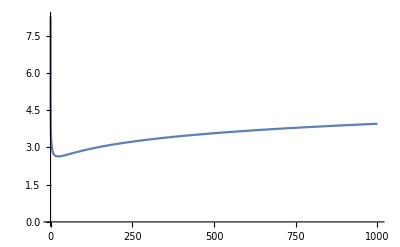

```mathematica
ListPlot[CoPCircleN100A1d0List,Joined->True]
```

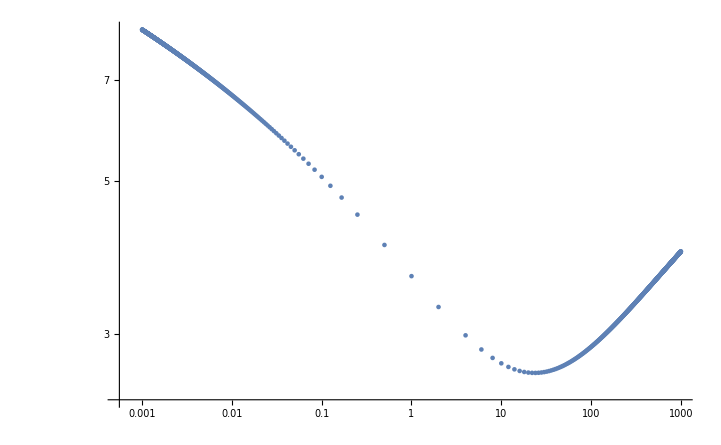

```mathematica
ListLogLogPlot[CoPCircleN100A1d0List,Joined->False]
```

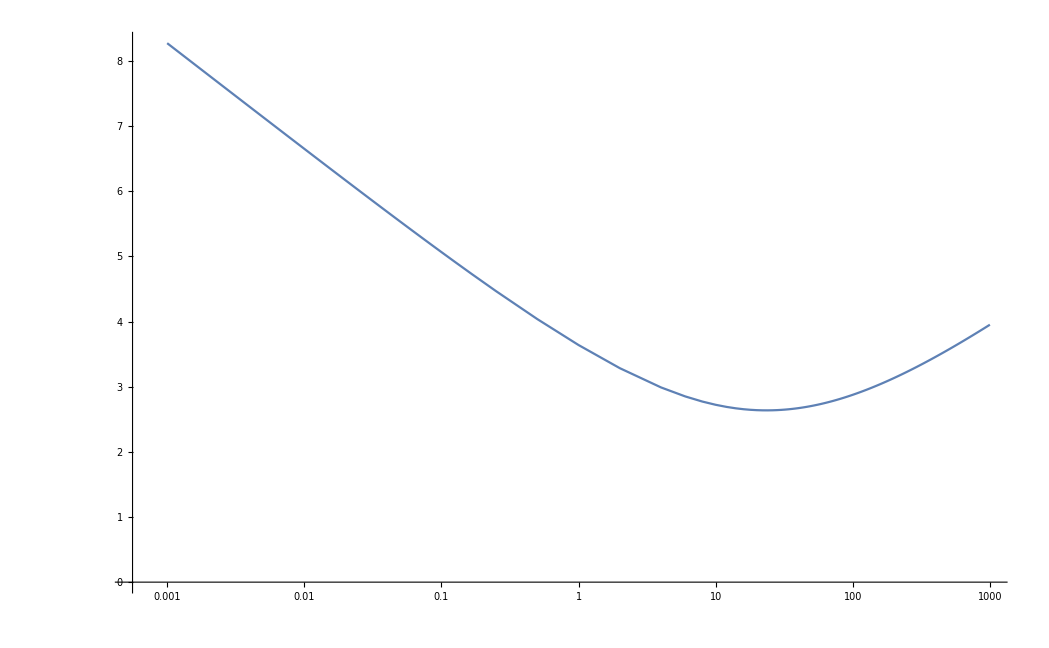

```mathematica
ListLogLinearPlot[CoPCircleN100A1d0List,Joined->True]
```

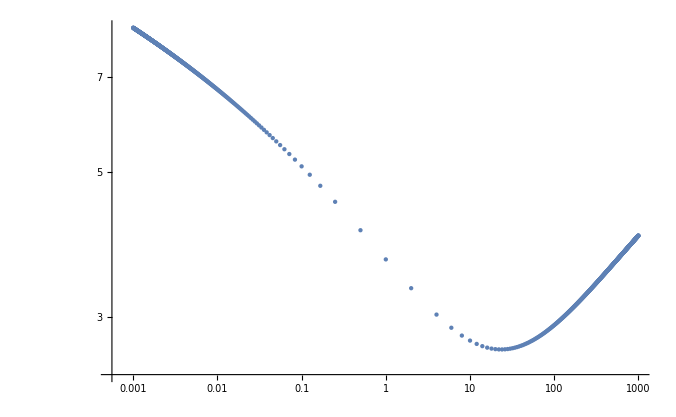

```mathematica
ListLogLogPlot[CoPCircleN100A1d1List,Joined->False]
```

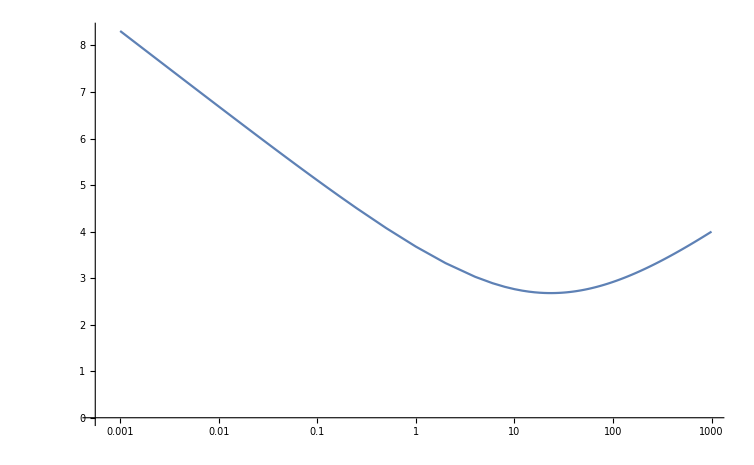

```mathematica
ListLogLinearPlot[CoPCircleN100A1d1List,Joined->True]
```

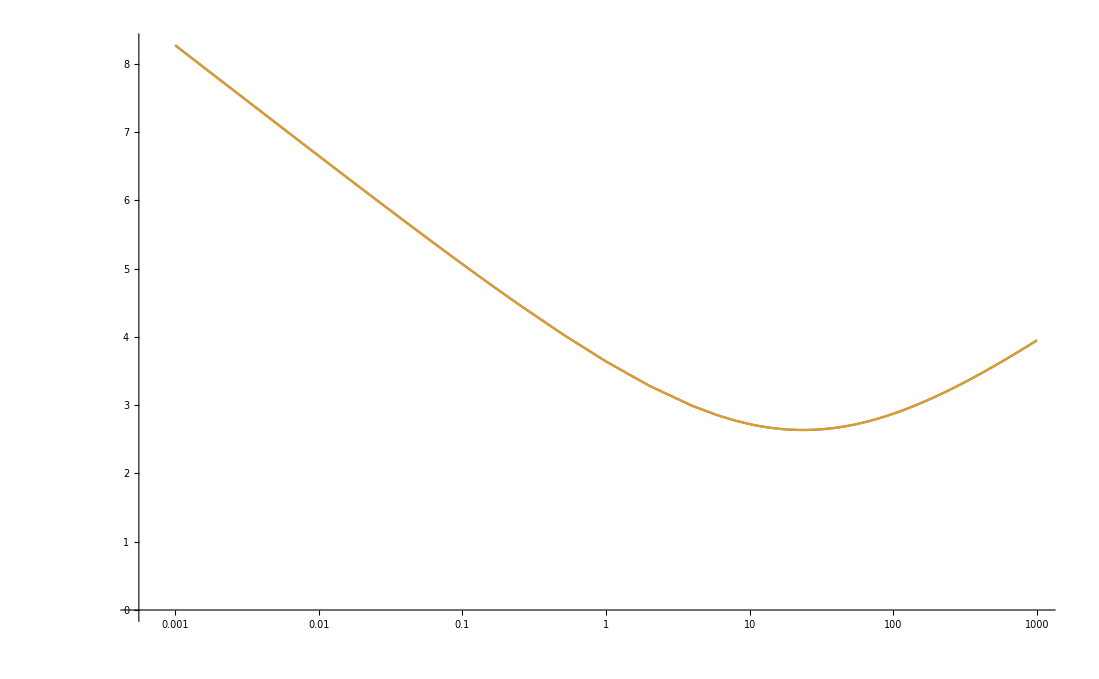

```mathematica
ListLogLinearPlot[{CoPCircleN100A1d0List,CoPCircleN100A1d98List},Joined->True]
```

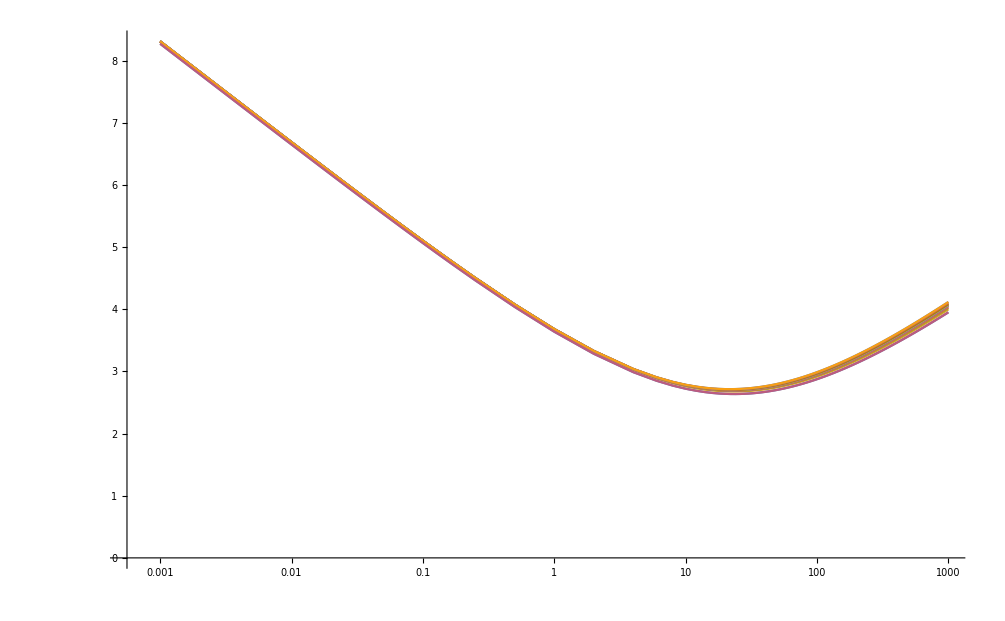

```mathematica
ListLogLinearPlot[{CoPCircleN100A1d0List,CoPCircleN100A1d1List,CoPCircleN100A1d2List,CoPCircleN100A1d3List,CoPCircleN100A1d5List,CoPCircleN100A1d7List,CoPCircleN100A1d8List,CoPCircleN100A1d9List,CoPCircleN100A1d10List,CoPCircleN100A1d12List,CoPCircleN100A1d20List,CoPCircleN100A1d48List,CoPCircleN100A1d50List,CoPCircleN100A1d98List},Joined->True]
```

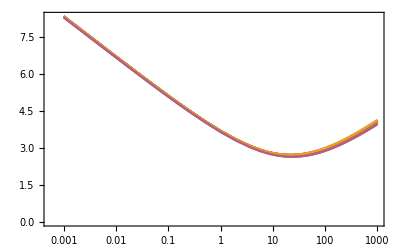

```mathematica
ListLogLinearPlot[{CoPCircleN100A1d0List,CoPCircleN100A1d1List,CoPCircleN100A1d2List,CoPCircleN100A1d3List,CoPCircleN100A1d5List,CoPCircleN100A1d7List,CoPCircleN100A1d8List,CoPCircleN100A1d9List,CoPCircleN100A1d10List,CoPCircleN100A1d12List,CoPCircleN100A1d20List,CoPCircleN100A1d48List,CoPCircleN100A1d50List,CoPCircleN100A1d98List},PlotTheme->"Detailed",Joined->True]
```

```mathematica
N[Min[CoPCircleN100A1d0List⟦All,2⟧]-Min[CoPCircleN100A1d98List⟦All,2⟧],50]
```

2.26077×10^-11

```mathematica
{Min[CoPCircleN100A1d0List⟦All,2⟧],Min[CoPCircleN100A1d1List⟦All,2⟧],Min[CoPCircleN100A1d2List⟦All,2⟧],Min[CoPCircleN100A1d3List⟦All,2⟧],Min[CoPCircleN100A1d5List⟦All,2⟧],Min[CoPCircleN100A1d7List⟦All,2⟧],Min[CoPCircleN100A1d8List⟦All,2⟧],Min[CoPCircleN100A1d9List⟦All,2⟧],Min[CoPCircleN100A1d10List⟦All,2⟧],Min[CoPCircleN100A1d12List⟦All,2⟧],Min[CoPCircleN100A1d20List⟦All,2⟧],Min[CoPCircleN100A1d48List⟦All,2⟧],Min[CoPCircleN100A1d50List⟦All,2⟧],Min[CoPCircleN100A1d98List⟦All,2⟧]}
```

{2.63719,2.67861,2.68664,2.69102,2.69635,2.69983,2.7012,2.7024,2.70347,2.70529,2.71011,2.71535,2.71535,2.63719}

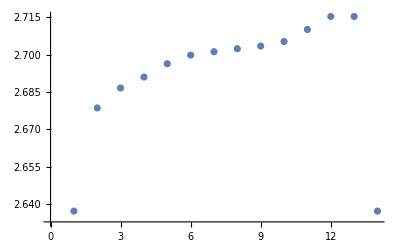

```mathematica
ListPlot[%198]
```

```mathematica
MinCopμList={{0,24,2.6371924030314347},{1,24,2.678610429651156},{2,24,2.6866375265364915},{3,22,2.6910211726659026},{5,22,2.6963529067350716},{7,22,2.699831147624585},{8,22,2.7012003588114473},{9,22,2.7024002757522063},{10,22,2.7034656882553842},{12,22,2.705285931748634},{20,22,2.7101113103442653},{48,22,2.71534763663217},{50,22,2.715347636632282},{98,24,2.637192403008827}};
```

```mathematica
Show[ListPointPlot3D[MinCopμList,PlotTheme->"Detailed"],Axes->True,Ticks-> Automatic,PlotRange-> Full]
```

-Graphics3D-

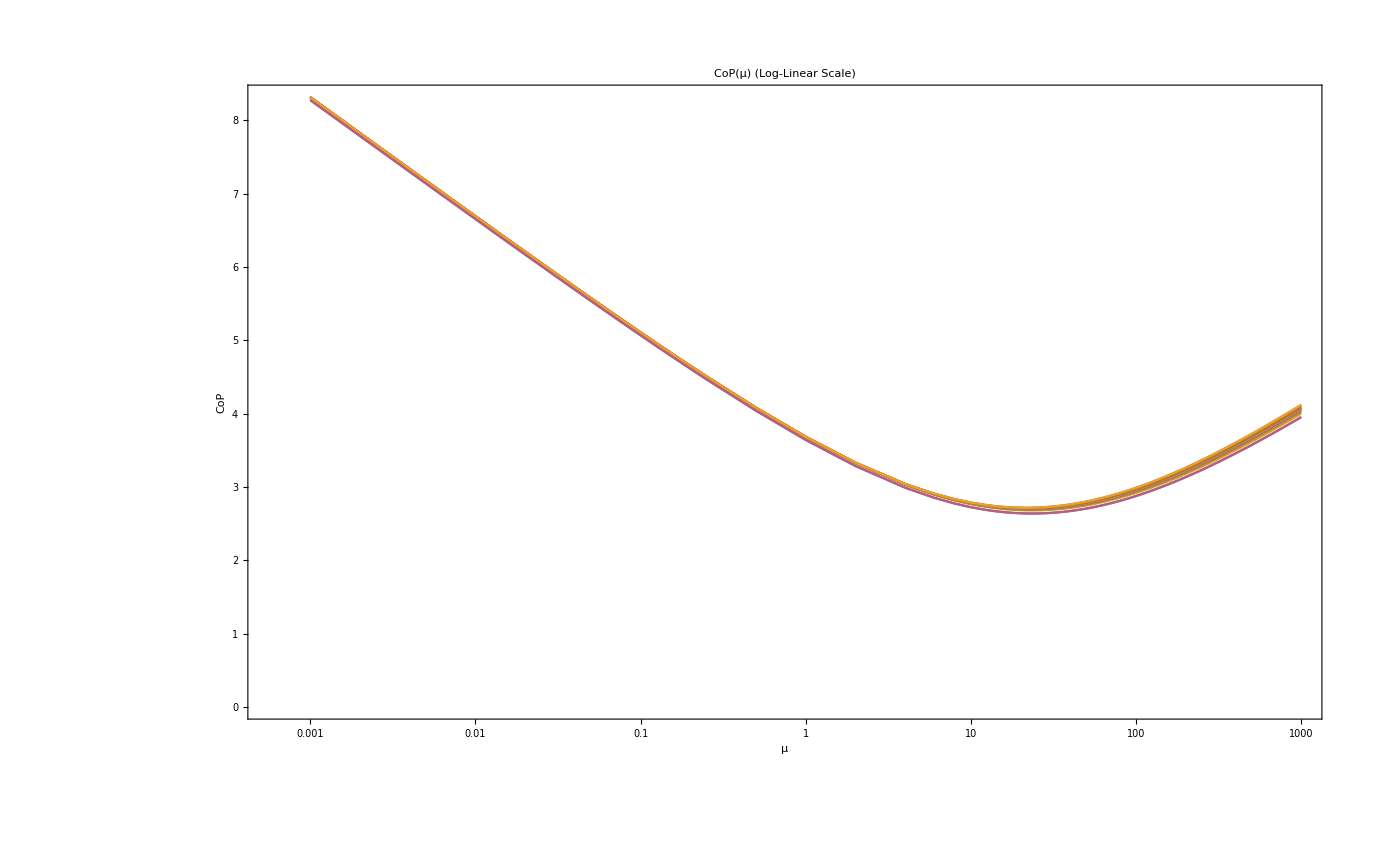

```mathematica
Show[ListLogLinearPlot[{CoPCircleN100A1d0List,CoPCircleN100A1d1List,CoPCircleN100A1d2List,CoPCircleN100A1d3List,CoPCircleN100A1d5List,CoPCircleN100A1d7List,CoPCircleN100A1d8List,CoPCircleN100A1d9List,CoPCircleN100A1d10List,CoPCircleN100A1d12List,CoPCircleN100A1d20List,CoPCircleN100A1d48List,CoPCircleN100A1d50List,CoPCircleN100A1d98List},PlotTheme->"Detailed",Joined->True],FrameLabel->{{HoldForm[CoP],None},{HoldForm[μ],None}},PlotLabel->HoldForm[ CoP[μ] (Log-Linear Scale)],LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Axes->True]
```

### Close to the Minimum

```mathematica
Listμ2=Reverse[Table[μ,{μ,20,27,1/20}]];
```

#### Data

```mathematica
(*CoPCircleN100A1d0List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,0]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d0List2={{27,2.639511594997972},{539/20,2.639449465211982},{269/10,2.6393880408160024},{537/20,2.6393273259039267},{134/5,2.639267324808803},{107/4,2.6392080418592756},{267/10,2.6391494811030927},{533/20,2.639091647164002},{133/5,2.6390345440500935},{531/20,2.6389781933010497},{53/2,2.6389225492883224},{529/20,2.6388676663343764},{132/5,2.638813531844211},{527/20,2.6387601509934533},{263/10,2.638707528229678},{105/4,2.6386556678851845},{131/5,2.6386045749010747},{523/20,2.638554253617626},{261/10,2.638504730208456},{521/20,2.638455945499429},{26,2.63840796808737},{519/20,2.638360781563094},{259/10,2.6383143905929844},{517/20,2.6382687998838192},{129/5,2.638224014734801},{103/4,2.638180039881404},{257/10,2.6381368803760736},{513/20,2.6380945409020207},{128/5,2.6380530267730844},{511/20,2.6380123432059186},{51/2,2.6379725326528063},{509/20,2.6379334871927096},{127/5,2.6378953250746404},{507/20,2.6378580140704435},{253/10,2.6378215591615555},{101/4,2.6377859659187575},{126/5,2.6377512394234914},{503/20,2.637717385276427},{251/10,2.6376844086096725},{501/20,2.6376523149662723},{25,2.6376211098232534},{499/20,2.6375908036148075},{249/10,2.6375613873330916},{497/20,2.6375328811387515},{124/5,2.6375052857640995},{99/4,2.6374786077330725},{247/10,2.637452850225531},{493/20,2.6374280216665924},{123/5,2.637404126869786},{491/20,2.6373811717792557},{49/2,2.6373591624055277},{489/20,2.637338104322173},{122/5,2.637318003774666},{487/20,2.637298866965033},{243/10,2.6372806996409937},{97/4,2.637263507909771},{121/5,2.6372472981681603},{483/20,2.637232077647261},{241/10,2.637217849310407},{481/20,2.6372046227669923},{24,2.637192403108719},{479/20,2.6371811969055483},{239/10,2.637171010259459},{477/20,2.6371618501552465},{119/5,2.6371537239800897},{95/4,2.637146635408042},{237/10,2.6371405935389474},{473/20,2.6371356049463808},{118/5,2.637131675435834},{471/20,2.637128812590691},{47/2,2.6371270225487575},{469/20,2.6371263127899076},{117/5,2.6371266902125323},{467/20,2.637128161553881},{233/10,2.6371307339896974},{93/4,2.6371344144711752},{116/5,2.6371392105431317},{463/20,2.6371451292635233},{231/10,2.6371521775687192},{461/20,2.637160363298295},{23,2.637169693593055},{459/20,2.6371801758148012},{229/10,2.6371918177162774},{457/20,2.6372046266514237},{114/5,2.637218610369457},{91/4,2.6372337765852722},{227/10,2.6372501329359475},{453/20,2.6372676873374377},{113/5,2.637286447281349},{451/20,2.637306421211182},{45/2,2.6373276170336553},{449/20,2.6373500425921517},{112/5,2.637373706021713},{447/20,2.6373986154993534},{223/10,2.637424779786066},{89/4,2.6374522061109262},{111/5,2.637480903853934},{443/20,2.6375108977683137},{221/10,2.6375421461943493},{441/20,2.6375747080737337},{22,2.637608575359316},{439/20,2.63764375636358},{219/10,2.6376802603157743},{437/20,2.6377180959828284},{109/5,2.6377572721176983},{87/4,2.6377977980996246},{217/10,2.6378396825327006},{433/20,2.637882934614342},{108/5,2.637927564172638},{431/20,2.6379735798962143},{43/2,2.63802099139319},{429/20,2.638069808227365},{107/5,2.638120041879283},{427/20,2.6381716955314936},{213/10,2.6382247855445797},{85/4,2.638279319491264},{106/5,2.63833530718045},{423/20,2.6383927584342493},{211/10,2.638451683379702},{421/20,2.6385120920944125},{21,2.6385739947403373},{419/20,2.6386374017841954},{209/10,2.638702323421714},{417/20,2.638768770160485},{104/5,2.638836752593541},{83/4,2.638906281417269},{207/10,2.6389773668236276},{413/20,2.639050020594603},{103/5,2.6391242524422602},{411/20,2.639200074136831},{41/2,2.639277496849247},{409/20,2.6393565367395166},{102/5,2.639437189241594},{407/20,2.639519481633489},{203/10,2.63960342020392},{81/4,2.6396890164597626},{101/5,2.639776282140761},{403/20,2.6398652290731057},{201/10,2.6399558687798415},{401/20,2.6400482134212373},{20,2.6401422752051267}};
```

```mathematica
(*CoPCircleN100A1d1List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,1]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d1List2={{27,2.6809808112474736},{539/20,2.6809179472798976},{269/10,2.6808557851291828},{537/20,2.680794328886804},{134/5,2.6807335827891157},{107/4,2.6806735511155697},{267/10,2.680614238200077},{533/20,2.6805556483467474},{133/5,2.6804977858661294},{531/20,2.680440655180699},{53/2,2.6803842606874997},{529/20,2.680328606837032},{132/5,2.6802736981030857},{527/20,2.6802195389415138},{263/10,2.6801661339511855},{105/4,2.680113488441919},{131/5,2.680061605634709},{523/20,2.6800104897031276},{261/10,2.6799601473393166},{521/20,2.6799105821680365},{26,2.679861799090828},{519/20,2.6798138028932392},{259/10,2.6797665981285896},{517/20,2.679720190499616},{129/5,2.6796745828561144},{103/4,2.679629782082697},{257/10,2.6795857933417215},{513/20,2.6795426187918028},{128/5,2.679500266223554},{511/20,2.67945873983665},{51/2,2.6794180446263383},{509/20,2.679378187489525},{127/5,2.679339168305198},{507/20,2.67930099753297},{253/10,2.6792636786436863},{101/4,2.679227216795363},{126/5,2.679191617409337},{503/20,2.6791568857838564},{251/10,2.679123027288164},{501/20,2.67909004736329},{25,2.679057951379669},{499/20,2.679026744901577},{249/10,2.678996433466603},{497/20,2.678967022583628},{124/5,2.6789385179100456},{99/4,2.6789109250981147},{247/10,2.678884251184664},{493/20,2.6788584978583665},{123/5,2.678833674947634},{491/20,2.678809786919678},{49/2,2.6787868396472008},{489/20,2.6787648390226577},{122/5,2.6787437922227495},{487/20,2.678723701601485},{243/10,2.678704576834511},{97/4,2.678686422804344},{121/5,2.678669245657884},{483/20,2.678653051461683},{241/10,2.6786378465649046},{481/20,2.67862363721294},{24,2.678610429713814},{479/20,2.678598230321146},{239/10,2.678587045580667},{477/20,2.678576881919472},{119/5,2.678567747630599},{95/4,2.6785596438765613},{237/10,2.678552582658154},{473/20,2.6785465688357095},{118/5,2.678541609144753},{471/20,2.6785377102627455},{47/2,2.678534879067866},{469/20,2.6785331223983473},{117/5,2.6785324471653538},{467/20,2.678532860366947},{233/10,2.6785343689738306},{93/4,2.6785369801096346},{116/5,2.6785407008582047},{463/20,2.6785455384853996},{231/10,2.6785515000700166},{461/20,2.6785585931043148},{23,2.678566824755676},{459/20,2.6785762025652207},{229/10,2.6785867370155905},{457/20,2.678598426460905},{114/5,2.678611289613214},{91/4,2.6786253251994676},{227/10,2.6786405467551964},{453/20,2.678656960129477},{113/5,2.678674573134774},{451/20,2.6786933936568977},{45/2,2.6787134296447705},{449/20,2.678734689112285},{112/5,2.6787571801346295},{447/20,2.6787809108537486},{223/10,2.6788058894729927},{89/4,2.678832124289526},{111/5,2.6788596236055136},{443/20,2.6788883957756577},{221/10,2.6789184493713916},{441/20,2.678949792888105},{22,2.678982434964676},{439/20,2.679016384190336},{219/10,2.6790516494009937},{437/20,2.6790882393934696},{109/5,2.6791261630562153},{87/4,2.6791654293102423},{217/10,2.679206047245676},{433/20,2.6792480259547347},{108/5,2.6792913746160876},{431/20,2.6793361051098734},{43/2,2.679382218953637},{429/20,2.6794297333064048},{107/5,2.6794786551437704},{427/20,2.6795289940016387},{213/10,2.679580759531899},{85/4,2.6796339614413442},{106/5,2.6796886113773266},{423/20,2.67974471378504},{211/10,2.6798022840352154},{421/20,2.679861330425264},{21,2.679921863075446},{419/20,2.679983892208669},{209/10,2.680047428139113},{417/20,2.6801124812608075},{104/5,2.6801790620626176},{83/4,2.680247181118364},{207/10,2.680316849093129},{413/20,2.680388076740789},{103/5,2.6804608749091448},{411/20,2.680535255732155},{41/2,2.680611226655816},{409/20,2.6806888023948856},{102/5,2.6807679929877},{407/20,2.680848809719717},{203/10,2.680931264040607},{81/4,2.681015367457797},{101/5,2.6811011315822655},{403/20,2.6811885681349166},{201/10,2.6812776889337737},{401/20,2.681368505896745},{20,2.6814610314545098}};
```

```mathematica
(*CoPCircleN100A1d2List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,2]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d2List2={{27,2.6894064951747234},{539/20,2.689337276845937},{269/10,2.6892687514260736},{537/20,2.6892009226912195},{134/5,2.6891337993998294},{107/4,2.6890673719643785},{267/10,2.6890016585971686},{533/20,2.6889366587417185},{133/5,2.6888723769406044},{531/20,2.6888088175538933},{53/2,2.6887459848492123},{529/20,2.6886838831183435},{132/5,2.6886225170903177},{527/20,2.6885618911147326},{263/10,2.6885020097162076},{105/4,2.6884428774019153},{131/5,2.688384498773527},{523/20,2.6883268784496073},{261/10,2.688270020987479},{521/20,2.6882139311239275},{26,2.68815861354886},{519/20,2.688104073023044},{259/10,2.6880503142062575},{517/20,2.6879973420126193},{129/5,2.6879451612764194},{103/4,2.68789377679755},{257/10,2.687843193443805},{513/20,2.687793416274216},{128/5,2.687744450208366},{511/20,2.6876963003576106},{51/2,2.687648971460783},{509/20,2.6876024689038878},{127/5,2.6875567977046453},{507/20,2.6875119630154396},{253/10,2.6874679700314443},{101/4,2.6874248239752565},{126/5,2.6873825301191117},{503/20,2.6873410938381994},{251/10,2.687300520314016},{501/20,2.6872608149801276},{25,2.6872219834138344},{499/20,2.6871840308258395},{249/10,2.6871469629113287},{497/20,2.6871107851490925},{124/5,2.6870755031145483},{99/4,2.6870411224810926},{247/10,2.687007648764847},{493/20,2.6869750878143357},{123/5,2.6869434453312118},{491/20,2.6869127271026754},{49/2,2.6868829389589504},{489/20,2.6868540867816466},{122/5,2.6868261764723957},{487/20,2.6867992140391155},{243/10,2.6867732054840063},{97/4,2.686748156675694},{121/5,2.6867240739718277},{483/20,2.6867009638608943},{241/10,2.6866788311049214},{481/20,2.68665768343967},{24,2.68663752658655},{479/20,2.686618366839675},{239/10,2.6866002106887037},{477/20,2.6865830645566584},{119/5,2.6865669359074977},{95/4,2.6865518280232834},{237/10,2.686537750764535},{473/20,2.686524709628591},{118/5,2.6865127113524037},{471/20,2.686501762627712},{47/2,2.686491870225612},{469/20,2.6864830409698426},{117/5,2.686475281740377},{467/20,2.686468599463309},{233/10,2.6864630011277146},{93/4,2.686458493769333},{116/5,2.6864550857205294},{463/20,2.6864527804088194},{231/10,2.6864515887838625},{461/20,2.686451516779531},{23,2.686452571796125},{459/20,2.68645476117777},{229/10,2.686458092350772},{457/20,2.6864625728060196},{114/5,2.6864682100884822},{91/4,2.6864750118032172},{227/10,2.686482985615862},{453/20,2.6864921392505123},{113/5,2.686502480494668},{451/20,2.686514017200762},{45/2,2.6865267572694367},{449/20,2.686540708677533},{112/5,2.686555879465165},{447/20,2.686572277730372},{223/10,2.6865899116417222},{89/4,2.6866087937085674},{111/5,2.686628919369176},{443/20,2.686650309852912},{221/10,2.68667296929251},{441/20,2.6866969061953663},{22,2.6867221291278898},{439/20,2.6867486467374797},{219/10,2.6867764676746857},{437/20,2.6868056007783436},{109/5,2.686836054875338},{87/4,2.686867838922803},{217/10,2.686900961796929},{433/20,2.68693543267955},{108/5,2.6869712606756604},{431/20,2.687008454999321},{43/2,2.6870470249443916},{429/20,2.6870869798742274},{107/5,2.6871283292363866},{427/20,2.6871710825731006},{213/10,2.687215249435191},{85/4,2.687260839553983},{106/5,2.6873078626787814},{423/20,2.687356328692969},{211/10,2.687406247400809},{421/20,2.6874576289366248},{21,2.6875104833543424},{419/20,2.687564820864083},{209/10,2.6876206516565952},{417/20,2.6876779861015914},{104/5,2.6877368346906936},{83/4,2.6877972079352705},{207/10,2.6878591164559693},{413/20,2.6879225708633707},{103/5,2.6879875821077},{411/20,2.6880541609572806},{41/2,2.6881223185102754},{409/20,2.6881920657052034},{102/5,2.6882634138517534},{407/20,2.6883363741498765},{203/10,2.6884109579356443},{81/4,2.688487176749136},{101/5,2.6885650421238125},{403/20,2.688644565728126},{201/10,2.6887257593241194},{401/20,2.6888086347870117},{20,2.688893204091454}};
```

```mathematica
(*CoPCircleN100A1d3List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,3]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d3List2={{27,2.694182547410627},{539/20,2.694108897309873},{269/10,2.6940359334681787},{537/20,2.6939636600597203},{134/5,2.693892081229458},{107/4,2.693821201246111},{267/10,2.693751024340176},{533/20,2.693681554788289},{133/5,2.693612796900976},{531/20,2.6935447550098712},{53/2,2.693477433486329},{529/20,2.693410836727791},{132/5,2.6933449691619846},{527/20,2.6932798381543686},{263/10,2.693215439473573},{105/4,2.6931517863629706},{131/5,2.693088880470798},{523/20,2.6930267263762384},{261/10,2.692965328703412},{521/20,2.692904692102205},{26,2.6928448212435367},{519/20,2.6927857208567123},{259/10,2.692727395686276},{517/20,2.6926698505181075},{129/5,2.6926130901588183},{103/4,2.692557119468366},{257/10,2.692501943330982},{513/20,2.6924475667171706},{128/5,2.6923939944382376},{511/20,2.692341231600226},{51/2,2.6922892844695956},{509/20,2.692238154412083},{127/5,2.6921878500806864},{507/20,2.692138375556969},{253/10,2.6920897359385583},{101/4,2.6920419365075086},{126/5,2.691994982321959},{503/20,2.6919488788542574},{251/10,2.691903631365857},{501/20,2.6918592452879477},{25,2.691815726394919},{499/20,2.6917730785899736},{249/10,2.691731309033617},{497/20,2.691690422696292},{124/5,2.6916504250239353},{99/4,2.6916113217416187},{247/10,2.691573118463075},{493/20,2.6915358208241345},{123/5,2.6914994346024526},{491/20,2.6914639655509753},{49/2,2.691429419475197},{489/20,2.6913958039483203},{122/5,2.691363119724029},{487/20,2.6913313778863692},{243/10,2.6913005827076635},{97/4,2.691270740215485},{121/5,2.691241856486727},{483/20,2.6912139376447795},{241/10,2.6911869898499905},{481/20,2.691161019322337},{24,2.6911360323153155},{479/20,2.691112037585292},{239/10,2.6910890341507634},{477/20,2.6910670357458346},{119/5,2.6910460463791455},{95/4,2.691026072550062},{237/10,2.691007120808651},{473/20,2.690989197751826},{118/5,2.690972310029833},{471/20,2.690956464344198},{47/2,2.6909416674695135},{469/20,2.6909279261668204},{117/5,2.6909152472689737},{467/20,2.6909036377917563},{233/10,2.690893104559026},{93/4,2.6908836546923434},{116/5,2.6908752952211},{463/20,2.6908680332736745},{231/10,2.6908618760279497},{461/20,2.69085683072294},{23,2.690852904639603},{459/20,2.6908501051368368},{229/10,2.690848439616289},{457/20,2.6908479155417333},{114/5,2.690848540436185},{91/4,2.6908503240883643},{227/10,2.6908532675413896},{453/20,2.6908573850439717},{113/5,2.6908626822267223},{451/20,2.690869166888602},{45/2,2.6908768469576883},{449/20,2.690885730254115},{112/5,2.690895824948462},{447/20,2.6909071389774106},{223/10,2.6909196805782924},{89/4,2.690933461910555},{111/5,2.690948479289424},{443/20,2.6909647530062855},{221/10,2.690982287481876},{441/20,2.691001091252784},{22,2.6910211726671323},{439/20,2.6910425405266927},{219/10,2.691065203445382},{437/20,2.69108917019384},{109/5,2.6911144495456294},{87/4,2.6911410504724507},{217/10,2.6911689818262463},{433/20,2.691198252784308},{108/5,2.691228872317982},{431/20,2.691260849723503},{43/2,2.6912941942593305},{429/20,2.6913289151757893},{107/5,2.691365021983752},{427/20,2.6914025241530317},{213/10,2.6914414312475965},{85/4,2.691481752933109},{106/5,2.6915234989390324},{423/20,2.691566679087947},{211/10,2.6916113032692954},{421/20,2.691657381490417},{21,2.691704923782581},{419/20,2.6917539402921755},{209/10,2.6918044412880486},{417/20,2.6918564370915927},{104/5,2.6919099380808924},{83/4,2.6919649547830056},{207/10,2.692021497839818},{413/20,2.692079577742169},{103/5,2.692139205444443},{411/20,2.6922003917477313},{41/2,2.6922631476082164},{409/20,2.6923274840947844},{102/5,2.6923934122779314},{407/20,2.692460943475929},{203/10,2.692530088999267},{81/4,2.692600860281035},{101/5,2.6926732688589783},{403/20,2.6927473263673387},{201/10,2.6928230445456207},{401/20,2.6929004352256127},{20,2.692979510357848}};
```

```mathematica
(*CoPCircleN100A1d5List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,5]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d5List2={{27,2.7001543041157428},{539/20,2.7000747035495882},{269/10,2.6999957809207924},{537/20,2.699917540419621},{134/5,2.699839986190862},{107/4,2.6997631224334095},{267/10,2.6996869534734156},{533/20,2.6996114832653433},{133/5,2.699536716394708},{531/20,2.6994626570841596},{53/2,2.699389309648697},{529/20,2.699316678496505},{132/5,2.699244768020167},{527/20,2.6991735826562326},{263/10,2.6991031268738657},{105/4,2.699033405253518},{131/5,2.6989644220818416},{523/20,2.698896182145251},{261/10,2.6988286899836402},{521/20,2.6987619502135316},{26,2.698695967493608},{519/20,2.698630746516645},{259/10,2.6985662920066256},{517/20,2.698502608733687},{129/5,2.6984397014612687},{103/4,2.6983775750857055},{257/10,2.6983162343343294},{513/20,2.6982556842316567},{128/5,2.6981959296578903},{511/20,2.6981369755847653},{51/2,2.69807882701631},{509/20,2.698021488988298},{127/5,2.6979649665744097},{507/20,2.6979092648897773},{253/10,2.697854389068743},{101/4,2.697800344309794},{126/5,2.6977471358299576},{503/20,2.69769477178333},{251/10,2.697643248831106},{501/20,2.697592580862689},{25,2.6975427704877712},{499/20,2.697493823077306},{249/10,2.697445744088915},{497/20,2.697398539069244},{124/5,2.697352213391533},{99/4,2.697306772795144},{247/10,2.6972622228397327},{493/20,2.697218569245084},{123/5,2.697175817532387},{491/20,2.6971339736200526},{49/2,2.697093043237909},{489/20,2.697053032204583},{122/5,2.697013946398853},{487/20,2.696975791735535},{243/10,2.6969385741652747},{97/4,2.6969022997233583},{121/5,2.696866974391738},{483/20,2.6968326043074264},{241/10,2.696799195616694},{481/20,2.6967667545018896},{24,2.696735288583582},{479/20,2.696704799914386},{239/10,2.69667529906894},{477/20,2.6966467910046377},{119/5,2.696619282137604},{95/4,2.6965927789460262},{237/10,2.6965672879460354},{473/20,2.696542815711755},{118/5,2.6965193688591884},{471/20,2.6964969540828845},{47/2,2.696475578045508},{469/20,2.6964552475825574},{117/5,2.6964359695009903},{467/20,2.696417750660984},{233/10,2.6964005980198915},{93/4,2.6963845185531863},{116/5,2.696369519297067},{463/20,2.6963556073513186},{231/10,2.696342789862986},{461/20,2.6963310740486652},{23,2.696320467173944},{459/20,2.696310976536478},{229/10,2.6963026094165823},{457/20,2.6962953734194386},{114/5,2.6962892759615946},{91/4,2.696284324608867},{227/10,2.6962805269328487},{453/20,2.6962778906525573},{113/5,2.696276423451046},{451/20,2.696276133156811},{45/2,2.6962770276146677},{449/20,2.696279114791162},{112/5,2.6962824024937073},{447/20,2.6962868989485544},{223/10,2.6962926121950086},{89/4,2.69629955041573},{111/5,2.696307721841351},{443/20,2.6963171347801578},{221/10,2.696327797603791},{441/20,2.6963397187513705},{22,2.6963529067319922},{439/20,2.69636737011951},{219/10,2.696383117562637},{437/20,2.696400157777374},{109/5,2.6964184995529266},{87/4,2.696438151841783},{217/10,2.696459123386713},{433/20,2.696481423198013},{108/5,2.6965050605395575},{431/20,2.696530044488957},{43/2,2.6965563842288103},{429/20,2.696584089111657},{107/5,2.696613168502445},{427/20,2.696643631868637},{213/10,2.6966754887476236},{85/4,2.6967087487616173},{106/5,2.6967434215982284},{423/20,2.6967795170521334},{211/10,2.696817044983022},{421/20,2.6968560153331413},{21,2.6968964381829608},{419/20,2.696938323498184},{209/10,2.696981681627751},{417/20,2.6970265228081636},{104/5,2.697072857408148},{83/4,2.6971206958938017},{207/10,2.6971700488155235},{413/20,2.697220926818309},{103/5,2.697273340613426},{411/20,2.69732730104622},{41/2,2.697382819050132},{409/20,2.6974399055625424},{102/5,2.6974985717613826},{407/20,2.6975588289294556},{203/10,2.697620688053517},{81/4,2.6976841608352626},{101/5,2.697749258673548},{403/20,2.6978159931624104},{201/10,2.6978843759993434},{401/20,2.697954418983014},{20,2.6980261340197162}};
```

```mathematica
(*CoPCircleN100A1d7List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,7]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d7List2={{27,2.7040621554744795},{539/20,2.7039785626708372},{269/10,2.703895642226764},{537/20,2.703813398269554},{134/5,2.7037318349609945},{107/4,2.7036509564661233},{267/10,2.7035707669917657},{533/20,2.7034912708370635},{133/5,2.7034124721511734},{531/20,2.703334375346252},{53/2,2.703256984711996},{529/20,2.703180304606293},{132/5,2.7031043394246237},{527/20,2.7030290935836354},{263/10,2.7029545715368246},{105/4,2.7028807777894834},{131/5,2.7028077168065363},{523/20,2.7027353931510407},{261/10,2.702663811424129},{521/20,2.70259297622614},{26,2.702522892231215},{519/20,2.702453564019557},{259/10,2.702384996397994},{517/20,2.702317194071942},{129/5,2.7022501618225654},{103/4,2.70218390445601},{257/10,2.7021184268220706},{513/20,2.7020537338012875},{128/5,2.7019898303051737},{511/20,2.7019267212874998},{51/2,2.701864411739595},{509/20,2.7018029066498617},{127/5,2.701742211107118},{507/20,2.7016823302016157},{253/10,2.7016232690603363},{101/4,2.7015650328537832},{126/5,2.7015076267812934},{503/20,2.701451056102769},{251/10,2.701395326063964},{501/20,2.7013404420185188},{25,2.7012864093744793},{499/20,2.7012332333495936},{249/10,2.7011809195898144},{497/20,2.7011294734227422},{124/5,2.70107890045745},{99/4,2.701029206218231},{247/10,2.7009803963118015},{493/20,2.7009324763705242},{123/5,2.700885452082496},{491/20,2.700839329165823},{49/2,2.700794113391669},{489/20,2.700749810567751},{122/5,2.700706426550682},{487/20,2.7006639672295787},{243/10,2.70062243854965},{97/4,2.700581846495092},{121/5,2.7005421970983625},{483/20,2.7005034964275794},{241/10,2.70046575060914},{481/20,2.700428965807171},{24,2.700393148236079},{479/20,2.7003583041591286},{239/10,2.7003244398743096},{477/20,2.700291561745391},{119/5,2.7002596761722915},{95/4,2.7002287896118107},{237/10,2.700198908560614},{473/20,2.700170039572898},{118/5,2.7001421892588304},{471/20,2.7001153642387394},{47/2,2.7000895713447055},{469/20,2.700064817031058},{117/5,2.700041108394846},{467/20,2.7000184521961845},{233/10,2.6999968553468854},{93/4,2.699976324814826},{116/5,2.699956867621467},{463/20,2.699938490831967},{231/10,2.699921201730166},{461/20,2.6999050070620445},{23,2.699889914501787},{459/20,2.699875931206516},{229/10,2.6998630645262907},{457/20,2.6998513218736724},{114/5,2.6998407107251556},{91/4,2.699831238604913},{227/10,2.69982291310163},{453/20,2.699815741870001},{113/5,2.6998097326148796},{451/20,2.6998048931095617},{45/2,2.6998012311857744},{449/20,2.69979875474045},{112/5,2.6997974717269564},{447/20,2.699797390174114},{223/10,2.6997985181645006},{89/4,2.699800863887147},{111/5,2.6998044354497894},{443/20,2.6998092412400894},{221/10,2.69981528958872},{441/20,2.6998225888769705},{22,2.699831147624053},{439/20,2.6998409743707237},{219/10,2.699852077745262},{437/20,2.6998644664421905},{109/5,2.699878149251351},{87/4,2.699893134927349},{217/10,2.6999094324604562},{433/20,2.699927050873726},{108/5,2.6999459991022965},{431/20,2.699966286260878},{43/2,2.6999879216963305},{429/20,2.700010914624152},{107/5,2.7000352744036342},{427/20,2.700061010478185},{213/10,2.700088132353109},{85/4,2.7001166496747966},{106/5,2.7001465719903943},{423/20,2.7001779091814617},{211/10,2.700210671084778},{421/20,2.7002448675088027},{21,2.700280508570327},{419/20,2.7003176043222354},{209/10,2.7003561649385297},{417/20,2.700396200681011},{104/5,2.700437721949606},{83/4,2.700480739065554},{207/10,2.700525262589887},{413/20,2.7005713032072194},{103/5,2.70061887158003},{411/20,2.700667978508054},{41/2,2.7007186349392036},{409/20,2.700770851694237},{102/5,2.700824640010253},{407/20,2.700880011017842},{203/10,2.700936976001259},{81/4,2.7009955462806965},{101/5,2.7010557333928524},{403/20,2.701117548842086},{201/10,2.7011810043402993},{401/20,2.7012461116791053},{20,2.701312882729115}};
```

```mathematica
(*CoPCircleN100A1d8List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,8]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d8List2={{27,2.7056012132817857},{539/20,2.7055160437990735},{269/10,2.7054315429863425},{537/20,2.7053477171298193},{134/5,2.705264569682484},{107/4,2.7051821048070077},{267/10,2.705100326710453},{533/20,2.7050192396715382},{133/5,2.704938847805672},{531/20,2.704859155578398},{53/2,2.704780167275729},{529/20,2.7047018871153776},{132/5,2.7046243196177144},{527/20,2.7045474691845452},{263/10,2.704471340240033},{105/4,2.7043959372563737},{131/5,2.704321264746725},{523/20,2.7042473272543885},{261/10,2.7041741293491106},{521/20,2.704101675636286},{26,2.704029970750088},{519/20,2.703959019361931},{259/10,2.703888826174253},{517/20,2.7038193959261254},{129/5,2.7037507333861432},{103/4,2.703682843363696},{257/10,2.7036157306769915},{513/20,2.703549400221519},{128/5,2.7034838569018715},{511/20,2.7034191056829786},{51/2,2.7033551514574987},{509/20,2.70329199933544},{127/5,2.70322965432982},{507/20,2.7031681215472543},{253/10,2.703107406062443},{101/4,2.7030475131004144},{126/5,2.7029884478056188},{503/20,2.7029302154498063},{251/10,2.7028728212968973},{501/20,2.7028162707168772},{25,2.70276056891323},{499/20,2.702705721378799},{249/10,2.7026517335418676},{497/20,2.702598610875283},{124/5,2.702546358883279},{99/4,2.7024949831046485},{247/10,2.7024444891323105},{493/20,2.7023948826147715},{123/5,2.7023461692515793},{491/20,2.7022983546627697},{49/2,2.702251445361905},{489/20,2.7022054451962116},{122/5,2.7021603618019303},{487/20,2.702116200617752},{243/10,2.7020729675109525},{97/4,2.702030668476684},{121/5,2.7019893094206435},{483/20,2.70194889655269},{241/10,2.701909435930977},{481/20,2.7018709337150164},{24,2.701833396114865},{479/20,2.701796829637941},{239/10,2.7017612398099997},{477/20,2.701726633754876},{119/5,2.7016930176260128},{95/4,2.701660397868743},{237/10,2.701628780880491},{473/20,2.701598173359211},{118/5,2.7015685817736776},{471/20,2.7015400128390823},{47/2,2.7015124732295495},{469/20,2.7014859696934796},{117/5,2.7014605090287303},{467/20,2.701436098086403},{233/10,2.7014127437901734},{93/4,2.7013904530367334},{116/5,2.7013692328973615},{463/20,2.701349090436093},{231/10,2.7013300327251986},{461/20,2.7013120669892765},{23,2.7012952005272077},{459/20,2.7012794404015152},{229/10,2.701264794148788},{457/20,2.7012512692240906},{114/5,2.701238872839219},{91/4,2.7012276127441384},{227/10,2.7012174964501066},{453/20,2.7012085315901375},{113/5,2.701200725870561},{451/20,2.7011940870577473},{45/2,2.701188622964023},{449/20,2.7011843414853214},{112/5,2.701181250642989},{447/20,2.7011793582312675},{223/10,2.701178672549934},{89/4,2.701179201687797},{111/5,2.7011809537700637},{443/20,2.701183937184616},{221/10,2.7011881601775745},{441/20,2.7011936312306344},{22,2.7012003587616893},{439/20,2.701208351354305},{219/10,2.7012176176150335},{437/20,2.701228166227966},{109/5,2.701240005946347},{87/4,2.7012531455990065},{217/10,2.7012675940892383},{433/20,2.7012833603867885},{108/5,2.7013004535424043},{431/20,2.701318882685526},{43/2,2.7013386616589026},{429/20,2.7013597857460874},{107/5,2.701382278304306},{427/20,2.701406144094055},{213/10,2.7014313926125393},{85/4,2.7014580334929383},{106/5,2.7014860762905606},{423/20,2.7015155308582885},{211/10,2.701546407002474},{421/20,2.7015787146008043},{21,2.701612463692153},{419/20,2.701647664308187},{209/10,2.7016843266544335},{417/20,2.7017224609693353},{104/5,2.7017620775934867},{83/4,2.7018031869470054},{207/10,2.701845799549137},{413/20,2.7018899260230715},{103/5,2.7019355770155813},{411/20,2.7019827633541644},{41/2,2.7020314959183125},{409/20,2.702081785675002},{102/5,2.7021336437119867},{407/20,2.702187081136085},{203/10,2.7022421096238523},{81/4,2.702298739458219},{101/5,2.7023569831573284},{403/20,2.702416851915068},{201/10,2.702478357403334},{401/20,2.702541511385378},{20,2.702606325727153}};
```

```mathematica
(*CoPCircleN100A1d9List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,9]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d9List2={{27,2.7069499709965674},{539/20,2.706863419003205},{269/10,2.7067775350939396},{537/20,2.7066923235047877},{134/5,2.7066077883331694},{107/4,2.706523933757184},{267/10,2.7064407639741646},{533/20,2.706358283195552},{133/5,2.7062764957038703},{531/20,2.7061954057779483},{53/2,2.7061150177728828},{529/20,2.706035335932835},{132/5,2.705956364759717},{527/20,2.7058781117301627},{263/10,2.70580057183479},{105/4,2.705723759047194},{131/5,2.705647674689491},{523/20,2.705572323307438},{261/10,2.7054977094663983},{521/20,2.705423837771081},{26,2.7053507127975887},{519/20,2.705278339285878},{259/10,2.7052067218920866},{517/20,2.7051358653597246},{129/5,2.7050657760442474},{103/4,2.704996453967059},{257/10,2.704927908732738},{513/20,2.704860143624473},{128/5,2.7047931635384725},{511/20,2.7047269734647457},{51/2,2.7046615782436123},{509/20,2.7045969829832153},{127/5,2.7045331927253957},{507/20,2.704470212541645},{253/10,2.7044080475866323},{101/4,2.704346702918053},{126/5,2.704286183773313},{503/20,2.704226495439693},{251/10,2.7041676431079886},{501/20,2.7041096321871416},{25,2.7040524690008443},{499/20,2.7039961556425216},{249/10,2.7039407009539094},{497/20,2.7038861091770006},{124/5,2.7038323858948954},{99/4,2.7037795366630597},{247/10,2.703727566939703},{493/20,2.7036764825064763},{123/5,2.703626288944279},{491/20,2.7035769919725303},{49/2,2.703528597373297},{489/20,2.7034811109854178},{122/5,2.703434538476329},{487/20,2.7033888858946225},{243/10,2.703344159134163},{97/4,2.7033003641585367},{121/5,2.7032575068950475},{483/20,2.7032155935292868},{241/10,2.703174630117738},{481/20,2.7031346228863784},{24,2.703095577826743},{479/20,2.7030575013878475},{239/10,2.7030204004853844},{477/20,2.702984279441671},{119/5,2.702949146573978},{95/4,2.7029150097881467},{237/10,2.7028818694874324},{473/20,2.702849738208053},{118/5,2.702818620573993},{471/20,2.702788523209224},{47/2,2.7027594527911716},{469/20,2.702731416069129},{117/5,2.702704422879939},{467/20,2.702678470922273},{233/10,2.7026535762397645},{93/4,2.7026297427632873},{116/5,2.702606977424944},{463/20,2.702585287322148},{231/10,2.7025646795939013},{461/20,2.7025451613852103},{23,2.7025267399292563},{459/20,2.7025094225017323},{229/10,2.702493216447505},{457/20,2.7024781291619266},{114/5,2.702464168094672},{91/4,2.702451340768021},{227/10,2.702439654791054},{453/20,2.7024291176847264},{113/5,2.702419737247706},{451/20,2.702411521210003},{45/2,2.70240447742614},{449/20,2.702398613671633},{112/5,2.702393937929556},{447/20,2.7023904582607825},{223/10,2.7023881827492047},{89/4,2.7023871193767137},{111/5,2.7023872764985675},{443/20,2.7023886623295703},{221/10,2.702391285281381},{441/20,2.70239515352231},{22,2.7024002757510917},{439/20,2.702406660437731},{219/10,2.702414316172564},{437/20,2.7024232516391784},{109/5,2.7024334755934505},{87/4,2.702444996852638},{217/10,2.7024578243049473},{433/20,2.7024719669379724},{108/5,2.7024874337673657},{431/20,2.702504233868311},{43/2,2.7025223764909163},{429/20,2.7025418708901316},{107/5,2.7025627264017147},{427/20,2.7025849524442536},{213/10,2.702608558514615},{85/4,2.702633554195445},{106/5,2.7026599491421748},{423/20,2.7026877530868685},{211/10,2.702716975860975},{421/20,2.702747627360923},{21,2.7027797175784576},{419/20,2.7028132565796152},{209/10,2.7028482545247705},{417/20,2.7028847216544203},{104/5,2.702922668309851},{83/4,2.702962104876604},{207/10,2.703003041935562},{413/20,2.703045489991536},{103/5,2.7030894597454083},{411/20,2.7031349619995604},{41/2,2.7031820076516744},{409/20,2.7032306076431785},{102/5,2.703280773037332},{407/20,2.703332514982613},{203/10,2.703385844780758},{81/4,2.7034407736909993},{101/5,2.7034973131881466},{403/20,2.7035554748650132},{201/10,2.7036152703591507},{401/20,2.7036767114930567},{20,2.7037398099119794}};
```

```mathematica
(*CoPCircleN100A1d10List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,10]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d10List2={{27,2.7081474134333945},{539/20,2.70805963612329},{269/10,2.707972525230787},{537/20,2.7078860847552613},{134/5,2.707800319008023},{107/4,2.707715232087208},{267/10,2.707630828186962},{533/20,2.707547111531296},{133/5,2.7074640863761017},{531/20,2.7073817570097436},{53/2,2.7073001277238715},{529/20,2.707219202883385},{132/5,2.707138986856449},{527/20,2.7070594840732887},{263/10,2.706980698889027},{105/4,2.7069026358733574},{131/5,2.7068252994281505},{523/20,2.706748694152175},{261/10,2.7066728246173306},{521/20,2.7065976953640636},{26,2.706523310982773},{519/20,2.706449676342729},{259/10,2.7063767957668},{517/20,2.7063046743056303},{129/5,2.706233316618859},{103/4,2.7061627274678717},{257/10,2.7060929117165418},{513/20,2.7060238742172324},{128/5,2.7059556199352075},{511/20,2.705888153580811},{51/2,2.7058214803525558},{509/20,2.7057556051871816},{127/5,2.7056905330812775},{507/20,2.7056262692184614},{253/10,2.705562818509951},{101/4,2.7055001863254016},{126/5,2.7054383776959154},{503/20,2.705377397939346},{251/10,2.705317252284877},{501/20,2.705257946039232},{25,2.705199484539845},{499/20,2.7051418732000365},{249/10,2.7050851173394888},{497/20,2.7050292225359147},{124/5,2.7049741941944534},{99/4,2.7049200379570206},{247/10,2.704866759260149},{493/20,2.7048143638502715},{123/5,2.7047628573458313},{491/20,2.704712245490303},{49/2,2.704662533932031},{489/20,2.704613728559099},{122/5,2.7045658351508735},{487/20,2.7045188596123326},{243/10,2.7044728078631692},{97/4,2.70442768586179},{121/5,2.704383499612329},{483/20,2.704340255174188},{241/10,2.7042979586707845},{481/20,2.7042566161985975},{24,2.7042162340188725},{479/20,2.7041768183011},{239/10,2.7041383753481534},{477/20,2.7041009115350194},{119/5,2.704064433236048},{95/4,2.704028946847465},{237/10,2.7039944588827485},{473/20,2.7039609758900762},{118/5,2.7039285043736547},{471/20,2.7038970510266336},{47/2,2.7038666225664776},{469/20,2.70383722560547},{117/5,2.7038088670288127},{467/20,2.703781553682857},{233/10,2.7037552923841144},{93/4,2.703730090113974},{116/5,2.7037059607686094},{463/20,2.7036828907461468},{231/10,2.7036609077973615},{461/20,2.7036400121881554},{23,2.703620211162986},{459/20,2.7036015119780066},{229/10,2.7035839220241766},{457/20,2.7035674485510697},{114/5,2.703552099159395},{91/4,2.7035378812603503},{227/10,2.7035248024761254},{453/20,2.7035128704109446},{113/5,2.7035020927532862},{451/20,2.7034924772579068},{45/2,2.7034840317250937},{449/20,2.7034767641789847},{112/5,2.703470682138463},{447/20,2.70346579398024},{223/10,2.703462107675987},{89/4,2.703459631372117},{111/5,2.7034583731758204},{443/20,2.703458341403155},{221/10,2.703459544399284},{441/20,2.7034619905257125},{22,2.7034656882434303},{439/20,2.7034706461027347},{219/10,2.703476872692625},{437/20,2.7034843766844885},{109/5,2.70349316682421},{87/4,2.703503251912627},{217/10,2.7035146408511057},{433/20,2.7035273425809674},{108/5,2.703541366146083},{431/20,2.703556720664833},{43/2,2.7035734152759696},{429/20,2.7035914592802173},{107/5,2.70361086199719},{427/20,2.703631632864158},{213/10,2.7036537812953694},{85/4,2.7036773169421564},{106/5,2.7037022494259233},{423/20,2.7037285884802653},{211/10,2.7037563439132226},{421/20,2.7037855256272456},{21,2.703816143604159},{419/20,2.7038482078851613},{209/10,2.703881728646787},{417/20,2.7039167161103808},{104/5,2.7039531851765854},{83/4,2.7039911325223063},{207/10,2.7040305823823636},{413/20,2.7040715407649674},{103/5,2.7041140183534162},{411/20,2.704158025935353},{41/2,2.704203574306836},{409/20,2.7042506744970574},{102/5,2.7042993375395787},{407/20,2.7043495745694983},{203/10,2.7044013968445317},{81/4,2.7044548157004518},{101/5,2.7045098426270084},{403/20,2.7045664890233154},{201/10,2.7046247666744665},{401/20,2.7046846872792347},{20,2.7047462626847474}};
```

```mathematica
(*CoPCircleN100A1d12List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,12]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d12List2={{27,2.710192714036104},{539/20,2.7101028490400005},{269/10,2.710013647459543},{537/20,2.709925113381568},{134/5,2.709837251009638},{107/4,2.7097500643216126},{267/10,2.7096635576771737},{533/20,2.7095777352512274},{133/5,2.7094926012457505},{531/20,2.709408159998742},{53/2,2.709324415737294},{529/20,2.7092413728998417},{132/5,2.7091590357223825},{527/20,2.7090774087082727},{263/10,2.7089964962270057},{105/4,2.7089163027698677},{131/5,2.7088368328807633},{523/20,2.708758090870947},{261/10,2.7086800815087337},{521/20,2.7086028093082573},{26,2.708526278897516},{519/20,2.708450494885016},{259/10,2.708375462000832},{517/20,2.7083011849997285},{129/5,2.708227668470191},{103/4,2.7081549173623234},{257/10,2.7080829364353143},{513/20,2.7080117305822338},{128/5,2.707941304612056},{511/20,2.7078716634638216},{51/2,2.7078028121695765},{509/20,2.707734755654107},{127/5,2.707667499018659},{507/20,2.7076010472136423},{253/10,2.7075354054592156},{101/4,2.707470578838722},{126/5,2.7074065725858314},{503/20,2.7073433918162633},{251/10,2.7072810418191486},{501/20,2.7072195279342393},{25,2.7071588554766506},{499/20,2.7070990298168205},{249/10,2.7070400563552797},{497/20,2.70698194053697},{124/5,2.7069246878037063},{99/4,2.7068683037752646},{247/10,2.7068127939924813},{493/20,2.7067581640751346},{123/5,2.7067044195954044},{491/20,2.7066515663527575},{49/2,2.7065996100673098},{489/20,2.7065485564492966},{122/5,2.706498411394934},{487/20,2.7064491807939963},{243/10,2.70640087046013},{97/4,2.7063534864052428},{121/5,2.7063070345966063},{483/20,2.706261521150185},{241/10,2.7062169521211468},{481/20,2.70617333355798},{24,2.7061306717824865},{479/20,2.706088972972741},{239/10,2.706048243396059},{477/20,2.7060084893718526},{119/5,2.705969717358148},{95/4,2.7059319335659353},{237/10,2.7058951446716724},{473/20,2.7058593571392078},{118/5,2.7058245774929106},{471/20,2.7057908124040244},{47/2,2.7057580685268308},{469/20,2.705726352650708},{117/5,2.7056956714176303},{467/20,2.705666031692357},{233/10,2.705637440366636},{93/4,2.7056099044351987},{116/5,2.7055834308756035},{463/20,2.705558026641891},{231/10,2.705533698895327},{461/20,2.7055104547728104},{23,2.705488301527791},{459/20,2.7054672463267626},{229/10,2.7054472965746834},{457/20,2.705428459624248},{114/5,2.705410742916719},{91/4,2.7053941539463975},{227/10,2.7053787002881013},{453/20,2.7053643894898562},{113/5,2.7053512292980937},{451/20,2.7053392274724573},{45/2,2.705328391673944},{449/20,2.705318729902976},{112/5,2.705310250084841},{447/20,2.7053029600870597},{223/10,2.7052968680233085},{89/4,2.705291982051189},{111/5,2.7052883103130974},{443/20,2.705285861246182},{221/10,2.705284642620492},{441/20,2.705284663362579},{22,2.705285931744621},{439/20,2.705288456263437},{219/10,2.705292245532095},{437/20,2.705297308195846},{109/5,2.705303652993819},{87/4,2.7053112887152704},{217/10,2.705320224311197},{433/20,2.7053304687537865},{108/5,2.7053420305659213},{431/20,2.705354919471705},{43/2,2.705369144380557},{429/20,2.705384714597717},{107/5,2.7054016394135343},{427/20,2.7054199281982343},{213/10,2.7054395904621127},{85/4,2.705460635770824},{106/5,2.7054830737842046},{423/20,2.7055069141183514},{211/10,2.705532166691995},{421/20,2.7055588413056957},{21,2.705586947985179},{419/20,2.7056164967540672},{209/10,2.7056474977017575},{417/20,2.7056799611273648},{104/5,2.705713897297485},{83/4,2.705749316650569},{207/10,2.7057862297905815},{413/20,2.7058246467595573},{103/5,2.7058645787906666},{411/20,2.705906036466511},{41/2,2.705949030625815},{409/20,2.705993572210562},{102/5,2.7060396723427105},{407/20,2.706087341903743},{203/10,2.706136592381922},{81/4,2.706187435012791},{101/5,2.7062398812302595},{403/20,2.706293942573408},{201/10,2.706349630626517},{401/20,2.7064069571633462},{20,2.7064659340036132}};
```

```mathematica
(*CoPCircleN100A1d20List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,20]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d20List2={{27,2.7156096691306364},{539/20,2.715514323050295},{269/10,2.715419634165258},{537/20,2.715325601240203},{134/5,2.7152322360366643},{107/4,2.71513953384171},{267/10,2.7150475059890646},{533/20,2.714956154069179},{133/5,2.714865482545155},{531/20,2.7147754955904735},{53/2,2.7146861974885677},{529/20,2.7145975925919603},{132/5,2.7145096851392503},{527/20,2.7144224795748055},{263/10,2.7143359803230047},{105/4,2.714250191770945},{131/5,2.714165118421363},{523/20,2.7140807647546215},{261/10,2.713997135355527},{521/20,2.7139142347068965},{26,2.713832068334867},{519/20,2.7137506381263417},{259/10,2.7136699514415534},{517/20,2.713590012155913},{129/5,2.71351082495485},{103/4,2.7134323946053285},{257/10,2.7133547259902984},{513/20,2.713277823682381},{128/5,2.7132016928000873},{511/20,2.713126338093209},{51/2,2.713051764625284},{509/20,2.7129779772246305},{127/5,2.7129049810198476},{507/20,2.712832781001067},{253/10,2.71276138221923},{101/4,2.712690789982152},{126/5,2.7126210090503196},{503/20,2.7125520449713267},{251/10,2.7124839027400034},{501/20,2.7124165879023208},{25,2.712350105413485},{499/20,2.7122844608957672},{249/10,2.712219659654642},{497/20,2.7121557070890607},{124/5,2.712092608659054},{99/4,2.7120303699038124},{247/10,2.71196899636251},{493/20,2.7119084935492737},{123/5,2.711848867127058},{491/20,2.711790122848357},{49/2,2.7117322663294683},{489/20,2.7116753033711287},{122/5,2.7116192397995955},{487/20,2.7115640813356037},{243/10,2.711509833979348},{97/4,2.711456503671503},{121/5,2.711404096309568},{483/20,2.711352617924851},{241/10,2.7113020745371035},{481/20,2.7112524723386997},{24,2.7112038174858903},{479/20,2.7111561161543456},{239/10,2.7111093746191086},{477/20,2.711063599124004},{119/5,2.7110187960503347},{95/4,2.710974971835323},{237/10,2.710932132770213},{473/20,2.7108902856048713},{118/5,2.710849436530132},{471/20,2.710809592446674},{47/2,2.7107707598629163},{469/20,2.710732945492581},{117/5,2.710696156095765},{467/20,2.7106603984783217},{233/10,2.7106256794370993},{93/4,2.710592005930965},{116/5,2.7105593849391627},{463/20,2.7105278233808754},{231/10,2.7104973283655616},{461/20,2.7104679070551145},{23,2.7104395665990837},{459/20,2.7104123142354384},{229/10,2.710386157327639},{457/20,2.7103611030046024},{114/5,2.7103371590287733},{91/4,2.710314332405861},{227/10,2.7102926310079054},{453/20,2.7102720623490097},{113/5,2.710252634048834},{451/20,2.7102343538602343},{45/2,2.710217229411249},{449/20,2.7102012687090724},{112/5,2.710186479488665},{447/20,2.7101728698192953},{223/10,2.7101604477444963},{89/4,2.710149221211287},{111/5,2.710139198407071},{443/20,2.710130387628878},{221/10,2.7101227971145874},{441/20,2.710116435284777},{22,2.710111310342733},{439/20,2.7101074310278084},{219/10,2.7101048058304986},{437/20,2.7101034431251176},{109/5,2.710103351932673},{87/4,2.7101045409215088},{217/10,2.710107018865727},{433/20,2.7101107947418517},{108/5,2.7101158775707406},{431/20,2.7101222762930837},{43/2,2.710130000123314},{429/20,2.710139058208468},{107/5,2.7101494599280036},{427/20,2.7101612146051943},{213/10,2.7101743318540987},{85/4,2.7101888206883773},{106/5,2.7102046912128444},{423/20,2.7102219529478218},{211/10,2.7102406156586967},{421/20,2.710260689192108},{21,2.710282183467569},{419/20,2.7103051085321255},{209/10,2.710329474442381},{417/20,2.7103552913997855},{104/5,2.710382569687178},{83/4,2.710411319674944},{207/10,2.710441551774416},{413/20,2.7104732764888033},{103/5,2.7105065046733334},{411/20,2.7105412466840093},{41/2,2.710577513544964},{409/20,2.710615316174635},{102/5,2.7106546656248636},{407/20,2.7106955727722317},{203/10,2.7107380490247817},{81/4,2.7107821055542165},{101/5,2.7108277538121324},{403/20,2.710875005293069},{201/10,2.7109238714823594},{401/20,2.7109743641815154},{20,2.7110264951503305}};
```

```mathematica
(*CoPCircleN100A1d48List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,48]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d48List2={{27,2.7214769800056944},{539/20,2.721375798637489},{269/10,2.721275264047453},{537/20,2.7211753800849996},{134/5,2.7210761510324093},{107/4,2.7209775808919003},{267/10,2.7208796737719383},{533/20,2.7207824339722957},{133/5,2.7206858655970763},{531/20,2.720589973001305},{53/2,2.7204947601616802},{529/20,2.720400231635364},{132/5,2.7203063916770702},{527/20,2.720213244669324},{263/10,2.720120794876873},{105/4,2.7200290466104544},{131/5,2.719938004600244},{523/20,2.7198476731880965},{261/10,2.7197580576481197},{521/20,2.7196691601863545},{26,2.7195809878064465},{519/20,2.7194935440578503},{259/10,2.7194068338415684},{517/20,2.7193208617582734},{129/5,2.7192356324385565},{103/4,2.7191511507717987},{257/10,2.719067421267303},{513/20,2.718984448957779},{128/5,2.718902238607817},{511/20,2.7188207952167343},{51/2,2.7187401233621133},{509/20,2.718660228242568},{127/5,2.718581114786568},{507/20,2.718502788094034},{253/10,2.7184252531566004},{101/4,2.718348514826079},{126/5,2.718272578557126},{503/20,2.718197449513301},{251/10,2.718123132586064},{501/20,2.7180496333391613},{25,2.717976956869127},{499/20,2.717905108563417},{249/10,2.717834093729409},{497/20,2.7177639178502355},{124/5,2.717694586353834},{99/4,2.717626104493583},{247/10,2.7175584780594395},{493/20,2.7174917125196845},{123/5,2.717425813489363},{491/20,2.7173607865373217},{49/2,2.7172966373972653},{489/20,2.717233371823212},{122/5,2.717170995483762},{487/20,2.71710951429985},{243/10,2.717048934052226},{97/4,2.7169892606777664},{121/5,2.7169305002088757},{483/20,2.7168726583714875},{241/10,2.7168157414830936},{481/20,2.7167597554713847},{24,2.716704706458398},{479/20,2.7166506007802838},{239/10,2.7165974443877308},{477/20,2.7165452437042172},{119/5,2.71649400510831},{95/4,2.716443734860613},{237/10,2.71639443932755},{473/20,2.7163461250940606},{118/5,2.7162987986125473},{471/20,2.716252466446734},{47/2,2.7162071352689203},{469/20,2.716162811566576},{117/5,2.716119502260756},{467/20,2.716077213957003},{233/10,2.7160359536103575},{93/4,2.715995728022705},{116/5,2.7159565442098774},{463/20,2.7159184088272967},{231/10,2.715881329295159},{461/20,2.715845312485626},{23,2.715810365993702},{459/20,2.7157764959453727},{229/10,2.7157437106451927},{457/20,2.715712017098008},{114/5,2.7156814226171666},{91/4,2.71565193457839},{227/10,2.715623560612062},{453/20,2.71559630820745},{113/5,2.715570184973471},{451/20,2.7155451985773666},{45/2,2.715521356760714},{449/20,2.7154986673539696},{112/5,2.715477138096869},{447/20,2.715456777028987},{223/10,2.7154375920937537},{89/4,2.7154195914092836},{111/5,2.7154027837241466},{443/20,2.715387174943945},{221/10,2.715372775653638},{441/20,2.715359593489334},{22,2.7153476366493},{439/20,2.715336913717655},{219/10,2.715327433190981},{437/20,2.715319203643675},{109/5,2.715312233631984},{87/4,2.7153065321084435},{217/10,2.715302107667751},{433/20,2.7152989693900174},{108/5,2.7152971259090757},{431/20,2.715296586581321},{43/2,2.7152973602437744},{429/20,2.715299456280616},{107/5,2.7153028838284152},{427/20,2.7153076523043223},{213/10,2.7153137708746495},{85/4,2.715321249409842},{106/5,2.7153300970224987},{423/20,2.715340323686279},{211/10,2.7153519390552288},{421/20,2.7153649529782036},{21,2.715379375099657},{419/20,2.7153952156676384},{209/10,2.715412484648209},{417/20,2.715431192181476},{104/5,2.715451348503664},{83/4,2.715472963931391},{207/10,2.7154960489243543},{413/20,2.715520613850223},{103/5,2.715546669411264},{411/20,2.715574226203796},{41/2,2.715603295189263},{409/20,2.7156338882614},{102/5,2.7156660125225587},{407/20,2.715699683121566},{203/10,2.715734909825139},{81/4,2.7157717037679667},{101/5,2.715810076428961},{403/20,2.7158500391692475},{201/10,2.715891603564036},{401/20,2.715934781249911},{20,2.715979584020265}};
```

```mathematica
(*CoPCircleN100A1d50List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,50]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d50List2={{27,2.72147698000578},{539/20,2.7213757986932525},{269/10,2.7212752669578015},{537/20,2.721175380120287},{134/5,2.7210761511083836},{107/4,2.720977580860031},{267/10,2.720879673807485},{533/20,2.720782433963503},{133/5,2.7206858656522326},{531/20,2.7205899729960525},{53/2,2.7204947601696565},{529/20,2.7204002317152587},{132/5,2.7203063916575143},{527/20,2.720213244567312},{263/10,2.7201207947920465},{105/4,2.7200290466144947},{131/5,2.7199380045990766},{523/20,2.7198476731821195},{261/10,2.719758056895269},{521/20,2.7196691602210046},{26,2.719580987717253},{519/20,2.719493544055729},{259/10,2.719406833836341},{517/20,2.7193208617522893},{129/5,2.7192356324946996},{103/4,2.7191511507305735},{257/10,2.71906742126443},{513/20,2.7189844489610167},{128/5,2.7189022386165695},{511/20,2.718820795091119},{51/2,2.7187401233135624},{509/20,2.718660228272925},{127/5,2.718581114786838},{507/20,2.7185027880379757},{253/10,2.7184252530106},{101/4,2.7183485148102315},{126/5,2.7182725786645867},{503/20,2.7181974494883767},{251/10,2.718123132831792},{501/20,2.7180496332916837},{25,2.7179769568377377},{499/20,2.7179051085413715},{249/10,2.717834093743745},{497/20,2.7177639178791955},{124/5,2.7176945862831143},{99/4,2.7176261045160945},{247/10,2.7175584782129083},{493/20,2.7174917125104256},{123/5,2.717425813445496},{491/20,2.7173607865390372},{49/2,2.7172966373699534},{489/20,2.717233371866995},{122/5,2.717170995491662},{487/20,2.717109514291648},{243/10,2.717048934038917},{97/4,2.716989260677646},{121/5,2.7169305002232513},{483/20,2.716872658440567},{241/10,2.716815741447396},{481/20,2.7167597555290985},{24,2.7167047064594216},{479/20,2.7166506006909974},{239/10,2.716597444427991},{477/20,2.7165452437037945},{119/5,2.716494005124726},{95/4,2.71644373482235},{237/10,2.716394439324373},{473/20,2.7163461251045415},{118/5,2.7162987986909535},{471/20,2.7162524664455203},{47/2,2.7162071352121053},{469/20,2.7161628115949235},{117/5,2.7161195022252977},{467/20,2.716077213957583},{233/10,2.7160359536668546},{93/4,2.7159957279848688},{116/5,2.715956544032299},{463/20,2.7159184087726045},{231/10,2.715881329216251},{461/20,2.7158453124905075},{23,2.7158103656162598},{459/20,2.7157764959249433},{229/10,2.7157437106396385},{457/20,2.7157120171800497},{114/5,2.7156814245338685},{91/4,2.7156519345792094},{227/10,2.715623560626914},{453/20,2.715596308257374},{113/5,2.7155701863790935},{451/20,2.715545198625826},{45/2,2.7155213568170233},{449/20,2.715498667450403},{112/5,2.7154771380976412},{447/20,2.7154567770457816},{223/10,2.7154375920950886},{89/4,2.7154195913775716},{111/5,2.715402782895239},{443/20,2.7153871749104956},{221/10,2.71537277570244},{441/20,2.7153595934532926},{22,2.7153476366607956},{439/20,2.7153369140508543},{219/10,2.7153274331806494},{437/20,2.7153192036074527},{109/5,2.715312233630559},{87/4,2.715306532053686},{217/10,2.7153021076398534},{433/20,2.7152989692835154},{108/5,2.715297125881021},{431/20,2.715296586506503},{43/2,2.7152973602447927},{429/20,2.7152994564036357},{107/5,2.715302883825883},{427/20,2.715307652207531},{213/10,2.7153137708733004},{85/4,2.7153212493325958},{106/5,2.715330097008273},{423/20,2.715340323778877},{211/10,2.715351939057612},{421/20,2.7153649529133337},{21,2.7153793750995656},{419/20,2.7153952157333743},{209/10,2.7154124846470626},{417/20,2.7154311921849117},{104/5,2.7154513485498057},{83/4,2.715472963940057},{207/10,2.7154960488749436},{413/20,2.7155206138486565},{103/5,2.715546669419086},{411/20,2.715574226203539},{41/2,2.7156032950802755},{409/20,2.7156338868657675},{102/5,2.715666012520364},{407/20,2.7156996831756217},{203/10,2.715734909829641},{81/4,2.7157717054220996},{101/5,2.7158100764607496},{403/20,2.715850039121607},{201/10,2.715891603534672},{401/20,2.715934781290041},{20,2.7159795840472083}};
```

```mathematica
(*CoPCircleN100A1d98List2=Table[{μ,CoPVal[100,1/100,1/100,μ,1,1,98]},{μ,Listμ2}]*)
```

```mathematica
CoPCircleN100A1d98List2={{27,2.6395115949323453},{539/20,2.639449465200905},{269/10,2.6393880412442825},{537/20,2.639327325979897},{134/5,2.639267324885212},{107/4,2.639208041717809},{267/10,2.6391494810449703},{533/20,2.6390916470317465},{133/5,2.639034548914856},{531/20,2.638978176808621},{53/2,2.638922549167021},{529/20,2.638867666062178},{132/5,2.6388135318271217},{527/20,2.6387601510156244},{263/10,2.638707528244312},{105/4,2.6386556678941218},{131/5,2.6386045748316036},{523/20,2.6385542537445352},{261/10,2.6385047090585867},{521/20,2.638455945475639},{26,2.638407968129838},{519/20,2.638360781462846},{259/10,2.6383143905077544},{517/20,2.638268799970934},{129/5,2.6382240148321543},{103/4,2.638180039857091},{257/10,2.6381368802555154},{513/20,2.638094540916781},{128/5,2.6380530268477242},{511/20,2.6380123430115705},{51/2,2.637972494774685},{509/20,2.637933487117114},{127/5,2.6378953249814776},{507/20,2.6378580139851566},{253/10,2.63782156355205},{101/4,2.6377859660320433},{126/5,2.6377512400236767},{503/20,2.637717386381157},{251/10,2.63768440853769},{501/20,2.6376523236106837},{25,2.6376211098410534},{499/20,2.6375907987243594},{249/10,2.6375613872885846},{497/20,2.6375328811406047},{124/5,2.6375052856166117},{99/4,2.6374786068813503},{247/10,2.6374528502072527},{493/20,2.6374280217395816},{123/5,2.6374041268885997},{491/20,2.637381171707402},{49/2,2.6373591628332163},{489/20,2.6373381045435886},{122/5,2.6373180039090403},{487/20,2.6372988670589033},{243/10,2.6372806995433167},{97/4,2.6372635078986493},{121/5,2.637247298165903},{483/20,2.6372320766584028},{241/10,2.637217849280083},{481/20,2.6372046426916027},{24,2.6371924047776467},{479/20,2.6371811967827856},{239/10,2.6371710102588746},{477/20,2.63716185321725},{119/5,2.637153722984561},{95/4,2.63714663522907},{237/10,2.6371405937051504},{473/20,2.637135604678059},{118/5,2.6371316753869496},{471/20,2.63712882174833},{47/2,2.6371270226263896},{469/20,2.637126312853367},{117/5,2.637126690124081},{467/20,2.637128161486369},{233/10,2.6371307338808987},{93/4,2.6371344145622464},{116/5,2.6371392105918887},{463/20,2.6371451292246118},{231/10,2.6371521775628923},{461/20,2.637160363219675},{23,2.637169693492424},{459/20,2.6371801759186724},{229/10,2.637191817675048},{457/20,2.6372046268538765},{114/5,2.6372186103649433},{91/4,2.6372337766546976},{227/10,2.6372501377138065},{453/20,2.637267687195264},{113/5,2.6372864473709035},{451/20,2.6373064212935606},{45/2,2.6373276169199515},{449/20,2.6373500425062826},{112/5,2.6373737060106537},{447/20,2.637398615411751},{223/10,2.6374247793881502},{89/4,2.637452206092173},{111/5,2.6374809037733518},{443/20,2.637510881068954},{221/10,2.6375421462650848},{441/20,2.63757470812294},{22,2.6376085752364076},{439/20,2.6376437566773108},{219/10,2.637680260292259},{437/20,2.637718096172495},{109/5,2.6377572721203597},{87/4,2.637797797875404},{217/10,2.6378396824843704},{433/20,2.6378829349039385},{108/5,2.637927564263463},{431/20,2.6379735799946387},{43/2,2.638020991489895},{429/20,2.6380698080830944},{107/5,2.6381200397013873},{427/20,2.638171695548273},{213/10,2.6382247855621412},{85/4,2.6382793194809864},{106/5,2.6383353071743505},{423/20,2.638392758311896},{211/10,2.6384516833116436},{421/20,2.638512091962372},{21,2.6385739948157734},{419/20,2.6386374017356915},{209/10,2.6387023236957328},{417/20,2.638768770148223},{104/5,2.638836752675386},{83/4,2.638906281336087},{207/10,2.6389773668690375},{413/20,2.6390500203340075},{103/5,2.639124252362635},{411/20,2.639200074165726},{41/2,2.63927749686481},{409/20,2.639356531332585},{102/5,2.6394371893200437},{407/20,2.6395194816165763},{203/10,2.6396034202256202},{81/4,2.639689016543653},{101/5,2.639776282222985},{403/20,2.63986522888648},{201/10,2.639955868696653},{401/20,2.6400482135477272},{20,2.6401422751944774}};
```

#### Plots

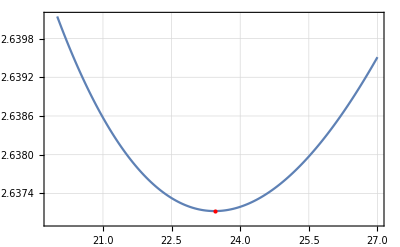
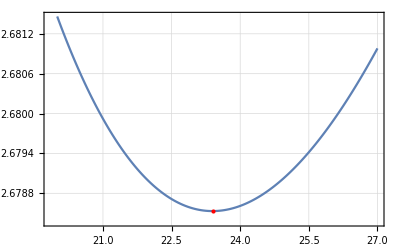
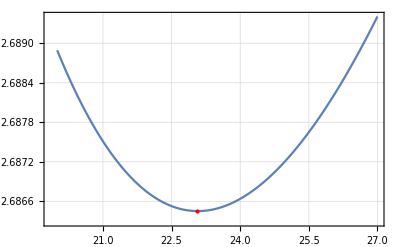
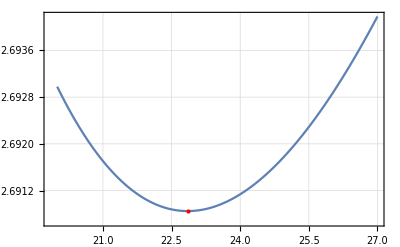
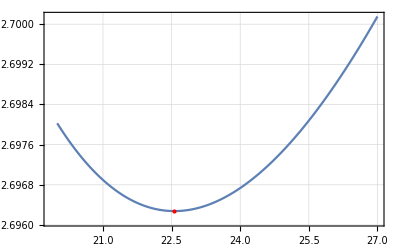
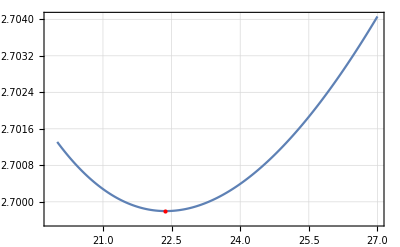
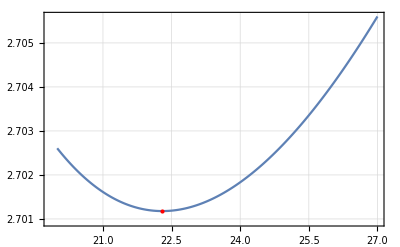
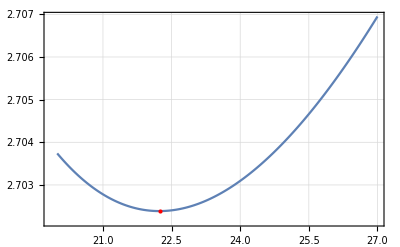
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[CoPCircleN100A1d0List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d0List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d1List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d1List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d2List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d2List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d3List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d3List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d5List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d5List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d7List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d7List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d8List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d8List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d9List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d9List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d10List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d10List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d12List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d12List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d20List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d20List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d48List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d48List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d50List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d50List2[[All,2]]]}}],ListLinePlot[CoPCircleN100A1d98List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d98List2[[All,2]]]}}]}
```

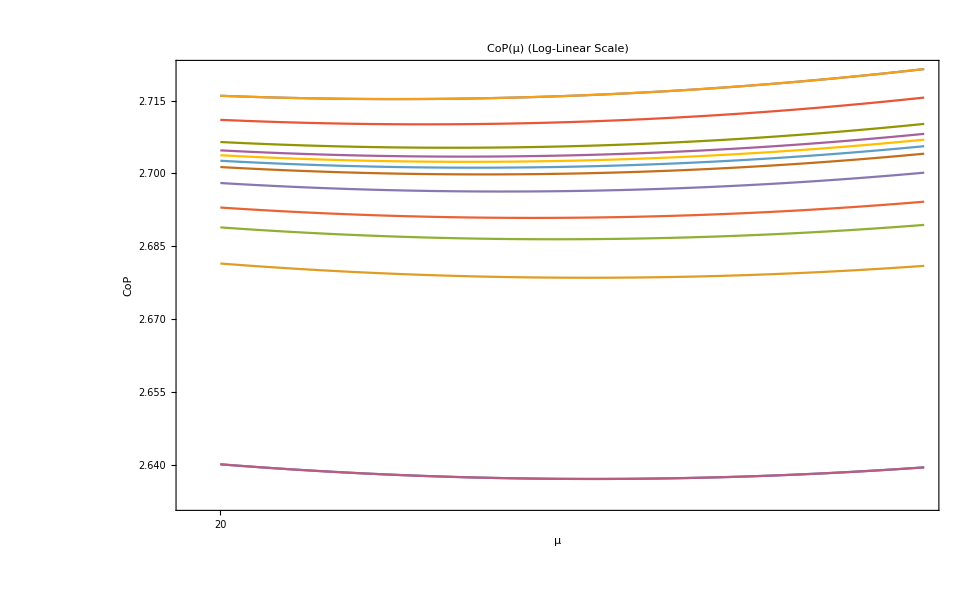

```mathematica
Show[ListLogLinearPlot[{CoPCircleN100A1d0List2,CoPCircleN100A1d1List2,CoPCircleN100A1d2List2,CoPCircleN100A1d3List2,CoPCircleN100A1d5List2,CoPCircleN100A1d7List2,CoPCircleN100A1d8List2,CoPCircleN100A1d9List2,CoPCircleN100A1d10List2,CoPCircleN100A1d12List2,CoPCircleN100A1d20List2,CoPCircleN100A1d48List2,CoPCircleN100A1d50List2,CoPCircleN100A1d98List2},PlotTheme->"Detailed",Joined->True],FrameLabel->{{HoldForm[CoP],None},{HoldForm[μ],None}},PlotLabel->HoldForm[ CoP[μ] (Log-Linear Scale)],LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Axes->True]
```

```mathematica
(*What happens to the covariance matrix at the minima??? What's special about these values for μ?*)
```

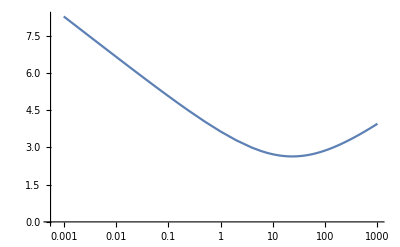
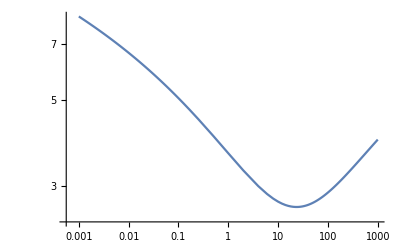
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[CoPCircleN100A1d0List,Joined->True],ListLogLinearPlot[CoPCircleN100A1d0List,Joined->True],ListLogLogPlot[CoPCircleN100A1d0List,Joined->True]}
```

```mathematica
ListLinePlot[CoPCircleN100A1d0List2,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN100A1d0List2[[All,2]]]}}]
```

-Graphics-

```mathematica
(*The symplectic eigenvalues of a pure covariance matrix are always +1. You can understand them as normal modes.Essentially,if you find the eigenvectors you can construct creation/annihilation operators out of them and the Gaussian state with the given covariance matrix is then the ground state to a Hamiltonian with these modes (independent of the frequencies associated to these modes,as this does not change the modes).If you have a mixed state covariance matrix, the symplectic eigenvalues will come as pairs (lambda,1/lambda).Those are exactly the squeezing parameters associated to a two-mode squeezing with a mode outside of the state.The eigenvectors still represent normal modes,but now the state is a thermal state associated to a Hamiltonian with frequencies related to the symplectic eigenvectors (they essentially tell you how far away from the pure zero temperature state one is in the given normal mode).In summary:Yes,for both pure and mixed covariance matrices,one can associate the symplectic eigenvectors to normal modes.For pure states,all symplectic eigenvectors are+1,while for mixed states they are related to how mixed the state is.*)
```

```mathematica
{Det[KGcmqpqp[{100,1/100,1/100,1}]],Tr[KGcmqpqp[{100,1/100,1/100,1}]]}
```

{1.,12832.9}

```mathematica
Eigenvalues[KGcmqpqp[{100,1/100,1/100,1}]]//Chop
```

{200.,199.901,199.901,199.605,199.605,199.112,199.112,198.423,198.423,197.538,197.538,196.457,196.457,195.183,195.183,193.717,193.717,192.059,192.059,190.211,190.211,188.176,188.176,185.955,185.955,183.551,183.551,180.965,180.965,178.201,178.201,175.261,175.261,172.148,172.148,168.866,168.866,165.416,165.416,161.803,161.803,158.031,158.031,154.103,154.103,150.022,150.022,145.794,145.794,141.421,141.421,136.909,136.909,132.262,132.262,127.485,127.485,122.581,122.581,117.557,117.557,112.417,112.417,107.165,107.165,101.808,101.808,100.,96.3507,96.3507,90.7981,90.7981,85.1559,85.1559,79.4296,79.4296,73.6249,73.6249,67.7476,67.7476,61.8034,61.8034,55.7982,55.7982,49.738,49.738,43.6286,43.6286,37.4763,37.4763,31.2869,31.2869,25.0666,25.0666,18.8217,18.8217,12.5581,12.5581,6.28216,6.28216,0.159181,0.159181,0.0796298,0.0796298,0.0531303,0.0531303,0.0398936,0.0398936,0.0319623,0.0319623,0.0266836,0.0266836,0.0229207,0.0229207,0.0201054,0.0201054,0.0179217,0.0179217,0.0161803,0.0161803,0.0147607,0.0147607,0.0135824,0.0135824,0.0125898,0.0125898,0.0117432,0.0117432,0.0110134,0.0110134,0.0103787,0.0103787,0.01,0.00982238,0.00982238,0.00933137,0.00933137,0.00889548,0.00889548,0.00850651,0.00850651,0.00815784,0.00815784,0.00784407,0.00784407,0.00756073,0.00756073,0.0073041,0.0073041,0.00707107,0.00707107,0.00685901,0.00685901,0.00666568,0.00666568,0.00648918,0.00648918,0.00632787,0.00632787,0.00618034,0.00618034,0.00604536,0.00604536,0.00592187,0.00592187,0.00580894,0.00580894,0.00570577,0.00570577,0.00561163,0.00561163,0.00552592,0.00552592,0.00544808,0.00544808,0.00537764,0.00537764,0.00531417,0.00531417,0.00525731,0.00525731,0.00520674,0.00520674,0.00516218,0.00516218,0.00512339,0.00512339,0.00509016,0.00509016,0.00506233,0.00506233,0.00503974,0.00503974,0.00502229,0.00502229,0.00500989,0.00500989,0.00500247,0.00500247,0.005}

```mathematica
ListTotal=Table[{μ,Total[Eigenvalues[KGcmqpqp[{100,1/100,1/100,μ}]]]//Chop},{μ,Listμ1}]
```

{{1000,101519.},{998,101316.},{996,101113.},{994,100910.},{992,100707.},{990,100504.},{988,100301.},{986,100098.},{984,99894.7},{982,99691.7},{980,99488.7},{978,99285.7},{976,99082.8},{974,98879.8},{972,98676.8},{970,98473.8},{968,98270.8},{966,98067.8},{964,97864.9},{962,97661.9},{960,97458.9},{958,97255.9},{956,97052.9},{954,96849.9},{952,96646.9},{950,96444.},{948,96241.},{946,96038.},{944,95835.},{942,95632.},{940,95429.},{938,95226.1},{936,95023.1},{934,94820.1},{932,94617.1},{930,94414.1},{928,94211.2},{926,94008.2},{924,93805.2},{922,93602.2},{920,93399.2},{918,93196.2},{916,92993.3},{914,92790.3},{912,92587.3},{910,92384.3},{908,92181.3},{906,91978.4},{904,91775.4},{902,91572.4},{900,91369.4},{898,91166.4},{896,90963.5},{894,90760.5},{892,90557.5},{890,90354.5},{888,90151.5},{886,89948.6},{884,89745.6},{882,89542.6},{880,89339.6},{878,89136.6},{876,88933.7},{874,88730.7},{872,88527.7},{870,88324.7},{868,88121.8},{866,87918.8},{864,87715.8},{862,87512.8},{860,87309.8},{858,87106.9},{856,86903.9},{854,86700.9},{852,86497.9},{850,86295.},{848,86092.},{846,85889.},{844,85686.},{842,85483.1},{840,85280.1},{838,85077.1},{836,84874.1},{834,84671.1},{832,84468.2},{830,84265.2},{828,84062.2},{826,83859.3},{824,83656.3},{822,83453.3},{820,83250.3},{818,83047.4},{816,82844.4},{814,82641.4},{812,82438.4},{810,82235.5},{808,82032.5},{806,81829.5},{804,81626.5},{802,81423.6},{800,81220.6},{798,81017.6},{796,80814.7},{794,80611.7},{792,80408.7},{790,80205.7},{788,80002.8},{786,79799.8},{784,79596.8},{782,79393.9},{780,79190.9},{778,78987.9},{776,78785.},{774,78582.},{772,78379.},{770,78176.},{768,77973.1},{766,77770.1},{764,77567.1},{762,77364.2},{760,77161.2},{758,76958.2},{756,76755.3},{754,76552.3},{752,76349.3},{750,76146.4},{748,75943.4},{746,75740.4},{744,75537.5},{742,75334.5},{740,75131.5},{738,74928.6},{736,74725.6},{734,74522.6},{732,74319.7},{730,74116.7},{728,73913.8},{726,73710.8},{724,73507.8},{722,73304.9},{720,73101.9},{718,72898.9},{716,72696.},{714,72493.},{712,72290.1},{710,72087.1},{708,71884.1},{706,71681.2},{704,71478.2},{702,71275.2},{700,71072.3},{698,70869.3},{696,70666.4},{694,70463.4},{692,70260.5},{690,70057.5},{688,69854.5},{686,69651.6},{684,69448.6},{682,69245.7},{680,69042.7},{678,68839.7},{676,68636.8},{674,68433.8},{672,68230.9},{670,68027.9},{668,67825.},{666,67622.},{664,67419.1},{662,67216.1},{660,67013.2},{658,66810.2},{656,66607.2},{654,66404.3},{652,66201.3},{650,65998.4},{648,65795.4},{646,65592.5},{644,65389.5},{642,65186.6},{640,64983.6},{638,64780.7},{636,64577.7},{634,64374.8},{632,64171.8},{630,63968.9},{628,63766.},{626,63563.},{624,63360.1},{622,63157.1},{620,62954.2},{618,62751.2},{616,62548.3},{614,62345.3},{612,62142.4},{610,61939.4},{608,61736.5},{606,61533.6},{604,61330.6},{602,61127.7},{600,60924.7},{598,60721.8},{596,60518.9},{594,60315.9},{592,60113.},{590,59910.},{588,59707.1},{586,59504.2},{584,59301.2},{582,59098.3},{580,58895.3},{578,58692.4},{576,58489.5},{574,58286.5},{572,58083.6},{570,57880.7},{568,57677.7},{566,57474.8},{564,57271.9},{562,57068.9},{560,56866.},{558,56663.1},{556,56460.2},{554,56257.2},{552,56054.3},{550,55851.4},{548,55648.4},{546,55445.5},{544,55242.6},{542,55039.7},{540,54836.7},{538,54633.8},{536,54430.9},{534,54228.},{532,54025.},{530,53822.1},{528,53619.2},{526,53416.3},{524,53213.4},{522,53010.4},{520,52807.5},{518,52604.6},{516,52401.7},{514,52198.8},{512,51995.9},{510,51793.},{508,51590.},{506,51387.1},{504,51184.2},{502,50981.3},{500,50778.4},{498,50575.5},{496,50372.6},{494,50169.7},{492,49966.8},{490,49763.9},{488,49560.9},{486,49358.},{484,49155.1},{482,48952.2},{480,48749.3},{478,48546.4},{476,48343.5},{474,48140.6},{472,47937.7},{470,47734.8},{468,47531.9},{466,47329.},{464,47126.2},{462,46923.3},{460,46720.4},{458,46517.5},{456,46314.6},{454,46111.7},{452,45908.8},{450,45705.9},{448,45503.},{446,45300.2},{444,45097.3},{442,44894.4},{440,44691.5},{438,44488.6},{436,44285.8},{434,44082.9},{432,43880.},{430,43677.1},{428,43474.3},{426,43271.4},{424,43068.5},{422,42865.6},{420,42662.8},{418,42459.9},{416,42257.},{414,42054.2},{412,41851.3},{410,41648.5},{408,41445.6},{406,41242.7},{404,41039.9},{402,40837.},{400,40634.2},{398,40431.3},{396,40228.5},{394,40025.6},{392,39822.8},{390,39619.9},{388,39417.1},{386,39214.2},{384,39011.4},{382,38808.6},{380,38605.7},{378,38402.9},{376,38200.1},{374,37997.2},{372,37794.4},{370,37591.6},{368,37388.8},{366,37185.9},{364,36983.1},{362,36780.3},{360,36577.5},{358,36374.7},{356,36171.8},{354,35969.},{352,35766.2},{350,35563.4},{348,35360.6},{346,35157.8},{344,34955.},{342,34752.2},{340,34549.4},{338,34346.6},{336,34143.9},{334,33941.1},{332,33738.3},{330,33535.5},{328,33332.7},{326,33130.},{324,32927.2},{322,32724.4},{320,32521.7},{318,32318.9},{316,32116.1},{314,31913.4},{312,31710.6},{310,31507.9},{308,31305.1},{306,31102.4},{304,30899.7},{302,30696.9},{300,30494.2},{298,30291.5},{296,30088.7},{294,29886.},{292,29683.3},{290,29480.6},{288,29277.9},{286,29075.2},{284,28872.5},{282,28669.8},{280,28467.1},{278,28264.4},{276,28061.7},{274,27859.1},{272,27656.4},{270,27453.7},{268,27251.1},{266,27048.4},{264,26845.8},{262,26643.1},{260,26440.5},{258,26237.9},{256,26035.2},{254,25832.6},{252,25630.},{250,25427.4},{248,25224.8},{246,25022.2},{244,24819.6},{242,24617.},{240,24414.5},{238,24211.9},{236,24009.3},{234,23806.8},{232,23604.2},{230,23401.7},{228,23199.2},{226,22996.7},{224,22794.1},{222,22591.6},{220,22389.2},{218,22186.7},{216,21984.2},{214,21781.7},{212,21579.3},{210,21376.9},{208,21174.4},{206,20972.},{204,20769.6},{202,20567.2},{200,20364.8},{198,20162.5},{196,19960.1},{194,19757.8},{192,19555.4},{190,19353.1},{188,19150.8},{186,18948.5},{184,18746.3},{182,18544.},{180,18341.8},{178,18139.6},{176,17937.4},{174,17735.2},{172,17533.},{170,17330.9},{168,17128.8},{166,16926.7},{164,16724.6},{162,16522.5},{160,16320.5},{158,16118.5},{156,15916.5},{154,15714.6},{152,15512.6},{150,15310.8},{148,15108.9},{146,14907.1},{144,14705.3},{142,14503.5},{140,14301.8},{138,14100.1},{136,13898.4},{134,13696.8},{132,13495.2},{130,13293.7},{128,13092.2},{126,12890.8},{124,12689.4},{122,12488.1},{120,12286.8},{118,12085.6},{116,11884.4},{114,11683.3},{112,11482.3},{110,11281.4},{108,11080.5},{106,10879.7},{104,10679.},{102,10478.4},{100,10277.9},{98,10077.5},{96,9877.18},{94,9676.99},{92,9476.92},{90,9276.99},{88,9077.19},{86,8877.54},{84,8678.06},{82,8478.74},{80,8279.61},{78,8080.68},{76,7881.96},{74,7683.48},{72,7485.25},{70,7287.29},{68,7089.62},{66,6892.29},{64,6695.3},{62,6498.71},{60,6302.54},{58,6106.85},{56,5911.67},{54,5717.08},{52,5523.14},{50,5329.92},{48,5137.52},{46,4946.04},{44,4755.61},{42,4566.37},{40,4378.52},{38,4192.26},{36,4007.86},{34,3825.65},{32,3646.04},{30,3469.55},{28,3296.86},{26,3128.82},{24,2966.61},{22,2811.83},{20,2666.69},{18,2534.4},{16,2419.8},{14,2330.46},{12,2279.02},{10,2288.19},{8,2403.47},{6,2730.93},{4,3588.86},{2,6568.69},{1,12832.9},{1/2,25513.5},{1/4,50950.8},{1/6,76405.1},{1/8,101864.},{1/10,127324.},{1/12,152785.},{1/14,178246.},{1/16,203708.},{1/18,229170.},{1/20,254632.},{1/22,280094.},{1/24,305557.},{1/26,331019.},{1/28,356482.},{1/30,381944.},{1/32,407407.},{1/34,432869.},{1/36,458332.},{1/38,483794.},{1/40,509257.},{1/42,534719.},{1/44,560182.},{1/46,585645.},{1/48,611107.},{1/50,636570.},{1/52,662033.},{1/54,687495.},{1/56,712958.},{1/58,738421.},{1/60,763883.},{1/62,789346.},{1/64,814809.},{1/66,840271.},{1/68,865734.},{1/70,891197.},{1/72,916659.},{1/74,942122.},{1/76,967585.},{1/78,993047.},{1/80,1.01851×10^6},{1/82,1.04397×10^6},{1/84,1.06944×10^6},{1/86,1.0949×10^6},{1/88,1.12036×10^6},{1/90,1.14582×10^6},{1/92,1.17129×10^6},{1/94,1.19675×10^6},{1/96,1.22221×10^6},{1/98,1.24767×10^6},{1/100,1.27314×10^6},{1/102,1.2986×10^6},{1/104,1.32406×10^6},{1/106,1.34952×10^6},{1/108,1.37499×10^6},{1/110,1.40045×10^6},{1/112,1.42591×10^6},{1/114,1.45138×10^6},{1/116,1.47684×10^6},{1/118,1.5023×10^6},{1/120,1.52776×10^6},{1/122,1.55323×10^6},{1/124,1.57869×10^6},{1/126,1.60415×10^6},{1/128,1.62961×10^6},{1/130,1.65508×10^6},{1/132,1.68054×10^6},{1/134,1.706×10^6},{1/136,1.73147×10^6},{1/138,1.75693×10^6},{1/140,1.78239×10^6},{1/142,1.80785×10^6},{1/144,1.83332×10^6},{1/146,1.85878×10^6},{1/148,1.88424×10^6},{1/150,1.9097×10^6},{1/152,1.93517×10^6},{1/154,1.96063×10^6},{1/156,1.98609×10^6},{1/158,2.01156×10^6},{1/160,2.03702×10^6},{1/162,2.06248×10^6},{1/164,2.08794×10^6},{1/166,2.11341×10^6},{1/168,2.13887×10^6},{1/170,2.16433×10^6},{1/172,2.18979×10^6},{1/174,2.21526×10^6},{1/176,2.24072×10^6},{1/178,2.26618×10^6},{1/180,2.29165×10^6},{1/182,2.31711×10^6},{1/184,2.34257×10^6},{1/186,2.36803×10^6},{1/188,2.3935×10^6},{1/190,2.41896×10^6},{1/192,2.44442×10^6},{1/194,2.46988×10^6},{1/196,2.49535×10^6},{1/198,2.52081×10^6},{1/200,2.54627×10^6},{1/202,2.57173×10^6},{1/204,2.5972×10^6},{1/206,2.62266×10^6},{1/208,2.64812×10^6},{1/210,2.67359×10^6},{1/212,2.69905×10^6},{1/214,2.72451×10^6},{1/216,2.74997×10^6},{1/218,2.77544×10^6},{1/220,2.8009×10^6},{1/222,2.82636×10^6},{1/224,2.85182×10^6},{1/226,2.87729×10^6},{1/228,2.90275×10^6},{1/230,2.92821×10^6},{1/232,2.95368×10^6},{1/234,2.97914×10^6},{1/236,3.0046×10^6},{1/238,3.03006×10^6},{1/240,3.05553×10^6},{1/242,3.08099×10^6},{1/244,3.10645×10^6},{1/246,3.13191×10^6},{1/248,3.15738×10^6},{1/250,3.18284×10^6},{1/252,3.2083×10^6},{1/254,3.23377×10^6},{1/256,3.25923×10^6},{1/258,3.28469×10^6},{1/260,3.31015×10^6},{1/262,3.33562×10^6},{1/264,3.36108×10^6},{1/266,3.38654×10^6},{1/268,3.412×10^6},{1/270,3.43747×10^6},{1/272,3.46293×10^6},{1/274,3.48839×10^6},{1/276,3.51386×10^6},{1/278,3.53932×10^6},{1/280,3.56478×10^6},{1/282,3.59024×10^6},{1/284,3.61571×10^6},{1/286,3.64117×10^6},{1/288,3.66663×10^6},{1/290,3.69209×10^6},{1/292,3.71756×10^6},{1/294,3.74302×10^6},{1/296,3.76848×10^6},{1/298,3.79395×10^6},{1/300,3.81941×10^6},{1/302,3.84487×10^6},{1/304,3.87033×10^6},{1/306,3.8958×10^6},{1/308,3.92126×10^6},{1/310,3.94672×10^6},{1/312,3.97218×10^6},{1/314,3.99765×10^6},{1/316,4.02311×10^6},{1/318,4.04857×10^6},{1/320,4.07403×10^6},{1/322,4.0995×10^6},{1/324,4.12496×10^6},{1/326,4.15042×10^6},{1/328,4.17589×10^6},{1/330,4.20135×10^6},{1/332,4.22681×10^6},{1/334,4.25227×10^6},{1/336,4.27774×10^6},{1/338,4.3032×10^6},{1/340,4.32866×10^6},{1/342,4.35412×10^6},{1/344,4.37959×10^6},{1/346,4.40505×10^6},{1/348,4.43051×10^6},{1/350,4.45598×10^6},{1/352,4.48144×10^6},{1/354,4.5069×10^6},{1/356,4.53236×10^6},{1/358,4.55783×10^6},{1/360,4.58329×10^6},{1/362,4.60875×10^6},{1/364,4.63421×10^6},{1/366,4.65968×10^6},{1/368,4.68514×10^6},{1/370,4.7106×10^6},{1/372,4.73607×10^6},{1/374,4.76153×10^6},{1/376,4.78699×10^6},{1/378,4.81245×10^6},{1/380,4.83792×10^6},{1/382,4.86338×10^6},{1/384,4.88884×10^6},{1/386,4.9143×10^6},{1/388,4.93977×10^6},{1/390,4.96523×10^6},{1/392,4.99069×10^6},{1/394,5.01616×10^6},{1/396,5.04162×10^6},{1/398,5.06708×10^6},{1/400,5.09254×10^6},{1/402,5.11801×10^6},{1/404,5.14347×10^6},{1/406,5.16893×10^6},{1/408,5.19439×10^6},{1/410,5.21986×10^6},{1/412,5.24532×10^6},{1/414,5.27078×10^6},{1/416,5.29625×10^6},{1/418,5.32171×10^6},{1/420,5.34717×10^6},{1/422,5.37263×10^6},{1/424,5.3981×10^6},{1/426,5.42356×10^6},{1/428,5.44902×10^6},{1/430,5.47448×10^6},{1/432,5.49995×10^6},{1/434,5.52541×10^6},{1/436,5.55087×10^6},{1/438,5.57634×10^6},{1/440,5.6018×10^6},{1/442,5.62726×10^6},{1/444,5.65272×10^6},{1/446,5.67819×10^6},{1/448,5.70365×10^6},{1/450,5.72911×10^6},{1/452,5.75457×10^6},{1/454,5.78004×10^6},{1/456,5.8055×10^6},{1/458,5.83096×10^6},{1/460,5.85643×10^6},{1/462,5.88189×10^6},{1/464,5.90735×10^6},{1/466,5.93281×10^6},{1/468,5.95828×10^6},{1/470,5.98374×10^6},{1/472,6.0092×10^6},{1/474,6.03466×10^6},{1/476,6.06013×10^6},{1/478,6.08559×10^6},{1/480,6.11105×10^6},{1/482,6.13651×10^6},{1/484,6.16198×10^6},{1/486,6.18744×10^6},{1/488,6.2129×10^6},{1/490,6.23837×10^6},{1/492,6.26383×10^6},{1/494,6.28929×10^6},{1/496,6.31475×10^6},{1/498,6.34022×10^6},{1/500,6.36568×10^6},{1/502,6.39114×10^6},{1/504,6.4166×10^6},{1/506,6.44207×10^6},{1/508,6.46753×10^6},{1/510,6.49299×10^6},{1/512,6.51846×10^6},{1/514,6.54392×10^6},{1/516,6.56938×10^6},{1/518,6.59484×10^6},{1/520,6.62031×10^6},{1/522,6.64577×10^6},{1/524,6.67123×10^6},{1/526,6.69669×10^6},{1/528,6.72216×10^6},{1/530,6.74762×10^6},{1/532,6.77308×10^6},{1/534,6.79855×10^6},{1/536,6.82401×10^6},{1/538,6.84947×10^6},{1/540,6.87493×10^6},{1/542,6.9004×10^6},{1/544,6.92586×10^6},{1/546,6.95132×10^6},{1/548,6.97678×10^6},{1/550,7.00225×10^6},{1/552,7.02771×10^6},{1/554,7.05317×10^6},{1/556,7.07864×10^6},{1/558,7.1041×10^6},{1/560,7.12956×10^6},{1/562,7.15502×10^6},{1/564,7.18049×10^6},{1/566,7.20595×10^6},{1/568,7.23141×10^6},{1/570,7.25687×10^6},{1/572,7.28234×10^6},{1/574,7.3078×10^6},{1/576,7.33326×10^6},{1/578,7.35873×10^6},{1/580,7.38419×10^6},{1/582,7.40965×10^6},{1/584,7.43511×10^6},{1/586,7.46058×10^6},{1/588,7.48604×10^6},{1/590,7.5115×10^6},{1/592,7.53696×10^6},{1/594,7.56243×10^6},{1/596,7.58789×10^6},{1/598,7.61335×10^6},{1/600,7.63882×10^6},{1/602,7.66428×10^6},{1/604,7.68974×10^6},{1/606,7.7152×10^6},{1/608,7.74067×10^6},{1/610,7.76613×10^6},{1/612,7.79159×10^6},{1/614,7.81705×10^6},{1/616,7.84252×10^6},{1/618,7.86798×10^6},{1/620,7.89344×10^6},{1/622,7.91891×10^6},{1/624,7.94437×10^6},{1/626,7.96983×10^6},{1/628,7.99529×10^6},{1/630,8.02076×10^6},{1/632,8.04622×10^6},{1/634,8.07168×10^6},{1/636,8.09714×10^6},{1/638,8.12261×10^6},{1/640,8.14807×10^6},{1/642,8.17353×10^6},{1/644,8.19899×10^6},{1/646,8.22446×10^6},{1/648,8.24992×10^6},{1/650,8.27538×10^6},{1/652,8.30085×10^6},{1/654,8.32631×10^6},{1/656,8.35177×10^6},{1/658,8.37723×10^6},{1/660,8.4027×10^6},{1/662,8.42816×10^6},{1/664,8.45362×10^6},{1/666,8.47908×10^6},{1/668,8.50455×10^6},{1/670,8.53001×10^6},{1/672,8.55547×10^6},{1/674,8.58094×10^6},{1/676,8.6064×10^6},{1/678,8.63186×10^6},{1/680,8.65732×10^6},{1/682,8.68279×10^6},{1/684,8.70825×10^6},{1/686,8.73371×10^6},{1/688,8.75917×10^6},{1/690,8.78464×10^6},{1/692,8.8101×10^6},{1/694,8.83556×10^6},{1/696,8.86103×10^6},{1/698,8.88649×10^6},{1/700,8.91195×10^6},{1/702,8.93741×10^6},{1/704,8.96288×10^6},{1/706,8.98834×10^6},{1/708,9.0138×10^6},{1/710,9.03926×10^6},{1/712,9.06473×10^6},{1/714,9.09019×10^6},{1/716,9.11565×10^6},{1/718,9.14112×10^6},{1/720,9.16658×10^6},{1/722,9.19204×10^6},{1/724,9.2175×10^6},{1/726,9.24297×10^6},{1/728,9.26843×10^6},{1/730,9.29389×10^6},{1/732,9.31935×10^6},{1/734,9.34482×10^6},{1/736,9.37028×10^6},{1/738,9.39574×10^6},{1/740,9.42121×10^6},{1/742,9.44667×10^6},{1/744,9.47213×10^6},{1/746,9.49759×10^6},{1/748,9.52306×10^6},{1/750,9.54852×10^6},{1/752,9.57398×10^6},{1/754,9.59944×10^6},{1/756,9.62491×10^6},{1/758,9.65037×10^6},{1/760,9.67583×10^6},{1/762,9.7013×10^6},{1/764,9.72676×10^6},{1/766,9.75222×10^6},{1/768,9.77768×10^6},{1/770,9.80315×10^6},{1/772,9.82861×10^6},{1/774,9.85407×10^6},{1/776,9.87953×10^6},{1/778,9.905×10^6},{1/780,9.93046×10^6},{1/782,9.95592×10^6},{1/784,9.98139×10^6},{1/786,1.00068×10^7},{1/788,1.00323×10^7},{1/790,1.00578×10^7},{1/792,1.00832×10^7},{1/794,1.01087×10^7},{1/796,1.01342×10^7},{1/798,1.01596×10^7},{1/800,1.01851×10^7},{1/802,1.02105×10^7},{1/804,1.0236×10^7},{1/806,1.02615×10^7},{1/808,1.02869×10^7},{1/810,1.03124×10^7},{1/812,1.03379×10^7},{1/814,1.03633×10^7},{1/816,1.03888×10^7},{1/818,1.04143×10^7},{1/820,1.04397×10^7},{1/822,1.04652×10^7},{1/824,1.04906×10^7},{1/826,1.05161×10^7},{1/828,1.05416×10^7},{1/830,1.0567×10^7},{1/832,1.05925×10^7},{1/834,1.0618×10^7},{1/836,1.06434×10^7},{1/838,1.06689×10^7},{1/840,1.06943×10^7},{1/842,1.07198×10^7},{1/844,1.07453×10^7},{1/846,1.07707×10^7},{1/848,1.07962×10^7},{1/850,1.08217×10^7},{1/852,1.08471×10^7},{1/854,1.08726×10^7},{1/856,1.0898×10^7},{1/858,1.09235×10^7},{1/860,1.0949×10^7},{1/862,1.09744×10^7},{1/864,1.09999×10^7},{1/866,1.10254×10^7},{1/868,1.10508×10^7},{1/870,1.10763×10^7},{1/872,1.11017×10^7},{1/874,1.11272×10^7},{1/876,1.11527×10^7},{1/878,1.11781×10^7},{1/880,1.12036×10^7},{1/882,1.12291×10^7},{1/884,1.12545×10^7},{1/886,1.128×10^7},{1/888,1.13054×10^7},{1/890,1.13309×10^7},{1/892,1.13564×10^7},{1/894,1.13818×10^7},{1/896,1.14073×10^7},{1/898,1.14328×10^7},{1/900,1.14582×10^7},{1/902,1.14837×10^7},{1/904,1.15091×10^7},{1/906,1.15346×10^7},{1/908,1.15601×10^7},{1/910,1.15855×10^7},{1/912,1.1611×10^7},{1/914,1.16365×10^7},{1/916,1.16619×10^7},{1/918,1.16874×10^7},{1/920,1.17128×10^7},{1/922,1.17383×10^7},{1/924,1.17638×10^7},{1/926,1.17892×10^7},{1/928,1.18147×10^7},{1/930,1.18402×10^7},{1/932,1.18656×10^7},{1/934,1.18911×10^7},{1/936,1.19166×10^7},{1/938,1.1942×10^7},{1/940,1.19675×10^7},{1/942,1.19929×10^7},{1/944,1.20184×10^7},{1/946,1.20439×10^7},{1/948,1.20693×10^7},{1/950,1.20948×10^7},{1/952,1.21203×10^7},{1/954,1.21457×10^7},{1/956,1.21712×10^7},{1/958,1.21966×10^7},{1/960,1.22221×10^7},{1/962,1.22476×10^7},{1/964,1.2273×10^7},{1/966,1.22985×10^7},{1/968,1.2324×10^7},{1/970,1.23494×10^7},{1/972,1.23749×10^7},{1/974,1.24003×10^7},{1/976,1.24258×10^7},{1/978,1.24513×10^7},{1/980,1.24767×10^7},{1/982,1.25022×10^7},{1/984,1.25277×10^7},{1/986,1.25531×10^7},{1/988,1.25786×10^7},{1/990,1.2604×10^7},{1/992,1.26295×10^7},{1/994,1.2655×10^7},{1/996,1.26804×10^7},{1/998,1.27059×10^7},{1/1000,1.27314×10^7}}

```mathematica
Length[ListTotal]
```

1001

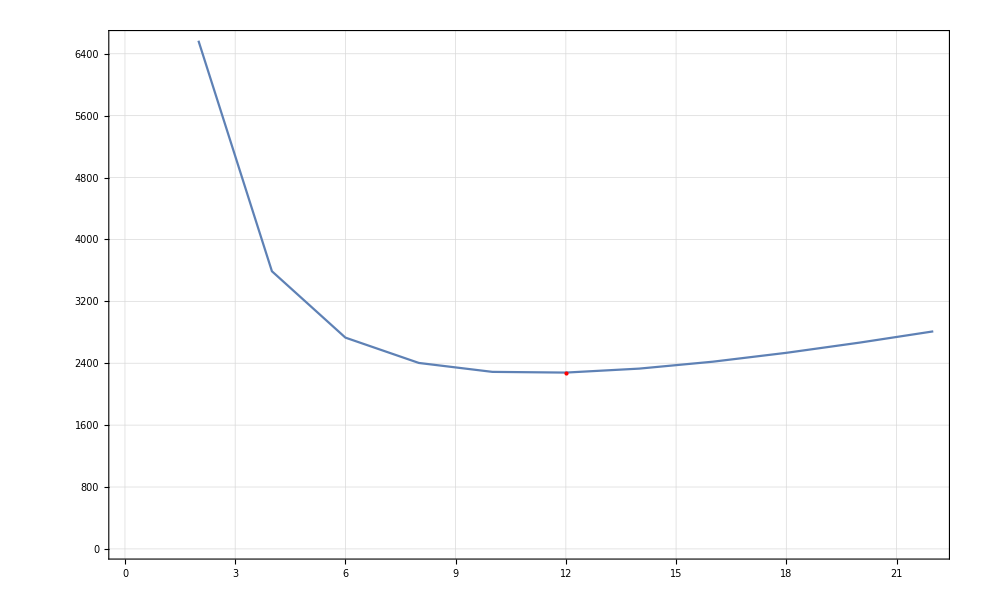

```mathematica
ListLinePlot[ListTotal⟦490;;500⟧,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[ListTotal[[All,2]]]}}]
```

```mathematica
ListTotal2=Table[{μ,1/(2Sqrt[2])Sqrt[Total[Eigenvalues[KGcmqpqp[{100,1/100,1/100,μ}]]^2]]//Chop},{μ,Listμ1}]
```

{{1000,35355.5},{998,35284.8},{996,35214.1},{994,35143.4},{992,35072.6},{990,35001.9},{988,34931.2},{986,34860.5},{984,34789.8},{982,34719.1},{980,34648.4},{978,34577.7},{976,34507.},{974,34436.2},{972,34365.5},{970,34294.8},{968,34224.1},{966,34153.4},{964,34082.7},{962,34012.},{960,33941.3},{958,33870.6},{956,33799.8},{954,33729.1},{952,33658.4},{950,33587.7},{948,33517.},{946,33446.3},{944,33375.6},{942,33304.9},{940,33234.2},{938,33163.4},{936,33092.7},{934,33022.},{932,32951.3},{930,32880.6},{928,32809.9},{926,32739.2},{924,32668.5},{922,32597.8},{920,32527.},{918,32456.3},{916,32385.6},{914,32314.9},{912,32244.2},{910,32173.5},{908,32102.8},{906,32032.1},{904,31961.4},{902,31890.6},{900,31819.9},{898,31749.2},{896,31678.5},{894,31607.8},{892,31537.1},{890,31466.4},{888,31395.7},{886,31325.},{884,31254.2},{882,31183.5},{880,31112.8},{878,31042.1},{876,30971.4},{874,30900.7},{872,30830.},{870,30759.3},{868,30688.6},{866,30617.9},{864,30547.1},{862,30476.4},{860,30405.7},{858,30335.},{856,30264.3},{854,30193.6},{852,30122.9},{850,30052.2},{848,29981.5},{846,29910.7},{844,29840.},{842,29769.3},{840,29698.6},{838,29627.9},{836,29557.2},{834,29486.5},{832,29415.8},{830,29345.1},{828,29274.3},{826,29203.6},{824,29132.9},{822,29062.2},{820,28991.5},{818,28920.8},{816,28850.1},{814,28779.4},{812,28708.7},{810,28637.9},{808,28567.2},{806,28496.5},{804,28425.8},{802,28355.1},{800,28284.4},{798,28213.7},{796,28143.},{794,28072.3},{792,28001.5},{790,27930.8},{788,27860.1},{786,27789.4},{784,27718.7},{782,27648.},{780,27577.3},{778,27506.6},{776,27435.9},{774,27365.1},{772,27294.4},{770,27223.7},{768,27153.},{766,27082.3},{764,27011.6},{762,26940.9},{760,26870.2},{758,26799.5},{756,26728.7},{754,26658.},{752,26587.3},{750,26516.6},{748,26445.9},{746,26375.2},{744,26304.5},{742,26233.8},{740,26163.1},{738,26092.3},{736,26021.6},{734,25950.9},{732,25880.2},{730,25809.5},{728,25738.8},{726,25668.1},{724,25597.4},{722,25526.7},{720,25456.},{718,25385.2},{716,25314.5},{714,25243.8},{712,25173.1},{710,25102.4},{708,25031.7},{706,24961.},{704,24890.3},{702,24819.6},{700,24748.8},{698,24678.1},{696,24607.4},{694,24536.7},{692,24466.},{690,24395.3},{688,24324.6},{686,24253.9},{684,24183.2},{682,24112.4},{680,24041.7},{678,23971.},{676,23900.3},{674,23829.6},{672,23758.9},{670,23688.2},{668,23617.5},{666,23546.8},{664,23476.},{662,23405.3},{660,23334.6},{658,23263.9},{656,23193.2},{654,23122.5},{652,23051.8},{650,22981.1},{648,22910.4},{646,22839.6},{644,22768.9},{642,22698.2},{640,22627.5},{638,22556.8},{636,22486.1},{634,22415.4},{632,22344.7},{630,22274.},{628,22203.2},{626,22132.5},{624,22061.8},{622,21991.1},{620,21920.4},{618,21849.7},{616,21779.},{614,21708.3},{612,21637.6},{610,21566.8},{608,21496.1},{606,21425.4},{604,21354.7},{602,21284.},{600,21213.3},{598,21142.6},{596,21071.9},{594,21001.2},{592,20930.4},{590,20859.7},{588,20789.},{586,20718.3},{584,20647.6},{582,20576.9},{580,20506.2},{578,20435.5},{576,20364.8},{574,20294.},{572,20223.3},{570,20152.6},{568,20081.9},{566,20011.2},{564,19940.5},{562,19869.8},{560,19799.1},{558,19728.4},{556,19657.7},{554,19586.9},{552,19516.2},{550,19445.5},{548,19374.8},{546,19304.1},{544,19233.4},{542,19162.7},{540,19092.},{538,19021.3},{536,18950.5},{534,18879.8},{532,18809.1},{530,18738.4},{528,18667.7},{526,18597.},{524,18526.3},{522,18455.6},{520,18384.9},{518,18314.1},{516,18243.4},{514,18172.7},{512,18102.},{510,18031.3},{508,17960.6},{506,17889.9},{504,17819.2},{502,17748.5},{500,17677.7},{498,17607.},{496,17536.3},{494,17465.6},{492,17394.9},{490,17324.2},{488,17253.5},{486,17182.8},{484,17112.1},{482,17041.3},{480,16970.6},{478,16899.9},{476,16829.2},{474,16758.5},{472,16687.8},{470,16617.1},{468,16546.4},{466,16475.7},{464,16404.9},{462,16334.2},{460,16263.5},{458,16192.8},{456,16122.1},{454,16051.4},{452,15980.7},{450,15910.},{448,15839.3},{446,15768.5},{444,15697.8},{442,15627.1},{440,15556.4},{438,15485.7},{436,15415.},{434,15344.3},{432,15273.6},{430,15202.9},{428,15132.1},{426,15061.4},{424,14990.7},{422,14920.},{420,14849.3},{418,14778.6},{416,14707.9},{414,14637.2},{412,14566.5},{410,14495.7},{408,14425.},{406,14354.3},{404,14283.6},{402,14212.9},{400,14142.2},{398,14071.5},{396,14000.8},{394,13930.1},{392,13859.4},{390,13788.6},{388,13717.9},{386,13647.2},{384,13576.5},{382,13505.8},{380,13435.1},{378,13364.4},{376,13293.7},{374,13223.},{372,13152.2},{370,13081.5},{368,13010.8},{366,12940.1},{364,12869.4},{362,12798.7},{360,12728.},{358,12657.3},{356,12586.6},{354,12515.8},{352,12445.1},{350,12374.4},{348,12303.7},{346,12233.},{344,12162.3},{342,12091.6},{340,12020.9},{338,11950.2},{336,11879.4},{334,11808.7},{332,11738.},{330,11667.3},{328,11596.6},{326,11525.9},{324,11455.2},{322,11384.5},{320,11313.8},{318,11243.},{316,11172.3},{314,11101.6},{312,11030.9},{310,10960.2},{308,10889.5},{306,10818.8},{304,10748.1},{302,10677.4},{300,10606.6},{298,10535.9},{296,10465.2},{294,10394.5},{292,10323.8},{290,10253.1},{288,10182.4},{286,10111.7},{284,10041.},{282,9970.25},{280,9899.54},{278,9828.83},{276,9758.11},{274,9687.4},{272,9616.69},{270,9545.98},{268,9475.27},{266,9404.56},{264,9333.85},{262,9263.14},{260,9192.43},{258,9121.72},{256,9051.},{254,8980.29},{252,8909.58},{250,8838.87},{248,8768.16},{246,8697.45},{244,8626.74},{242,8556.03},{240,8485.32},{238,8414.61},{236,8343.9},{234,8273.18},{232,8202.47},{230,8131.76},{228,8061.05},{226,7990.34},{224,7919.63},{222,7848.92},{220,7778.21},{218,7707.5},{216,7636.79},{214,7566.07},{212,7495.36},{210,7424.65},{208,7353.94},{206,7283.23},{204,7212.52},{202,7141.81},{200,7071.1},{198,7000.39},{196,6929.68},{194,6858.96},{192,6788.25},{190,6717.54},{188,6646.83},{186,6576.12},{184,6505.41},{182,6434.7},{180,6363.99},{178,6293.28},{176,6222.57},{174,6151.86},{172,6081.14},{170,6010.43},{168,5939.72},{166,5869.01},{164,5798.3},{162,5727.59},{160,5656.88},{158,5586.17},{156,5515.46},{154,5444.75},{152,5374.03},{150,5303.32},{148,5232.61},{146,5161.9},{144,5091.19},{142,5020.48},{140,4949.77},{138,4879.06},{136,4808.35},{134,4737.64},{132,4666.93},{130,4596.21},{128,4525.5},{126,4454.79},{124,4384.08},{122,4313.37},{120,4242.66},{118,4171.95},{116,4101.24},{114,4030.53},{112,3959.82},{110,3889.11},{108,3818.4},{106,3747.68},{104,3676.97},{102,3606.26},{100,3535.55},{98,3464.84},{96,3394.13},{94,3323.42},{92,3252.71},{90,3182.},{88,3111.29},{86,3040.58},{84,2969.87},{82,2899.16},{80,2828.45},{78,2757.74},{76,2687.03},{74,2616.31},{72,2545.6},{70,2474.89},{68,2404.18},{66,2333.47},{64,2262.76},{62,2192.05},{60,2121.35},{58,2050.64},{56,1979.93},{54,1909.22},{52,1838.51},{50,1767.8},{48,1697.1},{46,1626.39},{44,1555.68},{42,1484.98},{40,1414.27},{38,1343.57},{36,1272.87},{34,1202.18},{32,1131.48},{30,1060.8},{28,990.115},{26,919.444},{24,848.787},{22,778.153},{20,707.552},{18,637.005},{16,566.55},{14,496.264},{12,426.307},{10,357.073},{8,289.667},{6,227.914},{4,188.746},{2,259.808},{1,501.248},{1/2,1000.16},{1/4,2000.02},{1/6,3000.01},{1/8,4000.},{1/10,5000.},{1/12,6000.},{1/14,7000.},{1/16,8000.},{1/18,9000.},{1/20,10000.},{1/22,11000.},{1/24,12000.},{1/26,13000.},{1/28,14000.},{1/30,15000.},{1/32,16000.},{1/34,17000.},{1/36,18000.},{1/38,19000.},{1/40,20000.},{1/42,21000.},{1/44,22000.},{1/46,23000.},{1/48,24000.},{1/50,25000.},{1/52,26000.},{1/54,27000.},{1/56,28000.},{1/58,29000.},{1/60,30000.},{1/62,31000.},{1/64,32000.},{1/66,33000.},{1/68,34000.},{1/70,35000.},{1/72,36000.},{1/74,37000.},{1/76,38000.},{1/78,39000.},{1/80,40000.},{1/82,41000.},{1/84,42000.},{1/86,43000.},{1/88,44000.},{1/90,45000.},{1/92,46000.},{1/94,47000.},{1/96,48000.},{1/98,49000.},{1/100,50000.},{1/102,51000.},{1/104,52000.},{1/106,53000.},{1/108,54000.},{1/110,55000.},{1/112,56000.},{1/114,57000.},{1/116,58000.},{1/118,59000.},{1/120,60000.},{1/122,61000.},{1/124,62000.},{1/126,63000.},{1/128,64000.},{1/130,65000.},{1/132,66000.},{1/134,67000.},{1/136,68000.},{1/138,69000.},{1/140,70000.},{1/142,71000.},{1/144,72000.},{1/146,73000.},{1/148,74000.},{1/150,75000.},{1/152,76000.},{1/154,77000.},{1/156,78000.},{1/158,79000.},{1/160,80000.},{1/162,81000.},{1/164,82000.},{1/166,83000.},{1/168,84000.},{1/170,85000.},{1/172,86000.},{1/174,87000.},{1/176,88000.},{1/178,89000.},{1/180,90000.},{1/182,91000.},{1/184,92000.},{1/186,93000.},{1/188,94000.},{1/190,95000.},{1/192,96000.},{1/194,97000.},{1/196,98000.},{1/198,99000.},{1/200,100000.},{1/202,101000.},{1/204,102000.},{1/206,103000.},{1/208,104000.},{1/210,105000.},{1/212,106000.},{1/214,107000.},{1/216,108000.},{1/218,109000.},{1/220,110000.},{1/222,111000.},{1/224,112000.},{1/226,113000.},{1/228,114000.},{1/230,115000.},{1/232,116000.},{1/234,117000.},{1/236,118000.},{1/238,119000.},{1/240,120000.},{1/242,121000.},{1/244,122000.},{1/246,123000.},{1/248,124000.},{1/250,125000.},{1/252,126000.},{1/254,127000.},{1/256,128000.},{1/258,129000.},{1/260,130000.},{1/262,131000.},{1/264,132000.},{1/266,133000.},{1/268,134000.},{1/270,135000.},{1/272,136000.},{1/274,137000.},{1/276,138000.},{1/278,139000.},{1/280,140000.},{1/282,141000.},{1/284,142000.},{1/286,143000.},{1/288,144000.},{1/290,145000.},{1/292,146000.},{1/294,147000.},{1/296,148000.},{1/298,149000.},{1/300,150000.},{1/302,151000.},{1/304,152000.},{1/306,153000.},{1/308,154000.},{1/310,155000.},{1/312,156000.},{1/314,157000.},{1/316,158000.},{1/318,159000.},{1/320,160000.},{1/322,161000.},{1/324,162000.},{1/326,163000.},{1/328,164000.},{1/330,165000.},{1/332,166000.},{1/334,167000.},{1/336,168000.},{1/338,169000.},{1/340,170000.},{1/342,171000.},{1/344,172000.},{1/346,173000.},{1/348,174000.},{1/350,175000.},{1/352,176000.},{1/354,177000.},{1/356,178000.},{1/358,179000.},{1/360,180000.},{1/362,181000.},{1/364,182000.},{1/366,183000.},{1/368,184000.},{1/370,185000.},{1/372,186000.},{1/374,187000.},{1/376,188000.},{1/378,189000.},{1/380,190000.},{1/382,191000.},{1/384,192000.},{1/386,193000.},{1/388,194000.},{1/390,195000.},{1/392,196000.},{1/394,197000.},{1/396,198000.},{1/398,199000.},{1/400,200000.},{1/402,201000.},{1/404,202000.},{1/406,203000.},{1/408,204000.},{1/410,205000.},{1/412,206000.},{1/414,207000.},{1/416,208000.},{1/418,209000.},{1/420,210000.},{1/422,211000.},{1/424,212000.},{1/426,213000.},{1/428,214000.},{1/430,215000.},{1/432,216000.},{1/434,217000.},{1/436,218000.},{1/438,219000.},{1/440,220000.},{1/442,221000.},{1/444,222000.},{1/446,223000.},{1/448,224000.},{1/450,225000.},{1/452,226000.},{1/454,227000.},{1/456,228000.},{1/458,229000.},{1/460,230000.},{1/462,231000.},{1/464,232000.},{1/466,233000.},{1/468,234000.},{1/470,235000.},{1/472,236000.},{1/474,237000.},{1/476,238000.},{1/478,239000.},{1/480,240000.},{1/482,241000.},{1/484,242000.},{1/486,243000.},{1/488,244000.},{1/490,245000.},{1/492,246000.},{1/494,247000.},{1/496,248000.},{1/498,249000.},{1/500,250000.},{1/502,251000.},{1/504,252000.},{1/506,253000.},{1/508,254000.},{1/510,255000.},{1/512,256000.},{1/514,257000.},{1/516,258000.},{1/518,259000.},{1/520,260000.},{1/522,261000.},{1/524,262000.},{1/526,263000.},{1/528,264000.},{1/530,265000.},{1/532,266000.},{1/534,267000.},{1/536,268000.},{1/538,269000.},{1/540,270000.},{1/542,271000.},{1/544,272000.},{1/546,273000.},{1/548,274000.},{1/550,275000.},{1/552,276000.},{1/554,277000.},{1/556,278000.},{1/558,279000.},{1/560,280000.},{1/562,281000.},{1/564,282000.},{1/566,283000.},{1/568,284000.},{1/570,285000.},{1/572,286000.},{1/574,287000.},{1/576,288000.},{1/578,289000.},{1/580,290000.},{1/582,291000.},{1/584,292000.},{1/586,293000.},{1/588,294000.},{1/590,295000.},{1/592,296000.},{1/594,297000.},{1/596,298000.},{1/598,299000.},{1/600,300000.},{1/602,301000.},{1/604,302000.},{1/606,303000.},{1/608,304000.},{1/610,305000.},{1/612,306000.},{1/614,307000.},{1/616,308000.},{1/618,309000.},{1/620,310000.},{1/622,311000.},{1/624,312000.},{1/626,313000.},{1/628,314000.},{1/630,315000.},{1/632,316000.},{1/634,317000.},{1/636,318000.},{1/638,319000.},{1/640,320000.},{1/642,321000.},{1/644,322000.},{1/646,323000.},{1/648,324000.},{1/650,325000.},{1/652,326000.},{1/654,327000.},{1/656,328000.},{1/658,329000.},{1/660,330000.},{1/662,331000.},{1/664,332000.},{1/666,333000.},{1/668,334000.},{1/670,335000.},{1/672,336000.},{1/674,337000.},{1/676,338000.},{1/678,339000.},{1/680,340000.},{1/682,341000.},{1/684,342000.},{1/686,343000.},{1/688,344000.},{1/690,345000.},{1/692,346000.},{1/694,347000.},{1/696,348000.},{1/698,349000.},{1/700,350000.},{1/702,351000.},{1/704,352000.},{1/706,353000.},{1/708,354000.},{1/710,355000.},{1/712,356000.},{1/714,357000.},{1/716,358000.},{1/718,359000.},{1/720,360000.},{1/722,361000.},{1/724,362000.},{1/726,363000.},{1/728,364000.},{1/730,365000.},{1/732,366000.},{1/734,367000.},{1/736,368000.},{1/738,369000.},{1/740,370000.},{1/742,371000.},{1/744,372000.},{1/746,373000.},{1/748,374000.},{1/750,375000.},{1/752,376000.},{1/754,377000.},{1/756,378000.},{1/758,379000.},{1/760,380000.},{1/762,381000.},{1/764,382000.},{1/766,383000.},{1/768,384000.},{1/770,385000.},{1/772,386000.},{1/774,387000.},{1/776,388000.},{1/778,389000.},{1/780,390000.},{1/782,391000.},{1/784,392000.},{1/786,393000.},{1/788,394000.},{1/790,395000.},{1/792,396000.},{1/794,397000.},{1/796,398000.},{1/798,399000.},{1/800,400000.},{1/802,401000.},{1/804,402000.},{1/806,403000.},{1/808,404000.},{1/810,405000.},{1/812,406000.},{1/814,407000.},{1/816,408000.},{1/818,409000.},{1/820,410000.},{1/822,411000.},{1/824,412000.},{1/826,413000.},{1/828,414000.},{1/830,415000.},{1/832,416000.},{1/834,417000.},{1/836,418000.},{1/838,419000.},{1/840,420000.},{1/842,421000.},{1/844,422000.},{1/846,423000.},{1/848,424000.},{1/850,425000.},{1/852,426000.},{1/854,427000.},{1/856,428000.},{1/858,429000.},{1/860,430000.},{1/862,431000.},{1/864,432000.},{1/866,433000.},{1/868,434000.},{1/870,435000.},{1/872,436000.},{1/874,437000.},{1/876,438000.},{1/878,439000.},{1/880,440000.},{1/882,441000.},{1/884,442000.},{1/886,443000.},{1/888,444000.},{1/890,445000.},{1/892,446000.},{1/894,447000.},{1/896,448000.},{1/898,449000.},{1/900,450000.},{1/902,451000.},{1/904,452000.},{1/906,453000.},{1/908,454000.},{1/910,455000.},{1/912,456000.},{1/914,457000.},{1/916,458000.},{1/918,459000.},{1/920,460000.},{1/922,461000.},{1/924,462000.},{1/926,463000.},{1/928,464000.},{1/930,465000.},{1/932,466000.},{1/934,467000.},{1/936,468000.},{1/938,469000.},{1/940,470000.},{1/942,471000.},{1/944,472000.},{1/946,473000.},{1/948,474000.},{1/950,475000.},{1/952,476000.},{1/954,477000.},{1/956,478000.},{1/958,479000.},{1/960,480000.},{1/962,481000.},{1/964,482000.},{1/966,483000.},{1/968,484000.},{1/970,485000.},{1/972,486000.},{1/974,487000.},{1/976,488000.},{1/978,489000.},{1/980,490000.},{1/982,491000.},{1/984,492000.},{1/986,493000.},{1/988,494000.},{1/990,495000.},{1/992,496000.},{1/994,497000.},{1/996,498000.},{1/998,499000.},{1/1000,500000.}}

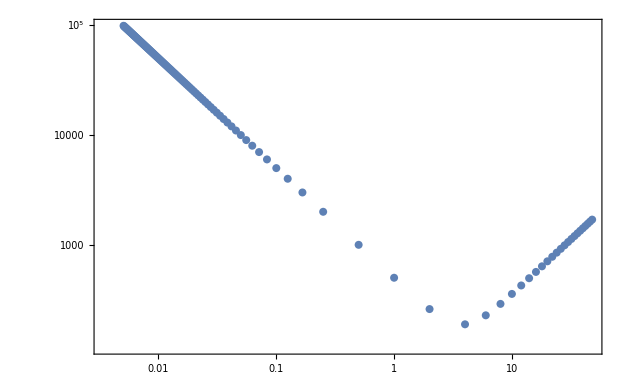

```mathematica
ListLogLogPlot[ListTotal2⟦477;;600⟧,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[ListTotal2[[All,2]]]}}]
```

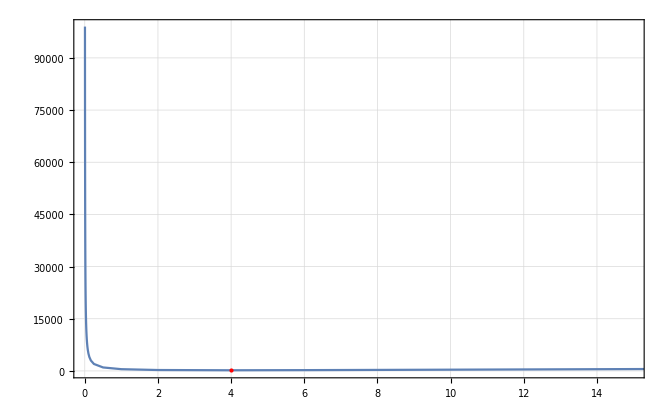

```mathematica
ListLinePlot[ListTotal2⟦477;;600⟧,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[ListTotal2[[All,2]]]}}]
```

```mathematica
Eigenvalues[KGcmqpqp[{100,1/100,1/100,12}]]//Chop
```

{1200.,16.6667,16.6584,16.6584,16.6338,16.6338,16.5927,16.5927,16.5352,16.5352,16.4615,16.4615,16.3715,16.3715,16.2653,16.2653,16.1431,16.1431,16.0049,16.0049,15.8509,15.8509,15.6813,15.6813,15.4963,15.4963,15.2959,15.2959,15.0805,15.0805,14.8501,14.8501,14.6051,14.6051,14.3457,14.3457,14.0721,14.0721,13.7847,13.7847,13.4836,13.4836,13.1693,13.1693,12.8419,12.8419,12.5019,12.5019,12.1495,12.1495,11.7851,11.7851,11.4091,11.4091,11.0219,11.0219,10.6237,10.6237,10.2151,10.2151,9.79642,9.79642,9.36806,9.36806,8.93045,8.93045,8.48402,8.48402,8.02923,8.02923,7.56651,7.56651,7.09632,7.09632,6.61913,6.61913,6.13541,6.13541,5.64563,5.64563,5.15028,5.15028,4.64985,4.64985,4.14483,4.14483,3.63572,3.63572,3.12302,3.12302,2.60724,2.60724,2.08889,2.08889,1.91017,1.91017,1.56847,1.56847,1.04651,1.04651,0.955558,0.955558,0.637563,0.637563,0.523513,0.523513,0.478724,0.478724,0.383547,0.383547,0.320203,0.320203,0.275049,0.275049,0.241264,0.241264,0.215061,0.215061,0.194164,0.194164,0.177128,0.177128,0.162988,0.162988,0.151077,0.151077,0.140918,0.140918,0.132161,0.132161,0.124545,0.124545,0.117869,0.117869,0.111976,0.111976,0.106746,0.106746,0.102078,0.102078,0.0978941,0.0978941,0.0941289,0.0941289,0.0907288,0.0907288,0.0876492,0.0876492,0.0848528,0.0848528,0.0823081,0.0823081,0.0799882,0.0799882,0.0778702,0.0778702,0.0759345,0.0759345,0.0741641,0.0741641,0.0725443,0.0725443,0.0710624,0.0710624,0.0697073,0.0697073,0.0684692,0.0684692,0.0673396,0.0673396,0.066311,0.066311,0.065377,0.065377,0.0645316,0.0645316,0.06377,0.06377,0.0630877,0.0630877,0.0624809,0.0624809,0.0619462,0.0619462,0.0614807,0.0614807,0.0610819,0.0610819,0.0607479,0.0607479,0.0604769,0.0604769,0.0602675,0.0602675,0.0601186,0.0601186,0.0600296,0.0600296,0.06,0.000833333}

```mathematica
Eigenvalues[KGcmqpqp[{100,1/100,1/100,23}]]//Chop
```

{2300.,8.69565,8.69136,8.69136,8.67849,8.67849,8.65706,8.65706,8.62708,8.62708,8.58859,8.58859,8.54163,8.54163,8.48623,8.48623,8.42246,8.42246,8.35038,8.35038,8.27006,8.27006,8.18157,8.18157,8.08501,8.08501,7.98048,7.98048,7.86806,7.86806,7.74788,7.74788,7.62006,7.62006,7.48471,7.48471,7.34198,7.34198,7.19201,7.19201,7.03493,7.03493,6.87091,6.87091,6.70012,6.70012,6.5227,6.5227,6.33886,6.33886,6.14875,6.14875,5.95258,5.95258,5.75054,5.75054,5.54282,5.54282,5.32963,5.32963,5.11118,5.11118,4.88768,4.88768,4.65936,4.65936,4.42645,4.42645,4.18916,4.18916,3.94774,3.94774,3.70243,3.70243,3.66116,3.66116,3.45346,3.45346,3.20108,3.20108,2.94555,2.94555,2.6871,2.6871,2.42601,2.42601,2.16252,2.16252,1.8969,1.8969,1.83149,1.83149,1.6294,1.6294,1.3603,1.3603,1.222,1.222,1.08985,1.08985,0.917554,0.917554,0.818333,0.818333,0.735132,0.735132,0.613722,0.613722,0.546005,0.546005,0.527177,0.527177,0.462423,0.462423,0.4122,0.4122,0.372148,0.372148,0.339495,0.339495,0.312394,0.312394,0.289565,0.289565,0.273137,0.273137,0.270093,0.270093,0.253309,0.253309,0.238711,0.238711,0.225915,0.225915,0.214622,0.214622,0.204596,0.204596,0.19565,0.19565,0.18763,0.18763,0.180414,0.180414,0.173897,0.173897,0.167994,0.167994,0.162635,0.162635,0.157757,0.157757,0.153311,0.153311,0.149251,0.149251,0.145541,0.145541,0.142148,0.142148,0.139043,0.139043,0.136203,0.136203,0.133606,0.133606,0.131233,0.131233,0.129068,0.129068,0.127096,0.127096,0.125306,0.125306,0.123686,0.123686,0.122226,0.122226,0.120918,0.120918,0.119755,0.119755,0.11873,0.11873,0.117838,0.117838,0.117074,0.117074,0.116433,0.116433,0.115914,0.115914,0.115513,0.115513,0.115227,0.115227,0.115057,0.115057,0.115,0.000434783}

```mathematica
Eigenvalues[-ⅈ GOTransformGtoJ[KGcmqpqp[{100,1/100,1/100,1}],"qpqp","qpqp"]]//Chop
```

{-1.,1.,1.,-1.,1.,-1.,1.,-1.,-1.,1.,1.,-1.,-1.,1.,-1.,1.,1.,-1.,1.,-1.,1.,-1.,-1.,1.,1.,-1.,-1.,1.,1.,-1.,1.,-1.,1.,1.,-1.,1.,-1.,1.,-1.,-1.,-1.,1.,-1.,-1.,1.,1.,-1.,1.,-1.,1.,-1.,-1.,1.,1.,1.,1.,-1.,-1.,1.,-1.,1.,-1.,-1.,1.,-1.,1.,-1.,-1.,1.,1.,1.,-1.,1.,-1.,1.,-1.,-1.,1.,1.,-1.,1.,1.,-1.,-1.,1.,1.,1.,-1.,-1.,1.,-1.,-1.,-1.,-1.,1.,-1.,1.,-1.,-1.,-1.,1.,1.,-1.,1.,-1.,1.,1.,1.,1.,1.,-1.,1.,-1.,-1.,1.,-1.,-1.,1.,1.,-1.,1.,-1.,-1.,-1.,-1.,1.,1.,1.,-1.,1.,1.,1.,-1.,-1.,-1.,-1.,1.,-1.,-1.,1.,1.,1.,-1.,1.,1.,-1.,-1.,1.,1.,1.,1.,-1.,-1.,1.,-1.,-1.,1.,1.,-1.,1.,-1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,1.,-1.,-1.,1.,-1.,-1.,1.,1.,1.,-1.,-1.,1.,-1.,-1.,1.,1.,-1.,1.,-1.,-1.,1.,-1.,1.,1.,-1.,-1.,1.,1.,-1.,-1.,1.}

```mathematica
(*Ok, good. *)
```

```mathematica
KGcmRes[{100,1/100,1/100,1},{1,1,0}]//MatrixForm
```

(127.314 | 0. | -42.4517 | 0.
0. | 1.01506 | 0. | 1.00869
-42.4517 | 0. | 127.314 | 0.
0. | 1.00869 | 0. | 1.01506)

```mathematica
{Det[KGcmRes[{100,1/100,1/100,1},{1,1,0}]],Tr[KGcmRes[{100,1/100,1/100,1},{1,1,0}]]}
```

{185.594,256.657}

```mathematica
KGcmqpqp[{100,1/100,1/100,1}]⟦1;;4,1;;4⟧//MatrixForm
```

(127.314 | 0. | -42.4517 | 0.
0. | 1.01506 | 0. | 1.00869
-42.4517 | 0. | 127.314 | 0.
0. | 1.00869 | 0. | 1.01506)

```mathematica
Eigenvalues[KGcmRes[{100,1/100,1/100,1},{1,1,0}]]
Eigenvalues[-ⅈ GOTransformGtoJ[KGcmqpqp[{100,1/100,1/100,1}]⟦1;;4,1;;4⟧,"qpqp","qpqp"]]//Chop
```

{169.765,84.8619,2.02375,0.00636567}

{13.1049,-13.1049,-1.03955,1.03955}

```mathematica
KGcmRes[{100,1/100,1/100,23},{1,1,0}]//MatrixForm
```

(5.53537 | 0. | -1.84573 | 0.
0. | 23.3463 | 0. | 23.1999
-1.84573 | 0. | 5.53537 | 0.
0. | 23.1999 | 0. | 23.3463)

```mathematica
Eigenvalues[KGcmRes[{100,1/100,1/100,23},{1,1,0}]]
Eigenvalues[-ⅈ GOTransformGtoJ[KGcmRes[{100,1/100,1/100,1},{1,1,0}],"qpqp","qpqp"]]//Chop
Eigenvalues[-ⅈ GOTransformGtoJ[KGcmqpqp[{100,1/100,1/100,23}]⟦1;;4,1;;4⟧,"qpqp","qpqp"]]//Chop
```

{46.5463,7.3811,3.68965,0.146411}

{13.1049,-13.1049,-1.03955,1.03955}

{13.1049,-13.1049,1.03955,-1.03955}

```mathematica
Det[KGcmRes[{100,1/100,1/100,1/1000},{1,1,0}]]
Tr[KGcmRes[{100,1/100,1/100,1/1000},{1,1,0}]]
```

185.594

254627.

```mathematica
KGcmRes[{100,1/100,1/100,1000},{1,1,0}]//MatrixForm
```

(0.127314 | 0. | -0.0424517 | 0.
0. | 1015.06 | 0. | 1008.69
-0.0424517 | 0. | 0.127314 | 0.
0. | 1008.69 | 0. | 1015.06)

```mathematica
Det[KGcmRes[{100,1/100,1/100,1000},{1,1,0}]]
Tr[KGcmRes[{100,1/100,1/100,1000},{1,1,0}]]
```

185.594

2030.37

```mathematica
KGcmRes[{100,1/100,1/100,23},{1,1,0}]//MatrixForm
```

(5.53537 | 0. | -1.84573 | 0.
0. | 23.3463 | 0. | 23.1999
-1.84573 | 0. | 5.53537 | 0.
0. | 23.1999 | 0. | 23.3463)

```mathematica
Det[KGcmRes[{100,1/100,1/100,23},{1,1,0}]]
Tr[KGcmRes[{100,1/100,1/100,23},{1,1,0}]]
```

185.594

57.7634

```mathematica
KGcmRes[{100,1/100,1/100,23.5},{1,1,0}]//MatrixForm
```

(5.4176 | 0. | -1.80645 | 0.
0. | 23.8539 | 0. | 23.7043
-1.80645 | 0. | 5.4176 | 0.
0. | 23.7043 | 0. | 23.8539)

```mathematica
Det[KGcmRes[{100,1/100,1/100,23.5},{1,1,0}]]
Tr[KGcmRes[{100,1/100,1/100,23.5},{1,1,0}]]
```

185.594

58.543

### Lists for N=200, A=B=2

```mathematica
Listμ1=Join[Reverse[Table[μ,{μ,2,1000,2}]],{1},Table[1/μ,{μ,2,1000,2}]];
```

#### Data

```mathematica
(*CoPCircleN200A2d0List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,0]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN200A2d0List={{1000,4.022471542779045},{998,4.021104577764347},{996,4.019735478577325},{994,4.018364238523324},{992,4.016990850903116},{990,4.015615309014885},{988,4.0142376060501626},{986,4.0128577352383035},{984,4.011475689708837},{982,4.010091462627442},{980,4.008705047057383},{978,4.007316436119271},{976,4.005925622930605},{974,4.00453260036135},{972,4.003137361439276},{970,4.00173989911083},{968,4.000340206288516},{966,3.9989382758661294},{964,3.9975341006288483},{962,3.9961276734844677},{960,3.994718987123826},{958,3.9933080343478715},{956,3.991894807817976},{954,3.9904793002590973},{952,3.989061504283081},{950,3.9876414125042245},{948,3.986219017438042},{946,3.9847943117890754},{944,3.983367287886096},{942,3.981937938097316},{940,3.9805062553455843},{938,3.9790722314645586},{936,3.977635859129491},{934,3.9761971305791324},{932,3.9747560379955673},{930,3.973312573837044},{928,3.9718667300278576},{926,3.970418499008629},{924,3.968967872896221},{922,3.967514843655247},{920,3.96605940348242},{918,3.96460154416516},{916,3.9631412579679286},{914,3.961678536659777},{912,3.9602133721137784},{910,3.9587457565234425},{908,3.9572756814044787},{906,3.955803138560845},{904,3.954328119858176},{902,3.9528506169612694},{900,3.951370621453316},{898,3.9498881251233846},{896,3.9484031194221125},{894,3.9469155958319755},{892,3.9454255463187096},{890,3.943932961837441},{888,3.9424378339958945},{886,3.9409401540917854},{884,3.9394399136487994},{882,3.9379371037941033},{880,3.936431715765849},{878,3.9349237409855258},{876,3.933413170367343},{874,3.931899995262238},{872,3.9303842066165937},{870,3.928865795374457},{868,3.927344752716621},{866,3.925821069499313},{864,3.924294736609437},{862,3.922765744993461},{860,3.921234085321979},{858,3.919699748529394},{856,3.918162725216382},{854,3.9166230060735407},{852,3.9150805817471905},{850,3.913535442863536},{848,3.9119875798085646},{846,3.910436983240301},{844,3.9088836435890997},{842,3.9073275509995677},{840,3.9057686960832707},{838,3.90420706903872},{836,3.9026426601035165},{834,3.9010754595172443},{832,3.8995054573505055},{830,3.897932643770667},{828,3.896357008853834},{826,3.8947785425352746},{824,3.89319723468737},{822,3.8916130753323617},{820,3.8900260542780796},{818,3.8884361612768594},{816,3.886843385951016},{814,3.885247718469396},{812,3.883649147986799},{810,3.882047664179442},{808,3.8804432566466747},{806,3.8788359148707707},{804,3.8772256282430138},{802,3.8756123861520604},{800,3.87399617789077},{798,3.8723769927480105},{796,3.870754819896447},{794,3.86912964850672},{792,3.867501467657742},{790,3.8658702664101474},{788,3.8642360337128556},{786,3.8625987585837187},{784,3.8609584296983672},{782,3.8593150360168322},{780,3.8576685662642873},{778,3.856019009315629},{776,3.854366353231603},{774,3.8527105871986977},{772,3.851051699485361},{770,3.849389678600255},{768,3.8477245128810256},{766,3.8460561907068596},{764,3.844384700367949},{762,3.8427100300577512},{760,3.841032167938998},{758,3.839351102245594},{756,3.837666820579231},{754,3.8359793113491962},{752,3.8342885623365506},{750,3.832594561329345},{748,3.8308972961524175},{746,3.829196754543802},{744,3.827492924056357},{742,3.8257857923861356},{740,3.824075347019819},{738,3.822361575383483},{736,3.820644464938258},{734,3.818924002940631},{732,3.8172001767750587},{730,3.8154729733470316},{728,3.81374238012793},{726,3.8120083839896615},{724,3.81027097194377},{722,3.808530130937764},{720,3.806785847840979},{718,3.8050381093820174},{716,3.80328690230321},{714,3.801532213238509},{712,3.7997740288411093},{710,3.798012335532362},{708,3.796247119756682},{706,3.794478367884616},{704,3.792706066202708},{702,3.7909302010191426},{700,3.78915075832773},{698,3.787367724327254},{696,3.7855810848597438},{694,3.783790826017124},{692,3.7819969336033594},{690,3.7801993933984095},{688,3.7783981910693654},{686,3.776593312286302},{684,3.774784742583245},{682,3.772972467428355},{680,3.7711564722355435},{678,3.7693367423347945},{676,3.76751326298308},{674,3.76568601937399},{672,3.7638549964524244},{670,3.762020179308364},{668,3.760181553052653},{666,3.7583391023133754},{664,3.7564928119226866},{662,3.7546426666670603},{660,3.7527886511029975},{658,3.750930749735187},{656,3.7490689470715517},{654,3.7472032274280873},{652,3.745333575141307},{650,3.7434599744344457},{648,3.7415824093980588},{646,3.7397008641196288},{644,3.7378153225416764},{642,3.73592576855139},{640,3.7340321859158707},{638,3.732134558381087},{636,3.730232869559634},{634,3.728327103060535},{632,3.7264172422003647},{630,3.7245032704637966},{628,3.722585171160145},{626,3.7206629274748835},{624,3.7187365224371316},{622,3.716805939117336},{620,3.714871160551447},{618,3.712932169498272},{616,3.710988948766498},{614,3.70904148105248},{612,3.7070897489083494},{610,3.7051337348749325},{608,3.703173421352163},{606,3.701208790690307},{604,3.6992398251389975},{602,3.697266506822399},{600,3.695288817834747},{598,3.693306740105491},{596,3.6913202555615268},{594,3.6893293460470367},{592,3.687333993164425},{590,3.68533417858289},{588,3.683329883835801},{586,3.68132109035026},{584,3.6793077794786413},{582,3.6772899325168695},{580,3.67526753057715},{578,3.6732405546885194},{576,3.671208985956042},{574,3.6691728052289116},{572,3.667131993316158},{570,3.6650865309094676},{568,3.663036398659077},{566,3.6609815771234615},{564,3.6589220466969503},{562,3.656857787757513},{560,3.6547887805685466},{558,3.6527150053163995},{556,3.6506364421002866},{554,3.6485530709185308},{552,3.646464871635627},{550,3.6443718241174654},{548,3.6422739080769775},{546,3.64017110319813},{544,3.638063388994689},{542,3.635950744925068},{540,3.633833150407911},{538,3.631710584776859},{536,3.6295830270793616},{534,3.6274504566225816},{532,3.6253128523965774},{530,3.623170193303334},{528,3.6210224582573347},{526,3.618869626054919},{524,3.6167116753814996},{522,3.614548584895599},{520,3.612380333078363},{518,3.610206898491196},{516,3.608028259396374},{514,3.6058443942748255},{512,3.6036552811942406},{510,3.6014608984246306},{508,3.599261223976328},{506,3.5970562359085574},{504,3.594845912123869},{502,3.5926302305487496},{500,3.5904091689128332},{498,3.588182704994007},{496,3.585950816465642},{494,3.583713480920393},{492,3.5814706758665933},{490,3.579222378808483},{488,3.5769685671415803},{486,3.5747092183015226},{484,3.572444309558468},{482,3.5701738181343},{480,3.56789772125513},{478,3.5656159961394045},{476,3.5633286198239436},{474,3.561035569363879},{472,3.558736821893002},{470,3.556432354345844},{468,3.5541221436877777},{466,3.551806166816066},{464,3.549484400661724},{462,3.5471568221283927},{460,3.544823408048895},{458,3.542484135256567},{456,3.5401389805537655},{454,3.5377879208133574},{452,3.535430932804558},{450,3.5330679933354716},{448,3.530699079277409},{446,3.5283241673826766},{444,3.5259432345128245},{442,3.5235562575201493},{440,3.5211632132610933},{438,3.5187640786844763},{436,3.516358830701495},{434,3.513947446297977},{432,3.511529902493475},{430,3.5091061763841775},{428,3.506676245081839},{426,3.504240085822819},{424,3.501797675851244},{422,3.4993489925839616},{420,3.4968940134164694},{418,3.4944327159177933},{416,3.49196507774166},{414,3.4894910766662735},{412,3.487010690574939},{410,3.4845238974618016},{408,3.482030675574172},{406,3.479531003136638},{404,3.4770248586870323},{402,3.4745122208972434},{400,3.471993068607203},{398,3.469467380818769},{396,3.466935136865487},{394,3.46439631614026},{392,3.4618508984176977},{390,3.459298863677664},{388,3.4567401921148324},{386,3.454174864215927},{384,3.451602860886214},{382,3.449024163146911},{380,3.446438752525912},{378,3.443846610823357},{376,3.4412477201685676},{374,3.4386420631143406},{372,3.4360296226509175},{370,3.4334103821120285},{368,3.430784325377328},{366,3.4281514367363686},{364,3.425511700985892},{362,3.4228651033335162},{360,3.420211629743032},{358,3.417551266587783},{356,3.414884000881696},{354,3.412209820205736},{352,3.409528712945515},{350,3.406840667942066},{348,3.4041456749070345},{346,3.401443724382285},{344,3.3987348074731387},{342,3.3960189162243024},{340,3.3932960434889536},{338,3.390566183080901},{336,3.3878293296788846},{334,3.385085479031421},{332,3.3823346277049673},{330,3.3795767736455105},{328,3.3768119155867566},{326,3.374040053653321},{324,3.3712611890694197},{322,3.3684753244009142},{320,3.365682463487697},{318,3.362882611521607},{316,3.360075775271032},{314,3.357261962790575},{312,3.3544411839012898},{310,3.351613450007913},{308,3.3487787742291353},{306,3.345937171477879},{304,3.3430886584756476},{302,3.340233253960472},{300,3.3373709786592696},{298,3.3345018555371113},{296,3.3316259095742184},{294,3.3287431682343005},{292,3.3258536613264296},{290,3.3229574211825406},{288,3.320054482782901},{286,3.317144883849509},{284,3.314228664967973},{282,3.3113058697435918},{280,3.308376544809405},{278,3.305440740243074},{276,3.302498509335787},{274,3.299549909040443},{272,3.2965950000579607},{270,3.2936338468922526},{268,3.290666518207225},{266,3.2876930867126615},{264,3.284713629862635},{262,3.281728229446202},{260,3.2787369722014135},{258,3.275739949895769},{256,3.272737259642241},{254,3.269729004109494},{252,3.2667152915674955},{250,3.2636962365100888},{248,3.2606719596379063},{246,3.25764258836973},{244,3.254608256993572},{242,3.2515691069072985},{240,3.2485252873583157},{238,3.2454769553044116},{236,3.24242427613842},{234,3.239367423871633},{232,3.2363065817084484},{230,3.2332419422854977},{228,3.2301737084067224},{226,3.227102093304177},{224,3.2240273211858783},{222,3.2209496277351666},{220,3.21786926090853},{218,3.2147864811821036},{216,3.2117015625045005},{214,3.208614792791833},{212,3.2055264743847074},{210,3.202436925635407},{208,3.1993464803884044},{206,3.196255490136533},{204,3.1931643238802803},{202,3.190073369661873},{200,3.1869830352631943},{198,3.1838937493216988},{196,3.1808059624430225},{194,3.1777201483229396},{192,3.174636805026857},{190,3.1715564562717438},{188,3.168479652739748},{186,3.16540697379935},{184,3.1623390285991015},{182,3.1592764583322266},{180,3.1562199378418416},{178,3.1531701765737745},{176,3.1501279228299177},{174,3.1470939628930745},{172,3.1440691258360665},{170,3.141054284845588},{168,3.138050359878574},{166,3.1350583205037603},{164,3.1320791891277855},{162,3.12911404371248},{160,3.1261640214524706},{158,3.1232303225370277},{156,3.120314213645182},{154,3.117417032467652},{152,3.114540192236537},{150,3.1116851860840997},{148,3.108853592672762},{146,3.1060470817918193},{144,3.103267420151678},{142,3.100516477723834},{140,3.0977962351651063},{138,3.0951087909987542},{136,3.092456370114544},{134,3.0898413319901263},{132,3.087266180933385},{130,3.0847335751692984},{128,3.082246342604245},{126,3.079807484084173},{124,3.0774201958387604},{122,3.075087879119178},{120,3.0728141571776133},{118,3.070602892356762},{116,3.068458204786736},{114,3.0663844936669378},{112,3.064386460053163},{110,3.0624691379541678},{108,3.0606378618070047},{106,3.0588984486788426},{104,3.0572570863505417},{102,3.055720355035931},{100,3.05429537833772},{98,3.0529898199717516},{96,3.0518119787466715},{94,3.0507707176776466},{92,3.049875634393263},{90,3.0491371002017287},{88,3.0485663374320517},{86,3.048175505577907},{84,3.047977799318769},{82,3.0479875587180647},{80,3.048220390219965},{78,3.048693314335082},{76,3.049424916729427},{74,3.0504355395615845},{72,3.051747483920612},{70,3.0533852527435057},{68,3.0553758262542376},{66,3.0577489814015215},{64,3.0605376627225573},{62,3.063778414705676},{60,3.0675118875842537},{58,3.0717834339653214},{56,3.076643811182738},{54,3.082150021478631},{52,3.0883663111054},{50,3.0953653764672},{48,3.1032298230186055},{46,3.1120539475744486},{44,3.1219459275581247},{42,3.1330305368364995},{40,3.145452544915495},{38,3.1593810142945675},{36,3.1750147943025087},{34,3.192589627827447},{32,3.212387473980393},{30,3.2347489190726098},{28,3.260089974845002},{26,3.2889252828923126},{24,3.321900808651223},{22,3.3598411243205932},{20,3.4038197815208084},{18,3.455267631033169},{16,3.5161465276539245},{14,3.5892418330233276},{12,3.6786862187453053},{10,3.790974124963383},{8,3.9371430801580196},{6,4.138210178687188},{4,4.442200539780701},{2,5.005753228512804},{1,5.60984067751493},{1/2,6.242193806854552},{1/4,6.894384552677732},{1/6,7.282648093575689},{1/8,7.560494792130155},{1/10,7.777158431288059},{1/12,7.954841524496883},{1/14,8.105484702006395},{1/16,8.236258054282796},{1/18,8.351807789582697},{1/20,8.455318077159598},{1/22,8.549067010624002},{1/24,8.634741004010664},{1/26,8.713623588653796},{1/28,8.786714391629149},{1/30,8.854807210840923},{1/32,8.918542926059784},{1/34,8.978446443951698},{1/36,9.034953121099011},{1/38,9.088428035445933},{1/40,9.139180363024195},{1/42,9.187474241228818},{1/44,9.233537098267917},{1/46,9.277566197358745},{1/48,9.319733724660926},{1/50,9.360190862579243},{1/52,9.39907107915519},{1/54,9.436492807126662},{1/56,9.472561587838813},{1/58,9.507371985873174},{1/60,9.541008841898003},{1/62,9.573548801207247},{1/64,9.605061148862479},{1/66,9.635608941150249},{1/68,9.665249446263166},{1/70,9.694035052413097},{1/72,9.722013704550573},{1/74,9.749229501976782},{1/76,9.775722914236969},{1/78,9.80153130241791},{1/80,9.826689273824407},{1/82,9.851228779449913},{1/84,9.875179550182317},{1/86,9.898569128284478},{1/88,9.921423288469942},{1/90,9.943766016825514},{1/92,9.965619596608214},{1/94,9.987005181557345},{1/96,10.007942177626674},{1/98,10.028449306118947},{1/100,10.048543623894377},{1/102,10.068241564518058},{1/104,10.087558417498439},{1/106,10.106508632128772},{1/108,10.125105910919759},{1/110,10.143363204550862},{1/112,10.161292648593474},{1/114,10.178905882541121},{1/116,10.196213867552435},{1/118,10.213226846269944},{1/120,10.229954969161806},{1/122,10.24640748479896},{1/124,10.26259325274284},{1/126,10.278520891654441},{1/128,10.294198595596498},{1/130,10.309633746599923},{1/132,10.324834189518622},{1/134,10.339806612527129},{1/136,10.354557991591207},{1/138,10.36909472785945},{1/140,10.3834227054931},{1/142,10.397548121314152},{1/144,10.411476588365463},{1/146,10.4252135948881},{1/148,10.438764102103947},{1/150,10.452133194774541},{1/152,10.465325452231049},{1/154,10.478346342600513},{1/156,10.491199131273095},{1/158,10.503888759660585},{1/160,10.516419289498218},{1/162,10.528794685819529},{1/164,10.541018158356158},{1/166,10.553094175274788},{1/168,10.565025444302385},{1/170,10.576817108974247},{1/172,10.588470300916956},{1/174,10.599989329968054},{1/176,10.611376914630634},{1/178,10.622636139512007},{1/180,10.633769610110946},{1/182,10.644780882648096},{1/184,10.65567159189711},{1/186,10.666445412596712},{1/188,10.67710390391595},{1/190,10.687650094019757},{1/192,10.69808554468293},{1/194,10.70841365938226},{1/196,10.718635895339492},{1/198,10.728754287439566},{1/200,10.73877170000451},{1/202,10.748689205820506},{1/204,10.758509879760993},{1/206,10.768234415258652},{1/208,10.777864743044853},{1/210,10.787403577338996},{1/212,10.796853086385074},{1/214,10.80621320275407},{1/216,10.815485967830167},{1/218,10.824674377305886},{1/220,10.83377870273033},{1/222,10.842800413076889},{1/224,10.851741741073859},{1/226,10.860603953238423},{1/228,10.869387816477213},{1/230,10.878095188456141},{1/232,10.886727510231934},{1/234,10.895285610632007},{1/236,10.903771001858214},{1/238,10.912185421856538},{1/240,10.920529471451855},{1/242,10.928803874534076},{1/244,10.937010574830373},{1/246,10.945150194904524},{1/248,10.953224040850921},{1/250,10.961234138711012},{1/252,10.969178971738087},{1/254,10.977062239421192},{1/256,10.984883501005829},{1/258,10.992643780975486},{1/260,11.00034478346887},{1/262,11.007986491298835},{1/264,11.01557007465368},{1/266,11.023096073907233},{1/268,11.030566592896209},{1/270,11.037981963370418},{1/272,11.045342008270628},{1/274,11.052648466851016},{1/276,11.059901734373694},{1/278,11.067103161685157},{1/280,11.074252351149394},{1/282,11.081350722307938},{1/284,11.088399626636923},{1/286,11.095399073345234},{1/288,11.102349755591723},{1/290,11.109252448769075},{1/292,11.116107449818665},{1/294,11.122915727271717},{1/296,11.129677389023124},{1/298,11.136395126087754},{1/300,11.143067208707217},{1/302,11.14969427433145},{1/304,11.156279408694006},{1/306,11.162820443194747},{1/308,11.169318434320454},{1/310,11.175775190189343},{1/312,11.18219007597518},{1/314,11.188563150426681},{1/316,11.194897484840473},{1/318,11.201191269591988},{1/320,11.20744542125526},{1/322,11.213659312903387},{1/324,11.219838415740387},{1/326,11.22597735111176},{1/328,11.23207831969582},{1/330,11.238143344266186},{1/332,11.24417158675493},{1/334,11.250163259258855},{1/336,11.256119483191082},{1/338,11.26203712725598},{1/340,11.267925746563725},{1/342,11.273777516300054},{1/344,11.279594883620256},{1/346,11.285378108651484},{1/348,11.291128836661475},{1/350,11.296845813257434},{1/352,11.302531234719918},{1/354,11.308184082549076},{1/356,11.313804565845132},{1/358,11.319393344082826},{1/360,11.32495304434037},{1/362,11.330480465329021},{1/364,11.335977895644604},{1/366,11.341445393148684},{1/368,11.346882639198238},{1/370,11.352290424762975},{1/372,11.357669723134642},{1/374,11.363019467286673},{1/376,11.368341144723246},{1/378,11.373631442999503},{1/380,11.378900538318861},{1/382,11.384138197801933},{1/384,11.389348078164923},{1/386,11.394527992143779},{1/388,11.399687506262929},{1/390,11.404816533224562},{1/392,11.409922776054463},{1/394,11.415001911508083},{1/396,11.42005383983091},{1/398,11.42508098045653},{1/400,11.43008277488623},{1/402,11.435059770110534},{1/404,11.440011971626788},{1/406,11.444935385086012},{1/408,11.449843524874614},{1/410,11.454723008135767},{1/412,11.459578359979961},{1/414,11.464411836548088},{1/416,11.469221015595016},{1/418,11.474006859585772},{1/420,11.478769385164082},{1/422,11.483511272063161},{1/424,11.488230527306046},{1/426,11.492923518541385},{1/428,11.497600490685102},{1/430,11.50225277312533},{1/432,11.506882382995968},{1/434,11.511489198343593},{1/436,11.516081384157784},{1/438,11.520643230064474},{1/440,11.52519528461785},{1/442,11.529721909189712},{1/444,11.534227754363043},{1/446,11.53871290711822},{1/448,11.543177584541636},{1/450,11.547619377142057},{1/452,11.552037478955253},{1/454,11.556453833805232},{1/456,11.560839674116517},{1/458,11.565209792408652},{1/460,11.569556517469527},{1/462,11.573889413014953},{1/464,11.578196552507208},{1/466,11.582493597171966},{1/468,11.58676714087976},{1/470,11.591011371064731},{1/472,11.595261321781626},{1/474,11.59947340742094},{1/476,11.60368378326496},{1/478,11.607868725107288},{1/480,11.612036344055317},{1/482,11.616186819702852},{1/484,11.620319918322572},{1/486,11.624431928054388},{1/488,11.628534684976303},{1/490,11.632604269884984},{1/492,11.636676201403667},{1/494,11.64073103319727},{1/496,11.64476353454449},{1/498,11.648781331291344},{1/500,11.652781232367229},{1/502,11.656765523792318},{1/504,11.660732995875808},{1/506,11.664686884495994},{1/508,11.668617242346018},{1/510,11.672547456732353},{1/512,11.676454361693},{1/514,11.680341539530662},{1/516,11.68422169678955},{1/518,11.688082035424538},{1/520,11.691929490783698},{1/522,11.69575797899473},{1/524,11.699577767788261},{1/526,11.70337944875564},{1/528,11.707169221056759},{1/530,11.710943166320183},{1/532,11.714703029373075},{1/534,11.718447691322806},{1/536,11.722172425928393},{1/538,11.725888744386832},{1/540,11.729600155608336},{1/542,11.733291092474284},{1/544,11.736968589961245},{1/546,11.740631556855757},{1/548,11.744281105400482},{1/550,11.747915334813296},{1/552,11.75154024407686},{1/554,11.755151073145035},{1/556,11.758748200024682},{1/558,11.762329890965505},{1/560,11.765904369949276},{1/562,11.769461304436447},{1/564,11.773010349558703},{1/566,11.776530811010375},{1/568,11.780063674680553},{1/570,11.783573177194313},{1/572,11.787069925651632},{1/574,11.790538611758352},{1/576,11.794015517738762},{1/578,11.797486467937992},{1/580,11.800934262845772},{1/582,11.804358645987861},{1/584,11.807795535845424},{1/586,11.8112077914612},{1/588,11.814609178397504},{1/590,11.817993757969287},{1/592,11.821378183720093},{1/594,11.824744095989521},{1/596,11.828100096735083},{1/598,11.831435790824873},{1/600,11.834777718648068},{1/602,11.838100846362153},{1/604,11.841411415064444},{1/606,11.844710316672316},{1/608,11.848000747778357},{1/610,11.851279412945852},{1/612,11.854546882480662},{1/614,11.857804862714813},{1/616,11.861051862193467},{1/618,11.864269707506956},{1/620,11.867509863538395},{1/622,11.870704636723017},{1/624,11.873898041752847},{1/626,11.877126258398436},{1/628,11.880272055082555},{1/630,11.883485239668884},{1/632,11.886639124747004},{1/634,11.889805014689017},{1/636,11.892949727164988},{1/638,11.89608452260263},{1/640,11.899197914913977},{1/642,11.902322323863027},{1/644,11.905428505725263},{1/646,11.908524525327891},{1/648,11.911587834416492},{1/650,11.914687434444721},{1/652,11.917746152434498},{1/654,11.92081249752137},{1/656,11.923862036800468},{1/658,11.926899566430729},{1/660,11.929929717303002},{1/662,11.932950293468151},{1/664,11.935963190438518},{1/666,11.938964717096177},{1/668,11.941959474705062},{1/670,11.944943791639904},{1/672,11.94792021282988},{1/674,11.950887194560494},{1/676,11.953845125078876},{1/678,11.956794740949135},{1/680,11.959736111841321},{1/682,11.962667969958076},{1/684,11.96558977967145},{1/686,11.968498443500867},{1/688,11.971413012230679},{1/690,11.974279947783245},{1/692,11.977178952229428},{1/694,11.980082541033777},{1/696,11.982954934162803},{1/698,11.98580870849822},{1/700,11.98867704516804},{1/702,11.991526078045439},{1/704,11.994363221150708},{1/706,11.997196687471057},{1/708,12.000022437554811},{1/710,12.00284059775012},{1/712,12.005642083775363},{1/714,12.008448891777451},{1/716,12.011240447893552},{1/718,12.014026819136747},{1/720,12.016803543072678},{1/722,12.019522851432528},{1/724,12.022335630617906},{1/726,12.025067490849882},{1/728,12.027836645907941},{1/730,12.030563597172495},{1/732,12.033310307780077},{1/734,12.036032350923263},{1/736,12.03874926042493},{1/738,12.041446933726764},{1/740,12.044116310477468},{1/742,12.046840398859132},{1/744,12.04954421222628},{1/746,12.05219895125908},{1/748,12.054892532758881},{1/750,12.057562830799247},{1/752,12.060189931176298},{1/754,12.06284762889533},{1/756,12.065499748002072},{1/758,12.068114745908149},{1/760,12.070716580103081},{1/762,12.073412909928903},{1/764,12.076031202059466},{1/766,12.078641484282924},{1/768,12.081243221355823},{1/770,12.08379375861696},{1/772,12.086425825874336},{1/774,12.089003577066713},{1/776,12.091578907228822},{1/778,12.094114585101812},{1/780,12.09672551302355},{1/782,12.09925662735436},{1/784,12.101832788602085},{1/786,12.104377037923722},{1/788,12.106915593126738},{1/790,12.109380508498823},{1/792,12.11197016723825},{1/794,12.114488132738831},{1/796,12.11699553562948},{1/798,12.119508050042553},{1/800,12.122005940541168},{1/802,12.124487757555883},{1/804,12.126985612643434},{1/806,12.129467320422812},{1/808,12.131941808957023},{1/810,12.134394007228043},{1/812,12.136824277517988},{1/814,12.13932726714396},{1/816,12.14177291804006},{1/818,12.144223555696358},{1/820,12.146652974898556},{1/822,12.149048098229759},{1/824,12.151521057422931},{1/826,12.153943176808971},{1/828,12.156356159752729},{1/830,12.158764770618767},{1/832,12.16110930176866},{1/834,12.163567262932274},{1/836,12.165905073022405},{1/838,12.168344815216424},{1/840,12.170724903007267},{1/842,12.173099231183231},{1/844,12.175432999156143},{1/846,12.177833602864206},{1/848,12.180156250451637},{1/850,12.182538525613072},{1/852,12.184829111947229},{1/854,12.18722829388985},{1/856,12.189563738872677},{1/858,12.191860807094091},{1/860,12.194207992881157},{1/862,12.19651525938911},{1/864,12.198743994483676},{1/866,12.201136946389186},{1/868,12.203400928223168},{1/870,12.20576676733504},{1/872,12.208049296024848},{1/874,12.210348445150336},{1/876,12.212562253228668},{1/878,12.214904311893704},{1/880,12.217178282556175},{1/882,12.219415993084588},{1/884,12.221707991017958},{1/886,12.2239630275521},{1/888,12.226216141934449},{1/890,12.228388784198444},{1/892,12.230667911885247},{1/894,12.232941595635543},{1/896,12.235157417815977},{1/898,12.237397655557238},{1/900,12.239619638595334},{1/902,12.241836202079211},{1/904,12.244050160778945},{1/906,12.246256274199917},{1/908,12.248460895512917},{1/910,12.250583831136211},{1/912,12.252771727187518},{1/914,12.255033236676812},{1/916,12.257214822528109},{1/918,12.25935106863545},{1/920,12.261566898062693},{1/922,12.263665580834768},{1/924,12.265899867098826},{1/926,12.268053501327943},{1/928,12.270235802575359},{1/930,12.272363788570381},{1/932,12.274509914225089},{1/934,12.276647272173808},{1/936,12.278775557372045},{1/938,12.280918116253963},{1/940,12.283030786673425},{1/942,12.285166484114473},{1/944,12.287245150038325},{1/946,12.289396080011791},{1/948,12.291496203138465},{1/950,12.293613779881548},{1/952,12.295656010890287},{1/954,12.297729371265893},{1/956,12.29989839687532},{1/958,12.30191934654021},{1/960,12.303976611584703},{1/962,12.306149617943019},{1/964,12.308131686801055},{1/966,12.31027366834075},{1/968,12.312291878985254},{1/970,12.31442030928736},{1/972,12.316468413092064},{1/974,12.318440305197923},{1/976,12.320572517001152},{1/978,12.32262266366691},{1/980,12.324644865229384},{1/982,12.326638873172108},{1/984,12.32864078068396},{1/986,12.330676121316586},{1/988,12.33273465107543},{1/990,12.33475735314318},{1/992,12.336757627389126},{1/994,12.338750352970745},{1/996,12.340751059747776},{1/998,12.342730869436227},{1/1000,12.344832654209737}};
```

```mathematica
(*CoPCircleN200A2d1List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,1]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN200A2d1List={{1000,4.064348532214167},{998,4.062979808881126},{996,4.061608955905861},{994,4.060235966588137},{992,4.05886083438876},{990,4.057483552444219},{988,4.0561041142463505},{986,4.0547225128656805},{984,4.053338741577631},{982,4.051952793551131},{980,4.0505646619092035},{978,4.049174339807907},{976,4.0477818202710445},{974,4.046387096460853},{972,4.044990161315946},{970,4.043591007789537},{968,4.042189628913028},{966,4.040786017558876},{964,4.039380166657523},{962,4.037972069044446},{960,4.036561717495584},{958,4.035149104932977},{956,4.033734223915121},{954,4.03231706731435},{952,4.030897627910674},{950,4.029475897943569},{948,4.028051870466507},{946,4.026625537908008},{944,4.025196892806067},{942,4.023765927677216},{940,4.022332635020974},{938,4.020897007263735},{936,4.019459036805726},{934,4.018018716064834},{932,4.016576037319107},{930,4.015130992883977},{928,4.013683575065877},{926,4.012233776001699},{924,4.010781587946314},{922,4.009327003049894},{920,4.007870013407632},{918,4.006410611076399},{916,4.004948788210163},{914,4.0034845365495695},{912,4.002017848316504},{910,4.000548715438026},{908,3.999077129631969},{906,3.99760308278305},{904,3.9961265667571446},{902,3.994647573292635},{900,3.993166094129818},{898,3.991682120928409},{896,3.990195645329447},{894,3.9887066589912616},{892,3.987215153404469},{890,3.985721120180006},{888,3.984224550724537},{886,3.982725436534839},{884,3.981223768969758},{882,3.9797195394483613},{880,3.978212739190377},{878,3.976703359646664},{876,3.975191391738153},{874,3.973676826914632},{872,3.9721596562945347},{870,3.9706398708567607},{868,3.9691174617917944},{866,3.9675924200235837},{864,3.9660647365485318},{862,3.9645344023141433},{860,3.9630014081721128},{858,3.961465744962875},{856,3.959927403483862},{854,3.958386374440778},{852,3.9568426485709502},{850,3.95529621655578},{848,3.9537470689179024},{846,3.9521951963030406},{844,3.9506405891180227},{842,3.9490832379440537},{840,3.9475231331291742},{838,3.945960265048612},{836,3.9443946240314562},{834,3.9428262003445327},{832,3.941254984198462},{830,3.9396809657717555},{828,3.9381041352746453},{826,3.93652448267875},{824,3.934941997889842},{822,3.9333566713210417},{820,3.931768492454841},{818,3.9301774513537153},{816,3.9285835377769267},{814,3.926986741548241},{812,3.925387052338482},{810,3.9237844598190605},{808,3.922178953705339},{806,3.920570523455033},{804,3.9189591585868984},{802,3.917344848598088},{800,3.91572758285318},{798,3.9141073507510638},{796,3.912484141512978},{794,3.9108579444101723},{792,3.909228748692001},{790,3.907596543448953},{788,3.905961317738224},{786,3.904323060543959},{784,3.902681760898839},{782,3.9010374076746626},{780,3.8993899895992152},{778,3.897739495821296},{776,3.8960859146353584},{774,3.8944292351229106},{772,3.892769445647275},{770,3.891106534768297},{768,3.889440491086015},{766,3.8877713029210503},{764,3.8860989588631654},{762,3.884423447068287},{760,3.882744755851241},{758,3.881062873399399},{756,3.879377787853543},{754,3.8776894872949583},{752,3.8759979597222576},{750,3.874303193160418},{748,3.872605175432372},{746,3.870903894377904},{744,3.869199337832099},{742,3.867491493400531},{740,3.8657803487967324},{738,3.864065891562834},{736,3.8623481092739533},{734,3.860626989320197},{732,3.8589025189741633},{730,3.8571746857312235},{728,3.855443476764519},{726,3.8537088792830003},{724,3.8519708804217845},{722,3.8502294671583392},{720,3.848484626520365},{718,3.8467363454612586},{716,3.844984610830702},{714,3.843229409226773},{712,3.8414707275474176},{710,3.839708552431659},{708,3.837942870360401},{706,3.8361736679177967},{704,3.8344009314527603},{702,3.832624647405869},{700,3.8308448019975945},{698,3.829061381452672},{696,3.8272743719791062},{694,3.82548375959526},{692,3.823689530327483},{690,3.8218916700746095},{688,3.820090164752561},{686,3.8182850000562585},{684,3.816476161778975},{682,3.8146636354658985},{680,3.812847406760068},{678,3.8110274611107653},{676,3.8092037838879693},{674,3.8073763604588016},{672,3.805545176058716},{670,3.803710215922192},{668,3.8018714651089627},{666,3.8000289086479513},{664,3.7981825314829134},{662,3.7963323184874347},{660,3.7944782544750084},{658,3.792620324087015},{656,3.7907585120975456},{654,3.7888928028629802},{652,3.787023180978092},{650,3.7851496308947556},{648,3.7832721368274576},{646,3.7813906830593464},{644,3.779505253681993},{642,3.7776158328330083},{640,3.7757224045294473},{638,3.773824952548912},{636,3.771923460853732},{634,3.770017913048694},{632,3.7681082930294276},{630,3.766194584108521},{628,3.7642767699781325},{626,3.7623548339456736},{624,3.7604287593322967},{622,3.7584985294403204},{620,3.7565641273732715},{618,3.7546255362635756},{616,3.7526827390491433},{614,3.750735718693506},{612,3.748784457976646},{610,3.746828939646803},{608,3.7448691463153367},{606,3.7429050605923475},{604,3.7409366649534688},{602,3.7389639416961717},{600,3.7369868732489016},{598,3.735005441782997},{596,3.73301962945338},{594,3.7310294182215706},{592,3.7290347901227414},{590,3.7270357270122756},{588,3.7250322107400353},{586,3.7230242228326493},{584,3.721011745059753},{582,3.7189947588871317},{580,3.7169732456946893},{578,3.7149471869382915},{576,3.712916563761452},{574,3.7108813574505053},{572,3.708841549005813},{570,3.706797119464657},{568,3.7047480497436576},{566,3.702694320679344},{564,3.700635912985263},{562,3.698572807300906},{560,3.696504984160787},{558,3.694432424189236},{556,3.6923551076401995},{554,3.690273014861578},{552,3.688186126095476},{550,3.686094421471262},{548,3.683997881031438},{546,3.6818964847445854},{544,3.6797902124777497},{542,3.6776790441654406},{540,3.675562959299965},{538,3.673441937652697},{536,3.6713159588436466},{534,3.669185002161661},{532,3.667049047151485},{530,3.6649080731364374},{528,3.6627620591436907},{526,3.6606109845892694},{524,3.6584548283815588},{522,3.656293569561549},{520,3.6541271871285574},{518,3.6519556598021072},{516,3.6497789664684537},{514,3.647597085705481},{512,3.645409996324012},{510,3.6432176767307785},{508,3.6410201054554365},{506,3.6388172609675182},{504,3.636609121573817},{502,3.634395665550245},{500,3.632176871194925},{498,3.6299527165987766},{496,3.6277231798924396},{494,3.62548823914333},{492,3.6232478723602277},{490,3.621002057375055},{488,3.618750772078919},{486,3.616493994419175},{484,3.614231702119195},{482,3.6119638728464025},{480,3.609690484419054},{478,3.6074115143935748},{476,3.6051269403653885},{474,3.602836739958231},{472,3.600540890697012},{470,3.598239370117851},{468,3.5959321556433044},{466,3.593619224737148},{464,3.591300554867802},{462,3.5889761234302715},{460,3.5866459078665347},{458,3.5843098855068583},{456,3.5819680337725024},{454,3.5796203301089617},{452,3.5772667518360635},{450,3.574907276348003},{448,3.5725418810679064},{446,3.570170543466936},{444,3.5677932407734536},{442,3.565409950761155},{440,3.563020650721945},{438,3.560625318313056},{436,3.558223930985801},{434,3.555816466466957},{432,3.5534029024845246},{430,3.55098321664362},{428,3.5485573868302285},{426,3.546125390962558},{424,3.5436872070298047},{422,3.5412428129958853},{420,3.5387921871540335},{418,3.5363353076487396},{416,3.533872152943636},{414,3.5314027015355283},{412,3.528926932024818},{410,3.526444823312882},{408,3.523956354222932},{406,3.5214615038886317},{404,3.518960251646254},{402,3.516452576914882},{400,3.513938459378514},{398,3.5114178789008523},{396,3.5088908155668874},{394,3.5063572497940947},{392,3.503817162002764},{390,3.5012705331607292},{388,3.4987173443630852},{386,3.496157576995074},{384,3.493591212766215},{382,3.491018233946183},{380,3.488438622618434},{378,3.4858523616982207},{376,3.483259434338009},{374,3.4806598239675184},{372,3.4780535146829505},{370,3.4754404907102403},{368,3.472820737027463},{366,3.4701942389131286},{364,3.467560982292723},{362,3.464920953453081},{360,3.462274139404222},{358,3.4596205275474827},{356,3.4569601060924144},{354,3.454292863792693},{352,3.4516187900865996},{350,3.4489378751250452},{348,3.44625010973671},{346,3.4435554855163133},{344,3.4408539950079327},{342,3.4381456313450935},{340,3.435430388793995},{338,3.432708262338464},{336,3.4299792479653997},{334,3.427243342749783},{332,3.4245005446386947},{330,3.4217508527602507},{328,3.4189942674966134},{326,3.416230790204248},{324,3.413460423526436},{322,3.4106831715028147},{320,3.40789903940845},{318,3.4051080339305715},{316,3.4023101633673223},{314,3.3995054373782216},{312,3.396693867173341},{310,3.3938754659072083},{308,3.391050248132489},{306,3.3882182304122987},{304,3.3853794313080723},{302,3.382533871066587},{300,3.379681572181961},{298,3.376822559233247},{296,3.373956859152556},{294,3.371084501100032},{292,3.368205516626731},{290,3.3653199400639795},{288,3.362427808048143},{286,3.3595291604869426},{284,3.356624039614478},{282,3.3537124911738605},{280,3.3507945637188357},{278,3.3478703093853794},{276,3.344939783493322},{274,3.342003045117357},{272,3.339060157004102},{270,3.336111185918645},{268,3.3331562026207675},{266,3.3301952816731677},{264,3.327228503979462},{262,3.3242559524765065},{260,3.321277716460629},{258,3.3182938903033223},{256,3.3153045733937483},{254,3.3123098708883356},{252,3.309309893387927},{250,3.306304758064125},{248,3.3032945880331264},{246,3.3002795134951883},{244,3.2972596711322404},{242,3.2942352052416144},{240,3.291206267697143},{238,3.2881730181591053},{236,3.2851356249265105},{234,3.2820942647284292},{232,3.2790491238071318},{230,3.2760003976076124},{228,3.2729482919958683},{226,3.2698930231441765},{224,3.266834818284717},{222,3.26377391652019},{220,3.2607105684468993},{218,3.2576450382068116},{216,3.2545776027487503},{214,3.251508553366932},{212,3.248438195940975},{210,3.245366852443209},{208,3.2422948600244315},{206,3.2392225751018304},{204,3.2361503777762954},{202,3.2330786136315304},{200,3.2300077547062824},{198,3.226938208116364},{196,3.223870430812811},{194,3.220804897022792},{192,3.2177421174310274},{190,3.214682597317779},{188,3.2116269142416156},{186,3.2085756485839707},{184,3.2055294008336177},{182,3.2024888285266973},{180,3.199454596899558},{178,3.196427579982229},{176,3.193408086007418},{174,3.1903973463036555},{172,3.187396039781216},{170,3.1844050552853043},{168,3.181425306340733},{166,3.1784577695671192},{164,3.1755034799717903},{162,3.1725635038687856},{160,3.169638995727495},{158,3.1667311556762203},{156,3.163841254149457},{154,3.1609706333350096},{152,3.1581207098861674},{150,3.1552929814288695},{148,3.1524890309011675},{146,3.149710530251423},{144,3.146959252056594},{142,3.1442370681459373},{140,3.1415459684886375},{138,3.1388880403782},{136,3.1362655264396473},{134,3.1336807890041043},{132,3.1311363211415313},{130,3.128634798725503},{128,3.1261790446972966},{126,3.123772064741724},{124,3.121417055721343},{122,3.119117420480711},{120,3.116876783502185},{118,3.1146990067184905},{116,3.11258821131232},{114,3.110548795858488},{112,3.108585457105828},{110,3.1067032214527743},{108,3.104907463617684},{106,3.1032039427760476},{104,3.101598832497745},{102,3.10009875961186},{100,3.0987108395751317},{98,3.097442728565499},{96,3.0963026666281284},{94,3.095299535911906},{92,3.094442921593786},{90,3.0937431808317513},{88,3.0932115187072142},{86,3.092860076838071},{84,3.0927020276236497},{82,3.0927516863192452},{80,3.0930246335011597},{78,3.0935378558065665},{76,3.094309905767542},{74,3.095361083735941},{72,3.0967136462244644},{70,3.0983920454746956},{68,3.100423204422996},{66,3.1028368356553897},{64,3.105665812204388},{62,3.108946594349122},{60,3.1127197426972804},{58,3.117030505836896},{56,3.121929524954506},{54,3.127473669956288},{52,3.133727039543517},{50,3.1407621584749306},{48,3.1486614449338677},{46,3.157518977945151},{44,3.167442688402959},{42,3.1785570682999236},{40,3.1910065663257257},{38,3.2049598759230435},{36,3.2206154210527713},{34,3.238208453242316},{32,3.2580203604623317},{30,3.280391061727146},{28,3.3057357906176397},{26,3.334568259607879},{24,3.3675333289687823},{22,3.405454244087322},{20,3.4494029358991036},{18,3.5008082661787876},{16,3.561629581425992},{14,3.634649043680595},{12,3.723995124271805},{10,3.8361565710256698},{8,3.9821628784353202},{6,4.183019138884233},{4,4.486731348305154},{2,5.04990828548764},{1,5.653773081527954},{1/2,6.286052909006011},{1/4,6.938301759601559},{1/6,7.326651768390932},{1/8,7.604580278275269},{1/10,7.821317887640752},{1/12,7.999067635299509},{1/14,8.149771178167983},{1/16,8.280599564817225},{1/18,8.396199806688474},{1/20,8.499756721741756},{1/22,8.593548934602538},{1/24,8.679263292563753},{1/26,8.758183674956319},{1/28,8.831310012645337},{1/30,8.899436343145997},{1/32,8.963203760087133},{1/34,9.02313735374859},{1/36,9.079672624865855},{1/38,9.133174795216716},{1/40,9.183953145838917},{1/42,9.232271918343653},{1/44,9.278358639126045},{1/46,9.322410647275289},{1/48,9.364600192850574},{1/50,9.40507851400592},{1/52,9.443979167434083},{1/54,9.48142062770341},{1/56,9.517508469428897},{1/58,9.552337241696716},{1/60,9.585991946734687},{1/62,9.618549184275796},{1/64,9.650078317306832},{1/66,9.68064234989952},{1/68,9.710298634831242},{1/70,9.73909960704402},{1/72,9.767093184973755},{1/74,9.794323534305725},{1/76,9.820831068315131},{1/78,9.84665329111152},{1/80,9.871824684354824},{1/82,9.896377337891334},{1/84,9.920340906464956},{1/86,9.943743014815308},{1/88,9.966609405278653},{1/90,9.988964089859905},{1/92,10.010829405096056},{1/94,10.032226420076682},{1/96,10.05317465834112},{1/98,10.073692662268508},{1/100,10.093797789831902},{1/102,10.113506239538909},{1/104,10.132833385227983},{1/106,10.151793803746704},{1/108,10.17040100749748},{1/110,10.188668055482214},{1/112,10.206607061376317},{1/114,10.224229637679898},{1/116,10.241546819741231},{1/118,10.25856894713948},{1/120,10.27530588806886},{1/122,10.291767162809101},{1/124,10.307961565754708},{1/126,10.32389771781243},{1/128,10.339583736489377},{1/130,10.3550271212227},{1/132,10.370235690345485},{1/134,10.385216023858815},{1/136,10.399975193088},{1/138,10.414519513567752},{1/140,10.428855234841807},{1/142,10.442988034148787},{1/144,10.45692388137236},{1/146,10.470667994760895},{1/148,10.48422578126389},{1/150,10.49760192308759},{1/152,10.510801354931761},{1/154,10.523828804888975},{1/156,10.536688471870468},{1/158,10.549384815392129},{1/160,10.561921796525564},{1/162,10.574303477206389},{1/164,10.586533998944013},{1/166,10.598616327597103},{1/168,10.610554075685103},{1/170,10.6223511916532},{1/172,10.634010413036641},{1/174,10.645535583567101},{1/176,10.656929246700821},{1/178,10.668194412791124},{1/180,10.679333868094323},{1/182,10.690350517694347},{1/184,10.701247131842623},{1/186,10.712026579554685},{1/188,10.722690422908228},{1/190,10.733241853622934},{1/192,10.743683096290933},{1/194,10.75401665893295},{1/196,10.764243900100448},{1/198,10.774367835903808},{1/200,10.784390218486449},{1/202,10.79431320937383},{1/204,10.804138511929892},{1/206,10.813868196045695},{1/208,10.823503842512679},{1/210,10.833047824953395},{1/212,10.84250128416648},{1/214,10.851866358398482},{1/216,10.86114463415975},{1/218,10.870337243262355},{1/220,10.879445991737887},{1/222,10.888472882119004},{1/224,10.89741869167316},{1/226,10.906285170687568},{1/228,10.915073536527027},{1/230,10.923785976440255},{1/232,10.932422073777799},{1/234,10.94098464053256},{1/236,10.949474704649367},{1/238,10.95789328988148},{1/240,10.966241212030708},{1/242,10.974519995122506},{1/244,10.982730914276782},{1/246,10.990874861480854},{1/248,10.998953102601268},{1/250,11.00696642405501},{1/252,11.014916312323237},{1/254,11.022803373667026},{1/256,11.030628509094743},{1/258,11.038392845278342},{1/260,11.046097414672156},{1/262,11.053743074483092},{1/264,11.061330364555698},{1/266,11.068860902026671},{1/268,11.076334876728435},{1/270,11.083753831161072},{1/272,11.091116977443425},{1/274,11.098426943987821},{1/276,11.105684125889827},{1/278,11.112889387952716},{1/280,11.120042275577987},{1/282,11.127145018739293},{1/284,11.134196116377199},{1/286,11.141199323386216},{1/288,11.148153486502233},{1/290,11.155060062107525},{1/292,11.161918097112704},{1/294,11.168730253263307},{1/296,11.175496155158585},{1/298,11.182215507560366},{1/300,11.188890831975028},{1/302,11.19552305774212},{1/304,11.20210962253554},{1/306,11.208654558933256},{1/308,11.215156233906086},{1/310,11.221614344783402},{1/312,11.228034237653182},{1/314,11.234411337377388},{1/316,11.240747269866123},{1/318,11.247044011870019},{1/320,11.253302382017845},{1/322,11.259520654637608},{1/324,11.265700855995835},{1/326,11.27184187376183},{1/328,11.277948149735387},{1/330,11.284015266359201},{1/332,11.290046638498918},{1/334,11.296041133905229},{1/336,11.301999915587169},{1/338,11.307923775936523},{1/340,11.313811170878175},{1/342,11.31966441701154},{1/344,11.325486250036457},{1/346,11.331273627188168},{1/348,11.337025172625502},{1/350,11.342745063997937},{1/352,11.348432575233819},{1/354,11.354088724323134},{1/356,11.35971404047213},{1/358,11.365306822848597},{1/360,11.370864657340922},{1/362,11.376398049969424},{1/364,11.381897877879071},{1/366,11.387366252622327},{1/368,11.392805515322447},{1/370,11.398218615801042},{1/372,11.403599744711002},{1/374,11.408952943078333},{1/376,11.414274421371752},{1/378,11.419572818339196},{1/380,11.424841045572812},{1/382,11.43007850687474},{1/384,11.435292868258717},{1/386,11.440478247834417},{1/388,11.445640076274348},{1/390,11.4507720696797},{1/392,11.455877969484334},{1/394,11.46095972855533},{1/396,11.466014947920595},{1/398,11.471043403564183},{1/400,11.476048411504983},{1/402,11.481028373006241},{1/404,11.485982330131725},{1/406,11.490911463919037},{1/408,11.495816150576317},{1/410,11.500700377232269},{1/412,11.505558581089732},{1/414,11.510392263253372},{1/416,11.51520361277931},{1/418,11.519994448665216},{1/420,11.52475749853899},{1/422,11.529503157279427},{1/424,11.534223002731755},{1/426,11.538922431622863},{1/428,11.54359922660989},{1/430,11.548252468389844},{1/432,11.552886914120768},{1/434,11.557498443588223},{1/436,11.562087918501556},{1/438,11.56665688269292},{1/440,11.571207898322744},{1/442,11.57573370288155},{1/444,11.580243653031246},{1/446,11.584729936848648},{1/448,11.589198937411695},{1/450,11.593646147436914},{1/452,11.59807258111623},{1/454,11.602483217751551},{1/456,11.606870153371025},{1/458,11.611240718541067},{1/460,11.615591909228284},{1/462,11.619924704066463},{1/464,11.624237257739086},{1/466,11.628532603051204},{1/468,11.632808130661346},{1/470,11.63706627113707},{1/472,11.641300739666153},{1/474,11.645525047898069},{1/476,11.64973365268486},{1/478,11.653919217482622},{1/480,11.658089382754861},{1/482,11.66223974627221},{1/484,11.66637388554125},{1/486,11.670494510371196},{1/488,11.674594752107001},{1/490,11.678679726759341},{1/492,11.68274660435021},{1/494,11.686797777160617},{1/496,11.69083266773041},{1/498,11.694851278822226},{1/500,11.698853979873183},{1/502,11.702839601436674},{1/504,11.706809193360291},{1/506,11.710765923523828},{1/508,11.714705045214505},{1/510,11.718629636518623},{1/512,11.722535319354357},{1/514,11.72643029494169},{1/516,11.730309000888244},{1/518,11.734172329711743},{1/520,11.73802014492562},{1/522,11.74185365409806},{1/524,11.745673182681058},{1/526,11.749478066167832},{1/528,11.75326611909617},{1/530,11.757041811968632},{1/532,11.760803381846063},{1/534,11.76454622553843},{1/536,11.768281465517083},{1/538,11.772004090383739},{1/540,11.775709201579055},{1/542,11.779401876185469},{1/544,11.783078815185824},{1/546,11.78674485804097},{1/548,11.790396523128699},{1/550,11.794035934407745},{1/552,11.797659694090461},{1/554,11.801272675359302},{1/556,11.804870767465815},{1/558,11.808456715187612},{1/560,11.812029358794852},{1/562,11.815590961359087},{1/564,11.819137426735209},{1/566,11.822671058271032},{1/568,11.8261958098059},{1/570,11.829701255790699},{1/572,11.83320427095961},{1/574,11.836690460712475},{1/576,11.840164919414184},{1/578,11.843625855524667},{1/580,11.84707620915586},{1/582,11.850514416874018},{1/584,11.853940109763167},{1/586,11.857355631296105},{1/588,11.860757916618468},{1/590,11.864149903365023},{1/592,11.867529544705958},{1/594,11.870897294397466},{1/596,11.874255125323344},{1/598,11.877601017199819},{1/600,11.88093608231857},{1/602,11.884254437771403},{1/604,11.887571702049486},{1/606,11.890873612047825},{1/608,11.894161678276706},{1/610,11.897444502633766},{1/612,11.900714324166577},{1/614,11.903973345465356},{1/616,11.907220609164861},{1/618,11.910458760230341},{1/620,11.913685178040332},{1/622,11.916902888228288},{1/624,11.92010675801573},{1/626,11.923305727354405},{1/628,11.92647947381719},{1/630,11.929667011751542},{1/632,11.932832696514051},{1/634,11.935989008329125},{1/636,11.939133353117226},{1/638,11.94226916384549},{1/640,11.945395144918676},{1/642,11.948510877860482},{1/644,11.951614439889152},{1/646,11.954715557835186},{1/648,11.957803356470938},{1/650,11.960881852269447},{1/652,11.963950960677323},{1/654,11.967009040280873},{1/656,11.97006051173903},{1/658,11.973101167073667},{1/660,11.976131764667429},{1/662,11.979153799927847},{1/664,11.982167825960106},{1/666,11.985171940114244},{1/668,11.988166927589901},{1/670,11.991152356060802},{1/672,11.994128730699703},{1/674,11.997095253229674},{1/676,12.000056117576158},{1/678,12.003006336510293},{1/680,12.005950209358177},{1/682,12.00888371466145},{1/684,12.011807753585737},{1/686,12.014724049762188},{1/688,12.017631394711747},{1/690,12.020533194098926},{1/692,12.023424400265094},{1/694,12.026306312120907},{1/696,12.029180594270768},{1/698,12.032045158558223},{1/700,12.034906718435947},{1/702,12.037755390544506},{1/704,12.04059643617661},{1/706,12.043425130086167},{1/708,12.046256919577274},{1/710,12.0490761585742},{1/712,12.051883475243695},{1/714,12.054685735689933},{1/716,12.057478312292139},{1/718,12.06026655528047},{1/720,12.063047509741898},{1/722,12.065813479715258},{1/724,12.068578945014986},{1/726,12.07133417361713},{1/728,12.074077406056675},{1/730,12.076821468666866},{1/732,12.079555659845699},{1/734,12.08228003654884},{1/736,12.085001991042816},{1/738,12.087710078620365},{1/740,12.090413644107706},{1/742,12.093109709620784},{1/744,12.09579822142985},{1/746,12.098480429619935},{1/748,12.10115521119392},{1/750,12.10381911555143},{1/752,12.106481855925622},{1/754,12.10913655930726},{1/756,12.111782857869008},{1/758,12.11441960938138},{1/760,12.117053478986383},{1/762,12.11968034627291},{1/764,12.122296377703204},{1/766,12.124907812412397},{1/768,12.12751436168525},{1/770,12.130113056330728},{1/772,12.13270320330821},{1/774,12.135288769289858},{1/776,12.137865468217127},{1/778,12.140435603645459},{1/780,12.14300377014549},{1/782,12.14556078945178},{1/784,12.148104568085484},{1/786,12.150658772932584},{1/788,12.153192182217937},{1/790,12.155726179979766},{1/792,12.158251713925912},{1/794,12.160772044749224},{1/796,12.163286459431749},{1/798,12.165793650636301},{1/800,12.16829149399488},{1/802,12.17078585291903},{1/804,12.173276809988808},{1/806,12.175749376452899},{1/808,12.178232798046034},{1/810,12.180704231783405},{1/812,12.183168458213428},{1/814,12.185625830521284},{1/816,12.188074894932246},{1/818,12.19052242656469},{1/820,12.192962600116955},{1/822,12.195393937095206},{1/824,12.197822664036085},{1/826,12.200243973122237},{1/828,12.202660145632015},{1/830,12.205066934802364},{1/832,12.207475221586325},{1/834,12.209873847868005},{1/836,12.212266521717199},{1/838,12.214651977612425},{1/840,12.217030780991664},{1/842,12.219411307970514},{1/844,12.221778191271795},{1/846,12.224142722570326},{1/848,12.226501937310289},{1/850,12.228858698469502},{1/852,12.231205618261361},{1/854,12.23354734008546},{1/856,12.235882535485256},{1/858,12.23821542597633},{1/860,12.240541884373398},{1/862,12.242863121806229},{1/864,12.245177871449233},{1/866,12.247487774845135},{1/868,12.24979089963818},{1/870,12.252090379512069},{1/872,12.254383936823949},{1/874,12.256672109144251},{1/876,12.258955043760473},{1/878,12.261236503280646},{1/880,12.263507331395768},{1/882,12.265773783967518},{1/884,12.268039593120937},{1/886,12.270294358696555},{1/888,12.272549868951105},{1/890,12.274796049481724},{1/892,12.277039571658717},{1/894,12.279273150198048},{1/896,12.281511646488191},{1/898,12.283734459258799},{1/900,12.285954583286022},{1/902,12.288175130857203},{1/904,12.290388701198538},{1/906,12.292596804734243},{1/908,12.294799039347923},{1/910,12.296999208499036},{1/912,12.299190299780527},{1/914,12.30138143253023},{1/916,12.303564363478625},{1/918,12.305745593935146},{1/920,12.307914333615193},{1/922,12.310089076640692},{1/924,12.312254418197213},{1/926,12.31440985905948},{1/928,12.316566123259367},{1/930,12.318706939709001},{1/932,12.320864895181186},{1/934,12.32300863950876},{1/936,12.32514221629696},{1/938,12.327277321206221},{1/940,12.329405101038143},{1/942,12.33153002261357},{1/944,12.333645287969535},{1/946,12.335759466833508},{1/948,12.33787154576346},{1/950,12.339976089588124},{1/952,12.342076408364488},{1/954,12.344172591391887},{1/956,12.346266889796913},{1/958,12.348354388501388},{1/960,12.350437294561042},{1/962,12.352523026381897},{1/964,12.35459193636875},{1/966,12.356662986398401},{1/968,12.358729713066216},{1/970,12.360792626700734},{1/972,12.362850222064699},{1/974,12.364901055539002},{1/976,12.366951498488117},{1/978,12.368998398332728},{1/980,12.371034800600059},{1/982,12.373072417457662},{1/984,12.375105468160973},{1/986,12.377137867194978},{1/988,12.379165190032905},{1/990,12.381185534730317},{1/992,12.383193888145206},{1/994,12.385210519852304},{1/996,12.387215431970457},{1/998,12.389225803310499},{1/1000,12.39122313886174}};
```

```mathematica
(*CoPCircleN200A2d2List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,2]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN200A2d2List={{1000,4.084951657993636},{998,4.0835773642628155},{996,4.082200927488719},{994,4.080822340943042},{992,4.079441598021231},{990,4.0780586918151505},{988,4.076673615603864},{986,4.075286362534903},{984,4.073896925795913},{982,4.072505298482232},{980,4.0711114736583385},{978,4.06971544446887},{976,4.068317203806671},{974,4.066916744733091},{972,4.065514060189938},{970,4.0641091431290075},{968,4.062701986344664},{966,4.061292582796965},{964,4.0598809252643875},{962,4.058467006536271},{960,4.05705081937027},{958,4.055632356509164},{956,4.054211610607283},{954,4.052788574333729},{952,4.051363240283883},{950,4.049935601129409},{948,4.04850564925833},{946,4.047073377327909},{944,4.045638777855136},{942,4.044201843128017},{940,4.042762565613068},{938,4.0413209376797585},{936,4.039876951691803},{934,4.038430599935675},{932,4.0369818746608255},{930,4.035530768117148},{928,4.034077272441189},{926,4.032621379850117},{924,4.031163082387439},{922,4.0297023721852225},{920,4.0282392412185155},{918,4.026773681598136},{916,4.025305685174358},{914,4.023835243909825},{912,4.0223623496537515},{910,4.020886994263597},{908,4.01940916972202},{906,4.017928867523587},{904,4.0164460795020025},{902,4.014960797373793},{900,4.013473012724255},{898,4.011982717203553},{896,4.010489902281753},{894,4.00899455964824},{892,4.007496680662593},{890,4.005996256786449},{888,4.004493279442816},{886,4.002987739904773},{884,4.001479629624981},{882,3.999968939751977},{880,3.9984556615579874},{878,3.9969397862324905},{876,3.9954213050227807},{874,3.9939002086863513},{872,3.9923764886253545},{870,3.9908501357183073},{868,3.9893211408676175},{866,3.9877894951935384},{864,3.9862551893708944},{862,3.9847182143194795},{860,3.9831785607658015},{858,3.981636219536606},{856,3.98009118120307},{854,3.9785434365939287},{852,3.976992976096435},{850,3.9754397903875796},{848,3.9738838699485903},{846,3.972325205301765},{844,3.970763786682935},{842,3.969199604600234},{840,3.9676326493367267},{838,3.9660629112206776},{836,3.9644903802928417},{834,3.9629150468799956},{832,3.9613369009871726},{830,3.9597559327915204},{828,3.958172132275021},{826,3.9565854893712022},{824,3.954995993959324},{822,3.9534036360100617},{820,3.951808405248224},{818,3.950210291523196},{816,3.9486092844476586},{814,3.9470053737750646},{812,3.945398548960882},{810,3.9437887997654455},{808,3.942176115495598},{806,3.9405604857769547},{804,3.938941899785625},{802,3.937320347020352},{800,3.9356958167494605},{798,3.9340682981836816},{796,3.9324377804710737},{794,3.9308042526649296},{792,3.929167703950636},{790,3.9275281232948247},{788,3.925885499623942},{786,3.924239821803223},{784,3.9225910788165432},{782,3.920939259224171},{780,3.919284351809196},{778,3.917626345433829},{776,3.9159652284269146},{774,3.9143009894380643},{772,3.9126336169684173},{770,3.9109630994703606},{768,3.909289425193663},{766,3.9076125825183614},{764,3.9059325596998},{762,3.9042493449089646},{760,3.9025629262391495},{758,3.9008732917724425},{756,3.899180429488445},{754,3.897484327418933},{752,3.8957849732671472},{750,3.894082354932654},{748,3.8923764601829935},{746,3.8906672765959986},{744,3.8889547919368868},{742,3.8872389936359757},{740,3.88551986918092},{738,3.8837974060849425},{736,3.8820715916217923},{734,3.8803424130946387},{732,3.8786098577417243},{730,3.8768739127664578},{728,3.875134565110927},{726,3.8733918019389884},{724,3.8716456101459196},{722,3.8698959766455303},{720,3.8681428881518256},{718,3.866386331531878},{716,3.8646262934080835},{714,3.8628627603258368},{712,3.8610957189263115},{710,3.859325155683118},{708,3.8575510568730995},{706,3.855773408828108},{704,3.8539921979253555},{702,3.85220741019888},{700,3.8504190318568936},{698,3.848627048902929},{696,3.8468314471991745},{694,3.8450322129193673},{692,3.843229331436119},{690,3.8414227887715904},{688,3.839612570567375},{686,3.837798662310415},{684,3.8359810495800395},{682,3.83415971775813},{680,3.8323346523127984},{678,3.8305058383713035},{676,3.8286732612283507},{674,3.8268369059809317},{672,3.824996757634792},{670,3.823152801252416},{668,3.8213050216691933},{666,3.8194534036668406},{664,3.8175979319677023},{662,3.8157385912528055},{660,3.813875366077253},{658,3.81200824097758},{656,3.810137200333167},{654,3.808262228318771},{652,3.8063833094095703},{650,3.8045004276553853},{648,3.8026135671198453},{646,3.8007227118314146},{644,3.7988278456633178},{642,3.796928952491961},{640,3.79502601601804},{638,3.79311901996791},{636,3.791207947861529},{634,3.789292783170398},{632,3.787373509351689},{630,3.7854501096494246},{628,3.783522567375145},{626,3.7815908656644193},{624,3.7796549875544034},{622,3.7777149160231644},{620,3.775770633945632},{618,3.7738221240950334},{616,3.77186936922625},{614,3.7699123520154956},{612,3.7679510548922917},{610,3.765985460329094},{608,3.7640155507313042},{606,3.762041308347635},{604,3.760062715330588},{602,3.758079753832128},{600,3.7560924057213856},{598,3.7541006530617786},{596,3.7521044776568537},{594,3.7501038610726747},{592,3.7480987851515875},{590,3.7460892313428547},{588,3.7440751811069033},{586,3.742056615862499},{584,3.7400335168439},{582,3.738005865221958},{580,3.735973642189616},{578,3.7339368286551795},{576,3.7318954055502496},{574,3.729849353763273},{572,3.7277986539513095},{570,3.7257432867398292},{568,3.723683232792897},{566,3.721618472431863},{564,3.719548986174021},{562,3.717474754117353},{560,3.715395756614336},{558,3.7133119736902795},{556,3.711223385401982},{554,3.7091299715697787},{552,3.7070317121214877},{550,3.7049285866792716},{548,3.702820574966403},{546,3.700707656642535},{544,3.6985898109903266},{542,3.6964670175045597},{540,3.694339255444745},{538,3.692206503964572},{536,3.6900687423247027},{534,3.687925949445649},{532,3.685778104293625},{530,3.683625185768015},{528,3.681467172594331},{526,3.6793040434639437},{524,3.677135777036674},{522,3.67496235184102},{520,3.672783746263944},{518,3.6705999387562804},{516,3.668410907523299},{514,3.666216630755984},{512,3.6640170866577426},{510,3.6618122532162385},{508,3.6596021084766805},{506,3.657386630292658},{504,3.655165796472101},{502,3.652939584832126},{500,3.650707972962716},{498,3.648470938565516},{496,3.6462284592014775},{494,3.6439805122852906},{492,3.641727075235823},{490,3.639468125377264},{488,3.6372036401443606},{486,3.634933596725828},{484,3.6326579722170234},{482,3.630376743811633},{480,3.6280898885036614},{478,3.6257973834654176},{476,3.6234992055096207},{474,3.621195331600092},{472,3.6188857387854982},{470,3.616570403792578},{468,3.6142493033920307},{466,3.6119224144326934},{464,3.6095897135880533},{462,3.6072511776273477},{460,3.6049067833214883},{458,3.602556507286081},{456,3.600200326148126},{454,3.5978382166346874},{452,3.59547015525676},{450,3.593096118926721},{448,3.59071608402726},{446,3.5883300271846195},{444,3.5859379252765415},{442,3.5835397547427625},{440,3.581135492458474},{438,3.5787251149758474},{436,3.576308599158812},{434,3.5738859217662933},{432,3.571457059570762},{430,3.569021989579687},{428,3.5665806885507845},{426,3.564133133500282},{424,3.5616793016657065},{422,3.559219170007035},{420,3.5567527158051506},{418,3.5542799164030936},{416,3.5518007492486356},{414,3.5493151917805177},{412,3.546823221759635},{410,3.544324816822674},{408,3.5418199549796463},{406,3.5393086143219326},{404,3.5367907729723234},{402,3.534266409351004},{400,3.5317355021306804},{398,3.5291980299837538},{396,3.526653971929893},{394,3.5241033070691095},{392,3.521546014829665},{390,3.5189820750359084},{388,3.5164114674568925},{386,3.51383417229486},{384,3.5112501700989696},{382,3.5086594415931045},{380,3.5060619679805067},{378,3.50345773062918},{376,3.5008467113850705},{374,3.498228892475255},{372,3.4956042564480967},{370,3.492972786301761},{368,3.49033446546865},{366,3.487689277817486},{364,3.4850372078282983},{362,3.4823782402474692},{360,3.4797123607685077},{358,3.4770395550114044},{356,3.4743598096759385},{354,3.471673112042953},{352,3.4689794498626187},{350,3.466278811543609},{348,3.463571186348151},{346,3.4608565641613738},{344,3.458134935763189},{342,3.4554062924836515},{340,3.4526706267953085},{338,3.4499279317922578},{336,3.4471782017749555},{334,3.4444214316328403},{332,3.4416576177395597},{330,3.4388867569921544},{328,3.4361088476751056},{326,3.433323889249445},{324,3.430531882342962},{322,3.427732828681874},{320,3.424926731555131},{318,3.4221135952989985},{316,3.4192934259556718},{314,3.416466230871743},{312,3.4136320190295013},{310,3.4107908011674417},{308,3.407942589388549},{306,3.4050873976881784},{304,3.402225242199631},{302,3.399356140479567},{300,3.396480112411454},{298,3.393597180036989},{296,3.3907073673273227},{294,3.387810700688525},{292,3.384907209003008},{290,3.3819969233101523},{288,3.379079877629466},{286,3.376156108609277},{284,3.373225655454985},{282,3.3702885606391217},{280,3.3673448696142},{278,3.364394631053667},{276,3.3614378969152083},{274,3.3584747229462795},{272,3.355505168268672},{270,3.352529296014043},{268,3.349547173130145},{266,3.3465588711204983},{264,3.34356446546261},{262,3.3405640364819367},{260,3.337557669193904},{258,3.3345454536001946},{256,3.3315274848928516},{254,3.328503863872202},{252,3.3254746969748723},{250,3.322440096453701},{248,3.319400181090489},{246,3.316355076146989},{244,3.313304913483397},{242,3.3102498323852223},{240,3.3071899795754653},{238,3.304125509903228},{236,3.3010565853299902},{234,3.297983378017619},{232,3.294906068341003},{230,3.2918248460492596},{228,3.2887399117286034},{226,3.285651474859654},{224,3.2825597602104626},{222,3.2794650322673626},{220,3.276367400187094},{218,3.2732672774491665},{216,3.270164889467681},{214,3.2670604805156604},{212,3.2639543981582344},{210,3.260846918917938},{208,3.2577384272684555},{206,3.2546291683278747},{204,3.251519604555881},{202,3.2484100767103645},{200,3.2453010049125366},{198,3.2421927859139736},{196,3.239085891214932},{194,3.235980779286061},{192,3.2328779368034035},{190,3.229777905403636},{188,3.2266811780277376},{186,3.223588375683215},{184,3.220500084257924},{182,3.2174169378864836},{180,3.2143396038103176},{178,3.211268783249072},{176,3.20820521607747},{174,3.205149680742546},{172,3.2021029974119166},{170,3.1990660273457996},{168,3.196039683461892},{166,3.193024924072785},{164,3.190022760615228},{162,3.187034259723204},{160,3.184060547161136},{158,3.181102809714991},{156,3.1781623020381073},{154,3.175240348268816},{152,3.172338348114932},{150,3.1694577792095835},{148,3.1666001971145903},{146,3.1637672654475697},{144,3.1609607301595752},{142,3.1581824422566087},{140,3.1554343635030544},{138,3.1527185723478914},{136,3.150037271944588},{134,3.147392799350313},{132,3.144787635752828},{130,3.142224414693884},{128,3.1397059360884936},{126,3.13723517418494},{124,3.1348152966852147},{122,3.1324496829101887},{120,3.130141892841592},{118,3.127895785478045},{116,3.1257154335521466},{114,3.1236051971596854},{112,3.121569735027599},{110,3.11961402924569},{108,3.1177434123253334},{106,3.1159635971874695},{104,3.114280709770648},{102,3.112701325173743},{100,3.11123251003562},{98,3.1098818661003205},{96,3.1086575596773445},{94,3.1075684309915164},{92,3.1066239942241687},{90,3.105834538743961},{88,3.1052111995405527},{86,3.1047660424045045},{84,3.1045121613995},{82,3.1044637881399857},{80,3.104636414572753},{78,3.1050469345431027},{76,3.105713801562875},{74,3.1066572110678603},{72,3.107899308689538},{70,3.1094644278985015},{68,3.111379366132654},{66,3.1136737015613543},{64,3.1163801640234308},{62,3.1195350619093496},{60,3.123178789675624},{58,3.1273564225892923},{56,3.132118410924855},{54,3.1375214228468016},{52,3.1436293362395715},{50,3.1505144419171733},{48,3.1582588979385178},{46,3.166956504808449},{44,3.176714888668771},{42,3.1876582090595047},{40,3.1999305483241254},{38,3.213700197182646},{36,3.229165133587302},{34,3.246560112950052},{32,3.266165968276591},{30,3.2883219937846375},{28,3.313442714726954},{26,3.342041033069841},{24,3.3747608731994876},{22,3.412424386440708},{20,3.4561022076351096},{18,3.5072216349730034},{16,3.5677400905584524},{14,3.640437303656826},{12,3.72943856326332},{10,3.8412282645935742},{8,3.986829565762758},{6,4.187237463553736},{4,4.490439378003903},{2,5.052999225120312},{1,5.656470975331215},{1/2,6.288501558065623},{1/4,6.940594173643044},{1/6,7.328882777963976},{1/8,7.60677797028512},{1/10,7.823494670318058},{1/12,8.001230147101873},{1/14,8.151923401601016},{1/16,8.282744080473638},{1/18,8.398338383637832},{1/20,8.501890621077738},{1/22,8.59567908970063},{1/24,8.681390408475275},{1/26,8.76030830327382},{1/28,8.833432577833543},{1/30,8.901557195598187},{1/32,8.965323177858055},{1/34,9.025255570122118},{1/36,9.081789826117129},{1/38,9.135291142649146},{1/40,9.186068777426138},{1/42,9.234386939134367},{1/44,9.280473151787314},{1/46,9.324524736737718},{1/48,9.366713927455999},{1/50,9.40719196375173},{1/52,9.44609238013258},{1/54,9.483533631727335},{1/56,9.519621337907804},{1/58,9.554449999822177},{1/60,9.588104630805097},{1/62,9.620661808389128},{1/64,9.652190927270643},{1/66,9.682754952028302},{1/68,9.712411267031767},{1/70,9.741212235934643},{1/72,9.769205894981578},{1/74,9.7964362649872},{1/76,9.822943918530772},{1/78,9.848766174733573},{1/80,9.873937709750082},{1/82,9.898490460224279},{1/84,9.922454148181139},{1/86,9.945856412174338},{1/88,9.968722891803518},{1/90,9.991077727723667},{1/92,10.012943194267606},{1/94,10.034340289118218},{1/96,10.055288731556429},{1/98,10.075806926584821},{1/100,10.095912124295575},{1/102,10.115620783037302},{1/104,10.134948102047048},{1/106,10.153908563566802},{1/108,10.172516045608706},{1/110,10.190783240127303},{1/112,10.20872243055167},{1/114,10.226345178412235},{1/116,10.243662503151219},{1/118,10.260684805308202},{1/120,10.277421988755407},{1/122,10.293883403893398},{1/124,10.310077936449353},{1/126,10.326014317585472},{1/128,10.341700395975439},{1/130,10.357144099820758},{1/132,10.37235270605674},{1/134,10.387333387761462},{1/136,10.402092632449403},{1/138,10.416637208542497},{1/140,10.430973018634047},{1/142,10.445106096267134},{1/144,10.45904191096212},{1/146,10.472786359896569},{1/148,10.486344137221337},{1/150,10.49972051668317},{1/152,10.512920229519473},{1/154,10.525947690163566},{1/156,10.538807697778427},{1/158,10.551504244152747},{1/160,10.564041288813184},{1/162,10.576423320447448},{1/164,10.588653542313304},{1/166,10.600736086148675},{1/168,10.612674368184015},{1/170,10.624471578716955},{1/172,10.636131087734169},{1/174,10.647656194554932},{1/176,10.65904999150635},{1/178,10.670315261766774},{1/180,10.681454943667912},{1/182,10.692471706367654},{1/184,10.703368729749302},{1/186,10.714147842522744},{1/188,10.72481189594626},{1/190,10.735363825217618},{1/192,10.745805301910297},{1/194,10.756138597066471},{1/196,10.76636624307517},{1/198,10.776490372136728},{1/200,10.786512925084848},{1/202,10.796436051427083},{1/204,10.806261375062066},{1/206,10.815991388294144},{1/208,10.825627495864966},{1/210,10.835171039832435},{1/212,10.844624834382463},{1/214,10.853990165302685},{1/216,10.863268077394753},{1/218,10.872461061342014},{1/220,10.881570160362857},{1/222,10.890597189581872},{1/224,10.899543035257103},{1/226,10.908409472166188},{1/228,10.91719846101593},{1/230,10.92591011281712},{1/232,10.934547273894855},{1/234,10.943109774703153},{1/236,10.95160010782631},{1/238,10.960018271963461},{1/240,10.968366737437892},{1/242,10.976645612127585},{1/244,10.984856199552466},{1/246,10.993000798766369},{1/248,11.00107934195709},{1/250,11.009093055104078},{1/252,11.017042135364306},{1/254,11.02492917377729},{1/256,11.0327549214255},{1/258,11.040519624076284},{1/260,11.048224174391736},{1/262,11.055869227396387},{1/264,11.063457540904425},{1/266,11.070987838338697},{1/268,11.078461973491915},{1/270,11.08588071230538},{1/272,11.093245268761486},{1/274,11.100554646606538},{1/276,11.107812639961745},{1/278,11.115016649471848},{1/280,11.122169705504835},{1/282,11.129272367655421},{1/284,11.136324322205333},{1/286,11.143328147769651},{1/288,11.150282313977247},{1/290,11.157188047917877},{1/292,11.164046844710327},{1/294,11.170858291756257},{1/296,11.17762401477309},{1/298,11.184345292232669},{1/300,11.19101974402647},{1/302,11.197650848664766},{1/304,11.204238927411932},{1/306,11.210783926737118},{1/308,11.217285425436886},{1/310,11.223744680942557},{1/312,11.23016387968223},{1/314,11.236540637164028},{1/316,11.242877343613605},{1/318,11.249173320403154},{1/320,11.255431698255226},{1/322,11.26165145667144},{1/324,11.267830187883916},{1/326,11.273972619551301},{1/328,11.280078562603011},{1/330,11.28614632810442},{1/332,11.292175804274994},{1/334,11.298170362508897},{1/336,11.304131038360596},{1/338,11.310054724785639},{1/340,11.315941543934438},{1/342,11.321796871510836},{1/344,11.327618178791496},{1/346,11.333402252792762},{1/348,11.339157314947707},{1/350,11.34487710274856},{1/352,11.350567003654207},{1/354,11.356219962646207},{1/356,11.361845976962485},{1/358,11.367437728409108},{1/360,11.37299946908273},{1/362,11.37852887731807},{1/364,11.384028602936027},{1/366,11.389500395336926},{1/368,11.394938613494507},{1/370,11.40034939419175},{1/372,11.405731130765545},{1/374,11.4110856520942},{1/376,11.416409531502472},{1/378,11.421705773291903},{1/380,11.426973997440935},{1/382,11.43221469329573},{1/384,11.437426324195446},{1/386,11.442614006116251},{1/388,11.447771212940333},{1/390,11.452906680723935},{1/392,11.458012963838918},{1/394,11.463091866252771},{1/396,11.468146101420075},{1/398,11.47317770544267},{1/400,11.478182258271813},{1/402,11.483161704204143},{1/404,11.488116811858696},{1/406,11.493047112853588},{1/408,11.497953430775656},{1/410,11.502832877810173},{1/412,11.507692713393867},{1/414,11.512527422940504},{1/416,11.517340984592987},{1/418,11.522127375128582},{1/420,11.526895435968061},{1/422,11.531637907633922},{1/424,11.536359277147051},{1/426,11.541057052256408},{1/428,11.545734207276507},{1/430,11.550388271003593},{1/432,11.555020696123908},{1/434,11.559634094097195},{1/436,11.564225514555899},{1/438,11.568792307380395},{1/440,11.573341031272502},{1/442,11.577871281421908},{1/444,11.582379882043503},{1/446,11.586867254202565},{1/448,11.591332351452321},{1/450,11.59578313826001},{1/452,11.600208761017615},{1/454,11.60461626805589},{1/456,11.609008086896715},{1/458,11.613374770557018},{1/460,11.617729189191538},{1/462,11.622061284124161},{1/464,11.626370485525305},{1/466,11.630669712639119},{1/468,11.634942093118388},{1/470,11.63920089734639},{1/472,11.643442566706451},{1/474,11.647666063466842},{1/476,11.651871333645103},{1/478,11.656057993232023},{1/480,11.660222862479182},{1/482,11.664376786591886},{1/484,11.668513285245844},{1/486,11.672631383366756},{1/488,11.676733266374168},{1/490,11.680817822483153},{1/492,11.684885035659697},{1/494,11.688933314094815},{1/496,11.692970381839713},{1/498,11.696988756851058},{1/500,11.700991046056947},{1/502,11.704978717571416},{1/504,11.708948745740528},{1/506,11.712904234949372},{1/508,11.716841747349374},{1/510,11.72076788818144},{1/512,11.724675863599982},{1/514,11.728569828383337},{1/516,11.732447283354535},{1/518,11.736307688952209},{1/520,11.740154236578539},{1/522,11.743993209154482},{1/524,11.747809595269594},{1/526,11.751612607522247},{1/528,11.755406391027885},{1/530,11.759178790957089},{1/532,11.762944001520479},{1/534,11.766688287743232},{1/536,11.770423728020369},{1/538,11.77414420538981},{1/540,11.777847762523772},{1/542,11.781538596470238},{1/544,11.785220029722131},{1/546,11.788885429081322},{1/548,11.792537115245457},{1/550,11.796173852003145},{1/552,11.799799886837853},{1/554,11.803411178278713},{1/556,11.807011098075952},{1/558,11.810596759020951},{1/560,11.814165245270459},{1/562,11.817730953089121},{1/564,11.821279578594241},{1/566,11.82481492834071},{1/568,11.828333720269784},{1/570,11.831842460051757},{1/572,11.835345122451493},{1/574,11.838831392939053},{1/576,11.842304666180492},{1/578,11.845764847173484},{1/580,11.84921726452584},{1/582,11.852654755036836},{1/584,11.856081310855092},{1/586,11.859493464685665},{1/588,11.86289871744763},{1/590,11.866286367682756},{1/592,11.869669181534418},{1/594,11.873037962409603},{1/596,11.876395792552545},{1/598,11.87974029836032},{1/600,11.883076668043518},{1/602,11.886400985073779},{1/604,11.88971398611937},{1/606,11.89301725718872},{1/608,11.896307233840473},{1/610,11.899584614517247},{1/612,11.902855801743753},{1/614,11.906114568279722},{1/616,11.909362804195158},{1/618,11.912598888050681},{1/620,11.915826746711197},{1/622,11.919042826765263},{1/624,11.922248116047713},{1/626,11.925446911790686},{1/628,11.928630672502454},{1/630,11.931808724935335},{1/632,11.9349746321045},{1/634,11.938130277905678},{1/636,11.94127182161309},{1/638,11.944411261937926},{1/640,11.947537225089162},{1/642,11.950653795543998},{1/644,11.953761727434953},{1/646,11.956855862200655},{1/648,11.959941209999258},{1/650,11.96302020969038},{1/652,11.966089746410917},{1/654,11.969148925257079},{1/656,11.972201657616369},{1/658,11.975242641647583},{1/660,11.978274908920222},{1/662,11.981297527715888},{1/664,11.984307187543575},{1/666,11.987313985764693},{1/668,11.990301930021078},{1/670,11.993293534866083},{1/672,11.996272408595779},{1/674,11.999237483729539},{1/676,12.002195087180974},{1/678,12.005150980457767},{1/680,12.008094814914521},{1/682,12.011022084908443},{1/684,12.013950863983373},{1/686,12.016867985740486},{1/688,12.019770968454091},{1/690,12.02267671978291},{1/692,12.025563897396749},{1/694,12.028451332523286},{1/696,12.031324088302666},{1/698,12.034190923833481},{1/700,12.0370494456772},{1/702,12.039898998553095},{1/704,12.042740463320298},{1/706,12.045575045326865},{1/708,12.048399337129014},{1/710,12.051217716160316},{1/712,12.054027532197328},{1/714,12.056830859451928},{1/716,12.059619206402916},{1/718,12.062411083653538},{1/720,12.065190924119824},{1/722,12.06795884805237},{1/724,12.070722182592464},{1/726,12.073473238649592},{1/728,12.076227909144553},{1/730,12.078966509546389},{1/732,12.081701328622755},{1/734,12.084420162940155},{1/736,12.087144446525313},{1/738,12.089853393842159},{1/740,12.092556871416992},{1/742,12.095254474734308},{1/744,12.097943362232005},{1/746,12.100619044726118},{1/748,12.10330160110864},{1/750,12.105967304607773},{1/752,12.108627252878557},{1/754,12.111281085631607},{1/756,12.113926285843824},{1/758,12.116567220359956},{1/760,12.11920000606409},{1/762,12.121824308298045},{1/764,12.124442639901972},{1/766,12.127057497808824},{1/768,12.12966104821586},{1/770,12.132258426803247},{1/772,12.134840162329187},{1/774,12.137429278218118},{1/776,12.140002607730711},{1/778,12.14258374706136},{1/780,12.145149605793844},{1/782,12.147703964895893},{1/784,12.150258882775633},{1/786,12.152802813710188},{1/788,12.155340853170813},{1/790,12.157861650633853},{1/792,12.160399690260704},{1/794,12.162916764939899},{1/796,12.16543309369632},{1/798,12.167938225060078},{1/800,12.170438820295692},{1/802,12.172934986447077},{1/804,12.17542137572904},{1/806,12.177903468082423},{1/808,12.180378134495854},{1/810,12.182847685524191},{1/812,12.185313230930085},{1/814,12.187771183764852},{1/816,12.190220801664974},{1/818,12.192664429505031},{1/820,12.195107701538728},{1/822,12.197540589852535},{1/824,12.199970434725325},{1/826,12.202391874746507},{1/828,12.204801173808903},{1/830,12.207218384906326},{1/832,12.209622884617893},{1/834,12.212020131012045},{1/836,12.21440669894628},{1/838,12.216798753008984},{1/840,12.219181923002134},{1/842,12.221558405066123},{1/844,12.223925134569699},{1/846,12.226292735359486},{1/848,12.228644302496411},{1/850,12.231004155275443},{1/852,12.23334987902415},{1/854,12.23569399842767},{1/856,12.238031976896353},{1/858,12.240362862318701},{1/860,12.242681843195612},{1/862,12.245009905597795},{1/864,12.24732353780566},{1/866,12.249632435974428},{1/868,12.251941871075635},{1/870,12.254237572395967},{1/872,12.256531141410694},{1/874,12.258820285791096},{1/876,12.261104823240622},{1/878,12.26338491338585},{1/880,12.265658228413846},{1/882,12.267921617868137},{1/884,12.270186568148608},{1/886,12.27244454636921},{1/888,12.27470020840183},{1/890,12.276946187422643},{1/892,12.279187274969818},{1/894,12.281423064839288},{1/896,12.283660066661794},{1/898,12.285886892841468},{1/900,12.288110685903261},{1/902,12.290321673184081},{1/904,12.292537046566995},{1/906,12.294744239870319},{1/908,12.296950798385772},{1/910,12.299149513719307},{1/912,12.301340584557316},{1/914,12.303527877424376},{1/916,12.305713850966727},{1/918,12.307891930540942},{1/920,12.310068431727286},{1/922,12.31223825986344},{1/924,12.314401551246512},{1/926,12.316560445253353},{1/928,12.318721678452578},{1/930,12.320866315496536},{1/932,12.323015800781668},{1/934,12.325154208771325},{1/936,12.327282162001913},{1/938,12.329426036928064},{1/940,12.331546515121726},{1/942,12.333676431448996},{1/944,12.335796371773528},{1/946,12.337907007022825},{1/948,12.340019578464783},{1/950,12.342125473787414},{1/952,12.344226573383732},{1/954,12.346324723139242},{1/956,12.348417728214697},{1/958,12.350499281555086},{1/960,12.352588718526379},{1/962,12.354666052187818},{1/964,12.356735710021155},{1/966,12.358810808508236},{1/968,12.360875760052112},{1/970,12.362942527917012},{1/972,12.364999155763952},{1/974,12.36705449731934},{1/976,12.369104340893578},{1/978,12.371147945807701},{1/980,12.37319116777524},{1/982,12.375228914593142},{1/984,12.377260946940824},{1/986,12.379284358504496},{1/988,12.381312043488057},{1/990,12.383333822067165},{1/992,12.385348769195456},{1/994,12.38735663760426},{1/996,12.389368304901344},{1/998,12.391375090528769},{1/1000,12.393371446066626}};
```

```mathematica
(*CoPCircleN200A2d3List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,3]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN200A2d3List={{1000,4.098911767973832},{998,4.097533375786867},{996,4.096152830317744},{994,4.0947701246178765},{992,4.0933852521081375},{990,4.091998205936113},{988,4.09060897921968},{986,4.089217565181672},{984,4.087823956824554},{982,4.086428147265582},{980,4.085030129540001},{978,4.083629896617859},{976,4.082227441496132},{974,4.080822757121775},{972,4.079415836399697},{970,4.078006672152379},{968,4.076595257275161},{966,4.075181584623872},{964,4.073765646702162},{962,4.07234743659568},{960,4.070926946810812},{958,4.069504170076645},{956,4.068079099002854},{954,4.066651726212365},{952,4.065222044283725},{950,4.06379004558445},{948,4.062355722907633},{946,4.060919068456381},{944,4.059480074770706},{942,4.058038734221586},{940,4.056595039090941},{938,4.05514898182706},{936,4.053700554594861},{934,4.052249749690146},{932,4.050796559296908},{930,4.049340975593745},{928,4.047882990695861},{926,4.046422596684359},{924,4.044959785649873},{922,4.043494549590303},{920,4.042026880456445},{918,4.040556770229812},{916,4.039084210782751},{914,4.03760919395887},{912,4.036131711628615},{910,4.034651755545836},{908,4.033169317456309},{906,4.031684389067735},{904,4.030196961996581},{902,4.02870702780805},{900,4.02721457852538},{898,4.025719604977289},{896,4.024222099118599},{894,4.0227220523218765},{892,4.021219455965719},{890,4.019714301489079},{888,4.018206580102552},{886,4.016696283196323},{884,4.015183402020852},{882,4.013667927679232},{880,4.012149851429522},{878,4.010629164303985},{876,4.00910585741922},{874,4.007579921790506},{872,4.006051348514879},{870,4.004520128241201},{868,4.0029862521578385},{866,4.001449710926604},{864,3.9999104954463562},{862,3.9983685964555677},{860,3.996824004606961},{858,3.99527671065008},{856,3.9937267052064516},{854,3.9921739786265675},{852,3.990618521668466},{850,3.989060324814297},{848,3.9874993783978567},{846,3.9859356726857396},{844,3.9843691982552354},{842,3.9827999453371574},{840,3.9812279039682856},{838,3.9796530645150012},{836,3.978075417050414},{834,3.9764949516665986},{832,3.974911658394884},{830,3.9733255272339947},{828,3.971736548098093},{826,3.970144710838298},{824,3.9685500053435816},{822,3.966952421376204},{820,3.9653519486434536},{818,3.9637485768572236},{816,3.962142295592724},{814,3.960533094453262},{812,3.9589209628959074},{810,3.957305890446386},{808,3.9556878664440664},{806,3.9540668803814096},{804,3.952442921432659},{802,3.9508159788391346},{800,3.9491860418037295},{798,3.947553099506834},{796,3.945917140984142},{794,3.944278155264641},{792,3.9426361313035674},{790,3.94099105803484},{788,3.9393429242638462},{786,3.937691718810965},{784,3.93603743039671},{782,3.93438004770899},{780,3.932719559342464},{778,3.9310559538957004},{776,3.92938921984652},{774,3.927719345488434},{772,3.926046319541981},{770,3.9243701300545015},{768,3.922690765324964},{766,3.921008213512869},{764,3.9193224628092698},{762,3.9176335013506813},{760,3.915941317008904},{758,3.9142458978129264},{756,3.912547231650743},{754,3.9108453063127797},{752,3.909140109564248},{750,3.907431629087252},{748,3.905719852510553},{746,3.9040047674010956},{744,3.9022863612612757},{742,3.9005646215165775},{740,3.898839535516077},{738,3.897111090574885},{736,3.8953792739132944},{734,3.8936440726831307},{732,3.8919054740350867},{730,3.890163464930411},{728,3.88841803232948},{726,3.886669163185338},{724,3.884916844278977},{722,3.883161062328466},{720,3.881401804101362},{718,3.879639056127217},{716,3.8778728049874003},{714,3.876103037104801},{712,3.8743297389589584},{710,3.8725528967977656},{708,3.87077249699956},{706,3.8689885254634673},{704,3.867200968584318},{702,3.865409812255678},{700,3.8636150424883495},{698,3.861816645095101},{696,3.860014605999099},{694,3.8582089108601467},{692,3.8563995453410995},{690,3.854586495023707},{688,3.852769745416969},{686,3.8509492819232976},{684,3.849125089945273},{682,3.84729715475023},{680,3.8454654614842925},{678,3.8436299953106055},{676,3.841790741262764},{674,3.839947684283081},{672,3.8381008092380977},{670,3.836250100930761},{668,3.834395544080082},{666,3.8325371233614995},{664,3.8306748232970427},{662,3.8288086283419887},{660,3.8269385229567825},{658,3.8250644913980656},{656,3.8231865178607722},{654,3.8213045865691475},{652,3.819418681537575},{650,3.817528786775952},{648,3.815634886058202},{646,3.8137369633315883},{644,3.811835002263915},{642,3.8099289865084205},{640,3.8080188995609467},{638,3.8061047249169864},{636,3.8041864460019004},{634,3.802264046042373},{632,3.800337508170977},{630,3.7984068157083035},{628,3.796471951504748},{626,3.7945328985625117},{624,3.79258963978141},{622,3.790642157740301},{620,3.7886904353335886},{618,3.786734455028648},{616,3.784774199360866},{614,3.782809650645539},{612,3.7808407913027184},{610,3.7788676034376834},{608,3.7768900693289806},{606,3.774908170914139},{604,3.772921890154783},{602,3.7709312088450457},{600,3.7689361089157183},{598,3.766936571864988},{596,3.764932579356018},{594,3.7629241128451207},{592,3.760911153788291},{590,3.758893683347925},{588,3.7568716828596065},{586,3.7548451333642316},{584,3.752814015949556},{582,3.7507783115061963},{580,3.748738000785208},{578,3.746693064615621},{576,3.744643483628684},{574,3.7425892383771906},{572,3.7405303092849924},{570,3.738466676785542},{568,3.736398321070983},{566,3.734325222292583},{564,3.732247360596478},{562,3.7301647159659597},{560,3.7280772682463996},{558,3.72598499726531},{556,3.7238878827902324},{554,3.721785904238904},{552,3.719679041250479},{550,3.717567273345289},{548,3.715450579713496},{546,3.713328939603667},{544,3.7112023322407253},{542,3.709070736607914},{540,3.706934131678629},{538,3.704792496341651},{536,3.7026458093642547},{534,3.700494049423712},{532,3.6983371951476767},{530,3.69617522500835},{528,3.6940081174265265},{526,3.691835850780378},{524,3.689658403295979},{522,3.687475753105586},{520,3.685287878234303},{518,3.683094756810265},{516,3.6808963665524104},{514,3.6786926854391835},{512,3.676483691064716},{510,3.674269361219537},{508,3.672049673421811},{506,3.669824605069373},{504,3.6675941336793647},{502,3.6653582365982245},{500,3.6631168910201644},{498,3.660870074111665},{496,3.658617763091255},{494,3.6563599349092035},{492,3.6540965665308387},{490,3.6518276349522965},{488,3.649553117003499},{486,3.647272989291671},{484,3.6449872287659804},{482,3.64269581184873},{480,3.640398715281299},{478,3.6380959154987167},{476,3.6357873890634287},{474,3.633473112357847},{472,3.6311530617656094},{470,3.6288272136894277},{468,3.6264955442714117},{466,3.624158029864986},{464,3.6218146466599146},{462,3.6194653709023767},{460,3.6171101786620734},{458,3.614749046056513},{456,3.612381949183277},{454,3.610008864188814},{452,3.6076297670580106},{450,3.6052446338141495},{448,3.6028534406305104},{446,3.60045616337202},{444,3.5980527782412866},{442,3.5956432611782008},{440,3.5932275882487703},{438,3.590805735482221},{436,3.5883776790910797},{434,3.5859433951368382},{432,3.583502859685646},{430,3.581056049186541},{428,3.578602939631913},{426,3.576143507362187},{424,3.5736777288498582},{422,3.5712055802589795},{420,3.568727038316205},{418,3.5662420795452063},{416,3.5637506806097847},{414,3.561252818259096},{412,3.558748469328678},{410,3.556237610885598},{408,3.553720220016773},{406,3.551196273873169},{404,3.548665749992974},{402,3.546128625780287},{400,3.543584879143748},{398,3.541034487832586},{396,3.538477429947119},{394,3.5359136838616814},{392,3.5333432281070345},{390,3.530766041240901},{388,3.528182102475913},{386,3.5255913908995193},{384,3.5229938861638113},{382,3.520389567912971},{380,3.5177784163881487},{378,3.515160411997155},{376,3.512535535499024},{374,3.5099037680671326},{372,3.5072650911688776},{370,3.504619486801158},{368,3.5019669373415683},{366,3.4993074253807523},{364,3.4966409342184765},{362,3.493967447761691},{360,3.491286950048457},{358,3.4885994259666995},{356,3.485904860860212},{354,3.4832032406217714},{352,3.480494551790927},{350,3.4777787815389085},{348,3.4750559179077274},{346,3.4723259492715832},{344,3.4695888650911035},{342,3.4668446555491244},{340,3.4640933113876478},{338,3.4613348245857614},{336,3.458569187703087},{334,3.4557963944485053},{332,3.4530164392935485},{330,3.4502293178993155},{328,3.4474350270245244},{326,3.444633564463935},{324,3.4418249291760907},{322,3.4390091212156593},{320,3.4361861422240025},{318,3.43335599482914},{316,3.4305186833768206},{314,3.427674213376775},{312,3.424822592052897},{310,3.421963828166109},{308,3.419097932003941},{306,3.41622491573378},{304,3.413344793308196},{302,3.410457580496963},{300,3.4075632951730093},{298,3.4046619569990795},{296,3.401753588176754},{294,3.3988382126622056},{292,3.3959158572188675},{290,3.392986550798237},{288,3.3900503248938665},{286,3.3871072137987945},{284,3.384157254539479},{282,3.3812004869268324},{280,3.378236953982793},{278,3.3752667018980134},{276,3.372289779942744},{274,3.3693062412377466},{272,3.366316141901787},{270,3.3633195425975635},{268,3.360316507472047},{266,3.3573071049391587},{264,3.3542914076008827},{262,3.3512694927444997},{260,3.3482414421178066},{258,3.3452073427559395},{256,3.3421672864765357},{254,3.3391213706819696},{252,3.336069698610429},{250,3.3330123790025503},{248,3.3299495269160664},{246,3.3268812639955234},{244,3.3238077184739683},{242,3.3207290260132525},{240,3.317645328876026},{238,3.314556778397261},{236,3.311463532957472},{234,3.3083657605098566},{232,3.305263639860629},{230,3.3021573670344124},{228,3.299047067968708},{226,3.2959330375661318},{224,3.2928154601341593},{222,3.2896945557570136},{220,3.286570581825154},{218,3.2834437580744695},{216,3.2803143734706053},{214,3.27718274891648},{212,3.274049041058001},{210,3.2709136940659276},{208,3.2677769814251847},{206,3.2646392471364436},{204,3.2615008507671273},{202,3.2583621690093842},{200,3.255223595758001},{198,3.2520855492334273},{196,3.248948468514053},{194,3.245812811800756},{192,3.2426790663158167},{190,3.2395477423170154},{188,3.236419373434807},{186,3.233294535307537},{184,3.230173794594402},{182,3.2270578044740197},{180,3.223947213179806},{178,3.2208427144492466},{176,3.217745038178776},{174,3.214654952559207},{172,3.211573267243785},{170,3.2085008368895114},{168,3.2054385600987163},{166,3.2023873914481156},{164,3.1993483143431494},{162,3.1963224019503174},{160,3.1933107580251354},{158,3.1903145619125155},{156,3.187335053073692},{154,3.184373542613164},{152,3.18143141592697},{150,3.1785101357890584},{148,3.1756112519768624},{146,3.17273640167165},{144,3.1698873187035237},{142,3.167065838545828},{140,3.1642739053144213},{138,3.1615135806634656},{136,3.1587870511411222},{134,3.1560966284694705},{132,3.153444781064517},{130,3.150834120555927},{128,3.1482674236647097},{126,3.1457476472104084},{124,3.1432779282774583},{122,3.140861618377996},{120,3.138502282257402},{118,3.13620372166136},{116,3.133969992966339},{114,3.1318054309672108},{112,3.1297146560636824},{110,3.1277026293617056},{108,3.125774647921374},{106,3.12393639195957},{104,3.1221939514802735},{102,3.120553866469955},{100,3.1190231634836953},{98,3.117609401349568},{96,3.116320721111149},{94,3.115165899963034},{92,3.1141544128717653},{90,3.113296500891386},{88,3.112603247853677},{86,3.112086666128465},{84,3.1117597934422987},{82,3.1116368018832445},{80,3.111733121334625},{78,3.112065582150364},{76,3.112652558108677},{74,3.113514180998465},{72,3.1146725147925522},{70,3.116151810230167},{68,3.117978776447554},{66,3.1201828984194533},{64,3.122796805598201},{62,3.125856701829445},{60,3.1294028688743465},{58,3.133480258922676},{56,3.1381391953969144},{54,3.143436206362021},{52,3.149435021329789},{50,3.1562077709288396},{48,3.1638364404208708},{46,3.172414643462924},{44,3.1820498036502367},{42,3.1928658603351874},{40,3.2050066557232113},{38,3.2186402177492637},{36,3.233964235667967},{34,3.25121314634276},{32,3.270667429559771},{30,3.2926659856828264},{28,3.3176228978934397},{26,3.3460505683506447},{24,3.378592351204911},{22,3.416069740348867},{20,3.459552603674729},{18,3.5104673283979877},{16,3.5707702380035182},{14,3.643239699588727},{12,3.7319992619962568},{10,3.84353099888103},{8,3.988854784022825},{6,4.188960541858145},{4,4.491826670568176},{2,5.053996055503802},{1,5.657231702297211},{1/2,6.289119482862314},{1/4,6.941125594971061},{1/6,7.3293805857288445},{1/8,7.607257441715161},{1/10,7.823962490146729},{1/12,8.001689880357597},{1/14,8.152377187846641},{1/16,8.283193312343439},{1/18,8.398784018576501},{1/20,8.50233334728842},{1/22,8.596119421011156},{1/24,8.681828738749521},{1/26,8.760744929766117},{1/28,8.83386774976321},{1/30,8.90199110667567},{1/32,8.965755992157625},{1/34,9.025687415901533},{1/36,9.082220826143},{1/38,9.135721379300312},{1/40,9.186498344151211},{1/42,9.234815900622387},{1/44,9.280901572937363},{1/46,9.324952666785716},{1/48,9.367141403281593},{1/50,9.407619042440576},{1/52,9.446519083156646},{1/54,9.483959997964917},{1/56,9.520047405525803},{1/58,9.554875800218488},{1/60,9.588530144870694},{1/62,9.621087105944273},{1/64,9.652615985383962},{1/66,9.68317981939198},{1/68,9.71283593515624},{1/70,9.741636752736197},{1/72,9.769630251635066},{1/74,9.796860465950148},{1/76,9.823367968093587},{1/78,9.849190146797818},{1/80,9.874361508156941},{1/82,9.898914145802896},{1/84,9.922877755805244},{1/86,9.946279899088449},{1/88,9.969146327286436},{1/90,9.991501037922673},{1/92,10.013366428950112},{1/94,10.034763504009307},{1/96,10.05571187223595},{1/98,10.076229933162884},{1/100,10.096335138439382},{1/102,10.116043705871151},{1/104,10.135370962425007},{1/106,10.154331511417976},{1/108,10.172938796341032},{1/110,10.191205859075705},{1/112,10.209145113371678},{1/114,10.226767801789434},{1/116,10.24408508370736},{1/118,10.261107424104534},{1/120,10.277844570334072},{1/122,10.29430585110222},{1/124,10.310500530436107},{1/126,10.326436651644375},{1/128,10.342122840987269},{1/130,10.357566526141758},{1/132,10.372775107978294},{1/134,10.387755734393357},{1/136,10.402515123324797},{1/138,10.417059607802116},{1/140,10.431395285670765},{1/142,10.445528431584803},{1/144,10.459464400591177},{1/146,10.473208736532696},{1/148,10.48676647451011},{1/150,10.50014285309142},{1/152,10.513342431876406},{1/154,10.526369449944895},{1/156,10.539230049236151},{1/158,10.551926539992863},{1/160,10.564463666356609},{1/162,10.576845714140338},{1/164,10.589076076204364},{1/166,10.601158427038621},{1/168,10.61309664368795},{1/170,10.624893860946269},{1/172,10.636553370528553},{1/174,10.648078581035087},{1/176,10.659472296893178},{1/178,10.670737709034622},{1/180,10.68187734225253},{1/182,10.692893959579717},{1/184,10.703790861518193},{1/186,10.714570279545127},{1/188,10.725234518438349},{1/190,10.73578623333591},{1/192,10.746227731323966},{1/194,10.756561044248546},{1/196,10.766788709980636},{1/198,10.776912869857483},{1/200,10.786935442146737},{1/202,10.79685849493717},{1/204,10.806683618895434},{1/206,10.816413913068304},{1/208,10.8260498922382},{1/210,10.83559378067841},{1/212,10.845047430263655},{1/214,10.854412722728409},{1/216,10.863690659519767},{1/218,10.872883351986149},{1/220,10.881992703317563},{1/222,10.891019522462466},{1/224,10.899965273317328},{1/226,10.908832372870418},{1/228,10.917620972398188},{1/230,10.926333163905886},{1/232,10.934969873862062},{1/234,10.943532374500013},{1/236,10.952022121728675},{1/238,10.96044115559972},{1/240,10.968789246912475},{1/242,10.977068182110003},{1/244,10.985279169315282},{1/246,10.993423739490943},{1/248,11.001502066350046},{1/250,11.009515164593575},{1/252,11.01746527623867},{1/254,11.025352410969031},{1/256,11.03317754868343},{1/258,11.040942237788684},{1/260,11.04864655354721},{1/262,11.056292753342385},{1/264,11.063879819236446},{1/266,11.071410763729842},{1/268,11.078884849386386},{1/270,11.086303493702196},{1/272,11.093667491545295},{1/274,11.100977712991929},{1/276,11.108234914390307},{1/278,11.115439658500422},{1/280,11.122592593853831},{1/282,11.129695227287614},{1/284,11.136747678165122},{1/286,11.143750059527392},{1/288,11.150705036879085},{1/290,11.157611158724817},{1/292,11.16447014509201},{1/294,11.171280830712783},{1/296,11.178047622720646},{1/298,11.18476838762752},{1/300,11.191441648076108},{1/302,11.198073955728086},{1/304,11.204661628052628},{1/306,11.211206508798593},{1/308,11.217707217333903},{1/310,11.224168015268141},{1/312,11.230586337428328},{1/314,11.236964570143767},{1/316,11.243300221860016},{1/318,11.24959741198767},{1/320,11.255854903346183},{1/322,11.262073046259896},{1/324,11.26825375945093},{1/326,11.274397063194057},{1/328,11.2805018609945},{1/330,11.286568014239913},{1/332,11.292600730140883},{1/334,11.298593831526922},{1/336,11.304554375449268},{1/338,11.310478290006126},{1/340,11.316366912839623},{1/342,11.322220795021353},{1/344,11.328041793036546},{1/346,11.333828701404702},{1/348,11.339580547705204},{1/350,11.345301770472174},{1/352,11.350987958361278},{1/354,11.356645920526566},{1/356,11.362270009660234},{1/358,11.367862080352426},{1/360,11.373422395926802},{1/362,11.378951322252044},{1/364,11.384451765683993},{1/366,11.389922518040171},{1/368,11.395363169203145},{1/370,11.40077166239145},{1/372,11.406155303990088},{1/374,11.411509230348988},{1/376,11.41683376593201},{1/378,11.422127057597896},{1/380,11.427398020104444},{1/382,11.432638263120648},{1/384,11.43785022358701},{1/386,11.443035846368629},{1/388,11.44819658814017},{1/390,11.453327516345833},{1/392,11.458433687746416},{1/394,11.463517103626202},{1/396,11.468571715954651},{1/398,11.473601216300601},{1/400,11.47860238364164},{1/402,11.483585971539393},{1/404,11.488538767185036},{1/406,11.493471191606083},{1/408,11.498377257613328},{1/410,11.503257935570689},{1/412,11.508118293793236},{1/414,11.512952582616174},{1/416,11.51776432662408},{1/418,11.522548493806251},{1/420,11.52731889227269},{1/422,11.532062556917104},{1/424,11.536782382686496},{1/426,11.541481500391653},{1/428,11.546155158763794},{1/430,11.550810807730604},{1/432,11.555446183184001},{1/434,11.560056485901542},{1/436,11.56464575910253},{1/438,11.569215625769546},{1/440,11.57376580688852},{1/442,11.578295854716602},{1/444,11.582803541925994},{1/446,11.587291433790652},{1/448,11.591758948547506},{1/450,11.596207121299063},{1/452,11.600634956601223},{1/454,11.605043272134331},{1/456,11.609431330325002},{1/458,11.613801545865407},{1/460,11.618151263262572},{1/462,11.622485257410263},{1/464,11.626798000727593},{1/466,11.631093673880851},{1/468,11.63536915471218},{1/470,11.639627777436711},{1/472,11.643867848173686},{1/474,11.648090381758973},{1/476,11.652294750445709},{1/478,11.656478123700985},{1/480,11.660650226008077},{1/482,11.664803704249906},{1/484,11.668937466715505},{1/486,11.673057295950878},{1/488,11.67715326227297},{1/490,11.681241340281943},{1/492,11.685303683613569},{1/494,11.68935771027268},{1/496,11.693393863145566},{1/498,11.697407912212963},{1/500,11.701414372619874},{1/502,11.705398727444786},{1/504,11.709374020544624},{1/506,11.713328545559737},{1/508,11.71726785844144},{1/510,11.721191487783523},{1/512,11.725100430585341},{1/514,11.728993131730354},{1/516,11.732868280443146},{1/518,11.736731469055746},{1/520,11.740584505880841},{1/522,11.744417113380523},{1/524,11.748233683379246},{1/526,11.752040826334385},{1/528,11.755827871168012},{1/530,11.759606501415936},{1/532,11.763367981078376},{1/534,11.767111183155535},{1/536,11.770843623938328},{1/538,11.774563462511574},{1/540,11.778271017463108},{1/542,11.781965337082019},{1/544,11.785641700631277},{1/546,11.789308304515236},{1/548,11.792960981239235},{1/550,11.796593206822562},{1/552,11.800225899340608},{1/554,11.803837135240867},{1/556,11.807431179477074},{1/558,11.811019678240598},{1/560,11.81459311529482},{1/562,11.818148941450627},{1/564,11.821701795936571},{1/566,11.825239506969107},{1/568,11.828761392644305},{1/570,11.832268457009604},{1/572,11.835770515929894},{1/574,11.839252358228991},{1/576,11.842730714318124},{1/578,11.84619181739374},{1/580,11.849641087680975},{1/582,11.85307333157443},{1/584,11.856505159401015},{1/586,11.859920627292437},{1/588,11.863321360539647},{1/590,11.866714222941495},{1/592,11.870095341475325},{1/594,11.873460373588047},{1/596,11.876817078196344},{1/598,11.880161565907196},{1/600,11.883496523242968},{1/602,11.886821858896258},{1/604,11.890134993161412},{1/606,11.893440352725722},{1/608,11.896725877087567},{1/610,11.900009841390505},{1/612,11.903275987919892},{1/614,11.906539500869172},{1/616,11.909779891679719},{1/618,11.913024357072654},{1/620,11.916246835957168},{1/622,11.91946382727501},{1/624,11.922671030957794},{1/626,11.925871926064335},{1/628,11.929057402681602},{1/630,11.932231974074917},{1/632,11.935397549774438},{1/634,11.938554385652825},{1/636,11.94170082188193},{1/638,11.944835878231462},{1/640,11.947958053247635},{1/642,11.951077728796458},{1/644,11.954186916901527},{1/646,11.957285081458071},{1/648,11.960370469972775},{1/650,11.963449983989756},{1/652,11.966517219190251},{1/654,11.969575663710506},{1/656,11.972622014579887},{1/658,11.97566895901361},{1/660,11.978698259762426},{1/662,11.981723336860368},{1/664,11.984732700731259},{1/666,11.987740148357677},{1/668,11.990735549886505},{1/670,11.993710852285293},{1/672,11.996697450912873},{1/674,11.999666734079375},{1/676,12.002619650608837},{1/678,12.005577230655224},{1/680,12.008516717316413},{1/682,12.01145243454312},{1/684,12.01437405840798},{1/686,12.017294691667857},{1/688,12.020201813727159},{1/690,12.023102322003997},{1/692,12.025995333929448},{1/694,12.028874848309917},{1/696,12.031741439828881},{1/698,12.03461291282347},{1/700,12.03747398630393},{1/702,12.040324101212237},{1/704,12.043165060305917},{1/706,12.04599697585767},{1/708,12.048825295043503},{1/710,12.051642824988576},{1/712,12.054448410079845},{1/714,12.057255412131795},{1/716,12.06004830173285},{1/718,12.062833332800505},{1/720,12.065612590835203},{1/722,12.068380691176722},{1/724,12.071146456790554},{1/726,12.073902382112927},{1/728,12.076644561977787},{1/730,12.079392714908144},{1/732,12.082125742950208},{1/734,12.084851132571165},{1/736,12.087570885461785},{1/738,12.090275699391208},{1/740,12.092983217787655},{1/742,12.095681853523205},{1/744,12.098368581714292},{1/746,12.101052892255716},{1/748,12.103725009647297},{1/750,12.106393347693217},{1/752,12.109055163636658},{1/754,12.111700174081534},{1/756,12.114353027155474},{1/758,12.1169894698435},{1/760,12.119626134454109},{1/762,12.122247899422126},{1/764,12.1248693126777},{1/766,12.12747834161312},{1/768,12.13008061737038},{1/770,12.132674370973985},{1/772,12.135271939632583},{1/774,12.13785632460477},{1/776,12.14043972547835},{1/778,12.143008827990913},{1/780,12.145570447514201},{1/782,12.14813039770138},{1/784,12.150684700576779},{1/786,12.153228682865548},{1/788,12.155767816169076},{1/790,12.158286368775219},{1/792,12.160824571334135},{1/794,12.16334114968332},{1/796,12.165854792645105},{1/798,12.168359853128084},{1/800,12.170866393268408},{1/802,12.173360073229826},{1/804,12.175845992104115},{1/806,12.17833012020858},{1/808,12.180802022991344},{1/810,12.183274617207328},{1/812,12.185733200008608},{1/814,12.188197352848702},{1/816,12.190646112298426},{1/818,12.193095060582957},{1/820,12.195529206276952},{1/822,12.197965539331795},{1/824,12.200393200038034},{1/826,12.202819515360062},{1/828,12.205232167605226},{1/830,12.207645450082806},{1/832,12.21004628471756},{1/834,12.212445481033319},{1/836,12.21483944024021},{1/838,12.217226157996413},{1/840,12.219603600657964},{1/842,12.221984732430604},{1/844,12.224347555361987},{1/846,12.226716185193725},{1/848,12.229073523673721},{1/850,12.231426333280393},{1/852,12.233775173225856},{1/854,12.236122829468462},{1/856,12.238460112871186},{1/858,12.24078683767269},{1/860,12.243114053032244},{1/862,12.245432004739436},{1/864,12.247752130282835},{1/866,12.250042944229524},{1/868,12.252366699772434},{1/870,12.254663737221774},{1/872,12.256959886905358},{1/874,12.259247302035353},{1/876,12.261533154331854},{1/878,12.263809610671975},{1/880,12.266082194202836},{1/882,12.268335300912765},{1/884,12.270614819063768},{1/886,12.272867278076289},{1/888,12.275117999798503},{1/890,12.277372514855204},{1/892,12.279605481464364},{1/894,12.281847810862818},{1/896,12.284076313590012},{1/898,12.286312211772293},{1/900,12.288533172346016},{1/902,12.290750373720433},{1/904,12.292959017534589},{1/906,12.295170869693345},{1/908,12.29737607964113},{1/910,12.299575978024103},{1/912,12.301768420157192},{1/914,12.303941948332149},{1/916,12.306142267546162},{1/918,12.308320042720796},{1/920,12.310494028840896},{1/922,12.312664508754061},{1/924,12.314825202539417},{1/926,12.31698857912165},{1/928,12.319131315009795},{1/930,12.321295753155383},{1/932,12.323439020712597},{1/934,12.325584627884691},{1/936,12.327721420395605},{1/938,12.32984830025621},{1/940,12.331981545616268},{1/942,12.334103163043048},{1/944,12.336214477278114},{1/946,12.33833200279799},{1/948,12.340444390844036},{1/950,12.342553809103396},{1/952,12.344653484612882},{1/954,12.346750897786963},{1/956,12.348843901176462},{1/958,12.350930584327918},{1/960,12.353014362938229},{1/962,12.355092271388008},{1/964,12.35716641317422},{1/966,12.359238833148838},{1/968,12.361304910124256},{1/970,12.363368916789154},{1/972,12.365413636130901},{1/974,12.367472125248307},{1/976,12.369526023639674},{1/978,12.371565313286403},{1/980,12.373615896161667},{1/982,12.375650991583973},{1/984,12.377685183391081},{1/986,12.37971644105465},{1/988,12.381738431243487},{1/990,12.383757389933365},{1/992,12.38577662445039},{1/994,12.387784864760109},{1/996,12.389795960491396},{1/998,12.391795472118847},{1/1000,12.393799686085531}};
```

```mathematica
CoPCircleN200A2d4List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,4]},{μ,Listμ1}]
```

```mathematica
CoPCircleN200A2d5List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,5]},{μ,Listμ1}]
```

```mathematica
CoPCircleN200A2d10List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,10]},{μ,Listμ1}]
```

```mathematica
CoPCircleN200A2d20List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,20]},{μ,Listμ1}]
```

```mathematica
CoPCircleN200A2d98List=Table[{μ,CoPVal[200,1/200,1/100,μ,2,2,98]},{μ,Listμ1}]
```

#### Plots

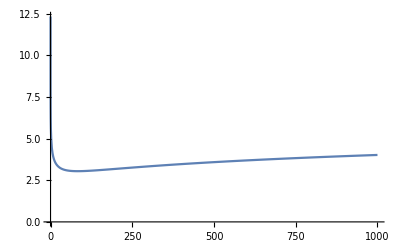
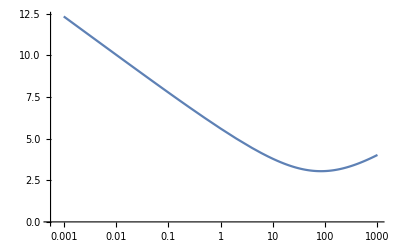
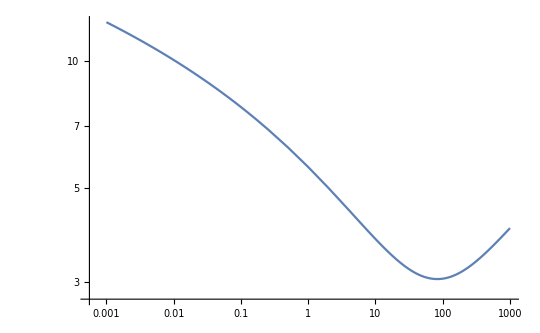

```mathematica
{ListLinePlot[CoPCircleN200A2d0List,Joined->True],ListLogLinearPlot[CoPCircleN200A2d0List,Joined->True],ListLogLogPlot[CoPCircleN200A2d0List,Joined->True]}
```

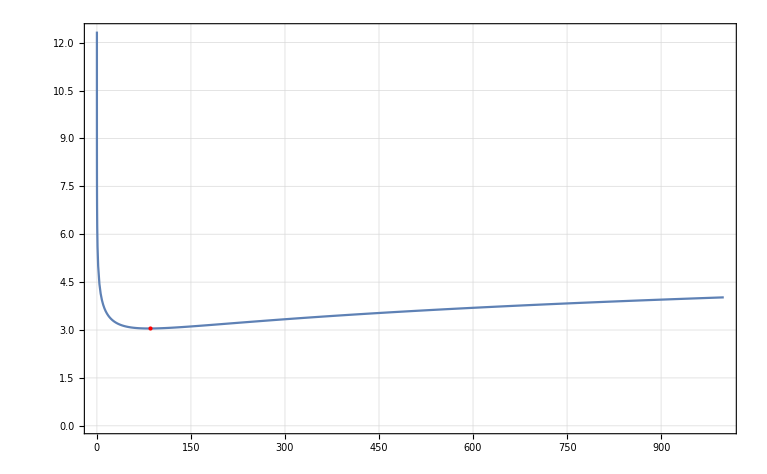

```mathematica
ListLinePlot[CoPCircleN200A2d0List,PlotTheme->"Detailed",MeshFunctions->{#2&},MeshStyle->Directive[Red,PointSize[Large]],Mesh->{{Min[CoPCircleN200A2d0List[[All,2]]]}}]
```

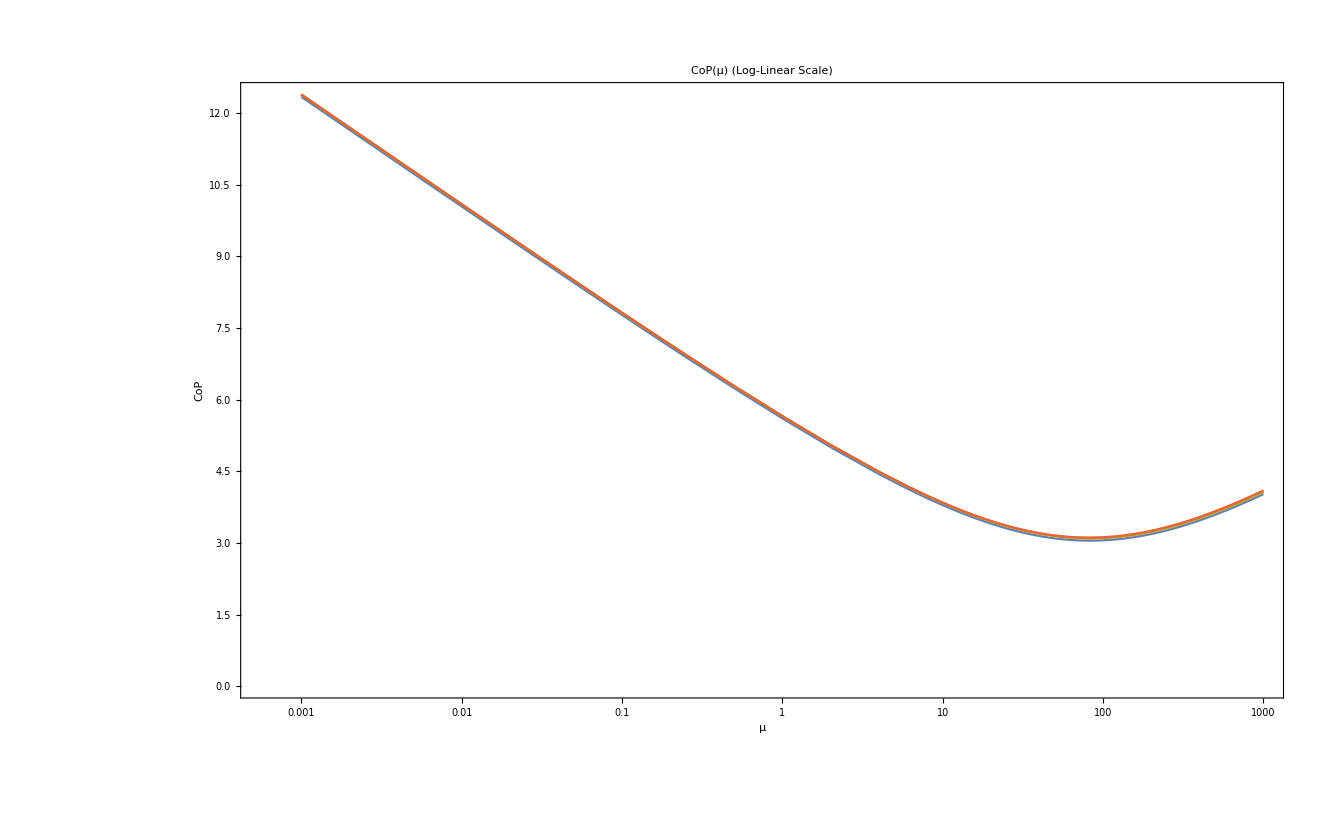

```mathematica
Show[ListLogLinearPlot[{CoPCircleN200A2d0List,CoPCircleN200A2d1List,CoPCircleN200A2d2List,CoPCircleN200A2d3List},PlotTheme->"Detailed",Joined->True],FrameLabel->{{HoldForm[CoP],None},{HoldForm[μ],None}},PlotLabel->HoldForm[ CoP[μ] (Log-Linear Scale)],LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Axes->True]
```

## N=300

### Data

```mathematica
(*CoPCircleN300A3d2List=Table[{μ,CoPVal[300,1/300,1/100,μ,3,3,2]},{μ,Listμ1}]*)
```

```mathematica
CoPCircleN300A3d2List={{1000,4.09113630362518},{998,4.089668830313288},{996,4.088199462571937},{994,4.086728196137228},{992,4.085255026695411},{990,4.083779949727697},{988,4.082302961263533},{986,4.080824056666906},{984,4.079343231673991},{982,4.077860481936833},{980,4.076375803050043},{978,4.074889190638982},{976,4.073400640201971},{974,4.0719101477478405},{972,4.070417708424629},{970,4.068923317932907},{968,4.067426971996917},{966,4.0659286659689124},{964,4.064428395538454},{962,4.062926156201378},{960,4.06142194358363},{958,4.059915752981114},{956,4.058407580276456},{954,4.056897420776394},{952,4.0553852697221755},{950,4.05387112318992},{948,4.052354976348123},{946,4.050836824659354},{944,4.049316663592055},{942,4.047794488683708},{940,4.046270295355705},{938,4.044744079039557},{936,4.043215835284378},{934,4.04168555934547},{932,4.040153246780959},{930,4.038618892979808},{928,4.037082493282794},{926,4.035544043291888},{924,4.0340035381766235},{922,4.032460973476567},{920,4.030916344406872},{918,4.029369646672626},{916,4.0278208752991285},{914,4.026270025839005},{912,4.024717093566881},{910,4.023162073886079},{908,4.021604962065732},{906,4.020045753518292},{904,4.018484443563855},{902,4.016921027539713},{900,4.015355500752368},{898,4.0137878584906},{896,4.012218096083235},{894,4.010646208878111},{892,4.009072192095091},{890,4.007496041050651},{888,4.00591775117616},{886,4.00433731756},{884,4.002754735756936},{882,4.001170000484034},{880,3.9995831077832795},{878,3.9979940521149087},{876,3.996402829516344},{874,3.994809434565087},{872,3.9932138630182767},{870,3.9916161099469996},{868,3.9900161706491746},{866,3.98841404021633},{864,3.986809714070852},{862,3.985203187375638},{860,3.983594455554719},{858,3.981983513576049},{856,3.9803703568090847},{854,3.9787549804759403},{852,3.977137379882706},{850,3.9755175501579263},{848,3.973895486585081},{846,3.972271184364622},{844,3.9706446387157297},{842,3.9690158450882413},{840,3.9673847984242654},{838,3.9657514941613345},{836,3.964115927414843},{834,3.9624780934188713},{832,3.9608379875399575},{830,3.959195604935154},{828,3.957550940815832},{826,3.9559039904507474},{824,3.954254749129008},{822,3.9526032120602177},{820,3.9509493745182676},{818,3.9492932317556875},{816,3.947634778995646},{814,3.9459740116137505},{812,3.9443109249486694},{810,3.942645513858061},{808,3.9409777740122465},{806,3.939307700637772},{804,3.937635288945791},{802,3.9359605341820196},{800,3.9342834319912967},{798,3.9326039773472314},{796,3.9309221656322046},{794,3.9292379923845138},{792,3.9275514526231645},{790,3.9258625419518443},{788,3.9241712556131874},{786,3.922477589043134},{784,3.920781537569048},{782,3.919083096594098},{780,3.9173822615682945},{778,3.915679027863867},{776,3.9139733909664542},{774,3.9122653462329255},{772,3.910554889231873},{770,3.908842015368721},{768,3.9071267201020885},{766,3.905408998977805},{764,3.9036888475701836},{762,3.901966261309806},{760,3.9002412358748955},{758,3.8985137667090837},{756,3.8967838494879845},{754,3.895051479821712},{752,3.8933166533121737},{750,3.891579365578334},{748,3.8898396123804604},{746,3.888097389381208},{744,3.8863526922945337},{742,3.884605516866683},{740,3.882855858897663},{738,3.881103714089922},{736,3.87934907838055},{734,3.8775919475745875},{732,3.875832317522254},{730,3.8740701841877123},{728,3.872305543416849},{726,3.8705383912409386},{724,3.8687687237480692},{722,3.8669965365986187},{720,3.8652218263618177},{718,3.8634445888318965},{716,3.861664820183877},{714,3.8598825166476876},{712,3.8580976743630493},{710,3.856310289674249},{708,3.854520358744055},{706,3.852727877938221},{704,3.850932843691066},{702,3.8491352524302016},{700,3.8473351004245346},{698,3.8455323842788176},{696,3.8437271007119227},{694,3.8419192460653027},{692,3.840108817113869},{690,3.8382958105488414},{688,3.836480223099588},{686,3.8346620515657746},{684,3.832841292763714},{682,3.8310179436816525},{680,3.8291920012615632},{678,3.8273634624459967},{676,3.8255323245440596},{674,3.8236985844929325},{672,3.821862239517796},{670,3.8200232870885027},{668,3.818181724352071},{666,3.8163375488585425},{664,3.814490757899371},{662,3.8126413492578637},{660,3.8107893204330314},{658,3.8089346691897017},{656,3.807077393364777},{654,3.8052174906529768},{652,3.8033549592119353},{650,3.8014897969756167},{648,3.79962200188888},{646,3.797751572413282},{644,3.795878506734936},{642,3.794002803293405},{640,3.792124460449478},{638,3.7902434768602813},{636,3.7883598513392984},{634,3.786473582385789},{632,3.7845846690663874},{630,3.7826931102752264},{628,3.7807989051463107},{626,3.7789020529430952},{624,3.7770025528741518},{622,3.7751004044211682},{620,3.7731956072399813},{618,3.771288160858518},{616,3.7693780651191533},{614,3.7674653198924557},{612,3.7655499256208014},{610,3.7636318819699},{608,3.7617111896168067},{606,3.7597878488920435},{604,3.757861860465085},{602,3.7559332251096116},{600,3.754001943736848},{598,3.7520680174107692},{596,3.7501314472799163},{594,3.7481922348741707},{592,3.7462503817402713},{590,3.744305889426417},{588,3.7423587600666703},{586,3.7404089956127384},{584,3.7384565984505054},{582,3.7365015707652756},{580,3.7345439154126003},{578,3.7325836351495547},{576,3.730620732984556},{574,3.7286552121577206},{572,3.726687076173527},{570,3.7247163287120304},{568,3.7227429733705293},{566,3.7207670145638785},{564,3.7187884563977742},{562,3.71680730361722},{560,3.714823560850905},{558,3.71283723316087},{556,3.71084832600123},{554,3.708856844698555},{552,3.7068627952107063},{550,3.7048661835403442},{548,3.702867016071727},{546,3.7008652994490543},{544,3.6988610404840707},{542,3.6968542465368355},{540,3.6948449250676525},{538,3.692833083803042},{536,3.6908187310788},{534,3.688801875112948},{532,3.6867825249190886},{530,3.6847606896351146},{528,3.682736378446619},{526,3.6807096013952245},{524,3.678680368665936},{522,3.676648690842296},{520,3.6746145787560742},{518,3.6725780437748363},{516,3.6705390977223904},{514,3.668497752514851},{512,3.6664540209328615},{510,3.6644079157838934},{508,3.6623594505980352},{506,3.660308639245602},{504,3.6582554959148452},{502,3.656200035489292},{500,3.6541422730896596},{498,3.6520822246999196},{496,3.650019906360545},{494,3.647955334980435},{492,3.6458885277083994},{490,3.643819502680979},{488,3.6417482779176362},{486,3.639674872503426},{484,3.6375993061598426},{482,3.6355215986979332},{480,3.6334417709505917},{478,3.6313598445672106},{476,3.6292758410707764},{474,3.627189783362648},{472,3.6251016947274075},{470,3.6230115990909035},{468,3.620919521325344},{466,3.618825486638446},{464,3.6167295212050274},{462,3.6146316520285913},{460,3.612531906732854},{458,3.610430313756551},{456,3.608326902434968},{454,3.606221702823611},{452,3.604114745957134},{450,3.602006063537971},{448,3.5998956883652444},{446,3.5977836540762103},{444,3.5956699953983895},{442,3.593554747598527},{440,3.5914379473884384},{438,3.5893196322578698},{436,3.587199840871548},{434,3.5850786126061194},{432,3.582955988543888},{430,3.5808320103201643},{428,3.5787067209527774},{426,3.5765801647938082},{424,3.5744523868064895},{422,3.572323434268588},{420,3.570193354464565},{418,3.568062196828848},{416,3.565930011993479},{414,3.563796851568641},{412,3.5616627690529588},{410,3.559527819195458},{408,3.5573920581416254},{406,3.5552555436261697},{404,3.553118335047197},{402,3.550980493177979},{400,3.5488420807127707},{398,3.546703161726448},{396,3.5445638022314405},{394,3.5424240699221814},{392,3.5402840344883386},{390,3.538143767308404},{388,3.536003341635507},{386,3.533862832862411},{384,3.531722318514092},{382,3.529581877784881},{380,3.5274415923458977},{378,3.5253015461826283},{376,3.523161825079597},{374,3.521022517583286},{372,3.518883714329139},{370,3.516745508629442},{368,3.5146079962695587},{366,3.5124712755062504},{364,3.510335447353862},{362,3.5082006155778456},{360,3.506066886760388},{358,3.5039343703322747},{356,3.5018031786961648},{354,3.499673427543208},{352,3.4975452353320584},{350,3.4954187241312766},{348,3.4932940192655058},{346,3.4911712490398568},{344,3.4890505462232464},{342,3.486932046259262},{340,3.4848158891259344},{338,3.482702218016619},{336,3.4805911805554413},{334,3.4784829283628977},{332,3.476377617051842},{330,3.474275406772795},{328,3.4721764622336373},{326,3.470080952483029},{324,3.4679890515482636},{322,3.4659009383383483},{320,3.463816796626948},{318,3.461736815706647},{316,3.459661189564786},{314,3.457590118772954},{312,3.455523808564416},{310,3.453462470776055},{308,3.4514063230157714},{306,3.4493555891739938},{304,3.44731049945082},{302,3.4452712910621885},{300,3.4432382080191086},{298,3.44121150104569},{296,3.439191428634704},{294,3.4371782568069937},{292,3.435172259143758},{290,3.433173717808383},{288,3.431182922537146},{286,3.4292001725044328},{284,3.4272257754045072},{282,3.4252600481736284},{280,3.423303317754357},{278,3.421355919858894},{276,3.4194181987958667},{274,3.417490519394337},{272,3.4155732428808725},{270,3.413666751904161},{268,3.4117714360134332},{266,3.409887710454784},{264,3.408016504455356},{262,3.4061566108261663},{260,3.404310150660093},{258,3.402477011420306},{256,3.40065766550822},{254,3.398852597971672},{252,3.39706229970718},{250,3.3952873052651524},{248,3.3935281334287817},{246,3.3917853435724545},{244,3.3900595162750027},{242,3.38835120690258},{240,3.3866610458734776},{238,3.384989662778132},{236,3.38333771016059},{234,3.3817058244325415},{232,3.3800947342404566},{230,3.3785051441735474},{228,3.3769377947302317},{226,3.375393451985323},{224,3.373872908635648},{222,3.3723769887789343},{220,3.3709065285646025},{218,3.3694624194366627},{216,3.3680455670212166},{214,3.366656913583018},{212,3.3652974350544764},{210,3.3639681429778467},{208,3.3626700841344674},{206,3.3614043468304136},{204,3.3601720559010495},{202,3.3589743804216012},{200,3.357812531419567},{198,3.3566877705723615},{196,3.355601393850614},{194,3.354554765161336},{192,3.3535492890003273},{190,3.3525864275964503},{188,3.3516676992658767},{186,3.350794684055865},{184,3.349969023293533},{182,3.349192425357877},{180,3.3484666653342905},{178,3.3477935953292417},{176,3.34717513521146},{174,3.346613294628986},{172,3.3461101610419877},{170,3.3456679105222173},{168,3.3452888136888665},{166,3.3449752372150523},{164,3.344729651643526},{162,3.344554634261552},{160,3.344452878378026},{158,3.344427196098349},{156,3.3444805271188245},{154,3.3446159450767023},{152,3.3448366649780614},{150,3.345146052216755},{148,3.345547630496003},{146,3.346045089534922},{144,3.3466422994858065},{142,3.3473433169110938},{140,3.3481523987104262},{138,3.3490740135374235},{136,3.3501128555206505},{134,3.351273858682126},{132,3.3525622117176375},{130,3.3539833748735055},{128,3.355543097837281},{126,3.357247439491144},{124,3.359102788142918},{122,3.3611158830966237},{120,3.3632938446460154},{118,3.36564419426033},{116,3.3681748869636134},{114,3.3708943433555745},{112,3.373811485238041},{110,3.3769357648652347},{108,3.38027722473895},{106,3.3838465220416016},{104,3.387654994496684},{102,3.391714706088604},{100,3.3960385111128555},{98,3.4006401201865564},{96,3.405534174189534},{94,3.4107363260065107},{92,3.416263330668334},{90,3.422133146724145},{88,3.428365048627133},{86,3.434979752257613},{84,3.441999556072207},{82,3.449448498953873},{80,3.4573525384234727},{78,3.4657397517537327},{76,3.4746405635914512},{74,3.4840880051858356},{72,3.4941180078863145},{70,3.504769742629948},{68,3.516086004900842},{66,3.5281136615211057},{64,3.5409041662679615},{62,3.554514158997199},{60,3.5690061645624125},{58,3.5844494125774187},{56,3.600920803201576},{54,3.618506051931907},{52,3.6373010535251744},{50,3.657413518148128},{48,3.678964946990115},{46,3.702093034640518},{44,3.726954614113723},{42,3.7537292981867236},{40,3.7826240213334836},{38,3.8138787657804505},{36,3.847773858093308},{34,3.8846393825217738},{32,3.9248674901388423},{30,3.9689287384564005},{28,4.017394150447489},{26,4.070965566947089},{24,4.130518324689437},{22,4.197162775810045},{20,4.272335563076372},{18,4.357939714281512},{16,4.456568545791294},{14,4.571881547177488},{12,4.70927518771307},{10,4.877177525522085},{8,5.089821463286979},{6,5.374128101883515},{4,5.7911668463323815},{2,6.538401400745592},{1,7.317082314688452},{1/2,8.117694849886307},{1/4,8.933791926749171},{1/6,9.416492680972045},{1/8,9.760850915027559},{1/10,10.028870259874346},{1/12,10.248381936566938},{1/14,10.434308234593924},{1/16,10.595589981710724},{1/18,10.738011053337702},{1/20,10.865529972300216},{1/22,10.98097568528117},{1/24,11.086440451742016},{1/26,11.183515425718197},{1/28,11.273438968148533},{1/30,11.357193836084575},{1/32,11.435573078449073},{1/34,11.50922590706412},{1/36,11.578690531759493},{1/38,11.644418113497604},{1/40,11.706790620970681},{1/42,11.766134232147374},{1/44,11.822729721504363},{1/46,11.876820588765948},{1/48,11.928619290052518},{1/50,11.978312342900525},{1/52,12.0260643093696},{1/54,12.072021326271814},{1/56,12.116313479717567},{1/58,12.159057239510789},{1/60,12.200357288766208},{1/62,12.240308112500944},{1/64,12.278994953810304},{1/66,12.316495490102303},{1/68,12.352880293521988},{1/70,12.388214008915515},{1/72,12.422555535741866},{1/74,12.455959120296416},{1/76,12.4884746948626},{1/78,12.52014824167816},{1/80,12.55102226751259},{1/82,12.581136334682714},{1/84,12.610526712928849},{1/86,12.639227549157486},{1/88,12.667270515522615},{1/90,12.694684934724828},{1/92,12.721498498479216},{1/94,12.747736968578938},{1/96,12.773424318232443},{1/98,12.798583516962152},{1/100,12.823235676844591},{1/102,12.847401116882587},{1/104,12.871098236792262},{1/106,12.894345094092465},{1/108,12.917158498407879},{1/110,12.939554253324012},{1/112,12.961547675708701},{1/114,12.983152491474172},{1/116,13.004382362444996},{1/118,13.025250296902414},{1/120,13.04576807067553},{1/122,13.065947745557583},{1/124,13.085799807378427},{1/126,13.105334809716574},{1/128,13.124563043465253},{1/130,13.143493605494193},{1/132,13.162136057200577},{1/134,13.180497987332432},{1/136,13.198589560263065},{1/138,13.216416643981066},{1/140,13.233988323871328},{1/142,13.251310874447135},{1/144,13.268391641573013},{1/146,13.285237310337333},{1/148,13.301854377789713},{1/150,13.318248720910988},{1/152,13.334425838305037},{1/154,13.350392408945794},{1/156,13.366153384745223},{1/158,13.381713564233847},{1/160,13.397078718618296},{1/162,13.412252844352473},{1/164,13.427241923310044},{1/166,13.44204896464863},{1/168,13.456679257351558},{1/170,13.47113641848693},{1/172,13.485425132187183},{1/174,13.49954822356344},{1/176,13.513511210002514},{1/178,13.52731590567272},{1/180,13.540966860103861},{1/182,13.554467662416927},{1/184,13.567820469724941},{1/186,13.581029465169435},{1/188,13.594097539729844},{1/190,13.60702670629797},{1/192,13.619821584805882},{1/194,13.632484155654172},{1/196,13.645016549351773},{1/198,13.657421486189849},{1/200,13.669702980130905},{1/202,13.681862161152893},{1/204,13.693901139790428},{1/206,13.70582383340384},{1/208,13.717630275880715},{1/210,13.729324659883035},{1/212,13.740907946802777},{1/214,13.75238326183798},{1/216,13.763751005862039},{1/218,13.7750152897078},{1/220,13.786176388129098},{1/222,13.797236105951946},{1/224,13.808197822517533},{1/226,13.819060473642715},{1/228,13.829829680800682},{1/230,13.840503759585506},{1/232,13.851085798370988},{1/234,13.861576131272221},{1/236,13.871978943959952},{1/238,13.882293044188096},{1/240,13.892521516768166},{1/242,13.902664557489645},{1/244,13.912725211387011},{1/246,13.922703283562191},{1/248,13.932600342612979},{1/250,13.942418537096149},{1/252,13.952158438406407},{1/254,13.96182113852459},{1/256,13.971408308449877},{1/258,13.980921393632102},{1/260,13.990359466017257},{1/262,13.999727358461291},{1/264,14.00902327907037},{1/266,14.01824936259747},{1/268,14.027405109050502},{1/270,14.036494836317821},{1/272,14.045515672043944},{1/274,14.054471953438691},{1/276,14.063363050742693},{1/278,14.072189740884111},{1/280,14.080952067236833},{1/282,14.08965347746396},{1/284,14.098295012998976},{1/286,14.106873479358452},{1/288,14.115392407378746},{1/290,14.123851256256671},{1/292,14.1322539846077},{1/294,14.140600818804012},{1/296,14.148888638484877},{1/298,14.157120491275395},{1/300,14.165298373718894},{1/302,14.1734234333677},{1/304,14.181492778434775},{1/306,14.189511040506762},{1/308,14.197475470393686},{1/310,14.205387052512645},{1/312,14.213252035753126},{1/314,14.22106396815268},{1/316,14.22882625553556},{1/318,14.236540531225309},{1/320,14.244206819076043},{1/322,14.25182376472426},{1/324,14.259393174589933},{1/326,14.266920475097791},{1/328,14.274396308537524},{1/330,14.281830816084762},{1/332,14.28921938998059},{1/334,14.29656122575167},{1/336,14.303863578978582},{1/338,14.311119565641684},{1/340,14.318333075927471},{1/342,14.32550365469029},{1/344,14.332632039731793},{1/346,14.339722920560268},{1/348,14.34677040957562},{1/350,14.353778100917673},{1/352,14.36074256028997},{1/354,14.367672913374893},{1/356,14.374562724126502},{1/358,14.38141207363555},{1/360,14.388223342646198},{1/362,14.394999925143082},{1/364,14.40173622801343},{1/366,14.408436260638917},{1/368,14.415101165718381},{1/370,14.42172871343138},{1/372,14.428321763893534},{1/374,14.434877402893392},{1/376,14.441400291153206},{1/378,14.447887478057753},{1/380,14.454340865910504},{1/382,14.460760076534267},{1/384,14.467146318408973},{1/386,14.473492814464402},{1/388,14.479816926903668},{1/390,14.486105186430779},{1/392,14.492357874392946},{1/394,14.498584103602637},{1/396,14.50477535262154},{1/398,14.510936794671004},{1/400,14.517063953132206},{1/402,14.523165948185051},{1/404,14.529234989095011},{1/406,14.535273783673947},{1/408,14.541283730689983},{1/410,14.547260960146057},{1/412,14.553215434804338},{1/414,14.559137730974994},{1/416,14.565029951182071},{1/418,14.570896313371263},{1/420,14.57673523757202},{1/422,14.582544951125668},{1/424,14.588325317664154},{1/426,14.594082861107628},{1/428,14.599810114422645},{1/430,14.60551220576305},{1/432,14.611188095947403},{1/434,14.61683672550928},{1/436,14.622453723242373},{1/438,14.628053509829511},{1/440,14.633629326872708},{1/442,14.639174926310488},{1/444,14.644697007368432},{1/446,14.650193027249319},{1/448,14.65566449173503},{1/450,14.661115269911726},{1/452,14.66653746116602},{1/454,14.671936237033865},{1/456,14.677309682338402},{1/458,14.682665389163862},{1/460,14.687994895784643},{1/462,14.693299985586824},{1/464,14.698580638785803},{1/466,14.703841881031906},{1/468,14.709082934345158},{1/470,14.714296853374824},{1/472,14.719487603255425},{1/474,14.724664864157068},{1/476,14.7298105229452},{1/478,14.734941860611682},{1/480,14.740046072767422},{1/482,14.74513446816623},{1/484,14.750193940113423},{1/486,14.755243912230878},{1/488,14.760263160801275},{1/490,14.765265859550563},{1/492,14.770253282737842},{1/494,14.775211366691993},{1/496,14.780152913268843},{1/498,14.785075608982936},{1/500,14.789980037600907},{1/502,14.794860980848123},{1/504,14.799721990908772},{1/506,14.804568707870155},{1/508,14.809387252975974},{1/510,14.81419989884714},{1/512,14.818987424363252},{1/514,14.823756610452776},{1/516,14.828506026326345},{1/518,14.83323200038053},{1/520,14.83794306193207},{1/522,14.842643808827697},{1/524,14.847324348344586},{1/526,14.85198293799937},{1/528,14.856626825531567},{1/530,14.861248713635039},{1/532,14.865847779160596},{1/534,14.870448112061538},{1/536,14.875020428261806},{1/538,14.879572354811538},{1/540,14.884106000788885},{1/542,14.88862279205247},{1/544,14.893119470113419},{1/546,14.89762982448433},{1/548,14.902100931479087},{1/550,14.906537550901776},{1/552,14.910998630486764},{1/554,14.915414834760325},{1/556,14.919830828128594},{1/558,14.924220125738632},{1/560,14.928585507114189},{1/562,14.932959042477451},{1/564,14.93730908274535},{1/566,14.941636214049485},{1/568,14.945949652848931},{1/570,14.950243380018224},{1/572,14.954529883996939},{1/574,14.958806753665282},{1/576,14.963055875361846},{1/578,14.96729436868035},{1/580,14.971522883592062},{1/582,14.975733697905225},{1/584,14.979932378604344},{1/586,14.984112012460452},{1/588,14.988280289093387},{1/590,14.992430678164117},{1/592,14.996574675903762},{1/594,15.000688236605976},{1/596,15.004810179550512},{1/598,15.008910185490315},{1/600,15.01299612332004},{1/602,15.01706644202592},{1/604,15.021115873690215},{1/606,15.025165413483231},{1/608,15.029189645557722},{1/610,15.033215458689074},{1/612,15.037216349076028},{1/614,15.041211355104156},{1/616,15.04518541566122},{1/618,15.049138477305183},{1/620,15.053091951731803},{1/622,15.057042961838233},{1/624,15.060975116500185},{1/626,15.064889560673839},{1/628,15.06878887474444},{1/630,15.072680588588506},{1/632,15.076554819547285},{1/634,15.080422286379855},{1/636,15.084267247441954},{1/638,15.088117179966687},{1/640,15.091947024844247},{1/642,15.09576195780342},{1/644,15.099555829287834},{1/646,15.103360878227168},{1/648,15.107143139744162},{1/650,15.110912764525526},{1/652,15.114665508411914},{1/654,15.1184145818562},{1/656,15.122141351930033},{1/658,15.125876539453493},{1/660,15.129589134222295},{1/662,15.133290581185312},{1/664,15.136976607006215},{1/666,15.140653917082588},{1/668,15.144324011534161},{1/670,15.14797689693546},{1/672,15.15162931820056},{1/674,15.155267544988455},{1/676,15.158891502351377},{1/678,15.162504123495012},{1/680,15.166102926833146},{1/682,15.169698839652504},{1/684,15.173281817482597},{1/686,15.176853966008698},{1/688,15.18041853584735},{1/690,15.18396612493659},{1/692,15.187505824689152},{1/694,15.191029585301594},{1/696,15.194556484871534},{1/698,15.198070930691244},{1/700,15.201550029921968},{1/702,15.205063140995641},{1/704,15.208540144576208},{1/706,15.212010349669404},{1/708,15.215473764188019},{1/710,15.218923828659339},{1/712,15.222352203330285},{1/714,15.225789239652855},{1/716,15.2292199683471},{1/718,15.232634411663215},{1/720,15.236034014971596},{1/722,15.239431242847987},{1/724,15.242818368787857},{1/726,15.24618875895168},{1/728,15.249554299065622},{1/730,15.25291263835305},{1/732,15.256246349444794},{1/734,15.259594774593898},{1/736,15.262925025963336},{1/738,15.266242133719448},{1/740,15.269559580904485},{1/742,15.272856788304178},{1/744,15.27613673581475},{1/746,15.279430285384151},{1/748,15.282704825752388},{1/750,15.285971622894957},{1/752,15.28923583900675},{1/754,15.292483609945236},{1/756,15.295726289192253},{1/758,15.298957868217459},{1/760,15.302175752176106},{1/762,15.305392105465353},{1/764,15.308606234374764},{1/766,15.311804791970848},{1/768,15.314994965116101},{1/770,15.318164213532668},{1/772,15.321354531242207},{1/774,15.324520863142661},{1/776,15.327676491189843},{1/778,15.330809128189147},{1/780,15.333960311105479},{1/782,15.337099164396303},{1/784,15.340222542891233},{1/786,15.343333473787071},{1/788,15.34644958222287},{1/790,15.349550948621431},{1/792,15.35264329964106},{1/794,15.355724720343902},{1/796,15.358805095089648},{1/798,15.361872087914158},{1/800,15.364935046498573},{1/802,15.367992680598576},{1/804,15.371041044862444},{1/806,15.374062541916434},{1/808,15.37710360683632},{1/810,15.380138491072104},{1/812,15.383145215854244},{1/814,15.386148344740379},{1/816,15.389148232620434},{1/818,15.392161917424001},{1/820,15.395151619987582},{1/822,15.398129996757639},{1/824,15.401100532175665},{1/826,15.40406477547316},{1/828,15.407028332121653},{1/830,15.409972901815923},{1/832,15.412927746107421},{1/834,15.415853114332322},{1/836,15.418778689506956},{1/838,15.421717940261647},{1/840,15.424622023909963},{1/842,15.427542941006475},{1/844,15.43043675831051},{1/846,15.433323106773942},{1/848,15.436227022037857},{1/850,15.43911024879098},{1/852,15.44198692062666},{1/854,15.444859378038855},{1/856,15.44771642217286},{1/858,15.450564377952638},{1/860,15.453424087636778},{1/862,15.456268911067472},{1/864,15.459103514100386},{1/866,15.4619284134141},{1/868,15.464747953295147},{1/870,15.467566830525966},{1/872,15.47038273213142},{1/874,15.473181594748127},{1/876,15.475961973519972},{1/878,15.478759486116685},{1/880,15.481532153267134},{1/882,15.48432699350166},{1/884,15.487103534405714},{1/886,15.489854322873015},{1/888,15.492623801921738},{1/890,15.495320218664949},{1/892,15.498119299609021},{1/894,15.500867256645655},{1/896,15.503595888318607},{1/898,15.506320236380718},{1/900,15.509037764104889},{1/902,15.511762384856189},{1/904,15.514440903538373},{1/906,15.517148380780222},{1/908,15.519870435895372},{1/910,15.522539720148513},{1/912,15.525222428916871},{1/914,15.527920632803184},{1/916,15.530601157404668},{1/918,15.533278211967064},{1/920,15.535938780228118},{1/922,15.53859665968576},{1/924,15.541245760867735},{1/926,15.543874199259148},{1/928,15.546509239235938},{1/930,15.54916684260373},{1/932,15.551789892981313},{1/934,15.554417205454778},{1/936,15.557032352588077},{1/938,15.559636894411373},{1/940,15.562253223339862},{1/942,15.56485502273971},{1/944,15.567450217176322},{1/946,15.570023174533866},{1/948,15.572624143635007},{1/950,15.575203610804602},{1/952,15.577724007012803},{1/954,15.580336938391676},{1/956,15.582911473145368},{1/958,15.585455639463062},{1/960,15.587985583867576},{1/962,15.590563740047791},{1/964,15.593098472751224},{1/966,15.595639720049055},{1/968,15.598163005287805},{1/970,15.600692114647016},{1/972,15.603197240709644},{1/974,15.605720869877343},{1/976,15.608224126302993},{1/978,15.610734133088314},{1/980,15.613193064101447},{1/982,15.615719848612967},{1/984,15.618230902941598},{1/986,15.620689137867863},{1/988,15.623130671225146},{1/990,15.6256369151879},{1/992,15.628114480402873},{1/994,15.630589732746037},{1/996,15.633045863450725},{1/998,15.63551211382321},{1/1000,15.637963139517948}};
```

### Plots

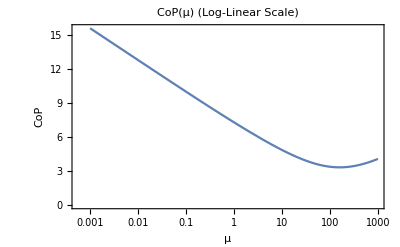

```mathematica
Show[ListLogLinearPlot[{CoPCircleN300A3d2List},PlotTheme->"Detailed",Joined->True],FrameLabel->{{HoldForm[CoP],None},{HoldForm[μ],None}},PlotLabel->HoldForm[ CoP[μ] (Log-Linear Scale)],LabelStyle->{FontFamily->"Arial",GrayLevel[0]},Axes->True]
```

## N=200, w=2

### μ=1/100

```mathematica
CoPCircleListN100dA10mu001=Table[{d/2,CoPVal[100,1/100,1/100,1/100,10,10,d]},{d,0,(100-(10+10))/2}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{40.4469+0. ⅈ,371.206+0. ⅈ,4.11336×10^-6+0. ⅈ,3.76092×10^-6+0. ⅈ,-94.0997+0. ⅈ,-21.9536+0. ⅈ,0.0000230486+0. ⅈ,0.0000966231+0. ⅈ,-2.71572+0. ⅈ,-37.3651+0. ⅈ,0.000559216+0. ⅈ,«29»,-40.3822+0. ⅈ,370.613+0. ⅈ,-2.63141×10^-6+0. ⅈ,2.40595×10^-6+0. ⅈ,23.1384+0. ⅈ,-5.39822+0. ⅈ,-1.85135×10^-6+0. ⅈ,7.76112×10^-6+0. ⅈ,0.0646758+0. ⅈ,-0.889861+0. ⅈ,«30»},{«1»},«47»,{«1»},«30»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

$Aborted

### μ=1/10

```mathematica
CoPCircleListN100dA10mu01=Table[{d,CoPVal[100,1/100,1/100,1/10,10,10,d]},{d,0,(100-(10+10))/2}]
```

### μ=1

```mathematica
CoPCircleListN100dA10mu1=Table[{d,CoPVal[100,1/100,1/100,1,10,10,d]},{d,0,(100-(10+10))/2}]
```

### μ=10

```mathematica
CoPCircleListN100dA10mu10=Table[{d,CoPVal[100,1/100,1/100,10,10,10,d]},{d,0,(100-(10+10))/2}]
```

### μ=100

```mathematica
CoPCircleListN100dA10mu100=Table[{d,CoPVal[100,1/100,1/100,100,10,10,d]},{d,0,(100-(10+10))/2}]
```

## Boson on a Line

## CoP

The function used in the Gaussian optimization for the line is CoPValLine[m,μ,dimA1,dimB1,d]  where:
m is the mass of the scalar field
(δ=1 is the fixed lattice spacing )
μ is the reference state frequency (assumed to be 1 in the following)
dimA1 is the number of sites in partition A1 of the subsystem
dimB1 is the number of sites in partition B1 of the subsystem
d is the lattice separation between the subsystem partitions A1 and B1
dimPur=dimA1+dimB1 is the dimension of the purification (assumed to be minimal)

In the following ‘w’ is also being used as the number of sites in the partitions A1 and B1 (assumed to be the same).

```mathematica
KGlineCorr[{NN_,m_,μ_}]:=KGlineCorr[{NN,m,μ}]={Table[(((μ HypergeometricPFQRegularized[{1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])/(2 √(4+m^2)))//N),{Mn,0,NN-1}],Table[((1/(2 μ)√(4+m^2) HypergeometricPFQRegularized[{-1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])//N),{Mn,0,NN-1}]}; 
KGlineToe[var_]:=KGlineToe[var]={ToeplitzMatrix[KGlineCorr[var]⟦1⟧],ToeplitzMatrix[KGlineCorr[var]⟦2⟧]};
KGlineCM[var_]:=KGlineCM[var]=ArrayFlatten[{{2KGlineToe[var]⟦1⟧,0.},{0.,2KGlineToe[var]⟦2⟧}}];
KGlineCMqpqp[{NN_,m_,μ_}]:=KGlineCMqpqp[{NN,m,μ}]=GOΩqpqp[NN].GOqpqpFROMqqpp[NN].KGlineCM[{NN,m,μ}].Transpose[GOqpqpFROMqqpp[NN]].Transpose[GOΩqpqp[NN]];
```

```mathematica
KGlineCMSep[{m_,μ_,dimA_,dimB_,d_}]:=KGlineCMSep[{m,μ,dimA,dimB,d}]=Module[{ind,KGlineCorr,KGlineToe},ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]]; 
KGlineCorr[{dimA+dimB+d,m,μ}]:={Table[(((μ HypergeometricPFQRegularized[{1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])/(2 √(4+m^2)))//N),{Mn,0,dimA+dimB+d-1}],Table[((1/(2 μ)√(4+m^2) HypergeometricPFQRegularized[{-1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])//N),{Mn,0,dimA+dimB+d-1}]}; 
KGlineToe[var_]:={ToeplitzMatrix[KGlineCorr[var]⟦1⟧],ToeplitzMatrix[KGlineCorr[var]⟦2⟧]};
GOΩqpqp[dimA+dimB].GOqpqpFROMqqpp[dimA+dimB].(ArrayFlatten[{{2KGlineToe[{dimA+dimB+d,m,μ}]⟦1,ind,ind⟧,0.},{0.,2KGlineToe[{dimA+dimB+d,m,μ}]⟦2,ind,ind⟧}}]).Transpose[GOqpqpFROMqqpp[dimA+dimB]].Transpose[GOΩqpqp[dimA+dimB]]]
```

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
nb=NotebookDirectory[];
```

```mathematica
Directory[]
nb
```

/home/hcamargo/Nextcloud/Mathematica Calculations/Purifications

/home/hcamargo/Nextcloud/Mathematica Calculations/Purifications/

```mathematica
VacCoPLine[m_,μ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
dimPur=dimA1+dimB1;
CM0=KGlineCMSep[{m,μ,dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
J0=JR;
function=GOCoPBos[JT]; 
gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; 
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
CoPValLine[m_,μ_,dimA1_,dimB1_,d_]:=VacCoPLine[m,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
CoPTimeLine[m_,μ_,dimA1_,dimB1_,d_]:=VacCoPLine[m,μ,dimA1,dimB1,d]⟦1⟧;
```